## Initialize

```mathematica
Quantum[σF_,t_,τ_,A1_,A2_,A3_,B1_,B2_,B3_]:=ⅇ^((2 σF^2 (-3 A3^2-4 A3^2 B1^2 σF^4-4 A3^2 B1 B2 σF^4-4 A3^2 B2^2 σF^4+A2^2 (-3-4 (B1^2+B1 B3+B3^2) σF^4)+A1^2 (-3-4 (B2^2+B2 B3+B3^2) σF^4)+3 A3 t+4 A3 B1 B2 σF^4 t+8 A3 B2^2 σF^4 t-4 A3 B1 B3 σF^4 t+4 A3 B2 B3 σF^4 t-3 t^2-4 B2^2 σF^4 t^2-4 B2 B3 σF^4 t^2-4 B3^2 σF^4 t^2+(6 A3+8 A3 (B1^2+B1 B2+B2^2) σF^4-(3+4 (B1 (B2-B3)+B2 (2 B2+B3)) σF^4) t) τ-(3+4 (B1^2+B1 B2+B2^2) σF^4) τ^2+A1 (A2 (3+4 (B1 (-B2+B3)+B3 (B2+2 B3)) σF^4)+3 (A3-2 t-τ)+4 σF^4 (A3 B1 (B2-B3)+A3 B2 (2 B2+B3)-2 B2 B3 t-B2 (B1+B3) τ-2 B2^2 (t+τ)+B3 (-2 B3 t+B1 τ)))+A2 (A3 (3+4 (2 B1^2-B2 B3+B1 (B2+B3)) σF^4)+3 (t-τ)+4 σF^4 (-2 B1^2 τ+B3 (2 B3 t+B2 (t+τ))-B1 (B3 (-t+τ)+B2 (t+τ))))))/(9+8 (2 B1^2+2 B2^2+B2 B3+2 B3^2+B1 (B2+B3)) σF^4+16 (B2 B3+B1 (B2+B3))^2 σF^8));Classical[σF_,t_,τ_,A1_,A2_,A3_,B1_,B2_,B3_]:=ⅇ^(-(2 σF^2 (A3^2-A3 t+t^2+2 A3^2 B1^2 σF^4+2 A3^2 B2^2 σF^4-4 A3 B2^2 t σF^4+2 B2^2 t^2 σF^4+2 B3^2 t^2 σF^4+A2^2 (1+2 (B1^2+B3^2) σF^4)+A1^2 (1+2 (B2^2+B3^2) σF^4)+(-2 A3+t-4 A3 (B1^2+B2^2) σF^4+4 B2^2 t σF^4) τ+(1+2 (B1^2+B2^2) σF^4) τ^2-A2 (A3+t+4 A3 B1^2 σF^4-τ+4 σF^4 (B3^2 t-B1^2 τ))+A1 (2 t-A3 (1+4 B2^2 σF^4)-A2 (1+4 B3^2 σF^4)+τ+4 σF^4 (B3^2 t+B2^2 (t+τ)))))/(3+8 σF^4 (B1^2+B2^2+B3^2+2 (B2^2 B3^2+B1^2 (B2^2+B3^2)) σF^4)));
Do[KF[i]=0,{i,1,3}];
Do[A[i]=0,{i,1,3}];
range=50;
newrange=500;
```

# Final plots v3

```mathematica
σFtest=0.5;
x[1]=0;
x[2]=12.5;
x[3]=50;
beta[1] = 1;
beta[2]=-2;
beta[3]=-3;
Do[B[i,j]=beta[i]x[j],{i,1,3},{j,1,3}]
```

## numerical

```mathematica
(*Do[k[i][ω_,ωF_]=B[i,2] (ω-ωF)^2,{i,1,3}]
f[ω_,ωF_,σF_]=Exp[-(ω-ωF)^2/(2 σF^2)];
ClearAll[integrand,psi]
Do[
Do[
integrand[t,τ][ω1_,ω2_,ω3_,t1_,ωF_,σF_]=f[ω1,ωF,σF]*f[ω2,ωF,σF]*f[ω3,ωF,σF]*Exp[ⅈ (k[1][ω1,ωF]+k[2][ω2,ωF]+k[3][ω3,ωF]-ω1 t1 -ω2 (t1+t)-ω3 (t1+t+τ))],
{t,-range,range,1}
],{τ,-range,range,1}
]
Monitor[Do[
Do[
psi[t,τ]=NIntegrate[integrand[t,τ][1/3+ϵ,1/3+δ,1/3-ϵ-δ,0,1/3,σFtest],{ϵ,-1/3,2/3},{δ,-1/3,2/3-ϵ}];psi[-t,-τ]=psi[t,τ]
,{t,-range,range,1}],{τ,0,range,1}],{t,τ}]
qunumerical=Table[Abs[psi[t-range -1,τ-range -1]]^2,{t,1,2 range +1},{τ,1,2 range +1}];
qunumerical= qunumerical/Total[Total[qunumerical]];*)
```

## backup

```mathematica
qunumerical12312point5zeropoint5={{3.919665637655698*^-8,4.645800528811434*^-8,6.119558639951625*^-8,8.305221753681047*^-8,1.1074847521138054*^-7,1.4331289366868052*^-7,1.7983959509993365*^-7,2.1700453710269413*^-7,2.4731275868915607*^-7,2.615124588199878*^-7,2.540706932486469*^-7,2.264896599021922*^-7,1.8534055765097023*^-7,1.3805727426133838*^-7,9.17883724010382*^-8,5.579270529591871*^-8,4.236839695089619*^-8,6.274819390940522*^-8,1.2110808641319773*^-7,2.1275764995771017*^-7,3.2753153010987766*^-7,4.5308916295545096*^-7,5.7396727427328*^-7,6.69525232190667*^-7,7.174004853211935*^-7,7.033418547964421*^-7,6.300035322337218*^-7,5.168032173114839*^-7,3.91165730028693*^-7,2.787427495539907*^-7,1.9879196364472926*^-7,1.639015432855906*^-7,1.795931146155694*^-7,2.423736696884792*^-7,3.392319788809504*^-7,4.5135975981700723*^-7,5.60636441124623*^-7,6.544924798605448*^-7,7.262201175315804*^-7,7.716719429852869*^-7,7.859564460332338*^-7,7.635660950209051*^-7,7.028279224959252*^-7,6.120270984919472*^-7,5.121986760829472*^-7,4.327793037876023*^-7,4.01113620656196*^-7,4.315108475042696*^-7,5.198217688522406*^-7,6.453113043578002*^-7,7.77394080179144*^-7,4.6984481794937367*^-7,4.517916620699462*^-7,5.245699546237365*^-7,7.107849924549304*^-7,1.0084653871835153*^-6,1.350060951909203*^-6,1.6032235110992138*^-6,1.639456657581705*^-6,1.4219350819415919*^-6,1.0344564329375972*^-6,6.277216321993746*^-7,3.349392868347356*^-7,2.2196631909041138*^-7,2.880866641919215*^-7,4.928364578728372*^-7,7.899824935518505*^-7,1.1627818530285846*^-6,1.6360535714386213*^-6,2.2270069010562125*^-6,2.848201125228076*^-6,3.26138798298174*^-6,3.1826687338418165*^-6,2.505075455669819*^-6,1.453488479705006*^-6,5.000359994588392*^-7,6.964685491225795*^-8,2.647871485973128*^-7,8.294545679640254*^-7,1.3631057463340126*^-6,1.5958928520419622*^-6,1.5260664988698263*^-6,1.3679720189975532*^-6,1.3963292976037292*^-6,1.7945974722637219*^-6,2.564572076408223*^-6,3.5164814231056294*^-6,4.346227434593499*^-6,4.776185714959534*^-6,4.6867305497916464*^-6,4.156210445887088*^-6,3.390239774849594*^-6,2.6035875547765203*^-6,1.938552417456635*^-6,1.4506294280926605*^-6,1.1330977160097635*^-6,9.440393442139364*^-7,8.278986218371675*^-7,7.378650153338584*^-7,6.52550640000838*^-7,5.727571462571278*^-7},{6.047050871895102*^-8,8.415460893386798*^-8,1.1217342831344125*^-7,1.4026109487732495*^-7,1.650612860447583*^-7,1.8542898554842163*^-7,2.0056539516977084*^-7,2.0720880411854537*^-7,2.0009056973751734*^-7,1.763285124830578*^-7,1.3939469865312162*^-7,9.840074914912519*^-8,6.387662412568518*^-8,4.492366915059865*^-8,4.968283524122866*^-8,8.566550764006469*^-8,1.564406082147339*^-7,2.5691569628882093*^-7,3.7298606852553544*^-7,4.870845116379977*^-7,5.842025935429414*^-7,6.526643783132194*^-7,6.812181393090856*^-7,6.594325347496176*^-7,5.843989186467561*^-7,4.679399401930892*^-7,3.360428047038684*^-7,2.1946163075326073*^-7,1.428327611157453*^-7,1.1963458481481946*^-7,1.5306014219031076*^-7,2.377441325160887*^-7,3.5964302492941396*^-7,4.966648988845394*^-7,6.234418225084827*^-7,7.191589952081226*^-7,7.734596283370445*^-7,7.866662469659819*^-7,7.652108512605072*^-7,7.164917355004906*^-7,6.469922635002258*^-7,5.645214421341789*^-7,4.821084024878813*^-7,4.192862133663158*^-7,3.9769191893951516*^-7,4.3204845409450697*^-7,5.218091140460693*^-7,6.490579090318199*^-7,7.839996077696118*^-7,8.945654983709205*^-7,9.556157862475645*^-7,4.504679153635302*^-7,5.163711658304077*^-7,6.908553656853111*^-7,9.753454609062117*^-7,1.3222077347669506*^-6,1.6232307932205589*^-6,1.7509190193547324*^-6,1.6336530879949214*^-6,1.3044273203271368*^-6,8.806523021649776*^-7,4.934273383198058*^-7,2.2518217155463256*^-7,9.801003520217237*^-8,1.0815554901625505*^-7,2.7129617660993826*^-7,6.420568146155762*^-7,1.2842480103324626*^-6,2.19213150412106*^-6,3.2059169263329406*^-6,4.003704986882902*^-6,4.229139522443518*^-6,3.7083977755729386*^-6,2.6023091838924005*^-6,1.350771464583653*^-6,4.214128189209387*^-7,4.1649830655721005*^-8,1.1082039137369476*^-7,3.365978541826081*^-7,4.649721541643959*^-7,4.3203522426506544*^-7,3.655816893981851*^-7,4.822548603360946*^-7,9.6165316813841*^-7,1.8485290904292935*^-6,3.008830329582309*^-6,4.1630122687416026*^-6,4.999439558585926*^-6,5.316708258521895*^-6,5.107502371231863*^-6,4.5325375978645785*^-6,3.816289518943977*^-6,3.145353337658291*^-6,2.62352470531615*^-6,2.27730379556287*^-6,2.0787979912302815*^-6,1.9700827691208035*^-6,1.8912304111516156*^-6,1.8059931756701776*^-6,1.707136573226644*^-6,1.5972871361010056*^-6},{1.1093941038517229*^-7,1.364461904838632*^-7,1.580249125115081*^-7,1.707300762338218*^-7,1.7314040477307433*^-7,1.669490481476343*^-7,1.5383905518773847*^-7,1.3386165983348433*^-7,1.0765266102695052*^-7,7.973849091195012*^-8,5.8599756492234196*^-8,5.3250037330364216*^-8,7.026805501729291*^-8,1.1372647537610382*^-7,1.855602013485137*^-7,2.8299588071495125*^-7,3.9467369968903547*^-7,5.011252843993595*^-7,5.81799753951988*^-7,6.23322273538579*^-7,6.218277787016135*^-7,5.790524347724497*^-7,4.990212922672686*^-7,3.9042109727459705*^-7,2.71204810866627*^-7,1.6762982533585465*^-7,1.0552499950127759*^-7,1.0025216002242558*^-7,1.5308115847580407*^-7,2.545598838881599*^-7,3.890999289120402*^-7,5.365725493156333*^-7,6.729042924132186*^-7,7.739818916518711*^-7,8.229942881812888*^-7,8.163510108895596*^-7,7.636123679614279*^-7,6.818125019247726*^-7,5.88694314242621*^-7,4.991601071766811*^-7,4.258555853145407*^-7,3.8144559331874556*^-7,3.789166956565684*^-7,4.2773444631817375*^-7,5.272387451986135*^-7,6.619380892172033*^-7,8.032639061166422*^-7,9.18165441353737*^-7,9.801436821316279*^-7,9.773311710501783*^-7,9.152868830441153*^-7,5.952258916283243*^-7,7.11810237706803*^-7,9.170071106086307*^-7,1.1866016061852886*^-6,1.4491768073445292*^-6,1.6131718165249282*^-6,1.6152449112133646*^-6,1.4527805070922595*^-6,1.1787062520756954*^-6,8.676136941396574*^-7,5.794666509431257*^-7,3.439780763132764*^-7,1.7638786100186358*^-7,1.1762494463029071*^-7,2.665190305569918*^-7,7.555277896794282*^-7,1.649126556141608*^-6,2.8196413669103546*^-6,3.915925563115201*^-6,4.503112331635377*^-6,4.314881902553058*^-6,3.4383366869494393*^-6,2.2752596444098502*^-6,1.2942804363253068*^-6,7.578582270110624*^-7,6.195879227744392*^-7,6.370141163899539*^-7,5.795896238850397*^-7,3.7368039950443466*^-7,1.171429437690832*^-7,1.22734365939494*^-9,2.0784793070460002*^-7,8.217939986823486*^-7,1.7766990935278884*^-6,2.8593176196406787*^-6,3.78864438881024*^-6,4.3404340218803125*^-6,4.443618972853291*^-6,4.188388141470587*^-6,3.752681188460958*^-6,3.309337598452775*^-6,2.970012126666262*^-6,2.7749908853803445*^-6,2.7065302410026306*^-6,2.7096994196000506*^-6,2.720288707018843*^-6,2.694662086376766*^-6,2.6229144927350086*^-6,2.5141013281250754*^-6,2.369911785611891*^-6},{1.4683340439668246*^-7,1.5712058888804375*^-7,1.5762151089201993*^-7,1.4676087695349744*^-7,1.2749647326074113*^-7,1.0492727626179159*^-7,8.344184199271025*^-8,6.671422234674974*^-8,5.953542171653064*^-8,6.785477414383455*^-8,9.61397624988984*^-8,1.4521758645649123*^-7,2.1306618059029573*^-7,2.963759502128657*^-7,3.891033205480355*^-7,4.788723183290019*^-7,5.469618797682443*^-7,5.752199667044741*^-7,5.553469850705694*^-7,4.92399828874534*^-7,4.0022121243848203*^-7,2.949218789531158*^-7,1.931063178728455*^-7,1.1381333536931466*^-7,7.738786631331772*^-8,9.828625128998121*^-8,1.7723087118404402*^-7,3.002915739519589*^-7,4.456050149202631*^-7,5.910950231062681*^-7,7.173758861193757*^-7,8.070662984184282*^-7,8.458597550933024*^-7,8.273182845450915*^-7,7.574671854673182*^-7,6.542142140734775*^-7,5.412149865966556*^-7,4.4051779920219136*^-7,3.685003413546828*^-7,3.360241428133887*^-7,3.5023815881884304*^-7,4.146643975627683*^-7,5.261571218212179*^-7,6.706113228188531*^-7,8.21679494017117*^-7,9.459276865459826*^-7,1.0135973176878871*^-6,1.0096447720220189*^-6,9.392139771621585*^-7,8.256197470223222*^-7,7.032103391203441*^-7,7.851738598794635*^-7,8.655966232265659*^-7,1.0038586494443874*^-6,1.1659723826910265*^-6,1.3007554056498287*^-6,1.3818238138274937*^-6,1.4148238848038417*^-6,1.407055911034357*^-6,1.3436774972587708*^-6,1.1999998394153796*^-6,9.703314868087504*^-7,6.81922356001539*^-7,3.9808106809340284*^-7,2.3093018861389548*^-7,3.4329203117529946*^-7,8.830046441943472*^-7,1.8457279375883573*^-6,2.9741279372170544*^-6,3.831673249936236*^-6,4.0570037984350224*^-6,3.6176817940436467*^-6,2.843160489726651*^-6,2.192589821846301*^-6,1.9424229229286846*^-6,2.0380102144816164*^-6,2.195349838218171*^-6,2.1323112732466154*^-6,1.7432959985570864*^-6,1.127992946027576*^-6,5.111218317706817*^-7,1.3114720194247926*^-7,1.4365612995553804*^-7,5.574137072759734*^-7,1.2257015793241272*^-6,1.9111644735222676*^-6,2.4000525583947798*^-6,2.597825365710614*^-6,2.547811490423287*^-6,2.3751148608058566*^-6,2.209248003030244*^-6,2.134760091935269*^-6,2.1787263192754524*^-6,2.3176027178006203*^-6,2.4924730298677172*^-6,2.6346541594387946*^-6,2.6972944594021474*^-6,2.6735246074861223*^-6,2.585767975043649*^-6,2.4564418052306257*^-6,2.2887570277091195*^-6},{1.3562250257002503*^-7,1.2726584580192414*^-7,1.1137893877867464*^-7,9.084020028518113*^-8,7.145993907783249*^-8,5.9175236799528026*^-8,5.878461281819645*^-8,7.445428966970102*^-8,1.0927136651964103*^-7,1.628444692832233*^-7,2.298185044081205*^-7,3.0199383938556307*^-7,3.719724484587186*^-7,4.335992426006102*^-7,4.785940878544043*^-7,4.948569718260746*^-7,4.713346438079819*^-7,4.066045732760764*^-7,3.1289214857158535*^-7,2.1142469480333894*^-7,1.2403387628546626*^-7,6.86115063503905*^-8,5.942682018764083*^-8,1.0652003006422163*^-7,2.1050038160291434*^-7,3.571561424216191*^-7,5.193076693746544*^-7,6.667416995957337*^-7,7.767592289852864*^-7,8.378017377378662*^-7,8.464896013390895*^-7,8.044569542192739*^-7,7.191269282122768*^-7,6.059931002454525*^-7,4.874343152884805*^-7,3.869433934608699*^-7,3.225985228702532*^-7,3.041135404505219*^-7,3.3411887462555614*^-7,4.1074516256571676*^-7,5.281722557163789*^-7,6.742805544868246*^-7,8.27793823100394*^-7,9.590447639995877*^-7,1.037036138265246*^-6,1.0409854196123258*^-6,9.702661826907937*^-7,8.466291427865931*^-7,7.073968102057121*^-7,5.936725849640883*^-7,5.388897832998975*^-7,8.487296257888834*^-7,8.316576219396604*^-7,8.665909815005267*^-7,9.33484314049793*^-7,1.034240489232514*^-6,1.2072935117563762*^-6,1.4677407510435632*^-6,1.74330464279047*^-6,1.895136100628547*^-6,1.814288398602635*^-6,1.4969384773408312*^-6,1.036612921947506*^-6,5.74389022177289*^-7,2.732156580151854*^-7,3.021674979208225*^-7,7.635737514537295*^-7,1.5743541084402258*^-6,2.431866900610658*^-6,2.9711008643267277*^-6,3.0313304880215305*^-6,2.7982561372980006*^-6,2.667869763313459*^-6,2.93175764735731*^-6,3.5495224070399576*^-6,4.184831852017642*^-6,4.4440701466545916*^-6,4.113296619108186*^-6,3.2462328148210483*^-6,2.10344751260248*^-6,1.0231079985333159*^-6,2.881595363855309*^-7,2.3509170984599535*^-8,1.5774855441659218*^-7,4.783511670547444*^-7,7.580553130192191*^-7,8.720842609760451*^-7,8.316561849534817*^-7,7.315950729615525*^-7,6.734030929190556*^-7,7.198577360967647*^-7,8.866044241386482*^-7,1.1466147986842096*^-6,1.4374661437091528*^-6,1.6816377112053596*^-6,1.8210309804258714*^-6,1.8435137274838004*^-6,1.7788231019973236*^-6,1.668887724156961*^-6,1.5405944570019147*^-6,1.4015402272733161*^-6},{8.77059145394584*^-8,7.504326530072898*^-8,6.357902597043476*^-8,5.755714825709584*^-8,6.134380570239236*^-8,7.823234623537946*^-8,1.1061480125837912*^-7,1.593309997904168*^-7,2.211125569122505*^-7,2.869507403017485*^-7,3.4478109734168716*^-7,3.8504545336233787*^-7,4.0354924869785415*^-7,3.989151760207181*^-7,3.689513999641611*^-7,3.12109264230091*^-7,2.3367011697555577*^-7,1.494039668491356*^-7,8.137449238478323*^-8,4.9254461533087806*^-8,6.493449282145466*^-8,1.3289908127398705*^-7,2.512568755531642*^-7,4.0882374334641313*^-7,5.815390831527331*^-7,7.357447920631506*^-7,8.39919375291841*^-7,8.770301345024159*^-7,8.483409621435463*^-7,7.677895765992949*^-7,6.54173477759885*^-7,5.275523277015793*^-7,4.0915117153787587*^-7,3.19922387939951*^-7,2.7590232659065343*^-7,2.8363597665890643*^-7,3.3971784485000655*^-7,4.345729803128446*^-7,5.568268826727392*^-7,6.946449279748494*^-7,8.335845840722935*^-7,9.538950533294605*^-7,1.0314700342517523*^-6,1.0447547347408094*^-6,9.854028259291542*^-7,8.663382800464507*^-7,7.210431133467989*^-7,5.932034026324319*^-7,5.22054551978958*^-7,5.304591385908899*^-7,6.193435413430104*^-7,7.237622281496907*^-7,6.295983912616779*^-7,6.174768478004253*^-7,6.968990870324622*^-7,9.203392113271981*^-7,1.3403242213844562*^-6,1.901564303673755*^-6,2.403382858898723*^-6,2.6081274362054437*^-6,2.405139943537317*^-6,1.8740274218122803*^-6,1.2070476124040349*^-6,5.974528855045936*^-7,1.967342940281761*^-7,1.1666567436816854*^-7,3.9287516211866644*^-7,9.201729009495992*^-7,1.4732539270263643*^-6,1.8665535552146862*^-6,2.130485358912079*^-6,2.5121608512282405*^-6,3.2608697273681777*^-6,4.377269821612736*^-6,5.5486424456466176*^-6,6.319130901632819*^-6,6.346855769794404*^-6,5.567708055200306*^-6,4.200775199470751*^-6,2.6403768882994827*^-6,1.300649323226536*^-6,4.6106992579606706*^-7,1.672182196568235*^-7,2.442162627787422*^-7,4.2490249860551056*^-7,5.08055917193731*^-7,4.3841821094921254*^-7,2.7521712002932654*^-7,1.103069696028529*^-7,1.317264647337572*^-8,2.0243521586055077*^-8,1.3622454526697751*^-7,3.28059036228074*^-7,5.289406592540477*^-7,6.690732528453306*^-7,7.144187602109311*^-7,6.786780155785686*^-7,6.012181897740876*^-7,5.177290192106026*^-7,4.491261027510705*^-7,4.0644101537363805*^-7},{4.928502535349431*^-8,5.1939367235714725*^-8,6.309114076037765*^-8,8.376179853405003*^-8,1.1369784931444564*^-7,1.5238310253747273*^-7,1.9910856703010033*^-7,2.5048781068998707*^-7,2.979696913521882*^-7,3.296555169366538*^-7,3.3642536935525725*^-7,3.1683307896956077*^-7,2.7606861335749646*^-7,2.2122870713563432*^-7,1.593507805995584*^-7,1.0031385585203466*^-7,5.934176569650982*^-8,5.3468003710551644*^-8,9.382105704668202*^-8,1.8107923462946253*^-7,3.0746533704181533*^-7,4.605175318713371*^-7,6.227366179951192*^-7,7.688371091136398*^-7,8.683043390315596*^-7,8.964144732244663*^-7,8.466804797629488*^-7,7.343576289457657*^-7,5.886188861309182*^-7,4.408743291101227*^-7,3.176835104855192*^-7,2.392682757480419*^-7,2.1879050927045729*^-7,2.5952675548224034*^-7,3.526246963202107*^-7,4.794810331897414*^-7,6.18532848383637*^-7,7.518676930863994*^-7,8.673149517869349*^-7,9.557604192172941*^-7,1.007291113255708*^-6,1.0106763456876747*^-6,9.583503470814793*^-7,8.547204354999573*^-7,7.218587578998392*^-7,5.96779910243791*^-7,5.196658969980607*^-7,5.188922566995919*^-7,6.007934948188229*^-7,7.481757454155454*^-7,9.261237271040069*^-7,5.258056642610225*^-7,4.330452367058559*^-7,4.660691005711438*^-7,6.639450703419885*^-7,1.0951655305503806*^-6,1.764732494269564*^-6,2.5111214078367138*^-6,3.0401066407845645*^-6,3.107300431328467*^-6,2.6879588820641747*^-6,1.9746195181090593*^-6,1.222482846773607*^-6,6.055743688652061*^-7,1.9472059930736612*^-7,1.1301909325244667*^-8,5.3120048855664654*^-8,2.797148400061859*^-7,6.30745502492699*^-7,1.1020355215134572*^-6,1.7919573965048202*^-6,2.8254115285853137*^-6,4.192835079866927*^-6,5.652701658651598*^-6,6.801101688396798*^-6,7.263290958185257*^-6,6.87207112482235*^-6,5.737509438160336*^-6,4.2011856416241985*^-6,2.710829147661408*^-6,1.6536580759467296*^-6,1.2049693936820489*^-6,1.2723362470950235*^-6,1.5806974611385208*^-6,1.8443446053423171*^-6,1.9029906416208432*^-6,1.741905712555401*^-6,1.4262933515646073*^-6,1.0372330563660566*^-6,6.520590509473541*^-7,3.4163065904650833*^-7,1.502147697018655*^-7,7.140740807041226*^-8,5.593411864255635*^-8,5.175211850310322*^-8,3.700532036897197*^-8,1.793358977537155*^-8,7.351089291499851*^-9,1.4410508005821174*^-8,4.916804415095073*^-8,1.2176690249152242*^-7},{6.068432846847053*^-8,8.523498624808858*^-8,1.1709418679206532*^-7,1.5223056412384812*^-7,1.8679258884562432*^-7,2.1886511084803205*^-7,2.4689124023046274*^-7,2.663523904083126*^-7,2.695727248426317*^-7,2.50568041578231*^-7,2.1061935799158697*^-7,1.588118254151589*^-7,1.0748332996796784*^-7,6.81638512665618*^-8,5.167464819382841*^-8,6.928392079668714*^-8,1.2976220049622968*^-7,2.3312648412768792*^-7,3.6775187388807467*^-7,5.147307723198794*^-7,6.549160360337549*^-7,7.71273999504315*^-7,8.462336730602333*^-7,8.615411354546993*^-7,8.058977558556066*^-7,6.853779410281227*^-7,5.26175850084938*^-7,3.65665826176656*^-7,2.387194372312544*^-7,1.690345533454919*^-7,1.6798667370226595*^-7,2.359904405419048*^-7,3.620952239977628*^-7,5.23677958033644*^-7,6.906566431016101*^-7,8.344185470927179*^-7,9.362489657687415*^-7,9.898788351737424*^-7,9.976551075298893*^-7,9.646021321119085*^-7,8.954653184048769*^-7,7.969404691606054*^-7,6.830243489270299*^-7,5.782833070543807*^-7,5.141525483818848*^-7,5.179430389525921*^-7,6.001927493468956*^-7,7.481047939630623*^-7,9.287903083038468*^-7,1.099717824504294*^-6,1.2210139989923982*^-6,4.4854606343645616*^-7,4.089453073318069*^-7,5.225591433596457*^-7,8.454000212297155*^-7,1.4217928973711896*^-6,2.185903524382652*^-6,2.910303904512704*^-6,3.302231256099466*^-6,3.1969605267231538*^-6,2.6750850942993583*^-6,1.9900155328082478*^-6,1.3767138537279776*^-6,9.190414510962793*^-7,5.7276003522512*^-7,2.819053490552641*^-7,6.365759630042642*^-8,8.635159721033643*^-9,2.336774795109473*^-7,8.333939221013343*^-7,1.8347077940917568*^-6,3.1496141785020587*^-6,4.555057257568358*^-6,5.739558626029161*^-6,6.411519423980999*^-6,6.413375126975355*^-6,5.785312404466208*^-6,4.759832857878627*^-6,3.692982354395125*^-6,2.942976275290571*^-6,2.7276863258201477*^-6,3.0307275686408186*^-6,3.624574101968749*^-6,4.204196320030981*^-6,4.536898400493802*^-6,4.528699073204929*^-6,4.194727699584499*^-6,3.6025482740048482*^-6,2.848290417518924*^-6,2.055280197807944*^-6,1.3522529592687418*^-6,8.271319600028604*^-7,4.984505436065549*^-7,3.326770544213273*^-7,2.840458789879508*^-7,3.156723254504901*^-7,3.95594132237873*^-7,4.941397906601181*^-7,5.953551407310635*^-7,7.027567549914627*^-7,8.218766250250937*^-7},{1.175079203124422*^-7,1.50349965784717*^-7,1.813775462100357*^-7,2.0434452609313728*^-7,2.16324464497453*^-7,2.1795906544325522*^-7,2.1012875411016574*^-7,1.9160152109618944*^-7,1.6128633413475185*^-7,1.2281411134485312*^-7,8.589653286852417*^-8,6.274822602958564*^-8,6.372468481000063*^-8,9.62622202474301*^-8,1.654803687686286*^-7,2.718918983397896*^-7,4.063600274615054*^-7,5.484958168100804*^-7,6.729116890362955*^-7,7.591262307819669*^-7,7.964036704192676*^-7,7.808976698735878*^-7,7.118281552547307*^-7,5.939689584171827*^-7,4.443738975421649*^-7,2.9391213510957534*^-7,1.784844627887109*^-7,1.2562991956643448*^-7,1.4666858484517527*^-7,2.3782730167129432*^-7,3.8497607504383623*^-7,5.659860748878589*^-7,7.514160293211915*^-7,9.085505536688412*^-7,1.0102996738500495*^-6,1.0440288882966511*^-6,1.0140370713931657*^-6,9.364599738793591*^-7,8.31156544028458*^-7,7.163431612979128*^-7,6.083921960808091*^-7,5.247454175203092*^-7,4.853521537530499*^-7,5.088625553567447*^-7,6.03873250908698*^-7,7.604038452631964*^-7,9.482776289672208*^-7,1.1250294104212125*^-6,1.2495368508499822*^-6,1.2946094624713494*^-6,1.2542424361065207*^-6,5.796456125847714*^-7,5.544686489882638*^-7,6.884683176930625*^-7,1.0357140427756694*^-6,1.5985286264986958*^-6,2.275515276030427*^-6,2.862622052949046*^-6,3.149307379580969*^-6,3.057523620456625*^-6,2.7017458560322358*^-6,2.2989730505434214*^-6,1.9958211685984336*^-6,1.765647192351273*^-6,1.4680298374174027*^-6,1.0139532612085799*^-6,4.884846887416103*^-7,1.2845702415115605*^-7,1.7857602817084003*^-7,7.378699594296755*^-7,1.6980252758713752*^-6,2.797619913784026*^-6,3.7428494699884965*^-6,4.3219157791521346*^-6,4.465554603359808*^-6,4.249610437158778*^-6,3.8606840314541066*^-6,3.541303047306466*^-6,3.5158574919849885*^-6,3.9050468929189445*^-6,4.664904663767837*^-6,5.59749944985422*^-6,6.440942516330105*^-6,6.983182884140781*^-6,7.124340493001035*^-6,6.863005831958697*^-6,6.250738772543032*^-6,5.370321458858535*^-6,4.342324172330467*^-6,3.3200025319999393*^-6,2.4490923917497186*^-6,1.818976240688011*^-6,1.4467379002062884*^-6,1.298974124240557*^-6,1.3200237000157862*^-6,1.4444521240502598*^-6,1.604475317009113*^-6,1.7481494209196533*^-6,1.8567499316604885*^-6,1.9365615846638936*^-6,1.9878829994150435*^-6},{1.7180788414011746*^-7,1.9075264379411993*^-7,1.9897565863627685*^-7,1.9312772612033518*^-7,1.7517943892071035*^-7,1.5019830923860695*^-7,1.2277050075047468*^-7,9.655607786131201*^-8,7.681759806331814*^-8,7.152445400995624*^-8,8.865460989195077*^-8,1.3267429922854462*^-7,2.0409282881351107*^-7,3.0100863172284847*^-7,4.180846295558392*^-7,5.423033869286872*^-7,6.514020216910574*^-7,7.203663171146714*^-7,7.327666993041156*^-7,6.874029666145231*^-7,5.952993683613083*^-7,4.724565502792506*^-7,3.3704623809232106*^-7,2.119882029644543*^-7,1.252735882306605*^-7,1.0231861942611726*^-7,1.5472579145574114*^-7,2.752186090046138*^-7,4.425484218897924*^-7,6.303760806693895*^-7,8.122789806892834*^-7,9.621962071345679*^-7,1.0559807974300757*^-6,1.077582312262528*^-6,1.0262675895752183*^-6,9.183149202901228*^-7,7.810372609328964*^-7,6.434114301985307*^-7,5.294369728638789*^-7,4.568364090070635*^-7,4.389388946033595*^-7,4.854245684103907*^-7,5.990754842433857*^-7,7.696186541437826*^-7,9.695868522686093*^-7,1.1575903899041155*^-6,1.29004842961866*^-6,1.3362287029627933*^-6,1.2889066548236255*^-6,1.166319971091522*^-6,1.0065416452930325*^-6,8.054863973337429*^-7,6.917448119472234*^-7,7.461075789810835*^-7,9.996151434640852*^-7,1.4273537765303162*^-6,1.9632081395704327*^-6,2.4990150390238306*^-6,2.9065008704578078*^-6,3.1086058219532373*^-6,3.1428740570399616*^-6,3.125616700851467*^-6,3.118952773142272*^-6,3.031087489120089*^-6,2.6784625900916302*^-6,1.9795862641514103*^-6,1.0987650221898287*^-6,3.862912359332912*^-7,1.5013183188942857*^-7,4.494233918873062*^-7,1.0718078698388656*^-6,1.690079987791191*^-6,2.0604619942780864*^-6,2.1316140322699953*^-6,2.033754491564712*^-6,1.9959289761604813*^-6,2.2458331466714573*^-6,2.919594643187525*^-6,4.000231114428346*^-6,5.311687529491737*^-6,6.583941967389285*^-6,7.562805315497844*^-6,8.101895226659512*^-6,8.185519374665258*^-6,7.883720826035722*^-6,7.289807203500326*^-6,6.489764710337223*^-6,5.570620726688688*^-6,4.635365962947723*^-6,3.7942680612723286*^-6,3.135414590791562*^-6,2.7009132251918*^-6,2.4854062984395514*^-6,2.4489073137461887*^-6,2.5293061130031964*^-6,2.6541750152486516*^-6,2.7601401289470675*^-6,2.8147022776493003*^-6,2.820034597584866*^-6,2.789517831004778*^-6,2.718395717607051*^-6},{1.7487753795598505*^-7,1.69742676261684*^-7,1.5369974464005047*^-7,1.2897423459317898*^-7,1.0205555110114403*^-7,8.030313200096982*^-8,6.98894552348069*^-8,7.64011788462695*^-8,1.0508024445716593*^-7,1.5838665267553224*^-7,2.3330572143440503*^-7,3.222818186835924*^-7,4.169359330697539*^-7,5.093279075575345*^-7,5.885835608788034*^-7,6.381225466203383*^-7,6.401850484021927*^-7,5.864109955805168*^-7,4.851513991671975*^-7,3.5857994914279504*^-7,2.332209774888893*^-7,1.332343267132512*^-7,7.990518226487576*^-8,9.152736537892085*^-8,1.7765337103616762*^-7,3.307888345667306*^-7,5.247909259013325*^-7,7.238984159771245*^-7,8.957026482009069*^-7,1.0182387049344218*^-6,1.0789689224637627*^-6,1.0719406880853416*^-6,9.990512949025545*^-7,8.739290257078574*^-7,7.222525395869817*^-7,5.755712982492706*^-7,4.6223680753575194*^-7,4.0142455763395717*^-7,4.027192477571143*^-7,4.687460531359415*^-7,5.964515198550489*^-7,7.747572708263601*^-7,9.804009085113018*^-7,1.1769135378830371*^-6,1.321202425370367*^-6,1.377399500796962*^-6,1.33159125477637*^-6,1.199093755665708*^-6,1.020358303808927*^-6,8.48458401821167*^-7,7.342792752352527*^-7,9.081245502311474*^-7,6.38561863465743*^-7,5.718316625684895*^-7,6.968916205454489*^-7,9.989254034301168*^-7,1.5072354088462057*^-6,2.2128589747430767*^-6,2.9846545195259662*^-6,3.6295847219649517*^-6,4.046581676487959*^-6,4.278987114913544*^-6,4.385093829694846*^-6,4.285053717619367*^-6,3.7956093601146986*^-6,2.847918932532523*^-6,1.654104856800102*^-6,6.225443582980572*^-7,8.20881154638603*^-8,6.555863684443122*^-8,3.2925680119771974*^-7,5.590780126208698*^-7,5.8088832685707*^-7,4.4546675796390816*^-7,3.8177577091960353*^-7,6.737734884303559*^-7,1.5126997229464765*^-6,2.877628590461841*^-6,4.510020870503402*^-6,6.017322151721957*^-6,7.054715007662694*^-6,7.4692315282433886*^-6,7.3210955885034516*^-6,6.796403261517818*^-6,6.095932950061496*^-6,5.370295295899975*^-6,4.70985998585144*^-6,4.159055427224396*^-6,3.7312781897640806*^-6,3.42120185270457*^-6,3.2160464053023796*^-6,3.101310442742881*^-6,3.0575148734169185*^-6,3.054253956611551*^-6,3.052567238870024*^-6,3.018864574223633*^-6,2.9411167381792564*^-6,2.8329756458929556*^-6,2.719393234787484*^-6,2.6129015225626376*^-6,2.500246751292805*^-6},{1.2375818585329567*^-7,1.0696357584490054*^-7,8.857790118864326*^-8,7.393711469014433*^-8,6.938500854219018*^-8,8.0168299661705*^-8,1.1028597806846207*^-7,1.6220626950750846*^-7,2.3428776404693196*^-7,3.1813311617420443*^-7,4.0025320990013016*^-7,4.679318148544319*^-7,5.134358338074757*^-7,5.321815155001823*^-7,5.184282176412747*^-7,4.661651840422799*^-7,3.7670060042981124*^-7,2.652059135511151*^-7,1.581615347908008*^-7,8.329790289363037*^-8,6.119144799281457*^-8,1.0375136692187554*^-7,2.1518840606563928*^-7,3.8888471865014457*^-7,6.018100413303659*^-7,8.153690993483102*^-7,9.872346267007445*^-7,1.0872538100082642*^-6,1.1057807436610478*^-6,1.0504023428386333*^-6,9.377638324813118*^-7,7.889541852007385*^-7,6.294386166219177*^-7,4.880688205020764*^-7,3.915360827941735*^-7,3.5710158514176305*^-7,3.8919780442031664*^-7,4.818816830382461*^-7,6.238365142359525*^-7,8.010515410994796*^-7,9.952149135999285*^-7,1.180302632016046*^-6,1.322528759999752*^-6,1.3876601499120449*^-6,1.354618012376828*^-6,1.228354988028382*^-6,1.0433716615320818*^-6,8.543838479399416*^-7,7.187030537153663*^-7,6.788757748720124*^-7,7.515253702087708*^-7,7.788132726507903*^-7,4.002055849851396*^-7,2.7067042494990423*^-7,3.300758542078367*^-7,6.149920914477049*^-7,1.2653845327989808*^-6,2.306171061694512*^-6,3.494642646879322*^-6,4.462884606349341*^-6,5.01411414985298*^-6,5.228997268696947*^-6,5.264956030061956*^-6,5.1039546288736526*^-6,4.55990115627325*^-6,3.537601461629924*^-6,2.2382813381921305*^-6,1.0750017368664775*^-6,3.8292510479214694*^-7,2.0353824068198006*^-7,3.101870922488734*^-7,4.0658520660418375*^-7,3.2630253721127315*^-7,1.247072968164017*^-7,4.546264363915797*^-8,3.81586711944385*^-7,1.2831872874935633*^-6,2.6194875023226648*^-6,4.007242842920964*^-6,5.008903031626429*^-6,5.362702122760408*^-6,5.082258995044301*^-6,4.38624692333436*^-6,3.5542201336512386*^-6,2.820030800603831*^-6,2.330984442054341*^-6,2.1378751392956713*^-6,2.1962798176138943*^-6,2.39405240985309*^-6,2.608345143901339*^-6,2.7574717553918074*^-6,2.811820840134526*^-6,2.7704684189641086*^-6,2.6404677851423993*^-6,2.4385110225123766*^-6,2.1997342515546805*^-6,1.972519491381597*^-6,1.800037701968641*^-6,1.7041649456415312*^-6,1.6799403743095212*^-6,1.6985288202240648*^-6},{6.735526076390259*^-8,6.370977078530855*^-8,6.906040323465767*^-8,8.624135061949958*^-8,1.1662869869069675*^-7,1.6068921694865872*^-7,2.183058134395415*^-7,2.8638907945984106*^-7,3.555999941127168*^-7,4.112627777657371*^-7,4.3991357492694137*^-7,4.359631218360186*^-7,4.0203737242585*^-7,3.439441293417042*^-7,2.677324533580682*^-7,1.830152086591728*^-7,1.0749112628914089*^-7,6.468859939154522*^-8,7.474364987723403*^-8,1.4649232353800462*^-7,2.771219951235712*^-7,4.559029742230277*^-7,6.644241035728154*^-7,8.730516102954204*^-7,1.0420683388142706*^-6,1.1334721333914938*^-6,1.1275292529033346*^-6,1.0312839215389255*^-6,8.730078915097044*^-7,6.891096425038362*^-7,5.142418694442327*^-7,3.781270862666704*^-7,3.043159926700345*^-7,3.063101140427409*^-7,3.8298539309012397*^-7,5.186840186910212*^-7,6.89588378901467*^-7,8.720256011661303*^-7,1.0468424304527171*^-6,1.1978778189395497*^-6,1.3077396483554026*^-6,1.3565133730380275*^-6,1.3272703735582902*^-6,1.2171212770396187*^-6,1.0470053272707696*^-6,8.619285429581723*^-7,7.185426760269255*^-7,6.654906840600896*^-7,7.265651899540816*^-7,8.936871891421859*^-7,1.1300432555442029*^-6,5.482697754110776*^-7,1.913903433924457*^-7,9.227134124218963*^-8,1.5925416905138185*^-7,5.100419951603984*^-7,1.3647235641532136*^-6,2.6977587850432683*^-6,4.10147331227968*^-6,5.07916820042604*^-6,5.462883301827422*^-6,5.4900076752418465*^-6,5.468604389748989*^-6,5.42534956349996*^-6,5.118101816348735*^-6,4.360690643900645*^-6,3.281764472040547*^-6,2.2594459382912467*^-6,1.6331339248202412*^-6,1.475460634062892*^-6,1.5853996435594203*^-6,1.653470467667844*^-6,1.4646405022578094*^-6,1.032693071978153*^-6,5.999173876590294*^-7,4.829402500223135*^-7,8.430945921312143*^-7,1.5485611357433854*^-6,2.24932003460446*^-6,2.6070856799099474*^-6,2.48878341529834*^-6,1.989311691249327*^-6,1.3224857635310329*^-6,7.088406203118134*^-7,3.2327564171888495*^-7,2.67982444476619*^-7,5.370792723973326*^-7,1.0058812886632821*^-6,1.4875262659951255*^-6,1.828769514903659*^-6,1.967055589384476*^-6,1.9148456131434976*^-6,1.714892721638689*^-6,1.4213454203877959*^-6,1.1053976060072786*^-6,8.479707576287532*^-7,7.101397800744439*^-7,7.114168233130069*^-7,8.363017555551597*^-7,1.0512873169117244*^-6,1.3087056778692744*^-6},{6.34229323852996*^-8,8.732931304157914*^-8,1.2204420636921188*^-7,1.642625513788542*^-7,2.0997943931828577*^-7,2.566149773919084*^-7,3.018253839780709*^-7,3.396902362996847*^-7,3.5964306745495015*^-7,3.5158436777959953*^-7,3.132796901822124*^-7,2.527007493726913*^-7,1.835092744372515*^-7,1.196663196518429*^-7,7.490804965178835*^-8,6.485852038651388*^-8,1.0490935366505319*^-7,2.0253486009275765*^-7,3.5120038396770865*^-7,5.325230972235316*^-7,7.238022840970191*^-7,9.020958696310799*^-7,1.0420875016517175*^-6,1.115291996683412*^-6,1.0984845433901598*^-6,9.87923028483831*^-7,8.067980903630883*^-7,5.980786815215197*^-7,4.083044909606483*^-7,2.7448733313600075*^-7,2.1988605862457733*^-7,2.543654628078083*^-7,3.733827816700793*^-7,5.562611648214457*^-7,7.691552766846736*^-7,9.746851068061754*^-7,1.1432264339916951*^-6,1.258683535114486*^-6,1.3162419314468384*^-6,1.3159573612243411*^-6,1.2586034605455042*^-6,1.147804193006652*^-6,9.97235710554377*^-7,8.367744725277306*^-7,7.103720984795413*^-7,6.631685042920857*^-7,7.233786954361553*^-7,8.891464205899281*^-7,1.1274214536608087*^-6,1.3840497072654688*^-6,1.5992620222382303*^-6,4.929496956980869*^-7,2.487166788901597*^-7,1.9700726716691573*^-7,2.562149432083115*^-7,6.331336713779902*^-7,1.577403924018998*^-6,2.9675749730289964*^-6,4.268549258740171*^-6,4.9750485763325416*^-6,5.070333359902183*^-6,4.995482504179273*^-6,5.17253988364873*^-6,5.598249116935001*^-6,5.9030528878832065*^-6,5.752716013240314*^-6,5.160347258676348*^-6,4.44710628026948*^-6,3.9590267848321195*^-6,3.8142994970877745*^-6,3.847817867324836*^-6,3.7432581869383884*^-6,3.250843087231668*^-6,2.364716350091258*^-6,1.3445457631455648*^-6,5.492176481652276*^-7,1.9731774558299104*^-7,2.4570494443490644*^-7,4.7371513180939996*^-7,6.684783785819164*^-7,7.370511605527742*^-7,6.888294615866021*^-7,5.745267161963336*^-7,4.658937040137777*^-7,4.5416499851774975*^-7,6.061147826065129*^-7,8.957595712347782*^-7,1.1968952941238377*^-6,1.3660267058457066*^-6,1.3378756399428448*^-6,1.1436743995130849*^-6,8.585740105676314*^-7,5.558702861196945*^-7,3.065460891350441*^-7,1.8590942590660748*^-7,2.476723633676922*^-7,4.8949500838646*^-7,8.579123412395305*^-7,1.28805997652237*^-6,1.7267385529171006*^-6,2.117534318979996*^-6},{1.239127319999331*^-7,1.6481576706218224*^-7,2.0716404668605843*^-7,2.434530630689841*^-7,2.6900333911268395*^-7,2.8301956478269964*^-7,2.8518004065984576*^-7,2.7242895608062487*^-7,2.4107656624231137*^-7,1.92818327419185*^-7,1.3792547258184523*^-7,9.1946674980459*^-8,6.985895691675307*^-8,8.360555438026105*^-8,1.4275948111548785*^-7,2.527088912212676*^-7,4.084841473087041*^-7,5.904793301705529*^-7,7.69025684702292*^-7,9.155438672781962*^-7,1.010299946742727*^-6,1.0412548548353227*^-6,9.999908516281784*^-7,8.84306629745835*^-7,7.075204199845431*^-7,5.036719882770952*^-7,3.1976041737617705*^-7,1.989834643437564*^-7,1.6743480203712216*^-7,2.3149019608425716*^-7,3.818077646788558*^-7,5.962038681082404*^-7,8.402861739520481*^-7,1.0713574658784773*^-6,1.2488791536354353*^-6,1.3469225582008163*^-6,1.3604168923502344*^-6,1.3016639037050338*^-6,1.191177643600933*^-6,1.0501731228610831*^-6,8.991808366283148*^-7,7.61621751135821*^-7,6.668413577999508*^-7,6.46737041122773*^-7,7.245168091054546*^-7,9.00968268421224*^-7,1.1474434431425304*^-6,1.4114424897615445*^-6,1.6324742994871548*^-6,1.7602799597119142*^-6,1.7686474067863002*^-6,7.836247438490758*^-7,6.044871198522493*^-7,5.034654987552108*^-7,4.4714134469307594*^-7,7.105973732278454*^-7,1.5328627229311247*^-6,2.7153100477516195*^-6,3.694454220091854*^-6,4.069698596849721*^-6,4.016864047768791*^-6,4.127547375753371*^-6,4.8395580167300115*^-6,6.037599341189482*^-6,7.1797840578386206*^-6,7.762954670858931*^-6,7.674528397328006*^-6,7.18036927889204*^-6,6.652130652370678*^-6,6.291375694983845*^-6,6.024902612406988*^-6,5.5977151687404895*^-6,4.784275733484093*^-6,3.5792330249496196*^-6,2.2331578394025246*^-6,1.105679963448765*^-6,4.578660254518972*^-7,3.4824262717062404*^-7,6.778585755252825*^-7,1.2868984832478283*^-6,2.0021358228425513*^-6,2.6461014516985864*^-6,3.074838866731612*^-6,3.2403258815196067*^-6,3.197983765189354*^-6,3.0279548767268253*^-6,2.7516005276907867*^-6,2.339208496845688*^-6,1.7921661601875638*^-6,1.1931821656146203*^-6,6.683045920699384*^-7,3.1802274104625496*^-7,1.9637701007339262*^-7,3.326513750667275*^-7,7.330887462492412*^-7,1.3488715863484088*^-6,2.066625384628409*^-6,2.7564587890473357*^-6,3.3302605089637897*^-6,3.7445255852776712*^-6,3.958544586616506*^-6},{2.0006325040445277*^-7,2.3066432475622537*^-7,2.502815065630134*^-7,2.5327956125979305*^-7,2.4003544311125043*^-7,2.1512721038170768*^-7,1.8300553613302954*^-7,1.4690567172973265*^-7,1.1209609397395212*^-7,8.846090469024957*^-8,8.815336511293973*^-8,1.2063419094348556*^-7,1.9048743133094292*^-7,2.9856572513205287*^-7,4.41401126846196*^-7,6.063517525439488*^-7,7.680498541422313*^-7,8.937824335576264*^-7,9.566749025565609*^-7,9.461571753199117*^-7,8.675296850623715*^-7,7.344929695426417*^-7,5.652707114326722*^-7,3.85922075446937*^-7,2.3279479387052528*^-7,1.4511504424769368*^-7,1.5005375854850598*^-7,2.520667896024212*^-7,4.343132211070161*^-7,6.678467532148519*^-7,9.18821319081902*^-7,1.1504555149585798*^-6,1.3252941123537689*^-6,1.4131110371335445*^-6,1.4016464511222858*^-6,1.30189156455096*^-6,1.1432779457977645*^-6,9.623907111843188*^-7,7.930524470505659*^-7,6.627354740025867*^-7,5.941287093385559*^-7,6.066121977298391*^-7,7.128647727486594*^-7,9.103241891605827*^-7,1.172914178483724*^-6,1.4508798164971812*^-6,1.682637204859955*^-6,1.8143880684357845*^-6,1.8179661882387783*^-6,1.699359668397923*^-6,1.4968506550607317*^-6,1.3129597937170192*^-6,1.0585432865088345*^-6,7.942259013740299*^-7,5.252807039570344*^-7,5.477789081116608*^-7,1.081060368512012*^-6,1.916593752019203*^-6,2.559079009654173*^-6,2.752499992065295*^-6,2.8095080414511943*^-6,3.360941327303267*^-6,4.766100333823142*^-6,6.7602161625959*^-6,8.638603451854546*^-6,9.756130543192195*^-6,9.902854212195948*^-6,9.322624066712944*^-6,8.46248523051661*^-6,7.679987937236866*^-6,7.080427802021674*^-6,6.539179279397812*^-6,5.865787927472255*^-6,4.990505736712289*^-6,4.042751708065944*^-6,3.278278939931712*^-6,2.9342518009715727*^-6,3.1261084068297685*^-6,3.822916851158509*^-6,4.861428903790176*^-6,5.974204715435564*^-6,6.857292517824171*^-6,7.282324952085717*^-6,7.182650248826991*^-6,6.63631974432047*^-6,5.769158310884611*^-6,4.685985084272477*^-6,3.4907898544826596*^-6,2.336604197975747*^-6,1.4133753429317085*^-6,8.740213265872204*^-7,7.815913754551628*^-7,1.1226457900391314*^-6,1.8395841791101709*^-6,2.8259437569519073*^-6,3.908933595956129*^-6,4.883012966445541*^-6,5.590488244765238*^-6,5.968745597779113*^-6,6.016755851789946*^-6,5.736037586848095*^-6},{2.2451666309186527*^-7,2.2565757863973283*^-7,2.1199048177223584*^-7,1.8446163591964837*^-7,1.498888614061985*^-7,1.1706342947661575*^-7,9.369157630050901*^-8,8.695500761905162*^-8,1.0465299185829659*^-7,1.5303753538725553*^-7,2.3283824777769648*^-7,3.3849666408815245*^-7,4.614963865007802*^-7,5.92410317573877*^-7,7.176569437077651*^-7,8.154547193376791*^-7,8.5954055599371*^-7,8.317108499590714*^-7,7.332501556603507*^-7,5.850080639570105*^-7,4.174770328654693*^-7,2.616857736739345*^-7,1.474708457485589*^-7,1.0392738071918176*^-7,1.5336281763221244*^-7,2.9960940309273483*^-7,5.215270686346674*^-7,7.795860869685941*^-7,1.0307246024612023*^-6,1.2395392919903681*^-6,1.3802242145888678*^-6,1.4347218877500327*^-6,1.3949255695082732*^-6,1.2689103079499295*^-6,1.0838343760432424*^-6,8.800891794297962*^-7,6.994547825729386*^-7,5.749937596595663*^-7,5.277193540625813*^-7,5.685915241472521*^-7,7.004311497321249*^-7,9.155770753548077*^-7,1.1900063654440208*^-6,1.4796075390647232*^-6,1.725405073146812*^-6,1.8697121891209999*^-6,1.8770647285658544*^-6,1.749053837546946*^-6,1.52553236741745*^-6,1.2729206273667848*^-6,1.0660882120704207*^-6,1.798241089981817*^-6,1.4174125327437863*^-6,1.0099440484627362*^-6,5.411007312829898*^-7,2.802610341513756*^-7,4.614694957657394*^-7,9.484987135056597*^-7,1.3607332954933642*^-6,1.546008692430694*^-6,1.8495279139863353*^-6,2.8428869063216265*^-6,4.7678239955675055*^-6,7.2360052106304685*^-6,9.442173465161098*^-6,0.000010667598983053608,0.000010667133155873453,9.722752233721142*^-6,8.422550311315064*^-6,7.346025386813164*^-6,6.815267415454982*^-6,6.8107947680828175*^-6,7.074549260542032*^-6,7.322618808979137*^-6,7.423730404046551*^-6,7.4396341563582955*^-6,7.5388190491176085*^-6,7.871156426678097*^-6,8.475156147648611*^-6,9.241554412930294*^-6,9.940474862538392*^-6,0.000010312427876460444,0.000010183617211149366,9.52856502397617*^-6,8.439943258578547*^-6,7.055132891658186*^-6,5.522961460054125*^-6,4.024011251968385*^-6,2.777169278994323*^-6,1.984746337340233*^-6,1.7576545319447878*^-6,2.0927438576833066*^-6,2.905346304953719*^-6,4.0558738233770084*^-6,5.344106089105647*^-6,6.520275406607169*^-6,7.355664675764038*^-6,7.727679325046994*^-6,7.634583899171335*^-6,7.131622134367598*^-6,6.2742684018154575*^-6},{1.74559819787767*^-7,1.542823878701511*^-7,1.2832144378249305*^-7,1.0296109898283721*^-7,8.68500120013233*^-8,8.780037787606393*^-8,1.1205456677030581*^-7,1.6438260303147345*^-7,2.456635301122343*^-7,3.491552286497629*^-7,4.6067778956228614*^-7,5.643525790013337*^-7,6.482046687093788*^-7,7.033562677104876*^-7,7.191173616398223*^-7,6.83032831139444*^-7,5.898748936311181*^-7,4.5186240333281444*^-7,2.989323925281107*^-7,1.6790471265381786*^-7,9.061467693208557*^-8,8.963030862077692*^-8,1.7868860558293278*^-7,3.592767113913408*^-7,6.126027467694258*^-7,8.968335976398675*^-7,1.1578740592810375*^-6,1.3487792129954904*^-6,1.4438467993545181*^-6,1.4392656667250673*^-6,1.3455182096746685*^-6,1.18202498787267*^-6,9.773622495851982*^-7,7.692358497798435*^-7,5.983041596424641*^-7,4.976195202140412*^-7,4.849082690656492*^-7,5.623058709437024*^-7,7.213074649125709*^-7,9.468423879511749*^-7,1.21645304069279*^-6,1.4960784023416499*^-6,1.7385489695156421*^-6,1.8910531925555543*^-6,1.9123530784839404*^-6,1.792384789181932*^-6,1.5625633107660767*^-6,1.289543337810853*^-6,1.0550807089488694*^-6,9.318415046542203*^-7,9.639805437652888*^-7,2.110327155879965*^-6,1.7998915660862136*^-6,1.443213799203798*^-6,8.607512439839663*^-7,3.016876131991885*^-7,1.0003025166383761*^-7,2.6155417905042295*^-7,5.091684250326111*^-7,7.130954099401619*^-7,1.160001399686851*^-6,2.31722016092553*^-6,4.328822092020374*^-6,6.753585239066061*^-6,8.77945083132388*^-6,9.705904056759843*^-6,9.328786336452152*^-6,8.024844184588798*^-6,6.5536472395151775*^-6,5.700885190448201*^-6,5.9211338606727*^-6,7.150367495919291*^-6,8.894211398565194*^-6,0.000010532145569873831,0.000011631579598854677,0.000012084062537743758,0.000012037462476926226,0.000011734877646521653,0.00001137639866951906,0.00001104875561852425,0.000010720741111311448,0.000010291460202797974,9.663829973975139*^-6,8.796407733340922*^-6,7.708144451968233*^-6,6.461444717973561*^-6,5.162885186392366*^-6,3.974448436105007*^-6,3.0908593173053914*^-6,2.672911151321676*^-6,2.7867676711101823*^-6,3.3961371604352374*^-6,4.389376647581494*^-6,5.593336980976958*^-6,6.774647383435264*^-6,7.677767561387738*^-6,8.111312337919013*^-6,8.016309832033225*^-6,7.450159959537643*^-6,6.513212202476944*^-6,5.307891647182934*^-6},{9.756345999743778*^-8,8.56306715474552*^-8,8.236148038168207*^-8,9.291033990174592*^-8,1.2107564193989564*^-7,1.690721582553071*^-7,2.3799117953599723*^-7,3.2560288738780545*^-7,4.222420193927317*^-7,5.104454475506625*^-7,5.715824910143113*^-7,5.944253275018173*^-7,5.774051634802586*^-7,5.236019801725058*^-7,4.366997984339411*^-7,3.2463621631542243*^-7,2.0667381714452382*^-7,1.1339349586406961*^-7,7.64113236786282*^-8,1.1646056056682999*^-7,2.39477059273399*^-7,4.394687981589811*^-7,6.991572503150944*^-7,9.854442491585866*^-7,1.248425894975786*^-6,1.433313606431144*^-6,1.5015356844800578*^-6,1.4459528113535412*^-6,1.2895121390945058*^-6,1.071697273503617*^-6,8.356547900699788*^-7,6.22822355280133*^-7,4.709258471774384*^-7,4.088116509382662*^-7,4.4870657569811494*^-7,5.82613107512999*^-7,7.870288805862138*^-7,1.0326020652624953*^-6,1.2913138159384817*^-6,1.5368349429447127*^-6,1.7402559331683798*^-6,1.867942095869663*^-6,1.8876661879065036*^-6,1.7833471130919559*^-6,1.5708479813074096*^-6,1.3033501894418807*^-6,1.0594780471867622*^-6,9.182145713475305*^-7,9.328148337037915*^-7,1.1147363633509376*^-6,1.430935951676831*^-6,2.536637747404379*^-6,2.6883816404055135*^-6,2.581416245596054*^-6,1.86838953974048*^-6,8.945753079723721*^-7,2.1951381814428827*^-7,2.6183884030027388*^-8,8.481960718775219*^-8,2.0321463996950033*^-7,5.541472598490949*^-7,1.4981767081511769*^-6,3.1308098590634487*^-6,5.045705448010539*^-6,6.527255846296762*^-6,6.983796030450473*^-6,6.307352054728535*^-6,4.974259576573385*^-6,3.854722684727937*^-6,3.8031123800152488*^-6,5.2122738069233575*^-6,7.790803537868774*^-6,0.000010721851745213069,0.000013097845240146656,0.000014330231266532961,0.000014302032846241333,0.000013268631347908697,0.000011666491406365215,9.950266494668089*^-6,8.47537051826778*^-6,7.418346594302333*^-6,6.7603280462271045*^-6,6.350059599760486*^-6,6.004307598185911*^-6,5.583005274627901*^-6,5.021624569891803*^-6,4.344504411677855*^-6,3.6656362722111026*^-6,3.1543557453973157*^-6,2.9653306254675887*^-6,3.1764203644384636*^-6,3.7718881706062337*^-6,4.655768107440618*^-6,5.660845540025359*^-6,6.561582013042864*^-6,7.128212510050211*^-6,7.2139914026800555*^-6,6.807154693406399*^-6,6.001455361359445*^-6,4.928379832853299*^-6,3.7296846277251804*^-6},{7.11727921107478*^-8,9.229159740291311*^-8,1.2827118588750488*^-7,1.7721851821670477*^-7,2.3553247678130978*^-7,3.002367074932061*^-7,3.6826302678194213*^-7,4.3216883849054103*^-7,4.779358819382122*^-7,4.900693208569186*^-7,4.6102736092443365*^-7,3.9604464347349994*^-7,3.091878907254891*^-7,2.1659217527285497*^-7,1.3502629222183177*^-7,8.510704664631255*^-8,9.06015568469908*^-8,1.69565731763961*^-7,3.243001967484855*^-7,5.399724113502445*^-7,7.917349490803463*^-7,1.05049558248566*^-6,1.28154463831152*^-6,1.4429711394251366*^-6,1.4947011165339377*^-6,1.4172102979090564*^-6,1.2255724703942894*^-6,9.66038635012045*^-7,6.980171244133413*^-7,4.7574482834229405*^-7,3.396196832314242*^-7,3.1457799060599936*^-7,4.078735879862634*^-7,6.051323707942672*^-7,8.709524572095995*^-7,1.1584687450805988*^-6,1.4237586576593729*^-6,1.636015677553022*^-6,1.7781621469120653*^-6,1.8406177751758648*^-6,1.815978786485281*^-6,1.7010987959951386*^-6,1.5068666679015971*^-6,1.2686937220199276*^-6,1.0473954633285534*^-6,9.146360102432902*^-7,9.276057170048693*^-7,1.1059335846256958*^-6,1.4225562873643553*^-6,1.8110276556139673*^-6,2.1837039336073948*^-6,3.682087763210339*^-6,4.584239561230833*^-6,4.652745920876125*^-6,3.538784365794955*^-6,1.910389191563335*^-6,6.656160410806621*^-7,1.3119900132284111*^-7,2.383937495475062*^-8,3.6166300553657992*^-9,9.198086168647671*^-8,5.549150466806236*^-7,1.4991929677302053*^-6,2.6484084885424228*^-6,3.480234431526112*^-6,3.570117755695918*^-6,2.9001439841718912*^-6,1.964469833175857*^-6,1.585022803732143*^-6,2.4750876230851848*^-6,4.782172772841197*^-6,7.933560814278438*^-6,0.000010920183762182427,0.000012812356745698194,0.000013145292579099154,0.00001198962854582427,9.799683511622017*^-6,7.217170064570106*^-6,4.894057583137041*^-6,3.314631980131908*^-6,2.650479282669873*^-6,2.742394351156192*^-6,3.2346160635162546*^-6,3.7611254242470035*^-6,4.06476580516465*^-6,4.028970695503535*^-6,3.675831818804104*^-6,3.1544619049915727*^-6,2.691286522328535*^-6,2.497676149263221*^-6,2.6886928015354652*^-6,3.2608250087659044*^-6,4.111537703472816*^-6,5.058719327743527*^-6,5.865065248779458*^-6,6.3026364647211805*^-6,6.2444094511276745*^-6,5.712051719384819*^-6,4.840974648198013*^-6,3.812792869047218*^-6,2.8268855043416142*^-6},{1.3108350049552454*^-7,1.8072666919624665*^-7,2.3661667839166428*^-7,2.9014906594293644*^-7,3.3467546926504297*^-7,3.675156604367539*^-7,3.866227381966164*^-7,3.8637206037006276*^-7,3.592804139034273*^-7,3.0360737512589727*^-7,2.2906542298620897*^-7,1.5443724466814957*^-7,1.0024198690630594*^-7,8.439456027821483*^-8,1.226670008445156*^-7,2.2755794767394483*^-7,4.010662346007333*^-7,6.270266770199052*^-7,8.727738640179102*^-7,1.1008099814223599*^-6,1.2797975345478285*^-6,1.3859068538956587*^-6,1.3989122005773506*^-6,1.304970227735562*^-6,1.1091548749486306*^-6,8.459446699750367*^-7,5.741283443617096*^-7,3.569577357334905*^-7,2.4197166905056115*^-7,2.525669629948249*^-7,3.8979809425043914*^-7,6.351448933994516*^-7,9.506821598993416*^-7,1.282324844816963*^-6,1.5717197149868218*^-6,1.7732149309506793*^-6,1.8656509874511217*^-6,1.852173512199665*^-6,1.7507635428585796*^-6,1.5843652385508642*^-6,1.377895134517414*^-6,1.1625943033485018*^-6,9.813740443540493*^-7,8.864625608290549*^-7,9.25093330268205*^-7,1.1182926654580798*^-6,1.4451004836263058*^-6,1.8428559210314171*^-6,2.2242431848200873*^-6,2.502503873237282*^-6,2.6150565022432477*^-6,5.994455105351782*^-6,7.485910153120656*^-6,7.2498073480688235*^-6,5.298896786979342*^-6,2.8626156046999933*^-6,1.1791238524767603*^-6,5.713668423546734*^-7,5.459183753994933*^-7,5.203336473284472*^-7,3.3741162524183227*^-7,2.030887710588444*^-7,3.232879428008313*^-7,6.572927117535552*^-7,9.434614459669312*^-7,9.146490645514339*^-7,5.526933841152288*^-7,2.1508705458499508*^-7,4.877667419155815*^-7,1.7885931041231852*^-6,3.998100770017931*^-6,6.439396064576424*^-6,8.244877760706292*^-6,8.811870256131253*^-6,8.025070754886649*^-6,6.197139633511391*^-6,3.896973282153417*^-6,1.7876234091116454*^-6,4.4953004614170293*^-7,1.7411852776850527*^-7,8.416063809186128*^-7,2.0073187347018767*^-6,3.1497992903808655*^-6,3.892587503402532*^-6,4.077035940564801*^-6,3.7318765983898954*^-6,3.036815914433059*^-6,2.2871100599532685*^-6,1.806867593495116*^-6,1.8235448206260865*^-6,2.390629550049568*^-6,3.404314625862738*^-6,4.661599189005355*^-6,5.8974459228239886*^-6,6.818863619432642*^-6,7.185689616562209*^-6,6.9142212203960185*^-6,6.116045876583099*^-6,5.03890927310246*^-6,3.979112897866662*^-6,3.2398988359273556*^-6},{2.330611141514842*^-7,2.793175750254821*^-7,3.1541100336451817*^-7,3.3280252917298343*^-7,3.2947372261868684*^-7,3.088354250706201*^-7,2.746625310581431*^-7,2.2911317727825864*^-7,1.7672080507411567*^-7,1.289617998144068*^-7,1.028614112701165*^-7,1.14604874653348*^-7,1.750158337218453*^-7,2.8974528661091564*^-7,4.59040925575817*^-7,6.722903121025719*^-7,9.019480581592431*^-7,1.1068402490113108*^-6,1.2467731409664555*^-6,1.297535424367882*^-6,1.2543482094736908*^-6,1.1249971848210193*^-6,9.250327060544832*^-7,6.82041439899348*^-7,4.4121269924273753*^-7,2.5921528219316883*^-7,1.8537324651575349*^-7,2.4354589060362204*^-7,4.2762613071418246*^-7,7.095136147525948*^-7,1.0482858815289394*^-6,1.3940075554942381*^-6,1.6909554626949613*^-6,1.8877108063870872*^-6,1.952726275003796*^-6,1.8852468869284942*^-6,1.7134231212253447*^-6,1.4816039040318752*^-6,1.2363749097974153*^-6,1.0195281841765023*^-6,8.68660071411537*^-7,8.193526994137937*^-7,9.015660507602126*^-7,1.127713045690094*^-6,1.4780258910776224*^-6,1.8942663318997563*^-6,2.2900142878843582*^-6,2.575530087410414*^-6,2.685857289362782*^-6,2.600350526619079*^-6,2.3489047974034507*^-6,9.25374775757119*^-6,0.000010637586354509055,9.426995471299858*^-6,6.405296150186585*^-6,3.4375395677394655*^-6,1.8951023899324236*^-6,1.8207918214745346*^-6,2.320102095860993*^-6,2.4967734887376237*^-6,2.0445215035802614*^-6,1.2165154714699386*^-6,4.575819930807064*^-7,5.952678872496751*^-8,1.6443681983366436*^-8,1.1393177245740562*^-7,1.770147306102942*^-7,2.70916770420053*^-7,6.44404740674484*^-7,1.4424783460597173*^-6,2.478828361321968*^-6,3.316200473177905*^-6,3.5756592112247795*^-6,3.1735427130659356*^-6,2.3171162500461236*^-6,1.3637870565466806*^-6,7.085189513328611*^-7,7.006855966290626*^-7,1.5052473120725315*^-6,2.9537712497894527*^-6,4.5571900825792795*^-6,5.741633990243985*^-6,6.13714532439724*^-6,5.700310765418936*^-6,4.643658580417439*^-6,3.3161592289248753*^-6,2.132003565968211*^-6,1.5001341400886213*^-6,1.6984542966915867*^-6,2.75765124118302*^-6,4.4622816564978885*^-6,6.461271556039872*^-6,8.374128742814191*^-6,9.833920987362526*^-6,0.000010528903135441471,0.000010302250900329593,9.250598561331176*^-6,7.71535685903119*^-6,6.165758840129813*^-6,5.0800528651767464*^-6,4.892173205474455*^-6},{2.886722164688205*^-7,3.0062268081622396*^-7,2.93342005610973*^-7,2.656160194456072*^-7,2.2401055721556778*^-7,1.786295625712435*^-7,1.3882862366522017*^-7,1.1354975999689773*^-7,1.136182773579499*^-7,1.5028341107378658*^-7,2.299497690865313*^-7,3.510939908385767*^-7,5.065318733615539*^-7,6.860806318984973*^-7,8.735406332743676*^-7,1.0411162665245065*^-6,1.1517079652291062*^-6,1.1732628428229939*^-6,1.0953208541113103*^-6,9.3368819233153*^-7,7.211080822086497*^-7,4.957351642071721*^-7,2.9776803158628243*^-7,1.7058841975381173*^-7,1.547660578476243*^-7,2.724181489187486*^-7,5.138468632032917*^-7,8.393450079671465*^-7,1.1948118010861563*^-6,1.5275737979325601*^-6,1.7925534873247678*^-6,1.9524425106772706*^-6,1.981655532734115*^-6,1.8761795757611822*^-6,1.660849823790646*^-6,1.3852131403885358*^-6,1.1088687022773015*^-6,8.857635878766173*^-7,7.560541323002367*^-7,7.462042513319351*^-7,8.710927461745301*^-7,1.1313941215896565*^-6,1.505068289330468*^-6,1.9392670054446523*^-6,2.3526305951265563*^-6,2.65363342345491*^-6,2.7699861959544072*^-6,2.6753284950314628*^-6,2.400411135392578*^-6,2.0255917294524745*^-6,1.6604114721596417*^-6,0.000012472963538221758,0.00001285053111866047,0.000010309103139239564,6.600078166681745*^-6,3.981398210668216*^-6,3.5336226492783467*^-6,4.688538998585417*^-6,6.019965693497149*^-6,6.363610887292223*^-6,5.428617313175004*^-6,3.727611312461106*^-6,2.104133884086442*^-6,1.2015144492982107*^-6,1.142160866715595*^-6,1.5725495069512606*^-6,2.004138377968961*^-6,2.1508124185046306*^-6,1.9960541059367936*^-6,1.6297036120892847*^-6,1.1202731501468098*^-6,5.656342258045772*^-7,1.863660999597217*^-7,2.7649778958352147*^-7,1.0433685634231453*^-6,2.5161071872732463*^-6,4.578420051244519*^-6,6.999880447718543*^-6,9.387875099325318*^-6,0.000011180879703919217,0.000011829242161999261,0.000011087075157023972,9.166989228458427*^-6,6.6323013120094416*^-6,4.159244699958898*^-6,2.364674924935185*^-6,1.7245968277084435*^-6,2.4840439366269242*^-6,4.5479025967828226*^-6,7.472804912344481*^-6,0.00001062442407645071,0.000013388990845786929,0.000015288299009746836,0.00001599880400745109,0.000015391404728878543,0.00001362539662488501,0.000011186066462624422,8.776551927682904*^-6,7.132434168185732*^-6,6.891829369325041*^-6,8.544073810037341*^-6},{2.468168432601982*^-7,2.2451772417346243*^-7,1.906815186887234*^-7,1.5223635929871214*^-7,1.2046023985163038*^-7,1.0650029716730289*^-7,1.197195623742962*^-7,1.6815013955568546*^-7,2.5646791510441425*^-7,3.811281267972215*^-7,5.284943434177704*^-7,6.798372318465456*^-7,8.182262961263449*^-7,9.29097701558137*^-7,9.948387187252432*^-7,9.936779975212326*^-7,9.100651540920851*^-7,7.495736557789224*^-7,5.436582605877161*^-7,3.3906651617894364*^-7,1.8216156049051348*^-7,1.1077487007190544*^-7,1.5338521884712434*^-7,3.25174730815993*^-7,6.168641298325721*^-7,9.866462240796956*^-7,1.3681042327539806*^-6,1.6927367524684383*^-6,1.9112813636759802*^-6,2.0004994948772587*^-6,1.957739982500429*^-6,1.7955773057765684*^-6,1.5429697522194676*^-6,1.247173041964109*^-6,9.675471702932306*^-7,7.609934706155394*^-7,6.678481748646481*^-7,7.065736311752002*^-7,8.772344068598171*^-7,1.1666631147700478*^-6,1.5485111210735429*^-6,1.977888605635545*^-6,2.3875953057690433*^-6,2.695341647653852*^-6,2.825798414297949*^-6,2.7402526493292518*^-6,2.458377321151524*^-6,2.0590433132224702*^-6,1.659156436107631*^-6,1.3809277751691995*^-6,1.3199233578120123*^-6,0.000014382158913128611,0.00001324598374491462,9.776535740193752*^-6,6.470496148136553*^-6,5.420272473182882*^-6,6.917064541926601*^-6,9.569332915539794*^-6,0.00001149194435349624,0.000011506622012059314,9.655626625747732*^-6,6.96207503516616*^-6,4.732976667984084*^-6,3.8139644820643033*^-6,4.1951911040858485*^-6,5.1701710929061734*^-6,5.873396629094235*^-6,5.770962804122671*^-6,4.816625308829996*^-6,3.341921758115125*^-6,1.9046767542618385*^-6,1.1641074250982143*^-6,1.6940012220208404*^-6,3.735814026002795*^-6,7.063584570590067*^-6,0.000011080548043035106,0.000015037638064696331,0.000018182527191200173,0.00001982770913723238,0.000019486669389974873,0.000017112659192938253,0.000013245412629892432,8.873217037851564*^-6,5.080564793535109*^-6,2.735486697200026*^-6,2.353681590658489*^-6,4.055231456645316*^-6,7.515412869186723*^-6,0.00001197720629196883,0.000016442492775338993,0.000019986842818618503,0.000021992574892287152,0.000022193293349212525,0.000020634303733715275,0.000017684060005742788,0.00001406278830695559,0.000010752970881926429,8.779324231154165*^-6,9.001686596546586*^-6,0.000012022689651046865,0.000018151602298977097},{1.4662178122792841*^-7,1.239811694367954*^-7,1.0837170547419127*^-7,1.0789059293304874*^-7,1.2983716034280646*^-7,1.7930865565437896*^-7,2.5958510892184814*^-7,3.702030144310518*^-7,5.019450689379376*^-7,6.347346524207924*^-7,7.438406444127998*^-7,8.104440858825116*^-7,8.264385117124986*^-7,7.899329529772778*^-7,7.000182715932238*^-7,5.60653591746614*^-7,3.9101078426602837*^-7,2.2907489239997503*^-7,1.2109710771011802*^-7,1.0499588915699425*^-7,2.0125398810916674*^-7,4.1362547653899113*^-7,7.296799294478774*^-7,1.1148198768824372*^-6,1.5080919423153514*^-6,1.8331857358026363*^-6,2.0244987099828146*^-6,2.0513548738061963*^-6,1.9237420099936613*^-6,1.680057227356284*^-6,1.3714374828924383*^-6,1.0537407307182688*^-6,7.845434312883218*^-7,6.163499221302071*^-7,5.844028818641938*^-7,6.970781103586059*^-7,9.367093446904217*^-7,1.2696143240742729*^-6,1.6565218242935828*^-6,2.0557636916657687*^-6,2.419466320188053*^-6,2.690554853446157*^-6,2.8099089092225414*^-6,2.7366577263785028*^-6,2.4735484370360285*^-6,2.081524900205659*^-6,1.6708714515626264*^-6,1.369856071821687*^-6,1.2850898002180121*^-6,1.4700813708096935*^-6,1.9102908842994436*^-6,0.000014199160976091764,0.000011871109113193085,8.629973506921573*^-6,7.0811103283448644*^-6,8.490325197422346*^-6,0.000012045658057427937,0.000015628866912811275,0.00001725773850007923,0.00001618045049897604,0.000013121277319283282,9.728728397661966*^-6,7.604462767574019*^-6,7.450079089857316*^-6,8.808041500253193*^-6,0.000010499164137072373,0.000011386042260668276,0.000010939832432484566,9.371144649550208*^-6,7.4463891532823825*^-6,6.186546908976279*^-6,6.511838414050594*^-6,8.868214454383151*^-6,0.000012993761790307418,0.000017995963738848104,0.00002269304046125985,0.00002597494112482941,0.000027019478356500153,0.000025428075329897662,0.000021384592937616433,0.00001574731077677611,9.881089128112828*^-6,5.224458004592347*^-6,2.8460828941219543*^-6,3.229013046499744*^-6,6.267821006470982*^-6,0.000011320780763502016,0.00001728574712751981,0.000022817298315696163,0.000026707375528277755,0.00002823549821613967,0.00002728098672074525,0.000024222430810774884,0.000019815963164696873,0.000015136810969270159,0.000011478925598995291,0.000010125165730515442,0.00001208852677511896,0.000017981685001899776,0.000028007807623666316,0.00004194036212946657},{8.803725846446054*^-8,1.0327350686655764*^-7,1.3803711972280274*^-7,1.9283448290981746*^-7,2.6536222618163416*^-7,3.5278790706509057*^-7,4.515425485801583*^-7,5.525970994375283*^-7,6.377750769972237*^-7,6.844644455928576*^-7,6.772800552893687*^-7,6.162239627783649*^-7,5.141206399547946*^-7,3.88553285523445*^-7,2.5921729645531907*^-7,1.5243460715521085*^-7,1.0270615593625672*^-7,1.4311837127865123*^-7,2.904564046177524*^-7,5.384301654541891*^-7,8.629106029453943*^-7,1.2290373828034113*^-6,1.5907352173637598*^-6,1.8880961755108756*^-6,2.0567404300461994*^-6,2.052026206735397*^-6,1.8723586717150173*^-6,1.5625805887176505*^-6,1.1956067764683705*^-6,8.481408059982442*^-7,5.857708438850419*^-7,4.578456246049861*^-7,4.929294563038736*^-7,6.911687625943074*^-7,1.0205165089795345*^-6,1.4246457393464707*^-6,1.8404640948867397*^-6,2.214288695006183*^-6,2.5073681802933005*^-6,2.691132777877041*^-6,2.7411277948886144*^-6,2.639534591816818*^-6,2.3891468401725353*^-6,2.0310230518596863*^-6,1.6510910920404412*^-6,1.3644740933176983*^-6,1.2799622389065519*^-6,1.4608723810863388*^-6,1.9008587592451403*^-6,2.522973630314749*^-6,3.1982311768532224*^-6,0.000012117178805368682,9.665363342314584*^-6,7.993572133506805*^-6,9.035386289989397*^-6,0.00001280626691136616,0.000017493867956420603,0.00002072222538480878,0.000020977679534443515,0.000018368769541337006,0.000014446434512759254,0.000011284830026297984,0.000010342592056593676,0.00001174385277840537,0.000014380007484396887,0.000016688830820219947,0.00001754007675264604,0.000016713285264002487,0.000014859379023106833,0.000013140264385007347,0.000012743992746402955,0.000014390569633577183,0.000017984477153041527,0.000022607089792979186,0.000026881791927269688,0.000029484303154868295,0.000029522186451413746,0.00002671408214335355,0.000021470838370441872,0.00001489828126304489,8.589785838892653*^-6,4.1579834482919*^-6,2.7113093254335695*^-6,4.570797796196921*^-6,9.301912780408267*^-6,0.00001589065165980919,0.000022924149401331397,0.000028834291720639224,0.000032288884465173444,0.00003260499547303744,0.00002993210762128611,0.000025122812514992887,0.000019470197066166694,0.00001450478216478496,0.000011833448675494627,0.000012904084275507524,0.0000187269273467751,0.00002972665106736926,0.00004578293806950566,0.00006630639549671224,0.00009022360986490233},{1.4077091940844562*^-7,1.9984392880796557*^-7,2.7216395239350044*^-7,3.483639303819759*^-7,4.196658995168789*^-7,4.809753883010229*^-7,5.277862385169958*^-7,5.50833807512596*^-7,5.370790824443984*^-7,4.790981276349081*^-7,3.842031497946455*^-7,2.739136511598458*^-7,1.7530633085960927*^-7,1.1424690199329045*^-7,1.1527652367894253*^-7,2.013891147735071*^-7,3.8586276823012395*^-7,6.602648579816566*^-7,9.914575541479505*^-7,1.332532338441045*^-6,1.6371783383600711*^-6,1.8644819386136966*^-6,1.975804423439573*^-6,1.9380417115679963*^-6,1.7404458251116205*^-6,1.4128432534469087*^-6,1.0258586585109758*^-6,6.68791379997743*^-7,4.2081306972551144*^-7,3.3370663304504485*^-7,4.28997466611408*^-7,6.992192630861185*^-7,1.1065730010363757*^-6,1.5843679525195071*^-6,2.049836174924506*^-6,2.426806989868552*^-6,2.6658342112242427*^-6,2.750288622433642*^-6,2.6882787384911066*^-6,2.5006234312023094*^-6,2.216031913501609*^-6,1.8767673309906879*^-6,1.5477031162040006*^-6,1.31598004830469*^-6,1.2723886825443935*^-6,1.4782719078241122*^-6,1.934388725385021*^-6,2.5697579857124236*^-6,3.2568958673824392*^-6,3.845441553228697*^-6,4.200912314035459*^-6,9.122211468344741*^-6,7.74456020312221*^-6,8.35594130795501*^-6,0.000011695416559164042,0.00001660633509253496,0.00002082566510971088,0.00002239750774033443,0.00002077624219793629,0.00001707432884711137,0.00001341551255814663,0.000011767647996828316,0.000012901845531434548,0.000016082246545743083,0.00001963256717872174,0.00002194037408283839,0.0000222444721385927,0.00002084393257289308,0.000018804305180864312,0.000017421468464124932,0.000017651399696600437,0.000019673308799672285,0.000022776644789967414,0.000025663819454942973,0.000027010249120386877,0.00002596311583004443,0.000022383953205344672,0.00001687369907437924,0.000010673021327164011,5.405800801210467*^-6,2.6128672323830865*^-6,3.219562818306607*^-6,7.230272574820894*^-6,0.0000138002308033208,0.00002154109576323048,0.000028832479955630494,0.00003409939316541674,0.00003615841124550726,0.000034605713416286894,0.00003002271475317657,0.000023833981417106522,0.0000179302485463011,0.000014308290066128763,0.000014816718736143914,0.00002090932876004237,0.00003337273477958819,0.00005218392876184445,0.00007662000519873225,0.00010548409468660655,0.0001372074239375662,0.00016983233682319073},{2.7364580699038967*^-7,3.412906199368728*^-7,4.0135358270603786*^-7,4.415988903206831*^-7,4.564992583719356*^-7,4.472664385205155*^-7,4.1608617662638247*^-7,3.629865198570018*^-7,2.90548214608773*^-7,2.1117992317170838*^-7,1.4754313769072192*^-7,1.2489254558766492*^-7,1.634952016475418*^-7,2.770591385888903*^-7,4.7262275307919074*^-7,7.444192601587314*^-7,1.0645026270074726*^-6,1.3825821025821467*^-6,1.6412848022745164*^-6,1.796478139079644*^-6,1.826367376063885*^-6,1.7266088776734384*^-6,1.5050262420170032*^-6,1.1874678470055445*^-6,8.280315529551583*^-7,5.059498909181548*^-7,3.0281983216904865*^-7,2.7443047286703036*^-7,4.36592222614581*^-7,7.691398514585122*^-7,1.2261259633654224*^-6,1.7415101856435038*^-6,2.2335036097275506*^-6,2.61751573986188*^-6,2.8286836356358276*^-6,2.8419660933765127*^-6,2.676474516858563*^-6,2.3828472632209535*^-6,2.024538309521331*^-6,1.665774582458314*^-6,1.3701667843030134*^-6,1.2034027921894018*^-6,1.2289183227812163*^-6,1.4902373400585798*^-6,1.985301865349778*^-6,2.6484457796979976*^-6,3.355365429294974*^-6,3.953751198132863*^-6,4.307009744824448*^-6,4.333378196433754*^-6,4.029645521702201*^-6,6.280354680399341*^-6,6.552155205129782*^-6,9.041507734094757*^-6,0.000013314518769404443,0.000017619387415130574,0.000019996542102607578,0.000019453829376513686,0.000016534366245700916,0.000013030412950409359,0.000011016861011402071,0.000011722852673794013,0.00001489647394983292,0.00001904460167519148,0.0000223457911914939,0.000023605258492349946,0.000022708865784143444,0.000020475698066124565,0.000018151010697550338,0.000016818613940785512,0.00001692660698416447,0.000018091835538252742,0.000019298680357667953,0.000019413122526717114,0.000017724020188408208,0.0000142368143782797,9.66998853487018*^-6,5.265807727062529*^-6,2.4820314281150853*^-6,2.554650917100804*^-6,6.021408382605901*^-6,0.000012453248000495834,0.00002057994427039763,0.000028713855539482033,0.00003519548813589587,0.000038710439305988316,0.00003855044170694617,0.000034882315764599996,0.000028890578370806668,0.000022605149401139888,0.000018447246384683304,0.000018746076738491697,0.000025400612208786203,0.000039632742154006676,0.00006174765669715433,0.00009101333481910493,0.00012583769081655832,0.0001641714325656596,0.0002038128721956857,0.00024244123167035402,0.0002776093375867368},{3.74790195359068*^-7,4.046102916295636*^-7,4.1024473386436405*^-7,3.870208462275968*^-7,3.4029460943536374*^-7,2.8113716275961106*^-7,2.2057051973583706*^-7,1.6945026264277892*^-7,1.4223198641296184*^-7,1.5684976353140692*^-7,2.2822309050194543*^-7,3.620636839280462*^-7,5.55090448915664*^-7,7.978964441064361*^-7,1.0721518918416837*^-6,1.3430739167275074*^-6,1.5593911794649588*^-6,1.669217689775575*^-6,1.6430158955178496*^-6,1.4852132541909485*^-6,1.2272379713516257*^-6,9.138573385336372*^-7,5.97891468869852*^-7,3.4227782432644355*^-7,2.1464393668881964*^-7,2.668786396335111*^-7,5.119244522293175*^-7,9.170459077456843*^-7,1.417970479614118*^-6,1.9395664277041693*^-6,2.407855237477996*^-6,2.7538012551580777*^-6,2.920545912676114*^-6,2.8792572683891575*^-6,2.6441382122569707*^-6,2.2728122209972783*^-6,1.8494069995277487*^-6,1.4612235940867969*^-6,1.182667577591335*^-6,1.0710035658272781*^-6,1.1673539732674094*^-6,1.492620447963391*^-6,2.033945304436993*^-6,2.7284917212795113*^-6,3.459341816058359*^-6,4.075497820287132*^-6,4.433986425997184*^-6,4.446918780727155*^-6,4.112749282149398*^-6,3.5212998830441145*^-6,2.835486246897314*^-6,4.079547570026432*^-6,5.599870877769279*^-6,8.660940007690171*^-6,0.000012194676998127702,0.000014624031669997465,0.000014850525855593553,0.000012935197124025012,0.000010121203056756,8.19397833698655*^-6,8.500201145005522*^-6,0.000011181405906720247,0.00001511088583102846,0.000018571673302319245,0.000020198650881564736,0.00001958399125375713,0.000017285237508142512,0.000014397721382460609,0.000012002187327736078,0.00001071034633185403,0.000010441707509568758,0.000010527239709233633,0.000010119995026151044,8.698571437078366*^-6,6.376973735169113*^-6,3.893002647629387*^-6,2.3615274246366597*^-6,2.926833570142209*^-6,6.369770407297819*^-6,0.000012732361906313582,0.000021137430406839026,0.000029980365507802333,0.00003744279198658391,0.00004204561191837702,0.000043001269093077184,0.00004037001547962405,0.000035141569662483534,0.00002922471371635882,0.000025199486624013187,0.00002581309105492257,0.00003343311601373338,0.00004967839032878568,0.00007521648539289076,0.00010960034642512479,0.000151187461369384,0.00019735611093805642,0.00024505680428028994,0.0002913668914614282,0.0003336807514814187,0.00036960125432390536,0.00039697322134696794},{3.5232557777518277*^-7,3.308513967376584*^-7,2.8944726418328625*^-7,2.3512453989764137*^-7,1.8210834326575765*^-7,1.4590229457961142*^-7,1.4027643955104304*^-7,1.7800997345354694*^-7,2.6955006073918086*^-7,4.1697356385040246*^-7,6.092972331399599*^-7,8.257931384928777*^-7,1.0438844540421922*^-6,1.2414100009476505*^-6,1.390819995579018*^-6,1.4564997396116844*^-6,1.406530269885369*^-6,1.233728076331167*^-6,9.673521353658964*^-7,6.645275716169925*^-7,3.906127765310117*^-7,2.0582635464055312*^-7,1.6205833905691616*^-7,2.9783761119354654*^-7,6.227785903080246*^-7,1.101458825953857*^-6,1.6554331304338526*^-6,2.187823338240001*^-6,2.613713032827678*^-6,2.876392808410344*^-6,2.9468604651838893*^-6,2.820178336650484*^-6,2.5192187149741373*^-6,2.100636789897335*^-6,1.650108920923471*^-6,1.2629402391340783*^-6,1.0201669395791912*^-6,9.739210431375009*^-7,1.1463034848560416*^-6,1.53428028595791*^-6,2.109947889350973*^-6,2.812730650110194*^-6,3.541387762559333*^-6,4.160103928253298*^-6,4.5279217073923215*^-6,4.545523965271983*^-6,4.19848679727379*^-6,3.5744893186857577*^-6,2.8459929800759893*^-6,2.227629957641235*^-6,1.9246666223968017*^-6,2.3804439435624137*^-6,4.084727167408055*^-6,6.328817438283799*^-6,8.126510191330767*^-6,8.604692234603644*^-6,7.579346243390642*^-6,5.734971820537993*^-6,4.308735063474083*^-6,4.412060228001384*^-6,6.351879025929381*^-6,9.396539683437106*^-6,0.000012181564361366156,0.000013486577409760854,0.000012850938771416685,0.00001067879493796116,7.897105427199305*^-6,5.467882577500287*^-6,4.000024860680202*^-6,3.563632353765439*^-6,3.749499706763541*^-6,3.969952391306878*^-6,3.869473273018386*^-6,3.6065070687475226*^-6,3.841390494965237*^-6,5.4698300199161045*^-6,9.261360167783826*^-6,0.00001551980238341774,0.000023827731406025593,0.00003298260463956035,0.00004125618391881521,0.00004695404248410064,0.00004902083745121428,0.00004740345565321401,0.00004310211374271092,0.00003804047375042678,0.000034845159369565256,0.000036476364162866645,0.000045682870676814,0.00006445263084325547,0.00009368737508420321,0.0001331191225895954,0.00018129150137497334,0.0002355524245996267,0.0002922712241129506,0.0003474492712940805,0.0003974901297618733,0.0004396271268137152,0.0004718199508580472,0.0004925061767733438,0.0005007080280392571},{2.2622964501853162*^-7,1.89712016561229*^-7,1.5650843575652862*^-7,1.384922019115583*^-7,1.4802827089070423*^-7,1.948659700226439*^-7,2.8611342541519326*^-7,4.246160236901183*^-7,6.029542932346984*^-7,7.989224428245484*^-7,9.805504741291756*^-7,1.1186637021465647*^-6,1.195013216372134*^-6,1.199001662311207*^-6,1.1212749258614591*^-6,9.578306533374758*^-7,7.247341997796892*^-7,4.674089346455941*^-7,2.511858808956952*^-7,1.3932775320094779*^-7,1.7646109828256807*^-7,3.8501446394114373*^-7,7.645177398173907*^-7,1.283096634633384*^-6,1.868174674104801*^-6,2.4147392506971977*^-6,2.816765631258512*^-6,3.0038493136398415*^-6,2.9587040971214117*^-6,2.7095372136672865*^-6,2.3126460140771634*^-6,1.8416978613160348*^-6,1.3837312568028816*^-6,1.0303218464083664*^-6,8.58710965039098*^-7,9.11924061882684*^-7,1.1911562275582782*^-6,1.6635383210698154*^-6,2.275687026240782*^-6,2.9608027427294035*^-6,3.635961888296175*^-6,4.1983582618181004*^-6,4.534718672219654*^-6,4.551619703878861*^-6,4.218532716518178*^-6,3.6009787663199868*^-6,2.861063215575344*^-6,2.2195426333952417*^-6,1.8948448376438363*^-6,2.04319685034049*^-6,2.716499713381069*^-6,1.0178691028177703*^-6,1.9367741683059794*^-6,2.7508733331505782*^-6,3.013903988260221*^-6,2.5663684692527038*^-6,1.6938271626638395*^-6,1.029158677563326*^-6,1.2125174793636107*^-6,2.461378725928636*^-6,4.33918794833295*^-6,5.950222532294645*^-6,6.474164919131462*^-6,5.657955795269909*^-6,3.92143236825125*^-6,2.066698808226369*^-6,8.570411201807382*^-7,7.20018464655965*^-7,1.6544136240870992*^-6,3.315664363476288*^-6,5.246218043452721*^-6,7.1779719998584835*^-6,9.24922133980844*^-6,0.00001198512564470207,0.000016040928484417876,0.000021855767585764372,0.000029371486304974938,0.000037892392745997205,0.000046138186290004525,0.00005255673633757248,0.00005587608081473866,0.000055686883271151405,0.000052770454202259995,0.00004905038564808972,0.000047274716441729925,0.00005058750396115906,0.00006202297265191657,0.00008392559643099181,0.00011744026011475826,0.00016229662295314456,0.00021692069518163362,0.00027864512005422145,0.00034383516813866214,0.0004080790412910293,0.00046673747828106737,0.0005158002775980618,0.0005525494513829763,0.0005755810850509132,0.0005843555587672122,0.0005788981092600812,0.000559986613277837},{1.2113786181253177*^-7,1.2578655038510686*^-7,1.5540374042158782*^-7,2.144135577570239*^-7,3.0329118127778854*^-7,4.2036918707317053*^-7,5.621317920843*^-7,7.179862222872436*^-7,8.646322342005741*^-7,9.697922388170988*^-7,1.0063331634845409*^-6,9.649715188846682*^-7,8.542738528605195*^-7,6.916087253302039*^-7,4.990301877280021*^-7,3.0945537209107326*^-7,1.7171320694684358*^-7,1.4095635455140087*^-7,2.5773930572229506*^-7,5.330826126574978*^-7,9.493429315514505*^-7,1.4676435609131028*^-6,2.0280390446180627*^-6,2.5452962325353175*^-6,2.918112685338422*^-6,3.060423652369001*^-6,2.938310805696767*^-6,2.5854368727031925*^-6,2.087371802706661*^-6,1.5509756877744884*^-6,1.080866912389778*^-6,7.683708240701928*^-7,6.824608404630533*^-7,8.553814274093971*^-7,1.2703098613155556*^-6,1.8639785722197808*^-6,2.5463756750153434*^-6,3.2251249786320717*^-6,3.81946809303756*^-6,4.259757778074627*^-6,4.482225210538107*^-6,4.433983565456052*^-6,4.0956654490634605*^-6,3.5131600250178625*^-6,2.816513421289166*^-6,2.205014109317913*^-6,1.89555294345525*^-6,2.0542405119195227*^-6,2.74069424700464*^-6,3.884147184780657*^-6,5.292958879356416*^-6,5.100082641815468*^-7,4.2412383303641617*^-7,2.6690428100763537*^-7,9.277504844003085*^-8,1.507294722083938*^-8,1.8188860360050815*^-7,7.063340888559224*^-7,1.5431055798707792*^-6,2.3999910378067043*^-6,2.8338081614002855*^-6,2.547482263938452*^-6,1.6753484057639325*^-6,7.96695727471705*^-7,6.43991855971241*^-7,1.731947845789228*^-6,4.1568589373849345*^-6,7.629437846484971*^-6,0.00001164968293466859,0.000015728717495856042,0.000019603370505839945,0.0000233693216890372,0.000027436277152391714,0.00003229163044533883,0.00003819034587964896,0.000044933214953209405,0.00005182138929007402,0.00005780379891773481,0.00006181715213072071,0.0000632774861513084,0.00006256212948109352,0.0000612435378587699,0.00006194144749064627,0.00006787493512710922,0.0000822884196310867,0.00010785172981118008,0.0001460682675289799,0.0001968315345166202,0.0002583476190241166,0.0003274853111404095,0.00040028337147600976,0.00047228387575721544,0.0005387061984357649,0.0005948166714685536,0.0006366873575311671,0.0006619803673664763,0.0006701635926374206,0.0006620105163554147,0.0006389273911026469,0.0006027374899387497,0.000555918527791416},{1.561629946008249*^-7,2.2553350355063527*^-7,3.1857576624937685*^-7,4.2581121824475827*^-7,5.362699940536781*^-7,6.417573289561932*^-7,7.342296833658037*^-7,7.990407238287518*^-7,8.147946816108509*^-7,7.647448028369549*^-7,6.50638269039891*^-7,4.955129513269085*^-7,3.3414875415294714*^-7,2.032735477173114*^-7,1.4037763530764*^-7,1.8466057114415357*^-7,3.6800063620580216*^-7,6.971965694585545*^-7,1.1435646423790388*^-6,1.6509652267219266*^-6,2.153318180482484*^-6,2.5839720315263497*^-6,2.8742895842311503*^-6,2.958064450385174*^-6,2.7946649819077136*^-6,2.3991971832454205*^-6,1.8527428401509076*^-6,1.2798692414068906*^-6,8.089304326707038*^-7,5.412383254963207*^-7,5.390825268014812*^-7,8.223618765846586*^-7,1.3629919442668212*^-6,2.0816453590723523*^-6,2.859805043244729*^-6,3.5696809414720033*^-6,4.1075871059343345*^-6,4.412275108886887*^-6,4.462482664863492*^-6,4.264536934807968*^-6,3.846732593271934*^-6,3.2686825426982716*^-6,2.637859631512252*^-6,2.113655985382798*^-6,1.881506666919905*^-6,2.097495829565744*^-6,2.825918994796798*^-6,4.000683797232965*^-6,5.428637178265209*^-6,6.8307668841987474*^-6,7.904535667962618*^-6,2.1810191066185225*^-6,1.7104861557886269*^-6,1.6657806763427235*^-6,2.1788831436758806*^-6,3.1140678772588433*^-6,4.153011171413998*^-6,4.941970680516762*^-6,5.210230745226703*^-6,4.8704564125333886*^-6,4.135112451963179*^-6,3.575193537618873*^-6,3.984542585960255*^-6,6.04283259887658*^-6,9.976004647903709*^-6,0.00001544746407939092,0.000021729126883343382,0.000028006813252164815,0.00003365078699014872,0.00003838016265367238,0.00004230889966246744,0.00004585326609581026,0.00004950357913775181,0.000053552724019551864,0.000057925626095032087,0.00006220207882438468,0.00006582544842095347,0.00006844132108069502,0.00007029074424365704,0.00007253190151099132,0.00007732323175332225,0.00008757155524260032,0.00010641567432143409,0.00013661389829834362,0.00017994646941708764,0.00023667333696869038,0.00030517544332663655,0.0003820082678107536,0.000462467856809271,0.000541409393213074,0.0006138476423772538,0.0006751605436532834,0.0007212159527526037,0.0007488341720908859,0.0007565055897635683,0.0007447636008060331,0.000715787346799118,0.0006725105157455148,0.0006179755213098753,0.0005553090181162429,0.00048795771542446},{3.2746982925261325*^-7,4.2559619377331425*^-7,5.217343060586409*^-7,5.988323554901928*^-7,6.461737205020485*^-7,6.610652433500553*^-7,6.425026999620269*^-7,5.865015386390533*^-7,4.916119229391749*^-7,3.699158966105988*^-7,2.506481317887941*^-7,1.716477309322547*^-7,1.6779970993332055*^-7,2.66505937947368*^-7,4.871797300704117*^-7,8.340954323874087*^-7,1.28238747324682*^-6,1.7721629459093423*^-6,2.2230082917396637*^-6,2.5605568637387*^-6,2.7338314401578553*^-6,2.7146136314215584*^-6,2.4929316505091516*^-6,2.0859848545941592*^-6,1.5559825914427988*^-6,1.013110601332165*^-6,5.890483368464662*^-7,3.9467503728809346*^-7,4.898229751983777*^-7,8.779784825274507*^-7,1.5148105961190149*^-6,2.3147211377134384*^-6,3.1558114285336196*^-6,3.896496464613567*^-6,4.408911721615214*^-6,4.615100013471505*^-6,4.50497508388944*^-6,4.128016191812889*^-6,3.5701781731299607*^-6,2.935085555587318*^-6,2.3394136234827334*^-6,1.9157841778374683*^-6,1.8058917804945006*^-6,2.130484420506371*^-6,2.9401898670197892*^-6,4.170706413642494*^-6,5.6311383539701634*^-6,7.038735717965944*^-6,8.088257708246984*^-6,8.529923010462503*^-6,8.234812144606406*^-6,7.441737657922701*^-6,7.547328558492417*^-6,8.509541876427504*^-6,0.000010101010714305272,0.000011735475914195858,0.000012801935840535184,0.000012984331529531844,0.000012429075023036194,0.000011750287698948889,0.000011888193331768494,0.000013810426791183913,0.0000181094988622967,0.000024685615363658,0.0000327255224592314,0.000041011404932428406,0.000048371896361702705,0.00005403765136498606,0.000057788600812739705,0.00005991733547060867,0.00006106290456571523,0.00006196202003414561,0.00006319534325777967,0.00006504905072682879,0.00006757494921404152,0.00007083019457090988,0.00007519664952695179,0.0000816646214756039,0.00009197179677149953,0.00010850327134538364,0.0001339281186120866,0.00017066862579509905,0.00022035709906079233,0.0002833669305796763,0.0003584193288269468,0.00044234187293958944,0.0005302109528033333,0.0006160541118626317,0.0006939061144764674,0.0007586856141821737,0.0008064893452103699,0.0008344844631231653,0.0008409448583342783,0.0008256760271526932,0.0007904277221248731,0.0007386776528343012,0.0006747373326456614,0.0006027966046535643,0.0005265589183528356,0.0004494325546617338,0.00037470000010306437},{4.974450832377836*^-7,5.5701019134138*^-7,5.868669300340529*^-7,5.768164511831885*^-7,5.293482666358083*^-7,4.5570014527002953*^-7,3.683675202162545*^-7,2.802346486941123*^-7,2.1032656084327706*^-7,1.8595414019747269*^-7,2.3518770120283938*^-7,3.7643094184212457*^-7,6.15054941866202*^-7,9.456292622903487*^-7,1.349045908427393*^-6,1.7822299744378116*^-6,2.1743061915155676*^-6,2.4434697006077006*^-6,2.5283182230093967*^-6,2.4101510661370952*^-6,2.111490479826741*^-6,1.6814080575955974*^-6,1.1884208529200476*^-6,7.242416478640518*^-7,3.9978126100690614*^-7,3.184152745524314*^-7,5.377123518352821*^-7,1.0473180786363327*^-6,1.7769347286688912*^-6,2.6211582794816424*^-6,3.4592821858538873*^-6,4.165222919777019*^-6,4.621103389453786*^-6,4.744260311699209*^-6,4.517354658436746*^-6,4.000103094546425*^-6,3.3127625681871655*^-6,2.602537350812661*^-6,2.0140427632633484*^-6,1.6755229117795978*^-6,1.6949332113668705*^-6,2.1499623232830708*^-6,3.0616644611025295*^-6,4.358878607552146*^-6,5.857171937344208*^-6,7.27718583191066*^-6,8.308244855298024*^-6,8.696382456808618*^-6,8.322625499590873*^-6,7.246614393888259*^-6,5.710395637734238*^-6,0.000016656187148341117,0.000017957687257812574,0.000020063425032535278,0.000022281904951395845,0.000023832469772363498,0.0000243224067006418,0.000024006869384815593,0.00002374482688182596,0.00002470800411019604,0.000027939439350172045,0.00003388955666976548,0.00004212307156606314,0.00005138325883762606,0.00006002729740389533,0.0000666165352389215,0.00007036530942848619,0.0000712895772998884,0.00007008893372045693,0.00006788403551017538,0.00006590905674164618,0.00006524186218652406,0.0000666665290644453,0.00007074006532565547,0.00007803870076663987,0.00008945845087496879,0.00010641332502831478,0.00013081638252630224,0.00016480474578064736,0.00021026779527253618,0.0002683330440827476,0.00033897285311576547,0.00042077833330454565,0.0005108212577893844,0.0006045839623394845,0.000696149662398456,0.0007789059688286847,0.0008466965570514048,0.000894893372892988,0.0009208262389069947,0.0009235131369378488,0.000903243193283533,0.0008615457970174329,0.0008014564647691958,0.0007274842673083851,0.0006448952031295437,0.0005586714846511374,0.0004728550571707068,0.00039058005863001243,0.0003144179852890818,0.0002464597174598259},{5.139186854349157*^-7,4.987174945242339*^-7,4.511556608331173*^-7,3.773052156943299*^-7,2.9464915393269075*^-7,2.2452917424505053*^-7,1.8720036122045776*^-7,2.0275079781717418*^-7,2.908353588361727*^-7,4.633739979006271*^-7,7.158728095763709*^-7,1.0275313650654465*^-6,1.3695159461751577*^-6,1.709145651076836*^-6,2.003734194685701*^-6,2.195767628959131*^-6,2.2261536069007086*^-6,2.063782359129628*^-6,1.728316608099342*^-6,1.2868305103783269*^-6,8.305983696900765*^-7,4.547493953289591*^-7,2.510139983898479*^-7,3.003175960206828*^-7,6.501529666595378*^-7,1.2851193971340581*^-6,2.1171719910521717*^-6,3.0096748991896624*^-6,3.819323394782194*^-6,4.4273626718205775*^-6,4.749375737251703*^-6,4.737576071146608*^-6,4.391660278819691*^-6,3.774299761477919*^-6,3.012057355047034*^-6,2.270512295984169*^-6,1.7143410001404416*^-6,1.474179983522746*^-6,1.6329669256607141*^-6,2.225449815067985*^-6,3.2345617711961972*^-6,4.575496170248872*^-6,6.0766187036558595*^-6,7.480817656748744*^-6,8.488178736246378*^-6,8.838374675205269*^-6,8.403357097181686*^-6,7.249807908372679*^-6,5.645972782257034*^-6,4.015470904521756*^-6,2.857728737626562*^-6,0.000028382092764867887,0.000030778996170187676,0.00003343603713982659,0.00003549214145343629,0.00003646012660785006,0.0000365801923312657,0.000036779954399426366,0.000038297446177556947,0.00004214119012935493,0.00004858709223418443,0.00005691796379959556,0.00006556641336034923,0.0000726531581336514,0.00007668486994349479,0.0000770787070440308,0.00007430902460561814,0.0000697078095310735,0.0000650876033809247,0.00006234485882361684,0.00006314017275512636,0.00006873158712961679,0.00008001901461058513,0.00009778124090218923,0.00012297244895719892,0.00015688914090449663,0.00020106464990780282,0.00025687367437932996,0.00032497594529439856,0.00040482951527548493,0.0004944762651092687,0.0005906210859370275,0.0006888306449780101,0.000783691271092115,0.0008690233349092146,0.0009384548944351872,0.000986462967144762,0.0010094968685156538,0.001006521414357172,0.0009786961319549533,0.0009285875535994697,0.0008596284001944707,0.0007760843366113015,0.0006831066077878921,0.0005863149156164735,0.0004908969693136968,0.00040082806538886256,0.00031871702107712257,0.0002461857263697338,0.00018423984892434764,0.0001332853036135686},{3.5876359506684263*^-7,3.0366252944271265*^-7,2.445928708139703*^-7,1.9848162636347662*^-7,1.8527384162909132*^-7,2.2238766782982145*^-7,3.237331018087464*^-7,4.983607738139226*^-7,7.431889446508716*^-7,1.0349894102711915*^-6,1.3329731863567537*^-6,1.5931635141007461*^-6,1.7809723419165237*^-6,1.8701983574372259*^-6,1.835635725029802*^-6,1.6576935348413081*^-6,1.3434914903946938*^-6,9.453786754449899*^-7,5.551018969001569*^-7,2.7568524110999617*^-7,1.9389656157432841*^-7,3.6872989634368853*^-7,8.268663903035569*^-7,1.5489180205055508*^-6,2.4509675107581085*^-6,3.3864019424810507*^-6,4.183007353461994*^-6,4.697868669480766*^-6,4.855324412224679*^-6,4.651055934794723*^-6,4.136560348600277*^-6,3.4073945780392187*^-6,2.5995885752882773*^-6,1.8787054363312294*^-6,1.4098294668883364*^-6,1.3179468915900904*^-6,1.66074784514949*^-6,2.426043761651874*^-6,3.545311853126501*^-6,4.9044407109037804*^-6,6.341666870371856*^-6,7.642483742845283*^-6,8.554946457598737*^-6,8.84332698774598*^-6,8.373120396703088*^-6,7.192182262740157*^-6,5.5640607431901015*^-6,3.930517816980476*^-6,2.8158628207009784*^-6,2.7081390820489878*^-6,3.948299708771139*^-6,0.00003952350945587384,0.00004230149223448821,0.000044650149329768394,0.00004598856042806889,0.00004643993199048731,0.00004683633644211065,0.00004832495608727797,0.00005179021222691722,0.00005734735938217205,0.00006412697434553245,0.00007048368172810823,0.00007459757786597198,0.00007522468972747645,0.00007224929337022111,0.00006680675723063083,0.00006099692364899366,0.00005738947111883584,0.00005852677675772135,0.00006654022124000721,0.00008293961903547865,0.0001086196213852355,0.00014407763876289015,0.0001897267916574274,0.00024609851125183686,0.00031375066421238026,0.0003928461318784733,0.0004825594846678502,0.0005806158518542933,0.0006832297148360043,0.0007854765348250037,0.000881848873373723,0.0009666795816222205,0.0010343804113873913,0.0010797866228889547,0.001098896535472978,0.001089837668203018,0.001053454785415413,0.0009930216138788418,0.0009132552218549166,0.0008193405265575986,0.0007165254741795484,0.0006101485625704278,0.0005055187920271949,0.0004073448375528641,0.0003190275325303661,0.00024238960965050106,0.0001779929713031977,0.00012566628602071525,0.0000847907365738708,0.00005429308152424837},{1.8369925285498132*^-7,1.699206707925887*^-7,1.8777008709573504*^-7,2.4818105039607275*^-7,3.570486033206597*^-7,5.158915271312969*^-7,7.22467878010086*^-7,9.64881188929883*^-7,1.2131405239709346*^-6,1.4209980508701643*^-6,1.5428251675094147*^-6,1.5526930794996912*^-6,1.4489766533044172*^-6,1.2450508991366375*^-6,9.636778439795957*^-7,6.457554617794176*^-7,3.6098918416422233*^-7,1.9957834775186647*^-7,2.4332900797191064*^-7,5.378758667446733*^-7,1.084592374599265*^-6,1.84578090518148*^-6,2.7441373892307556*^-6,3.6552249134259354*^-6,4.415648063324481*^-6,4.86444555170728*^-6,4.9019658673442145*^-6,4.527717539399395*^-6,3.834407500070486*^-6,2.9720403288017673*^-6,2.112781173105744*^-6,1.4300271612459477*^-6,1.0801597198511804*^-6,1.1739037769261816*^-6,1.744647224204109*^-6,2.7353551923678895*^-6,4.015470050282609*^-6,5.415743879235972*^-6,6.75719647469446*^-6,7.861325121194232*^-6,8.551301713311632*^-6,8.667961632738694*^-6,8.117328197570765*^-6,6.940210603329772*^-6,5.366947681357678*^-6,3.814132947692441*^-6,2.805302286642021*^-6,2.83852099613299*^-6,4.249627701685931*^-6,7.113138300931282*^-6,0.000011196715920751294,0.00004633431608130382,0.00004856484227161853,0.00004992274606913009,0.000050368922767252884,0.00005053396588756946,0.000051366855150013345,0.00005358309371419132,0.00005719923934223817,0.00006137712496182381,0.00006468332550759316,0.00006570437401929471,0.00006377686201232578,0.000059496546942780665,0.00005477446538594233,0.00005245563703513279,0.00005571929606472793,0.00006749967266935418,0.00009005685848800374,0.00012473747530771152,0.0001719499391145952,0.00023136353985968647,0.0003022526311729395,0.00038379038438863096,0.00047507336864646384,0.0005747809288505903,0.0006806161712062686,0.0007888647635441594,0.0008944168216129295,0.0009913453574985768,0.0010737609758394127,0.0011364940570197878,0.0011753707635557145,0.001187292806210024,0.0011705351078915992,0.0011253662691609867,0.0010545496304659875,0.0009631441637213664,0.0008575050365907175,0.0007440644174678358,0.0006285947194857768,0.0005161257999864497,0.00041106005454191703,0.0003169956104503898,0.00023627124313140517,0.00016969642406222457,0.00011677747485808816,0.0000762713187152165,0.000046639445551025116,0.000026195864759205937,0.000013111638355534321},{1.8304836433045734*^-7,2.642657808557331*^-7,3.8564877593867685*^-7,5.388734826467943*^-7,7.108926537820421*^-7,8.894398790632974*^-7,1.0610580758895988*^-6,1.202571928824332*^-6,1.27911940883622*^-6,1.2580419239681212*^-6,1.1295937108551056*^-6,9.155601664669973*^-7,6.598173899057388*^-7,4.1487105849399664*^-7,2.390276398157004*^-7,1.9889312833754728*^-7,3.593651914957891*^-7,7.573927426782525*^-7,1.3792058440070735*^-6,2.161205933198109*^-6,3.009513410686761*^-6,3.815097873305771*^-6,4.455472890536555*^-6,4.801871467231659*^-6,4.753229362866358*^-6,4.287159168479699*^-6,3.489974565568053*^-6,2.5387003082330833*^-6,1.6474636853289732*^-6,1.0147432428837359*^-6,7.932478575958042*^-7,1.0740263732696835*^-6,1.8684092364605752*^-6,3.0909407221492858*^-6,4.564073937101563*^-6,6.056254659672255*^-6,7.33834097715611*^-6,8.228544403514984*^-6,8.608390997280456*^-6,8.419047658684267*^-6,7.66354387342426*^-6,6.4324605785696675*^-6,4.944166180447094*^-6,3.5643027731335196*^-6,2.7663365909075683*^-6,3.0226459598856996*^-6,4.658427323439862*^-6,7.7265383184903*^-6,0.000011950230441619084,0.000016745017722487672,0.000021303183463986955,0.000045833213831217144,0.00004679069038651566,0.00004685834062168439,0.00004645576821962122,0.000046316580021367356,0.00004701154364577362,0.00004856191901437149,0.000050358271573455355,0.00005145557800272555,0.00005115614604115883,0.000049644530939028265,0.000048374293899287355,0.00005000299101549681,0.000057905487163042906,0.0000754961961543781,0.00010561553328861856,0.0001501098355941108,0.0002096141858113632,0.00028353070587332625,0.0003702221889111358,0.00046738871930834477,0.000572481275340557,0.0006829056603338995,0.0007958650047033666,0.0009079016802168427,0.0010144798902581443,0.0011100023404598714,0.0011884506596595882,0.0012444129683060424,0.0012739620678313788,0.0012749794940104477,0.0012469950748028656,0.001191001961769614,0.00110959822772249,0.0010072764960817797,0.0008903030856852805,0.000765876749778038,0.0006408921310684246,0.000521017625607488,0.00041048289696858284,0.00031233639112165484,0.00022862994650970782,0.00016030417564838134,0.00010703050701615814,0.00006736938639820813,0.00003925937127782963,0.000020517744993592428,9.083177187630119*^-6,3.040725078115749*^-6,6.4446152428924*^-7},{4.065045361367804*^-7,5.51637871782422*^-7,7.0607066089425*^-7,8.46089130490083*^-7,9.528890421259734*^-7,1.0167399203140687*^-6,1.0302443580601885*^-6,9.81717304402647*^-7,8.617041076846692*^-7,6.795300672427394*^-7,4.72453527831968*^-7,2.9706364974451336*^-7,2.124553565886371*^-7,2.7084632621921004*^-7,5.155847755441342*^-7,9.719390485091938*^-7,1.6256536167732016*^-6,2.407049517504301*^-6,3.201954172560071*^-6,3.8857175624360906*^-6,4.353125989217281*^-6,4.52636794388716*^-6,4.354505159791516*^-6,3.829633071186245*^-6,3.0191322098363064*^-6,2.081475427848414*^-6,1.237049812673744*^-6,7.041397703112723*^-7,6.396700743300047*^-7,1.1125207198627168*^-6,2.102326128116508*^-6,3.5015356565519813*^-6,5.116933859587265*^-6,6.689602739423766*^-6,7.9472014955339*^-6,8.673387304834247*^-6,8.759869487407814*^-6,8.218307584279154*^-6,7.160509993837634*^-6,5.775439917348042*^-6,4.324167605245433*^-6,3.1457982337774258*^-6,2.6430887510105906*^-6,3.2163714236966406*^-6,5.144454954845173*^-6,8.452828885803832*^-6,0.000012831348077845506,0.000017645702903913143,0.000022042271418271915,0.000025110530411660924,0.0000260648766810006,0.000037360636058357414,0.00003695063857470631,0.000036068190613972734,0.00003531545882794116,0.000035217662868600374,0.000035933376087184435,0.00003725245117306808,0.00003891330372791726,0.00004111720286406923,0.0000450109205832412,0.00005288410722326619,0.00006793451196278707,0.00009366708605141504,0.00013317460486787788,0.00018855853679030109,0.00026060075641974573,0.0003486489501117849,0.00045065810841450886,0.0005633999614493056,0.0006828654170800026,0.0008047772055728661,0.0009249923502382985,0.0010395696226176182,0.0011444783746637599,0.0012352006461742986,0.0013066689041138506,0.0013538086968942562,0.001372560075599957,0.0013608476073911603,0.0013189471150114249,0.0012491542013960703,0.0011551752680154168,0.0010417642768881697,0.0009147099541467826,0.0007807582354966407,0.0006470247677772005,0.0005199625851046971,0.0004044414666230485,0.00030346132637904525,0.00021846808657904266,0.0001498069634048904,0.00009693026178752067,0.00005841239614978458,0.000032079587270728,0.000015390971607438168,5.886713911395518*^-6,1.4447809312822033*^-6,3.052797886230442*^-7,1.0277070324101245*^-6,2.5126126648669273*^-6},{6.884975953230763*^-7,8.001864162275353*^-7,8.75942053944506*^-7,8.963076157713181*^-7,8.577279611238485*^-7,7.697847743274912*^-7,6.456970395919903*^-7,5.00457545364799*^-7,3.594908757012635*^-7,2.6466934643300553*^-7,2.6606537699382826*^-7,4.054508429423452*^-7,7.06675427450624*^-7,1.1755032157165644*^-6,1.795598271646347*^-6,2.5134567564183267*^-6,3.2278888797099945*^-6,3.8068983289058126*^-6,4.130925242457229*^-6,4.132795559949259*^-6,3.8081008780967418*^-6,3.202863638002695*^-6,2.4064067361789732*^-6,1.5593860278215591*^-6,8.531836507096132*^-7,4.933987022006514*^-7,6.351719732952015*^-7,1.3304541354484669*^-6,2.5180749282377657*^-6,4.04844736430327*^-6,5.712443071413404*^-6,7.261087330122306*^-6,8.43225714289196*^-6,9.002595436076241*^-6,8.85388113965216*^-6,8.01825397583622*^-6,6.675382219541024*^-6,5.108990798219759*^-6,3.6547486414812863*^-6,2.6654006908266268*^-6,2.4897522055119633*^-6,3.437370668452949*^-6,5.704048564724588*^-6,9.265210608786633*^-6,0.000013784077718753251,0.00001859649186292513,0.000022807262235725394,0.000025479439549312002,0.00002585793982365428,0.00002357044121599083,0.000018780153293177553,0.000024415435270506883,0.00002389103748385624,0.000023854415633817777,0.000024930577524727338,0.000027544998301431625,0.00003199017324160753,0.00003874981154212893,0.00004892373780912556,0.00006452749695981018,0.0000884647191399811,0.000124095925248282,0.0001745263188107877,0.00024188541501754185,0.00032685668134784033,0.00042853452367598875,0.0005445066676137533,0.0006710320315878912,0.0008032954710852911,0.0009358119775358459,0.0010629847714532072,0.0011796529213986564,0.0012813785192868532,0.0013643312090068447,0.0014249288955853858,0.0014596310707845409,0.0014652548430744271,0.0014398145859564884,0.0013834409490440626,0.0012987727779474197,0.0011905493516910352,0.001064709472728465,0.0009276071720745023,0.0007856821859551397,0.000645380152819314,0.0005128545757039043,0.00039327781397780365,0.0002901096525612477,0.00020482199796557882,0.00013723109220631967,0.00008609670440841751,0.000049564455398324806,0.000025342946042466502,0.000010827765791268051,3.364639468401946*^-6,5.868535816996499*^-7,6.210603789489872*^-7,2.0805642256174436*^-6,3.963338240168876*^-6,5.597661929727556*^-6,6.6393272100850365*^-6},{7.815159699424915*^-7,7.835332712582041*^-7,7.333487371752418*^-7,6.341127216346893*^-7,5.068790000223702*^-7,3.8132003602381417*^-7,2.8805826465928397*^-7,2.596720430263404*^-7,3.320661623472514*^-7,5.355759353058846*^-7,8.801110108949952*^-7,1.349274759029864*^-6,1.90752749662645*^-6,2.5062747083313527*^-6,3.0770131230931167*^-6,3.5232420679105886*^-6,3.7357641952002044*^-6,3.635654623971586*^-6,3.216318941923155*^-6,2.5521580043258896*^-6,1.7736015345496173*^-6,1.037816951285523*^-6,5.146850005943527*^-7,3.7390599755060305*^-7,7.482423559574601*^-7,1.6778586634107923*^-6,3.074544692402917*^-6,4.737602254879512*^-6,6.41039638768756*^-6,7.837106111233359*^-6,8.794998302051008*^-6,9.114902455129714*^-6,8.714614889033782*^-6,7.643270301098207*^-6,6.1050531941542985*^-6,4.4335143380334545*^-6,3.023323384536853*^-6,2.254741350739944*^-6,2.4415072223586253*^-6,3.80140164669812*^-6,6.422712325264138*^-6,0.000010204645630468212,0.000014784441721365949,0.000019502156792975038,0.000023462106816465205,0.000025712666476927002,0.00002550392062708402,0.000022540491595337423,0.000017156363368074836,0.000010387103069193885,3.9571159375260755*^-6,0.00001684764927646322,0.000019938985607973804,0.00002538421101381069,0.00003395264288899183,0.00004643260029111866,0.00006394882337260682,0.00008829352647346286,0.00012204450845760948,0.00016831502246423367,0.0002301336897956805,0.00030964098827004324,0.0004074102836397804,0.0005221496607060672,0.0006508246901215308,0.0007890223750654761,0.0009313340694891067,0.0010716836400359276,0.0012037007933879988,0.0013212379104532033,0.0014189674113158916,0.0014928065112692977,0.0015399629222536317,0.00155860568897706,0.0015475033157278553,0.001506025298653131,0.001434668545428863,0.0013357970749061279,0.0012140164686200367,0.0010757843087774634,0.0009284007133192124,0.0007789579968742288,0.0006337657763200412,0.0004982458052342162,0.0003769006653078908,0.00027302510870442424,0.00018827635353614022,0.0001225036711190011,0.00007407771425333886,0.00004052744170643503,0.00001909552510732688,7.012735825624899*^-6,1.6083590916330496*^-6,4.5758217514473834*^-7,1.5884576922143217*^-6,3.604859720052745*^-6,5.632145627752669*^-6,7.162962330286409*^-6,7.943892457341391*^-6,7.940508271915748*^-6,7.304064559450616*^-6},{5.923641884588347*^-7,5.101028882744349*^-7,4.097656196277266*^-7,3.1574124231249174*^-7,2.6028476309279735*^-7,2.7439248418394567*^-7,3.849750457379954*^-7,6.135297046899002*^-7,9.668271760333925*^-7,1.4232004151561341*^-6,1.930272510759412*^-6,2.4206662876193053*^-6,2.8306905648537863*^-6,3.1034779718549555*^-6,3.181256588338732*^-6,3.0117173319441306*^-6,2.580123725081373*^-6,1.9444095912768457*^-6,1.23833238418879*^-6,6.363250637894494*^-7,3.087355044164107*^-7,3.9489837968061153*^-7,9.880823734029923*^-7,2.108362256351533*^-6,3.663825224428918*^-6,5.436051442583109*^-6,7.122253583208522*^-6,8.420802627233516*^-6,9.10977811317094*^-6,9.081703988466414*^-6,8.343566871725379*^-6,7.014918993897562*^-6,5.335406893128437*^-6,3.657119689769526*^-6,2.394501459143224*^-6,1.9379597426354833*^-6,2.5695076284742405*^-6,4.414812513545616*^-6,7.431457726950919*^-6,0.000011404048221984116,0.00001592232204053458,0.000020356355642279857,0.0000238808633840339,0.000025603810116858283,0.000024807638844739196,0.000021241501067172456,0.00001535983547610009,8.422557578203687*^-6,2.4405832321630273*^-6,1.233786360381952*^-8,4.107278841128264*^-6,0.00003256283367213861,0.00004647090568669595,0.00006584608462845343,0.00009182839661372202,0.0001259050640775937,0.00017016280346230628,0.00022725891834161476,0.00029999036178172077,0.00039052764891401047,0.0004995597691372573,0.0006256961935035861,0.0007653819190409478,0.0009133305020612608,0.0010632187905940953,0.001208318005530406,0.0013419115331379844,0.001457597113067106,0.0015496707898125994,0.0016136367105199746,0.0016466672768932857,0.0016477332531589159,0.0016173130372255926,0.001556881949619385,0.001468594912788991,0.0013554275295577357,0.001221652384447147,0.0010731550894329243,0.0009171318736081985,0.0007611500925507811,0.0006120391280012184,0.00047518529744989147,0.0003544182732400735,0.0002521922551363324,0.0001696716429421977,0.00010663242920470539,0.00006144758913004019,0.00003140687065432045,0.000013309678539127144,4.019034355645901*^-6,7.483649383171412*^-7,1.127767938248759*^-6,3.2378796553343446*^-6,5.691077322635638*^-6,7.671838467152154*^-6,8.84172806058875*^-6,9.15152051121281*^-6,8.68931528005808*^-6,7.62669496810755*^-6,6.206838902365905*^-6,4.697797383401826*^-6},{3.0236104765040606*^-7,2.5504823733199595*^-7,2.4863332744899763*^-7,3.057770707346084*^-7,4.432012876266119*^-7,6.69999637073585*^-7,9.881290278031493*^-7,1.3851771962232872*^-6,1.8213405408476978*^-6,2.227558372688804*^-6,2.525696893170662*^-6,2.6574374647648527*^-6,2.5973439460040243*^-6,2.3452948259535503*^-6,1.9202714493321866*^-6,1.3743537668391735*^-6,8.13658627632713*^-7,3.9370795704506527*^-7,2.7848796647563614*^-7,5.900808263952785*^-7,1.3813896639262933*^-6,2.6318837698099956*^-6,4.2407647617428145*^-6,6.010115219007003*^-6,7.648880580098916*^-6,8.831571850071404*^-6,9.299698127803648*^-6,8.948911013961068*^-6,7.85390066931028*^-6,6.236221708647128*^-6,4.417401443286597*^-6,2.7838802829755054*^-6,1.7493086814648694*^-6,1.6880380057702448*^-6,2.8448403285372955*^-6,5.261299584059879*^-6,8.75621561207391*^-6,0.000012957944890051747,0.00001735191971104642,0.000021311992335883702,0.00002412582102571823,0.0000250661670977612,0.00002355877389779274,0.000019445476321730835,0.000013263996805674615,6.424084895738331*^-6,1.1900363250640727*^-6,4.6845993992971537*^-7,7.481987131221709*^-6,0.000025426117708464226,0.000057157668761796844,0.00009665894252439675,0.00013166971304048915,0.00017617948026132156,0.00023161976739018473,0.00029984027322080487,0.0003829943398215509,0.00048300405362324374,0.0006007189038096578,0.0007350665505310079,0.0008825690573735003,0.0010374833555184236,0.0011925422157083472,0.0013399742083888531,0.0014723826130199134,0.0015832426430054504,0.001667095811068061,0.001719706515563589,0.00173836116374991,0.00172222867212555,0.0016725082958994075,0.0015921562823005074,0.0014852863788015463,0.001356578154006855,0.0012110565723365556,0.0010542703172921712,0.0008925267058985101,0.0007327206573114082,0.0005815980253229469,0.0004447803786402357,0.00032607866322225667,0.00022740056242912934,0.00014908634598715154,0.00009028414600688974,0.00004913808931948704,0.000022919910603573918,8.327834842972393*^-6,1.979634466057451*^-6,8.810856553040385*^-7,2.6535205831941195*^-6,5.524451909517697*^-6,8.250994570977982*^-6,0.000010092005633216456,0.000010785705247593342,0.000010439447503786177,9.339394202137837*^-6,7.787153372696254*^-6,6.039805962858644*^-6,4.320799997994627*^-6,2.8213838681867446*^-6,1.667375569524937*^-6},{2.3174115284305796*^-7,3.2885115941024723*^-7,4.955110392330497*^-7,7.2732599789617*^-7,1.0096671798967272*^-6,1.3243879147104137*^-6,1.6486820510797255*^-6,1.9438582183198697*^-6,2.150426319491792*^-6,2.205577715498483*^-6,2.075089167692925*^-6,1.772822745239288*^-6,1.3538365977281279*^-6,8.969467304390603*^-7,4.999222436843233*^-7,2.844205057568391*^-7,3.8398965562411776*^-7,9.025977431509277*^-7,1.8680719916283611*^-6,3.2157353724114682*^-6,4.8058474905734836*^-6,6.4450007150697035*^-6,7.892677697263978*^-6,8.875524401127057*^-6,9.145383294538378*^-6,8.57567675904914*^-6,7.239061051980596*^-6,5.410776208060658*^-6,3.4991469953618508*^-6,1.954469177448064*^-6,1.1988347395278891*^-6,1.5725739454218364*^-6,3.2701748238249604*^-6,6.266157969640601*^-6,0.000010271556698981842,0.00001476135437832213,0.000019068456336224038,0.000022496477054510603,0.000024406590139393343,0.000024281014790995594,0.00002181315812328843,0.000017074287159797215,0.000010749496368254035,4.355040282810134*^-6,3.0854653994578676*^-7,1.7650138718407953*^-6,0.000012238376045160765,0.00003512779145340769,0.0000732880389790318,0.00012871735120745264,0.0002023463298365544,0.00023568595159160336,0.0003022356478055268,0.0003817260373923638,0.00047520652234336294,0.0005837576360722423,0.0007079445532224757,0.0008469890993586158,0.0009979901166521715,0.0011555791638446374,0.001312270581154434,0.0014594616863180525,0.0015887182639497605,0.0016928478992048294,0.0017664398840394916,0.0018059076069127475,0.001809352334898293,0.0017765475600938104,0.0017090931689112054,0.0016105003638468259,0.0014859456089166845,0.0013416405065842603,0.0011840838677656907,0.001019559993033398,0.0008540599593538789,0.0006934295219502598,0.0005433456952946002,0.0004088648535248581,0.0002937104328672221,0.00019973193770253376,0.00012687661601671016,0.00007362254801836933,0.0000375282195613681,0.000015614653561355656,4.588545695728754*^-6,1.0919285869582054*^-6,2.0609552344663643*^-6,5.061399194057208*^-6,8.417827913211584*^-6,0.000011116296981095432,0.00001263017486772235,0.000012806817076458787,0.000011808508772442136,0.00001001759100242641,7.87906309478483*^-6,5.75635545600513*^-6,3.8792910859173765*^-6,2.373848709368415*^-6,1.301114349079728*^-6,6.636910918899395*^-7,4.023666358487436*^-7},{5.393812193212936*^-7,7.677669886777848*^-7,1.0293024287101992*^-6,1.2898552504422382*^-6,1.5164233328055884*^-6,1.6852103760456533*^-6,1.774865216639114*^-6,1.7573085732706969*^-6,1.6062066461881217*^-6,1.3229896710829518*^-6,9.563766643157103*^-7,5.956184068498259*^-7,3.463134081738578*^-7,3.127557691470818*^-7,5.919130041320153*^-7,1.2586315919767567*^-6,2.3290232236017933*^-6,3.72379254564216*^-6,5.268454160348947*^-6,6.736499269348752*^-6,7.90078728175836*^-6,8.560387891398822*^-6,8.554251356717488*^-6,7.799425132859566*^-6,6.359789242373244*^-6,4.4960605385181434*^-6,2.6397175127065092*^-6,1.2895564898453585*^-6,8.890512134462029*^-7,1.7411943143185683*^-6,3.964543262541802*^-6,7.4582393801247435*^-6,0.000011866175307400234,0.00001657725486653836,0.000020805805092743213,0.000023747805120444348,0.000024754208231759964,0.00002345965599823197,0.00001985785573440143,0.000014372196941459977,7.975522269767636*^-6,2.352485110120683*^-6,1.3918282933782553*^-8,4.233859548591701*^-6,0.000018731691259204687,0.0000471446683453177,0.00009244901490045482,0.00015650762161129196,0.00023983529483281244,0.0003415488279123933,0.00045940183231124257,0.0004665754785055498,0.0005698602557226107,0.0006864825866731498,0.0008160223143091367,0.0009574014263299852,0.001108149095489294,0.0012637457979172459,0.0014174295166115407,0.001560714427655382,0.0016845693516109057,0.001780866219123055,0.0018435580016479146,0.0018691964804201434,0.001856787262509155,0.0018073199154332409,0.0017233843505047757,0.0016090434433624612,0.0014698111989835533,0.0013124340598918071,0.001144323557965886,0.0009727787521669848,0.000804345239008127,0.0006445615629700806,0.0004980477184969111,0.00036861906195972895,0.00025913909647251723,0.00017112586262604885,0.00010442814170609899,0.000057288536444568784,0.000026819667014911476,9.61981996585248*^-6,2.232262091863051*^-6,1.384925883658199*^-6,4.153996585410037*^-6,8.169398040794236*^-6,0.000011802938285308638,0.000014194960032950931,0.000015083970027797486,0.000014564442564120821,0.000012918809754204452,0.000010546429669907178,7.907207745550064*^-6,5.423876760009552*^-6,3.382602589573261*^-6,1.9020758087383627*^-6,9.773258785947584*^-7,5.394322158631767*^-7,4.846672953469401*^-7,6.840601508299444*^-7,1.0048972292796387*^-6},{1.0300059722588666*^-6,1.2436833490118819*^-6,1.4138716809117112*^-6,1.503718055415419*^-6,1.4963577252948806*^-6,1.3949725293122517*^-6,1.2111754121367563*^-6,9.622129000498984*^-7,6.849122848945405*^-7,4.4880065766568954*^-7,3.47564373711012*^-7,4.72511139766353*^-7,8.910051179460176*^-7,1.6395604648142173*^-6,2.714858810914972*^-6,4.047650241648613*^-6,5.477879996121934*^-6,6.769115682517631*^-6,7.672244988770727*^-6,8.00006900748304*^-6,7.666662002120259*^-6,6.689500212940485*^-6,5.192977864283868*^-6,3.433003165564191*^-6,1.8079485485196695*^-6,8.025389963635004*^-7,8.623071310820823*^-7,2.261338073790124*^-6,5.030455182247546*^-6,8.953759125113775*^-6,0.000013590782992307491,0.000018297238198211384,0.000022272567747019207,0.000024682578107933525,0.0000248580065544939,0.00002250370349868082,0.000017840066875326862,0.000011654621377324141,5.31218537419004*^-6,7.868529988388429*^-7,7.17951545355945*^-7,8.402662852912507*^-6,0.00002759882828208659,0.00006207241515774293,0.00011496184048852277,0.00018815505512712313,0.00028189155285230033,0.0003946860678243704,0.0005235155751917025,0.0006641074307033486,0.0008111975768872634,0.0007834059065961274,0.0009175782743552923,0.001060220204948408,0.0012086053872357833,0.0013588035510677821,0.001505172377843875,0.0016402968821387733,0.001755615995046934,0.001842673913778438,0.0018946137202924174,0.001907351366790227,0.0018800062176578492,0.0018145419432501683,0.0017149675452643959,0.001586578696530499,0.0014355349115753844,0.001268707792331395,0.0010935142698456546,0.0009174859187943964,0.0007476027178855514,0.0005896584353444189,0.0004479478005715959,0.0003253337925019873,0.00022348294772919826,0.00014298150400090251,0.00008324937363204763,0.00004243842840270917,0.00001758293342135456,5.06943818397713*^-6,1.225239415611922*^-6,2.753430688021388*^-6,6.917109613798596*^-6,0.000011585823597615783,0.000015284697306264398,0.000017245944817874757,0.000017355011945046713,0.000015943835513872474,0.000013524798898000152,0.000010605425850410854,7.626908213167975*^-6,4.956272384170415*^-6,2.857523556872381*^-6,1.448437070777127*^-6,6.978693295328083*^-7,4.791767901553*^-7,6.352046355323052*^-7,1.0108106126258192*^-6,1.4593771903172054*^-6,1.8562908362288892*^-6,2.124788519204751*^-6},{1.2847598791861537*^-6,1.3283857765130232*^-6,1.283075112500381*^-6,1.1446362748555377*^-6,9.381446281595928*^-7,7.069799422415503*^-7,5.014075264628043*^-7,3.7986765986240004*^-7,4.1301031167462297*^-7,6.717641751974039*^-7,1.2008719087118013*^-6,2.000386092130152*^-6,3.0278056488145825*^-6,4.204690978258761*^-6,5.40700841244765*^-6,6.450869553904992*^-6,7.112332862361276*^-6,7.197452299515472*^-6,6.625657968853607*^-6,5.469906001869114*^-6,3.938949918317631*^-6,2.339373942638274*^-6,1.0520902861674107*^-6,5.054020871293491*^-7,1.0986982608853112*^-6,3.0736327180364033*^-6,6.397627927193584*^-6,0.000010733741303683323,0.0000155050598537183,0.000019995117068493128,0.00002343320820255302,0.000025079282671845795,0.000024361527397523988,0.00002107948204019753,0.00001560849317766737,9.014578887888116*^-6,3.044601768034057*^-6,4.1371444708654217*^-8,2.8616261986544242*^-6,0.000014815292111186703,0.00003954677008314687,0.00008073414894313921,0.00014154878126465038,0.00022397009952445195,0.0003281854679368624,0.0004523179300352644,0.0005925795248376227,0.0007437489308295058,0.0008997435920081759,0.0010540807785882692,0.001200164849537863,0.0011485187349325901,0.0012938517986100164,0.001437144219374131,0.001573526621795276,0.0016969703360103022,0.0018003109703260227,0.0018758915736141308,0.0019167773314149117,0.0019181682531620027,0.0018784736204776184,0.0017996030555912474,0.00168640159524649,0.0015455639304985478,0.0013845575693241304,0.0012109365563944033,0.0010320821576354396,0.0008551061315947476,0.0006866220910431214,0.0005322939999721219,0.0003963409146109548,0.0002812702558301397,0.00018796862370973054,0.0001160289957505581,0.00006406171298038118,0.000029844382091175872,0.000010395583746965086,2.1761152827869507*^-6,1.5047754656851292*^-6,5.0521852999600405*^-6,0.000010181584539273448,0.000015031337800748574,0.000018432786744959493,0.00001981814372652506,0.000019163252800454547,0.0000168895406749777,0.000013665270663543524,0.000010164147387898139,6.901046809285564*^-6,4.197803564404734*^-6,2.222502633663668*^-6,1.0203116607162927*^-6,5.195027615229284*^-7,5.529010541941153*^-7,9.151249424865064*^-7,1.4225365078454906*^-6,1.9356694407518176*^-6,2.3493132887577477*^-6,2.587613419064347*^-6,2.619523885648953*^-6,2.469885774521338*^-6},{1.0486754317322038*^-6,9.177508064876038*^-7,7.38961301441859*^-7,5.502695012639555*^-7,4.0770560585233715*^-7,3.7052794024367466*^-7,4.949006479133193*^-7,8.317416021249125*^-7,1.4126810329970815*^-6,2.2246482816340096*^-6,3.1965550742707582*^-6,4.214700202547503*^-6,5.1508653990669805*^-6,5.87349066302643*^-6,6.242047439690556*^-6,6.120864270660482*^-6,5.4372958682085635*^-6,4.255007428709003*^-6,2.8021554604663863*^-6,1.4293366774761888*^-6,5.335831773673237*^-7,4.964422408035123*^-7,1.635166196897955*^-6,4.127400655746793*^-6,7.902681421907942*^-6,0.000012564074663433327,0.000017418477539597345,0.00002162283400324095,0.000024368643185544044,0.000025024889430324614,0.000023235989607016718,0.000019034588890862026,0.000013001528877728619,6.419555781213459*^-6,1.3226793025658542*^-6,3.949016942232144*^-7,6.7702430848962015*^-6,0.000023831491533593097,0.00005504891199958661,0.00010379092685867417,0.00017298073528916778,0.0002645385031466709,0.0003787147227959049,0.0005135722755943588,0.0006648850739377005,0.0008265588711064951,0.0009914223673970523,0.0011520840926293964,0.0013015664837718404,0.0014336094534297941,0.00154274859004627,0.0014948540244395755,0.0016207619279561048,0.0017309162023451026,0.0018197662160635256,0.0018813353311247635,0.0019097811568037477,0.001900447131379326,0.001851088824334121,0.001762764449628944,0.0016399678195258072,0.001489899680554553,0.001321187836014115,0.0011425942350111698,0.0009621527738093165,0.0007868472100512372,0.0006226134638627407,0.00047433988363711525,0.000345690827375969,0.00023883205644228096,0.00015428567102384182,0.00009107401844576716,0.00004710403663819634,0.000019588022217319824,5.332730217278618*^-6,9.090575085621903*^-7,2.8490603369637144*^-6,7.964665478310469*^-6,0.000013706469483746656,0.000018377948154625546,0.000021105549657623713,0.000021643373234982338,0.000020173493986693725,0.000017179028625583267,0.000013339919216947096,9.381567246137942*^-6,5.896535984161508*^-6,3.231523652217234*^-6,1.4916909910362592*^-6,6.182481137501414*^-7,4.583505416487811*^-7,7.990530969924049*^-7,1.3973878983195039*^-6,2.031981541761544*^-6,2.552399091523297*^-6,2.887647057346655*^-6,3.0157736469328906*^-6,2.9353844601039575*^-6,2.666175343517559*^-6,2.261382144705338*^-6,1.7999828949625442*^-6},{5.352198167700458*^-7,4.17748908367686*^-7,3.5873439833594486*^-7,4.0617826476711126*^-7,6.016953638554461*^-7,9.738030281367616*^-7,1.536897964998303*^-6,2.280257399623075*^-6,3.145269235872993*^-6,4.015186858735523*^-6,4.740034160128265*^-6,5.1837758346164795*^-6,5.255903043050953*^-6,4.912358009960133*^-6,4.154796392702793*^-6,3.061245450417506*^-6,1.8325290195926085*^-6,7.982002763636499*^-7,3.510717867757586*^-7,8.449839845756765*^-7,2.5151359593958252*^-6,5.4344334555085416*^-6,9.468486158469931*^-6,0.000014212387366238907,0.00001896496405356194,0.000022821600701518523,0.000024894774626244536,0.00002456781161072163,0.000021671459239745732,0.0000165594024637689,0.000010150914600499263,4.001276168035175*^-6,3.6659779914817086*^-7,2.163058847333815*^-6,0.000012762322318346777,0.00003567690098352918,0.00007425612058556654,0.00013146330971507478,0.00020968025481668523,0.00031040426343853235,0.0004337586727714863,0.0005779141239318485,0.0007386913691220411,0.0009096420010989647,0.0010827181486632877,0.0012493554836897674,0.0014015799651545288,0.0015327676653438937,0.0016379035806018739,0.0017134476017030506,0.001757094154491833,0.0017423886448033668,0.0018165598782140966,0.0018628219626213656,0.0018771968547871116,0.0018563499126902072,0.0017983801466691898,0.0017037570754315438,0.0015759780100174502,0.0014215430183670413,0.0012491366455127174,0.0010682792034593326,0.0008879591051502835,0.0007157115531166203,0.0005573054838464333,0.0004168657964236027,0.00029710239985684006,0.00019941040124262055,0.00012383759130690322,0.00006908784264733275,0.00003272205232687378,0.000011559114832401745,2.1235528080550358*^-6,9.756432077884407*^-7,4.893593722344185*^-6,0.000011011469546693683,0.00001701038421969788,0.000021327784339528606,0.000023246117277306868,0.00002277155008370338,0.00002036610032450184,0.000016688591136005702,0.000012441216571442054,8.291661006836636*^-6,4.792849453317446*^-6,2.2875658018174853*^-6,8.59534629096374*^-7,3.7752211014091773*^-7,5.979892872450405*^-7,1.2508273608941706*^-6,2.075746540189771*^-6,2.8399807307415203*^-6,3.371566916951278*^-6,3.5947199825597875*^-6,3.5284698382131993*^-6,3.2425135583594924*^-6,2.8092039329403218*^-6,2.288571286203378*^-6,1.7403501233636894*^-6,1.229751636213736*^-6,8.121258967872986*^-7},{3.1663364434958414*^-7,4.450480000702257*^-7,7.086341668005293*^-7,1.1145620378807056*^-6,1.6480609662092159*^-6,2.28001314900036*^-6,2.9663727682850795*^-6,3.631562628613082*^-6,4.158063642436206*^-6,4.411319624081441*^-6,4.294934464278409*^-6,3.7951528583570023*^-6,2.98494141433126*^-6,2.005412557163025*^-6,1.0623902651458867*^-6,4.3807521733075305*^-7,4.71764989771953*^-7,1.4776992565573478*^-6,3.6335627566728354*^-6,6.9079868283009625*^-6,0.000011051856438315772,0.000015613408011224844,0.0000199414468756392,0.000023215622497734878,0.0000245856257862629,0.000023434989327379574,0.00001966779086430232,0.000013880423079535199,7.373820922087644*^-6,2.084543418735757*^-6,5.312118772885708*^-7,5.772914578671338*^-6,0.000021280216220261032,0.00005064330974873935,0.00009716678733692698,0.00016349602757232074,0.0002513830553984393,0.00036155737026935276,0.0004935535276740052,0.0006453782290544104,0.0008130818955135236,0.000990500527734674,0.001169483328445382,0.0013407455008697935,0.001495157217629099,0.0016250284809562294,0.0017249359640142104,0.0017918800692183288,0.001824897887353879,0.0018244641983282714,0.00179204870464646,0.0018244641983282714,0.001824897887353879,0.0017918800692183288,0.0017249359640142104,0.0016250284809562294,0.001495157217629099,0.0013407455008697935,0.001169483328445382,0.000990500527734674,0.0008130818955135236,0.0006453782290544104,0.0004935535276740052,0.00036155737026935276,0.0002513830553984393,0.00016349602757232074,0.00009716678733692698,0.00005064330974873935,0.000021280216220261032,5.772914578671338*^-6,5.312118772885708*^-7,2.084543418735757*^-6,7.373820922087644*^-6,0.000013880423079535199,0.00001966779086430232,0.000023434989327379574,0.0000245856257862629,0.000023215622497734878,0.0000199414468756392,0.000015613408011224844,0.000011051856438315772,6.9079868283009625*^-6,3.6335627566728354*^-6,1.4776992565573478*^-6,4.71764989771953*^-7,4.3807521733075305*^-7,1.0623902651458867*^-6,2.005412557163025*^-6,2.98494141433126*^-6,3.7951528583570023*^-6,4.294934464278409*^-6,4.411319624081441*^-6,4.158063642436206*^-6,3.631562628613082*^-6,2.9663727682850795*^-6,2.28001314900036*^-6,1.6480609662092159*^-6,1.1145620378807056*^-6,7.086341668005293*^-7,4.450480000702257*^-7,3.1663364434958414*^-7},{8.121258967872986*^-7,1.229751636213736*^-6,1.7403501233636894*^-6,2.288571286203378*^-6,2.8092039329403218*^-6,3.2425135583594924*^-6,3.5284698382131993*^-6,3.5947199825597875*^-6,3.371566916951278*^-6,2.8399807307415203*^-6,2.075746540189771*^-6,1.2508273608941706*^-6,5.979892872450405*^-7,3.7752211014091773*^-7,8.59534629096374*^-7,2.2875658018174853*^-6,4.792849453317446*^-6,8.291661006836636*^-6,0.000012441216571442054,0.000016688591136005702,0.00002036610032450184,0.00002277155008370338,0.000023246117277306868,0.000021327784339528606,0.00001701038421969788,0.000011011469546693683,4.893593722344185*^-6,9.756432077884407*^-7,2.1235528080550358*^-6,0.000011559114832401745,0.00003272205232687378,0.00006908784264733275,0.00012383759130690322,0.00019941040124262055,0.00029710239985684006,0.0004168657964236027,0.0005573054838464333,0.0007157115531166203,0.0008879591051502835,0.0010682792034593326,0.0012491366455127174,0.0014215430183670413,0.0015759780100174502,0.0017037570754315438,0.0017983801466691898,0.0018563499126902072,0.0018771968547871116,0.0018628219626213656,0.0018165598782140966,0.0017423886448033668,0.001757094154491833,0.0017134476017030506,0.0016379035806018739,0.0015327676653438937,0.0014015799651545288,0.0012493554836897674,0.0010827181486632877,0.0009096420010989647,0.0007386913691220411,0.0005779141239318485,0.0004337586727714863,0.00031040426343853235,0.00020968025481668523,0.00013146330971507478,0.00007425612058556654,0.00003567690098352918,0.000012762322318346777,2.163058847333815*^-6,3.6659779914817086*^-7,4.001276168035175*^-6,0.000010150914600499263,0.0000165594024637689,0.000021671459239745732,0.00002456781161072163,0.000024894774626244536,0.000022821600701518523,0.00001896496405356194,0.000014212387366238907,9.468486158469931*^-6,5.4344334555085416*^-6,2.5151359593958252*^-6,8.449839845756765*^-7,3.510717867757586*^-7,7.982002763636499*^-7,1.8325290195926085*^-6,3.061245450417506*^-6,4.154796392702793*^-6,4.912358009960133*^-6,5.255903043050953*^-6,5.1837758346164795*^-6,4.740034160128265*^-6,4.015186858735523*^-6,3.145269235872993*^-6,2.280257399623075*^-6,1.536897964998303*^-6,9.738030281367616*^-7,6.016953638554461*^-7,4.0617826476711126*^-7,3.5873439833594486*^-7,4.17748908367686*^-7,5.352198167700458*^-7},{1.7999828949625442*^-6,2.261382144705338*^-6,2.666175343517559*^-6,2.9353844601039575*^-6,3.0157736469328906*^-6,2.887647057346655*^-6,2.552399091523297*^-6,2.031981541761544*^-6,1.3973878983195039*^-6,7.990530969924049*^-7,4.583505416487811*^-7,6.182481137501414*^-7,1.4916909910362592*^-6,3.231523652217234*^-6,5.896535984161508*^-6,9.381567246137942*^-6,0.000013339919216947096,0.000017179028625583267,0.000020173493986693725,0.000021643373234982338,0.000021105549657623713,0.000018377948154625546,0.000013706469483746656,7.964665478310469*^-6,2.8490603369637144*^-6,9.090575085621903*^-7,5.332730217278618*^-6,0.000019588022217319824,0.00004710403663819634,0.00009107401844576716,0.00015428567102384182,0.00023883205644228096,0.000345690827375969,0.00047433988363711525,0.0006226134638627407,0.0007868472100512372,0.0009621527738093165,0.0011425942350111698,0.001321187836014115,0.001489899680554553,0.0016399678195258072,0.001762764449628944,0.001851088824334121,0.001900447131379326,0.0019097811568037477,0.0018813353311247635,0.0018197662160635256,0.0017309162023451026,0.0016207619279561048,0.0014948540244395755,0.00154274859004627,0.0014336094534297941,0.0013015664837718404,0.0011520840926293964,0.0009914223673970523,0.0008265588711064951,0.0006648850739377005,0.0005135722755943588,0.0003787147227959049,0.0002645385031466709,0.00017298073528916778,0.00010379092685867417,0.00005504891199958661,0.000023831491533593097,6.7702430848962015*^-6,3.949016942232144*^-7,1.3226793025658542*^-6,6.419555781213459*^-6,0.000013001528877728619,0.000019034588890862026,0.000023235989607016718,0.000025024889430324614,0.000024368643185544044,0.00002162283400324095,0.000017418477539597345,0.000012564074663433327,7.902681421907942*^-6,4.127400655746793*^-6,1.635166196897955*^-6,4.964422408035123*^-7,5.335831773673237*^-7,1.4293366774761888*^-6,2.8021554604663863*^-6,4.255007428709003*^-6,5.4372958682085635*^-6,6.120864270660482*^-6,6.242047439690556*^-6,5.87349066302643*^-6,5.1508653990669805*^-6,4.214700202547503*^-6,3.1965550742707582*^-6,2.2246482816340096*^-6,1.4126810329970815*^-6,8.317416021249125*^-7,4.949006479133193*^-7,3.7052794024367466*^-7,4.0770560585233715*^-7,5.502695012639555*^-7,7.38961301441859*^-7,9.177508064876038*^-7,1.0486754317322038*^-6},{2.469885774521338*^-6,2.619523885648953*^-6,2.587613419064347*^-6,2.3493132887577477*^-6,1.9356694407518176*^-6,1.4225365078454906*^-6,9.151249424865064*^-7,5.529010541941153*^-7,5.195027615229284*^-7,1.0203116607162927*^-6,2.222502633663668*^-6,4.197803564404734*^-6,6.901046809285564*^-6,0.000010164147387898139,0.000013665270663543524,0.0000168895406749777,0.000019163252800454547,0.00001981814372652506,0.000018432786744959493,0.000015031337800748574,0.000010181584539273448,5.0521852999600405*^-6,1.5047754656851292*^-6,2.1761152827869507*^-6,0.000010395583746965086,0.000029844382091175872,0.00006406171298038118,0.0001160289957505581,0.00018796862370973054,0.0002812702558301397,0.0003963409146109548,0.0005322939999721219,0.0006866220910431214,0.0008551061315947476,0.0010320821576354396,0.0012109365563944033,0.0013845575693241304,0.0015455639304985478,0.00168640159524649,0.0017996030555912474,0.0018784736204776184,0.0019181682531620027,0.0019167773314149117,0.0018758915736141308,0.0018003109703260227,0.0016969703360103022,0.001573526621795276,0.001437144219374131,0.0012938517986100164,0.0011485187349325901,0.001200164849537863,0.0010540807785882692,0.0008997435920081759,0.0007437489308295058,0.0005925795248376227,0.0004523179300352644,0.0003281854679368624,0.00022397009952445195,0.00014154878126465038,0.00008073414894313921,0.00003954677008314687,0.000014815292111186703,2.8616261986544242*^-6,4.1371444708654217*^-8,3.044601768034057*^-6,9.014578887888116*^-6,0.00001560849317766737,0.00002107948204019753,0.000024361527397523988,0.000025079282671845795,0.00002343320820255302,0.000019995117068493128,0.0000155050598537183,0.000010733741303683323,6.397627927193584*^-6,3.0736327180364033*^-6,1.0986982608853112*^-6,5.054020871293491*^-7,1.0520902861674107*^-6,2.339373942638274*^-6,3.938949918317631*^-6,5.469906001869114*^-6,6.625657968853607*^-6,7.197452299515472*^-6,7.112332862361276*^-6,6.450869553904992*^-6,5.40700841244765*^-6,4.204690978258761*^-6,3.0278056488145825*^-6,2.000386092130152*^-6,1.2008719087118013*^-6,6.717641751974039*^-7,4.1301031167462297*^-7,3.7986765986240004*^-7,5.014075264628043*^-7,7.069799422415503*^-7,9.381446281595928*^-7,1.1446362748555377*^-6,1.283075112500381*^-6,1.3283857765130232*^-6,1.2847598791861537*^-6},{2.124788519204751*^-6,1.8562908362288892*^-6,1.4593771903172054*^-6,1.0108106126258192*^-6,6.352046355323052*^-7,4.791767901553*^-7,6.978693295328083*^-7,1.448437070777127*^-6,2.857523556872381*^-6,4.956272384170415*^-6,7.626908213167975*^-6,0.000010605425850410854,0.000013524798898000152,0.000015943835513872474,0.000017355011945046713,0.000017245944817874757,0.000015284697306264398,0.000011585823597615783,6.917109613798596*^-6,2.753430688021388*^-6,1.225239415611922*^-6,5.06943818397713*^-6,0.00001758293342135456,0.00004243842840270917,0.00008324937363204763,0.00014298150400090251,0.00022348294772919826,0.0003253337925019873,0.0004479478005715959,0.0005896584353444189,0.0007476027178855514,0.0009174859187943964,0.0010935142698456546,0.001268707792331395,0.0014355349115753844,0.001586578696530499,0.0017149675452643959,0.0018145419432501683,0.0018800062176578492,0.001907351366790227,0.0018946137202924174,0.001842673913778438,0.001755615995046934,0.0016402968821387733,0.001505172377843875,0.0013588035510677821,0.0012086053872357833,0.001060220204948408,0.0009175782743552923,0.0007834059065961274,0.0008111975768872634,0.0006641074307033486,0.0005235155751917025,0.0003946860678243704,0.00028189155285230033,0.00018815505512712313,0.00011496184048852277,0.00006207241515774293,0.00002759882828208659,8.402662852912507*^-6,7.17951545355945*^-7,7.868529988388429*^-7,5.31218537419004*^-6,0.000011654621377324141,0.000017840066875326862,0.00002250370349868082,0.0000248580065544939,0.000024682578107933525,0.000022272567747019207,0.000018297238198211384,0.000013590782992307491,8.953759125113775*^-6,5.030455182247546*^-6,2.261338073790124*^-6,8.623071310820823*^-7,8.025389963635004*^-7,1.8079485485196695*^-6,3.433003165564191*^-6,5.192977864283868*^-6,6.689500212940485*^-6,7.666662002120259*^-6,8.00006900748304*^-6,7.672244988770727*^-6,6.769115682517631*^-6,5.477879996121934*^-6,4.047650241648613*^-6,2.714858810914972*^-6,1.6395604648142173*^-6,8.910051179460176*^-7,4.72511139766353*^-7,3.47564373711012*^-7,4.4880065766568954*^-7,6.849122848945405*^-7,9.622129000498984*^-7,1.2111754121367563*^-6,1.3949725293122517*^-6,1.4963577252948806*^-6,1.503718055415419*^-6,1.4138716809117112*^-6,1.2436833490118819*^-6,1.0300059722588666*^-6},{1.0048972292796387*^-6,6.840601508299444*^-7,4.846672953469401*^-7,5.394322158631767*^-7,9.773258785947584*^-7,1.9020758087383627*^-6,3.382602589573261*^-6,5.423876760009552*^-6,7.907207745550064*^-6,0.000010546429669907178,0.000012918809754204452,0.000014564442564120821,0.000015083970027797486,0.000014194960032950931,0.000011802938285308638,8.169398040794236*^-6,4.153996585410037*^-6,1.384925883658199*^-6,2.232262091863051*^-6,9.61981996585248*^-6,0.000026819667014911476,0.000057288536444568784,0.00010442814170609899,0.00017112586262604885,0.00025913909647251723,0.00036861906195972895,0.0004980477184969111,0.0006445615629700806,0.000804345239008127,0.0009727787521669848,0.001144323557965886,0.0013124340598918071,0.0014698111989835533,0.0016090434433624612,0.0017233843505047757,0.0018073199154332409,0.001856787262509155,0.0018691964804201434,0.0018435580016479146,0.001780866219123055,0.0016845693516109057,0.001560714427655382,0.0014174295166115407,0.0012637457979172459,0.001108149095489294,0.0009574014263299852,0.0008160223143091367,0.0006864825866731498,0.0005698602557226107,0.0004665754785055498,0.00045940183231124257,0.0003415488279123933,0.00023983529483281244,0.00015650762161129196,0.00009244901490045482,0.0000471446683453177,0.000018731691259204687,4.233859548591701*^-6,1.3918282933782553*^-8,2.352485110120683*^-6,7.975522269767636*^-6,0.000014372196941459977,0.00001985785573440143,0.00002345965599823197,0.000024754208231759964,0.000023747805120444348,0.000020805805092743213,0.00001657725486653836,0.000011866175307400234,7.4582393801247435*^-6,3.964543262541802*^-6,1.7411943143185683*^-6,8.890512134462029*^-7,1.2895564898453585*^-6,2.6397175127065092*^-6,4.4960605385181434*^-6,6.359789242373244*^-6,7.799425132859566*^-6,8.554251356717488*^-6,8.560387891398822*^-6,7.90078728175836*^-6,6.736499269348752*^-6,5.268454160348947*^-6,3.72379254564216*^-6,2.3290232236017933*^-6,1.2586315919767567*^-6,5.919130041320153*^-7,3.127557691470818*^-7,3.463134081738578*^-7,5.956184068498259*^-7,9.563766643157103*^-7,1.3229896710829518*^-6,1.6062066461881217*^-6,1.7573085732706969*^-6,1.774865216639114*^-6,1.6852103760456533*^-6,1.5164233328055884*^-6,1.2898552504422382*^-6,1.0293024287101992*^-6,7.677669886777848*^-7,5.393812193212936*^-7},{4.023666358487436*^-7,6.636910918899395*^-7,1.301114349079728*^-6,2.373848709368415*^-6,3.8792910859173765*^-6,5.75635545600513*^-6,7.87906309478483*^-6,0.00001001759100242641,0.000011808508772442136,0.000012806817076458787,0.00001263017486772235,0.000011116296981095432,8.417827913211584*^-6,5.061399194057208*^-6,2.0609552344663643*^-6,1.0919285869582054*^-6,4.588545695728754*^-6,0.000015614653561355656,0.0000375282195613681,0.00007362254801836933,0.00012687661601671016,0.00019973193770253376,0.0002937104328672221,0.0004088648535248581,0.0005433456952946002,0.0006934295219502598,0.0008540599593538789,0.001019559993033398,0.0011840838677656907,0.0013416405065842603,0.0014859456089166845,0.0016105003638468259,0.0017090931689112054,0.0017765475600938104,0.001809352334898293,0.0018059076069127475,0.0017664398840394916,0.0016928478992048294,0.0015887182639497605,0.0014594616863180525,0.001312270581154434,0.0011555791638446374,0.0009979901166521715,0.0008469890993586158,0.0007079445532224757,0.0005837576360722423,0.00047520652234336294,0.0003817260373923638,0.0003022356478055268,0.00023568595159160336,0.0002023463298365544,0.00012871735120745264,0.0000732880389790318,0.00003512779145340769,0.000012238376045160765,1.7650138718407953*^-6,3.0854653994578676*^-7,4.355040282810134*^-6,0.000010749496368254035,0.000017074287159797215,0.00002181315812328843,0.000024281014790995594,0.000024406590139393343,0.000022496477054510603,0.000019068456336224038,0.00001476135437832213,0.000010271556698981842,6.266157969640601*^-6,3.2701748238249604*^-6,1.5725739454218364*^-6,1.1988347395278891*^-6,1.954469177448064*^-6,3.4991469953618508*^-6,5.410776208060658*^-6,7.239061051980596*^-6,8.57567675904914*^-6,9.145383294538378*^-6,8.875524401127057*^-6,7.892677697263978*^-6,6.4450007150697035*^-6,4.8058474905734836*^-6,3.2157353724114682*^-6,1.8680719916283611*^-6,9.025977431509277*^-7,3.8398965562411776*^-7,2.844205057568391*^-7,4.999222436843233*^-7,8.969467304390603*^-7,1.3538365977281279*^-6,1.772822745239288*^-6,2.075089167692925*^-6,2.205577715498483*^-6,2.150426319491792*^-6,1.9438582183198697*^-6,1.6486820510797255*^-6,1.3243879147104137*^-6,1.0096671798967272*^-6,7.2732599789617*^-7,4.955110392330497*^-7,3.2885115941024723*^-7,2.3174115284305796*^-7},{1.667375569524937*^-6,2.8213838681867446*^-6,4.320799997994627*^-6,6.039805962858644*^-6,7.787153372696254*^-6,9.339394202137837*^-6,0.000010439447503786177,0.000010785705247593342,0.000010092005633216456,8.250994570977982*^-6,5.524451909517697*^-6,2.6535205831941195*^-6,8.810856553040385*^-7,1.979634466057451*^-6,8.327834842972393*^-6,0.000022919910603573918,0.00004913808931948704,0.00009028414600688974,0.00014908634598715154,0.00022740056242912934,0.00032607866322225667,0.0004447803786402357,0.0005815980253229469,0.0007327206573114082,0.0008925267058985101,0.0010542703172921712,0.0012110565723365556,0.001356578154006855,0.0014852863788015463,0.0015921562823005074,0.0016725082958994075,0.00172222867212555,0.00173836116374991,0.001719706515563589,0.001667095811068061,0.0015832426430054504,0.0014723826130199134,0.0013399742083888531,0.0011925422157083472,0.0010374833555184236,0.0008825690573735003,0.0007350665505310079,0.0006007189038096578,0.00048300405362324374,0.0003829943398215509,0.00029984027322080487,0.00023161976739018473,0.00017617948026132156,0.00013166971304048915,0.00009665894252439675,0.000057157668761796844,0.000025426117708464226,7.481987131221709*^-6,4.6845993992971537*^-7,1.1900363250640727*^-6,6.424084895738331*^-6,0.000013263996805674615,0.000019445476321730835,0.00002355877389779274,0.0000250661670977612,0.00002412582102571823,0.000021311992335883702,0.00001735191971104642,0.000012957944890051747,8.75621561207391*^-6,5.261299584059879*^-6,2.8448403285372955*^-6,1.6880380057702448*^-6,1.7493086814648694*^-6,2.7838802829755054*^-6,4.417401443286597*^-6,6.236221708647128*^-6,7.85390066931028*^-6,8.948911013961068*^-6,9.299698127803648*^-6,8.831571850071404*^-6,7.648880580098916*^-6,6.010115219007003*^-6,4.2407647617428145*^-6,2.6318837698099956*^-6,1.3813896639262933*^-6,5.900808263952785*^-7,2.7848796647563614*^-7,3.9370795704506527*^-7,8.13658627632713*^-7,1.3743537668391735*^-6,1.9202714493321866*^-6,2.3452948259535503*^-6,2.5973439460040243*^-6,2.6574374647648527*^-6,2.525696893170662*^-6,2.227558372688804*^-6,1.8213405408476978*^-6,1.3851771962232872*^-6,9.881290278031493*^-7,6.69999637073585*^-7,4.432012876266119*^-7,3.057770707346084*^-7,2.4863332744899763*^-7,2.5504823733199595*^-7,3.0236104765040606*^-7},{4.697797383401826*^-6,6.206838902365905*^-6,7.62669496810755*^-6,8.68931528005808*^-6,9.15152051121281*^-6,8.84172806058875*^-6,7.671838467152154*^-6,5.691077322635638*^-6,3.2378796553343446*^-6,1.127767938248759*^-6,7.483649383171412*^-7,4.019034355645901*^-6,0.000013309678539127144,0.00003140687065432045,0.00006144758913004019,0.00010663242920470539,0.0001696716429421977,0.0002521922551363324,0.0003544182732400735,0.00047518529744989147,0.0006120391280012184,0.0007611500925507811,0.0009171318736081985,0.0010731550894329243,0.001221652384447147,0.0013554275295577357,0.001468594912788991,0.001556881949619385,0.0016173130372255926,0.0016477332531589159,0.0016466672768932857,0.0016136367105199746,0.0015496707898125994,0.001457597113067106,0.0013419115331379844,0.001208318005530406,0.0010632187905940953,0.0009133305020612608,0.0007653819190409478,0.0006256961935035861,0.0004995597691372573,0.00039052764891401047,0.00029999036178172077,0.00022725891834161476,0.00017016280346230628,0.0001259050640775937,0.00009182839661372202,0.00006584608462845343,0.00004647090568669595,0.00003256283367213861,4.107278841128264*^-6,1.233786360381952*^-8,2.4405832321630273*^-6,8.422557578203687*^-6,0.00001535983547610009,0.000021241501067172456,0.000024807638844739196,0.000025603810116858283,0.0000238808633840339,0.000020356355642279857,0.00001592232204053458,0.000011404048221984116,7.431457726950919*^-6,4.414812513545616*^-6,2.5695076284742405*^-6,1.9379597426354833*^-6,2.394501459143224*^-6,3.657119689769526*^-6,5.335406893128437*^-6,7.014918993897562*^-6,8.343566871725379*^-6,9.081703988466414*^-6,9.10977811317094*^-6,8.420802627233516*^-6,7.122253583208522*^-6,5.436051442583109*^-6,3.663825224428918*^-6,2.108362256351533*^-6,9.880823734029923*^-7,3.9489837968061153*^-7,3.087355044164107*^-7,6.363250637894494*^-7,1.23833238418879*^-6,1.9444095912768457*^-6,2.580123725081373*^-6,3.0117173319441306*^-6,3.181256588338732*^-6,3.1034779718549555*^-6,2.8306905648537863*^-6,2.4206662876193053*^-6,1.930272510759412*^-6,1.4232004151561341*^-6,9.668271760333925*^-7,6.135297046899002*^-7,3.849750457379954*^-7,2.7439248418394567*^-7,2.6028476309279735*^-7,3.1574124231249174*^-7,4.097656196277266*^-7,5.101028882744349*^-7,5.923641884588347*^-7},{7.304064559450616*^-6,7.940508271915748*^-6,7.943892457341391*^-6,7.162962330286409*^-6,5.632145627752669*^-6,3.604859720052745*^-6,1.5884576922143217*^-6,4.5758217514473834*^-7,1.6083590916330496*^-6,7.012735825624899*^-6,0.00001909552510732688,0.00004052744170643503,0.00007407771425333886,0.0001225036711190011,0.00018827635353614022,0.00027302510870442424,0.0003769006653078908,0.0004982458052342162,0.0006337657763200412,0.0007789579968742288,0.0009284007133192124,0.0010757843087774634,0.0012140164686200367,0.0013357970749061279,0.001434668545428863,0.001506025298653131,0.0015475033157278553,0.00155860568897706,0.0015399629222536317,0.0014928065112692977,0.0014189674113158916,0.0013212379104532033,0.0012037007933879988,0.0010716836400359276,0.0009313340694891067,0.0007890223750654761,0.0006508246901215308,0.0005221496607060672,0.0004074102836397804,0.00030964098827004324,0.0002301336897956805,0.00016831502246423367,0.00012204450845760948,0.00008829352647346286,0.00006394882337260682,0.00004643260029111866,0.00003395264288899183,0.00002538421101381069,0.000019938985607973804,0.00001684764927646322,3.9571159375260755*^-6,0.000010387103069193885,0.000017156363368074836,0.000022540491595337423,0.00002550392062708402,0.000025712666476927002,0.000023462106816465205,0.000019502156792975038,0.000014784441721365949,0.000010204645630468212,6.422712325264138*^-6,3.80140164669812*^-6,2.4415072223586253*^-6,2.254741350739944*^-6,3.023323384536853*^-6,4.4335143380334545*^-6,6.1050531941542985*^-6,7.643270301098207*^-6,8.714614889033782*^-6,9.114902455129714*^-6,8.794998302051008*^-6,7.837106111233359*^-6,6.41039638768756*^-6,4.737602254879512*^-6,3.074544692402917*^-6,1.6778586634107923*^-6,7.482423559574601*^-7,3.7390599755060305*^-7,5.146850005943527*^-7,1.037816951285523*^-6,1.7736015345496173*^-6,2.5521580043258896*^-6,3.216318941923155*^-6,3.635654623971586*^-6,3.7357641952002044*^-6,3.5232420679105886*^-6,3.0770131230931167*^-6,2.5062747083313527*^-6,1.90752749662645*^-6,1.349274759029864*^-6,8.801110108949952*^-7,5.355759353058846*^-7,3.320661623472514*^-7,2.596720430263404*^-7,2.8805826465928397*^-7,3.8132003602381417*^-7,5.068790000223702*^-7,6.341127216346893*^-7,7.333487371752418*^-7,7.835332712582041*^-7,7.815159699424915*^-7},{6.6393272100850365*^-6,5.597661929727556*^-6,3.963338240168876*^-6,2.0805642256174436*^-6,6.210603789489872*^-7,5.868535816996499*^-7,3.364639468401946*^-6,0.000010827765791268051,0.000025342946042466502,0.000049564455398324806,0.00008609670440841751,0.00013723109220631967,0.00020482199796557882,0.0002901096525612477,0.00039327781397780365,0.0005128545757039043,0.000645380152819314,0.0007856821859551397,0.0009276071720745023,0.001064709472728465,0.0011905493516910352,0.0012987727779474197,0.0013834409490440626,0.0014398145859564884,0.0014652548430744271,0.0014596310707845409,0.0014249288955853858,0.0013643312090068447,0.0012813785192868532,0.0011796529213986564,0.0010629847714532072,0.0009358119775358459,0.0008032954710852911,0.0006710320315878912,0.0005445066676137533,0.00042853452367598875,0.00032685668134784033,0.00024188541501754185,0.0001745263188107877,0.000124095925248282,0.0000884647191399811,0.00006452749695981018,0.00004892373780912556,0.00003874981154212893,0.00003199017324160753,0.000027544998301431625,0.000024930577524727338,0.000023854415633817777,0.00002389103748385624,0.000024415435270506883,0.000018780153293177553,0.00002357044121599083,0.00002585793982365428,0.000025479439549312002,0.000022807262235725394,0.00001859649186292513,0.000013784077718753251,9.265210608786633*^-6,5.704048564724588*^-6,3.437370668452949*^-6,2.4897522055119633*^-6,2.6654006908266268*^-6,3.6547486414812863*^-6,5.108990798219759*^-6,6.675382219541024*^-6,8.01825397583622*^-6,8.85388113965216*^-6,9.002595436076241*^-6,8.43225714289196*^-6,7.261087330122306*^-6,5.712443071413404*^-6,4.04844736430327*^-6,2.5180749282377657*^-6,1.3304541354484669*^-6,6.351719732952015*^-7,4.933987022006514*^-7,8.531836507096132*^-7,1.5593860278215591*^-6,2.4064067361789732*^-6,3.202863638002695*^-6,3.8081008780967418*^-6,4.132795559949259*^-6,4.130925242457229*^-6,3.8068983289058126*^-6,3.2278888797099945*^-6,2.5134567564183267*^-6,1.795598271646347*^-6,1.1755032157165644*^-6,7.06675427450624*^-7,4.054508429423452*^-7,2.6606537699382826*^-7,2.6466934643300553*^-7,3.594908757012635*^-7,5.00457545364799*^-7,6.456970395919903*^-7,7.697847743274912*^-7,8.577279611238485*^-7,8.963076157713181*^-7,8.75942053944506*^-7,8.001864162275353*^-7,6.884975953230763*^-7},{2.5126126648669273*^-6,1.0277070324101245*^-6,3.052797886230442*^-7,1.4447809312822033*^-6,5.886713911395518*^-6,0.000015390971607438168,0.000032079587270728,0.00005841239614978458,0.00009693026178752067,0.0001498069634048904,0.00021846808657904266,0.00030346132637904525,0.0004044414666230485,0.0005199625851046971,0.0006470247677772005,0.0007807582354966407,0.0009147099541467826,0.0010417642768881697,0.0011551752680154168,0.0012491542013960703,0.0013189471150114249,0.0013608476073911603,0.001372560075599957,0.0013538086968942562,0.0013066689041138506,0.0012352006461742986,0.0011444783746637599,0.0010395696226176182,0.0009249923502382985,0.0008047772055728661,0.0006828654170800026,0.0005633999614493056,0.00045065810841450886,0.0003486489501117849,0.00026060075641974573,0.00018855853679030109,0.00013317460486787788,0.00009366708605141504,0.00006793451196278707,0.00005288410722326619,0.0000450109205832412,0.00004111720286406923,0.00003891330372791726,0.00003725245117306808,0.000035933376087184435,0.000035217662868600374,0.00003531545882794116,0.000036068190613972734,0.00003695063857470631,0.000037360636058357414,0.0000260648766810006,0.000025110530411660924,0.000022042271418271915,0.000017645702903913143,0.000012831348077845506,8.452828885803832*^-6,5.144454954845173*^-6,3.2163714236966406*^-6,2.6430887510105906*^-6,3.1457982337774258*^-6,4.324167605245433*^-6,5.775439917348042*^-6,7.160509993837634*^-6,8.218307584279154*^-6,8.759869487407814*^-6,8.673387304834247*^-6,7.9472014955339*^-6,6.689602739423766*^-6,5.116933859587265*^-6,3.5015356565519813*^-6,2.102326128116508*^-6,1.1125207198627168*^-6,6.396700743300047*^-7,7.041397703112723*^-7,1.237049812673744*^-6,2.081475427848414*^-6,3.0191322098363064*^-6,3.829633071186245*^-6,4.354505159791516*^-6,4.52636794388716*^-6,4.353125989217281*^-6,3.8857175624360906*^-6,3.201954172560071*^-6,2.407049517504301*^-6,1.6256536167732016*^-6,9.719390485091938*^-7,5.155847755441342*^-7,2.7084632621921004*^-7,2.124553565886371*^-7,2.9706364974451336*^-7,4.72453527831968*^-7,6.795300672427394*^-7,8.617041076846692*^-7,9.81717304402647*^-7,1.0302443580601885*^-6,1.0167399203140687*^-6,9.528890421259734*^-7,8.46089130490083*^-7,7.0607066089425*^-7,5.51637871782422*^-7,4.065045361367804*^-7},{6.4446152428924*^-7,3.040725078115749*^-6,9.083177187630119*^-6,0.000020517744993592428,0.00003925937127782963,0.00006736938639820813,0.00010703050701615814,0.00016030417564838134,0.00022862994650970782,0.00031233639112165484,0.00041048289696858284,0.000521017625607488,0.0006408921310684246,0.000765876749778038,0.0008903030856852805,0.0010072764960817797,0.00110959822772249,0.001191001961769614,0.0012469950748028656,0.0012749794940104477,0.0012739620678313788,0.0012444129683060424,0.0011884506596595882,0.0011100023404598714,0.0010144798902581443,0.0009079016802168427,0.0007958650047033666,0.0006829056603338995,0.000572481275340557,0.00046738871930834477,0.0003702221889111358,0.00028353070587332625,0.0002096141858113632,0.0001501098355941108,0.00010561553328861856,0.0000754961961543781,0.000057905487163042906,0.00005000299101549681,0.000048374293899287355,0.000049644530939028265,0.00005115614604115883,0.00005145557800272555,0.000050358271573455355,0.00004856191901437149,0.00004701154364577362,0.000046316580021367356,0.00004645576821962122,0.00004685834062168439,0.00004679069038651566,0.000045833213831217144,0.000021303183463986955,0.000016745017722487672,0.000011950230441619084,7.7265383184903*^-6,4.658427323439862*^-6,3.0226459598856996*^-6,2.7663365909075683*^-6,3.5643027731335196*^-6,4.944166180447094*^-6,6.4324605785696675*^-6,7.66354387342426*^-6,8.419047658684267*^-6,8.608390997280456*^-6,8.228544403514984*^-6,7.33834097715611*^-6,6.056254659672255*^-6,4.564073937101563*^-6,3.0909407221492858*^-6,1.8684092364605752*^-6,1.0740263732696835*^-6,7.932478575958042*^-7,1.0147432428837359*^-6,1.6474636853289732*^-6,2.5387003082330833*^-6,3.489974565568053*^-6,4.287159168479699*^-6,4.753229362866358*^-6,4.801871467231659*^-6,4.455472890536555*^-6,3.815097873305771*^-6,3.009513410686761*^-6,2.161205933198109*^-6,1.3792058440070735*^-6,7.573927426782525*^-7,3.593651914957891*^-7,1.9889312833754728*^-7,2.390276398157004*^-7,4.1487105849399664*^-7,6.598173899057388*^-7,9.155601664669973*^-7,1.1295937108551056*^-6,1.2580419239681212*^-6,1.27911940883622*^-6,1.202571928824332*^-6,1.0610580758895988*^-6,8.894398790632974*^-7,7.108926537820421*^-7,5.388734826467943*^-7,3.8564877593867685*^-7,2.642657808557331*^-7,1.8304836433045734*^-7},{0.000013111638355534321,0.000026195864759205937,0.000046639445551025116,0.0000762713187152165,0.00011677747485808816,0.00016969642406222457,0.00023627124313140517,0.0003169956104503898,0.00041106005454191703,0.0005161257999864497,0.0006285947194857768,0.0007440644174678358,0.0008575050365907175,0.0009631441637213664,0.0010545496304659875,0.0011253662691609867,0.0011705351078915992,0.001187292806210024,0.0011753707635557145,0.0011364940570197878,0.0010737609758394127,0.0009913453574985768,0.0008944168216129295,0.0007888647635441594,0.0006806161712062686,0.0005747809288505903,0.00047507336864646384,0.00038379038438863096,0.0003022526311729395,0.00023136353985968647,0.0001719499391145952,0.00012473747530771152,0.00009005685848800374,0.00006749967266935418,0.00005571929606472793,0.00005245563703513279,0.00005477446538594233,0.000059496546942780665,0.00006377686201232578,0.00006570437401929471,0.00006468332550759316,0.00006137712496182381,0.00005719923934223817,0.00005358309371419132,0.000051366855150013345,0.00005053396588756946,0.000050368922767252884,0.00004992274606913009,0.00004856484227161853,0.00004633431608130382,0.000011196715920751294,7.113138300931282*^-6,4.249627701685931*^-6,2.83852099613299*^-6,2.805302286642021*^-6,3.814132947692441*^-6,5.366947681357678*^-6,6.940210603329772*^-6,8.117328197570765*^-6,8.667961632738694*^-6,8.551301713311632*^-6,7.861325121194232*^-6,6.75719647469446*^-6,5.415743879235972*^-6,4.015470050282609*^-6,2.7353551923678895*^-6,1.744647224204109*^-6,1.1739037769261816*^-6,1.0801597198511804*^-6,1.4300271612459477*^-6,2.112781173105744*^-6,2.9720403288017673*^-6,3.834407500070486*^-6,4.527717539399395*^-6,4.9019658673442145*^-6,4.86444555170728*^-6,4.415648063324481*^-6,3.6552249134259354*^-6,2.7441373892307556*^-6,1.84578090518148*^-6,1.084592374599265*^-6,5.378758667446733*^-7,2.4332900797191064*^-7,1.9957834775186647*^-7,3.6098918416422233*^-7,6.457554617794176*^-7,9.636778439795957*^-7,1.2450508991366375*^-6,1.4489766533044172*^-6,1.5526930794996912*^-6,1.5428251675094147*^-6,1.4209980508701643*^-6,1.2131405239709346*^-6,9.64881188929883*^-7,7.22467878010086*^-7,5.158915271312969*^-7,3.570486033206597*^-7,2.4818105039607275*^-7,1.8777008709573504*^-7,1.699206707925887*^-7,1.8369925285498132*^-7},{0.00005429308152424837,0.0000847907365738708,0.00012566628602071525,0.0001779929713031977,0.00024238960965050106,0.0003190275325303661,0.0004073448375528641,0.0005055187920271949,0.0006101485625704278,0.0007165254741795484,0.0008193405265575986,0.0009132552218549166,0.0009930216138788418,0.001053454785415413,0.001089837668203018,0.001098896535472978,0.0010797866228889547,0.0010343804113873913,0.0009666795816222205,0.000881848873373723,0.0007854765348250037,0.0006832297148360043,0.0005806158518542933,0.0004825594846678502,0.0003928461318784733,0.00031375066421238026,0.00024609851125183686,0.0001897267916574274,0.00014407763876289015,0.0001086196213852355,0.00008293961903547865,0.00006654022124000721,0.00005852677675772135,0.00005738947111883584,0.00006099692364899366,0.00006680675723063083,0.00007224929337022111,0.00007522468972747645,0.00007459757786597198,0.00007048368172810823,0.00006412697434553245,0.00005734735938217205,0.00005179021222691722,0.00004832495608727797,0.00004683633644211065,0.00004643993199048731,0.00004598856042806889,0.000044650149329768394,0.00004230149223448821,0.00003952350945587384,3.948299708771139*^-6,2.7081390820489878*^-6,2.8158628207009784*^-6,3.930517816980476*^-6,5.5640607431901015*^-6,7.192182262740157*^-6,8.373120396703088*^-6,8.84332698774598*^-6,8.554946457598737*^-6,7.642483742845283*^-6,6.341666870371856*^-6,4.9044407109037804*^-6,3.545311853126501*^-6,2.426043761651874*^-6,1.66074784514949*^-6,1.3179468915900904*^-6,1.4098294668883364*^-6,1.8787054363312294*^-6,2.5995885752882773*^-6,3.4073945780392187*^-6,4.136560348600277*^-6,4.651055934794723*^-6,4.855324412224679*^-6,4.697868669480766*^-6,4.183007353461994*^-6,3.3864019424810507*^-6,2.4509675107581085*^-6,1.5489180205055508*^-6,8.268663903035569*^-7,3.6872989634368853*^-7,1.9389656157432841*^-7,2.7568524110999617*^-7,5.551018969001569*^-7,9.453786754449899*^-7,1.3434914903946938*^-6,1.6576935348413081*^-6,1.835635725029802*^-6,1.8701983574372259*^-6,1.7809723419165237*^-6,1.5931635141007461*^-6,1.3329731863567537*^-6,1.0349894102711915*^-6,7.431889446508716*^-7,4.983607738139226*^-7,3.237331018087464*^-7,2.2238766782982145*^-7,1.8527384162909132*^-7,1.9848162636347662*^-7,2.445928708139703*^-7,3.0366252944271265*^-7,3.5876359506684263*^-7},{0.0001332853036135686,0.00018423984892434764,0.0002461857263697338,0.00031871702107712257,0.00040082806538886256,0.0004908969693136968,0.0005863149156164735,0.0006831066077878921,0.0007760843366113015,0.0008596284001944707,0.0009285875535994697,0.0009786961319549533,0.001006521414357172,0.0010094968685156538,0.000986462967144762,0.0009384548944351872,0.0008690233349092146,0.000783691271092115,0.0006888306449780101,0.0005906210859370275,0.0004944762651092687,0.00040482951527548493,0.00032497594529439856,0.00025687367437932996,0.00020106464990780282,0.00015688914090449663,0.00012297244895719892,0.00009778124090218923,0.00008001901461058513,0.00006873158712961679,0.00006314017275512636,0.00006234485882361684,0.0000650876033809247,0.0000697078095310735,0.00007430902460561814,0.0000770787070440308,0.00007668486994349479,0.0000726531581336514,0.00006556641336034923,0.00005691796379959556,0.00004858709223418443,0.00004214119012935493,0.000038297446177556947,0.000036779954399426366,0.0000365801923312657,0.00003646012660785006,0.00003549214145343629,0.00003343603713982659,0.000030778996170187676,0.000028382092764867887,2.857728737626562*^-6,4.015470904521756*^-6,5.645972782257034*^-6,7.249807908372679*^-6,8.403357097181686*^-6,8.838374675205269*^-6,8.488178736246378*^-6,7.480817656748744*^-6,6.0766187036558595*^-6,4.575496170248872*^-6,3.2345617711961972*^-6,2.225449815067985*^-6,1.6329669256607141*^-6,1.474179983522746*^-6,1.7143410001404416*^-6,2.270512295984169*^-6,3.012057355047034*^-6,3.774299761477919*^-6,4.391660278819691*^-6,4.737576071146608*^-6,4.749375737251703*^-6,4.4273626718205775*^-6,3.819323394782194*^-6,3.0096748991896624*^-6,2.1171719910521717*^-6,1.2851193971340581*^-6,6.501529666595378*^-7,3.003175960206828*^-7,2.510139983898479*^-7,4.547493953289591*^-7,8.305983696900765*^-7,1.2868305103783269*^-6,1.728316608099342*^-6,2.063782359129628*^-6,2.2261536069007086*^-6,2.195767628959131*^-6,2.003734194685701*^-6,1.709145651076836*^-6,1.3695159461751577*^-6,1.0275313650654465*^-6,7.158728095763709*^-7,4.633739979006271*^-7,2.908353588361727*^-7,2.0275079781717418*^-7,1.8720036122045776*^-7,2.2452917424505053*^-7,2.9464915393269075*^-7,3.773052156943299*^-7,4.511556608331173*^-7,4.987174945242339*^-7,5.139186854349157*^-7},{0.0002464597174598259,0.0003144179852890818,0.00039058005863001243,0.0004728550571707068,0.0005586714846511374,0.0006448952031295437,0.0007274842673083851,0.0008014564647691958,0.0008615457970174329,0.000903243193283533,0.0009235131369378488,0.0009208262389069947,0.000894893372892988,0.0008466965570514048,0.0007789059688286847,0.000696149662398456,0.0006045839623394845,0.0005108212577893844,0.00042077833330454565,0.00033897285311576547,0.0002683330440827476,0.00021026779527253618,0.00016480474578064736,0.00013081638252630224,0.00010641332502831478,0.00008945845087496879,0.00007803870076663987,0.00007074006532565547,0.0000666665290644453,0.00006524186218652406,0.00006590905674164618,0.00006788403551017538,0.00007008893372045693,0.0000712895772998884,0.00007036530942848619,0.0000666165352389215,0.00006002729740389533,0.00005138325883762606,0.00004212307156606314,0.00003388955666976548,0.000027939439350172045,0.00002470800411019604,0.00002374482688182596,0.000024006869384815593,0.0000243224067006418,0.000023832469772363498,0.000022281904951395845,0.000020063425032535278,0.000017957687257812574,0.000016656187148341117,5.710395637734238*^-6,7.246614393888259*^-6,8.322625499590873*^-6,8.696382456808618*^-6,8.308244855298024*^-6,7.27718583191066*^-6,5.857171937344208*^-6,4.358878607552146*^-6,3.0616644611025295*^-6,2.1499623232830708*^-6,1.6949332113668705*^-6,1.6755229117795978*^-6,2.0140427632633484*^-6,2.602537350812661*^-6,3.3127625681871655*^-6,4.000103094546425*^-6,4.517354658436746*^-6,4.744260311699209*^-6,4.621103389453786*^-6,4.165222919777019*^-6,3.4592821858538873*^-6,2.6211582794816424*^-6,1.7769347286688912*^-6,1.0473180786363327*^-6,5.377123518352821*^-7,3.184152745524314*^-7,3.9978126100690614*^-7,7.242416478640518*^-7,1.1884208529200476*^-6,1.6814080575955974*^-6,2.111490479826741*^-6,2.4101510661370952*^-6,2.5283182230093967*^-6,2.4434697006077006*^-6,2.1743061915155676*^-6,1.7822299744378116*^-6,1.349045908427393*^-6,9.456292622903487*^-7,6.15054941866202*^-7,3.7643094184212457*^-7,2.3518770120283938*^-7,1.8595414019747269*^-7,2.1032656084327706*^-7,2.802346486941123*^-7,3.683675202162545*^-7,4.5570014527002953*^-7,5.293482666358083*^-7,5.768164511831885*^-7,5.868669300340529*^-7,5.5701019134138*^-7,4.974450832377836*^-7},{0.00037470000010306437,0.0004494325546617338,0.0005265589183528356,0.0006027966046535643,0.0006747373326456614,0.0007386776528343012,0.0007904277221248731,0.0008256760271526932,0.0008409448583342783,0.0008344844631231653,0.0008064893452103699,0.0007586856141821737,0.0006939061144764674,0.0006160541118626317,0.0005302109528033333,0.00044234187293958944,0.0003584193288269468,0.0002833669305796763,0.00022035709906079233,0.00017066862579509905,0.0001339281186120866,0.00010850327134538364,0.00009197179677149953,0.0000816646214756039,0.00007519664952695179,0.00007083019457090988,0.00006757494921404152,0.00006504905072682879,0.00006319534325777967,0.00006196202003414561,0.00006106290456571523,0.00005991733547060867,0.000057788600812739705,0.00005403765136498606,0.000048371896361702705,0.000041011404932428406,0.0000327255224592314,0.000024685615363658,0.0000181094988622967,0.000013810426791183913,0.000011888193331768494,0.000011750287698948889,0.000012429075023036194,0.000012984331529531844,0.000012801935840535184,0.000011735475914195858,0.000010101010714305272,8.509541876427504*^-6,7.547328558492417*^-6,7.441737657922701*^-6,8.234812144606406*^-6,8.529923010462503*^-6,8.088257708246984*^-6,7.038735717965944*^-6,5.6311383539701634*^-6,4.170706413642494*^-6,2.9401898670197892*^-6,2.130484420506371*^-6,1.8058917804945006*^-6,1.9157841778374683*^-6,2.3394136234827334*^-6,2.935085555587318*^-6,3.5701781731299607*^-6,4.128016191812889*^-6,4.50497508388944*^-6,4.615100013471505*^-6,4.408911721615214*^-6,3.896496464613567*^-6,3.1558114285336196*^-6,2.3147211377134384*^-6,1.5148105961190149*^-6,8.779784825274507*^-7,4.898229751983777*^-7,3.9467503728809346*^-7,5.890483368464662*^-7,1.013110601332165*^-6,1.5559825914427988*^-6,2.0859848545941592*^-6,2.4929316505091516*^-6,2.7146136314215584*^-6,2.7338314401578553*^-6,2.5605568637387*^-6,2.2230082917396637*^-6,1.7721629459093423*^-6,1.28238747324682*^-6,8.340954323874087*^-7,4.871797300704117*^-7,2.66505937947368*^-7,1.6779970993332055*^-7,1.716477309322547*^-7,2.506481317887941*^-7,3.699158966105988*^-7,4.916119229391749*^-7,5.865015386390533*^-7,6.425026999620269*^-7,6.610652433500553*^-7,6.461737205020485*^-7,5.988323554901928*^-7,5.217343060586409*^-7,4.2559619377331425*^-7,3.2746982925261325*^-7},{0.00048795771542446,0.0005553090181162429,0.0006179755213098753,0.0006725105157455148,0.000715787346799118,0.0007447636008060331,0.0007565055897635683,0.0007488341720908859,0.0007212159527526037,0.0006751605436532834,0.0006138476423772538,0.000541409393213074,0.000462467856809271,0.0003820082678107536,0.00030517544332663655,0.00023667333696869038,0.00017994646941708764,0.00013661389829834362,0.00010641567432143409,0.00008757155524260032,0.00007732323175332225,0.00007253190151099132,0.00007029074424365704,0.00006844132108069502,0.00006582544842095347,0.00006220207882438468,0.000057925626095032087,0.000053552724019551864,0.00004950357913775181,0.00004585326609581026,0.00004230889966246744,0.00003838016265367238,0.00003365078699014872,0.000028006813252164815,0.000021729126883343382,0.00001544746407939092,9.976004647903709*^-6,6.04283259887658*^-6,3.984542585960255*^-6,3.575193537618873*^-6,4.135112451963179*^-6,4.8704564125333886*^-6,5.210230745226703*^-6,4.941970680516762*^-6,4.153011171413998*^-6,3.1140678772588433*^-6,2.1788831436758806*^-6,1.6657806763427235*^-6,1.7104861557886269*^-6,2.1810191066185225*^-6,7.904535667962618*^-6,6.8307668841987474*^-6,5.428637178265209*^-6,4.000683797232965*^-6,2.825918994796798*^-6,2.097495829565744*^-6,1.881506666919905*^-6,2.113655985382798*^-6,2.637859631512252*^-6,3.2686825426982716*^-6,3.846732593271934*^-6,4.264536934807968*^-6,4.462482664863492*^-6,4.412275108886887*^-6,4.1075871059343345*^-6,3.5696809414720033*^-6,2.859805043244729*^-6,2.0816453590723523*^-6,1.3629919442668212*^-6,8.223618765846586*^-7,5.390825268014812*^-7,5.412383254963207*^-7,8.089304326707038*^-7,1.2798692414068906*^-6,1.8527428401509076*^-6,2.3991971832454205*^-6,2.7946649819077136*^-6,2.958064450385174*^-6,2.8742895842311503*^-6,2.5839720315263497*^-6,2.153318180482484*^-6,1.6509652267219266*^-6,1.1435646423790388*^-6,6.971965694585545*^-7,3.6800063620580216*^-7,1.8466057114415357*^-7,1.4037763530764*^-7,2.032735477173114*^-7,3.3414875415294714*^-7,4.955129513269085*^-7,6.50638269039891*^-7,7.647448028369549*^-7,8.147946816108509*^-7,7.990407238287518*^-7,7.342296833658037*^-7,6.417573289561932*^-7,5.362699940536781*^-7,4.2581121824475827*^-7,3.1857576624937685*^-7,2.2553350355063527*^-7,1.561629946008249*^-7},{0.000555918527791416,0.0006027374899387497,0.0006389273911026469,0.0006620105163554147,0.0006701635926374206,0.0006619803673664763,0.0006366873575311671,0.0005948166714685536,0.0005387061984357649,0.00047228387575721544,0.00040028337147600976,0.0003274853111404095,0.0002583476190241166,0.0001968315345166202,0.0001460682675289799,0.00010785172981118008,0.0000822884196310867,0.00006787493512710922,0.00006194144749064627,0.0000612435378587699,0.00006256212948109352,0.0000632774861513084,0.00006181715213072071,0.00005780379891773481,0.00005182138929007402,0.000044933214953209405,0.00003819034587964896,0.00003229163044533883,0.000027436277152391714,0.0000233693216890372,0.000019603370505839945,0.000015728717495856042,0.00001164968293466859,7.629437846484971*^-6,4.1568589373849345*^-6,1.731947845789228*^-6,6.43991855971241*^-7,7.96695727471705*^-7,1.6753484057639325*^-6,2.547482263938452*^-6,2.8338081614002855*^-6,2.3999910378067043*^-6,1.5431055798707792*^-6,7.063340888559224*^-7,1.8188860360050815*^-7,1.507294722083938*^-8,9.277504844003085*^-8,2.6690428100763537*^-7,4.2412383303641617*^-7,5.100082641815468*^-7,5.292958879356416*^-6,3.884147184780657*^-6,2.74069424700464*^-6,2.0542405119195227*^-6,1.89555294345525*^-6,2.205014109317913*^-6,2.816513421289166*^-6,3.5131600250178625*^-6,4.0956654490634605*^-6,4.433983565456052*^-6,4.482225210538107*^-6,4.259757778074627*^-6,3.81946809303756*^-6,3.2251249786320717*^-6,2.5463756750153434*^-6,1.8639785722197808*^-6,1.2703098613155556*^-6,8.553814274093971*^-7,6.824608404630533*^-7,7.683708240701928*^-7,1.080866912389778*^-6,1.5509756877744884*^-6,2.087371802706661*^-6,2.5854368727031925*^-6,2.938310805696767*^-6,3.060423652369001*^-6,2.918112685338422*^-6,2.5452962325353175*^-6,2.0280390446180627*^-6,1.4676435609131028*^-6,9.493429315514505*^-7,5.330826126574978*^-7,2.5773930572229506*^-7,1.4095635455140087*^-7,1.7171320694684358*^-7,3.0945537209107326*^-7,4.990301877280021*^-7,6.916087253302039*^-7,8.542738528605195*^-7,9.649715188846682*^-7,1.0063331634845409*^-6,9.697922388170988*^-7,8.646322342005741*^-7,7.179862222872436*^-7,5.621317920843*^-7,4.2036918707317053*^-7,3.0329118127778854*^-7,2.144135577570239*^-7,1.5540374042158782*^-7,1.2578655038510686*^-7,1.2113786181253177*^-7},{0.000559986613277837,0.0005788981092600812,0.0005843555587672122,0.0005755810850509132,0.0005525494513829763,0.0005158002775980618,0.00046673747828106737,0.0004080790412910293,0.00034383516813866214,0.00027864512005422145,0.00021692069518163362,0.00016229662295314456,0.00011744026011475826,0.00008392559643099181,0.00006202297265191657,0.00005058750396115906,0.000047274716441729925,0.00004905038564808972,0.000052770454202259995,0.000055686883271151405,0.00005587608081473866,0.00005255673633757248,0.000046138186290004525,0.000037892392745997205,0.000029371486304974938,0.000021855767585764372,0.000016040928484417876,0.00001198512564470207,9.24922133980844*^-6,7.1779719998584835*^-6,5.246218043452721*^-6,3.315664363476288*^-6,1.6544136240870992*^-6,7.20018464655965*^-7,8.570411201807382*^-7,2.066698808226369*^-6,3.92143236825125*^-6,5.657955795269909*^-6,6.474164919131462*^-6,5.950222532294645*^-6,4.33918794833295*^-6,2.461378725928636*^-6,1.2125174793636107*^-6,1.029158677563326*^-6,1.6938271626638395*^-6,2.5663684692527038*^-6,3.013903988260221*^-6,2.7508733331505782*^-6,1.9367741683059794*^-6,1.0178691028177703*^-6,2.716499713381069*^-6,2.04319685034049*^-6,1.8948448376438363*^-6,2.2195426333952417*^-6,2.861063215575344*^-6,3.6009787663199868*^-6,4.218532716518178*^-6,4.551619703878861*^-6,4.534718672219654*^-6,4.1983582618181004*^-6,3.635961888296175*^-6,2.9608027427294035*^-6,2.275687026240782*^-6,1.6635383210698154*^-6,1.1911562275582782*^-6,9.11924061882684*^-7,8.58710965039098*^-7,1.0303218464083664*^-6,1.3837312568028816*^-6,1.8416978613160348*^-6,2.3126460140771634*^-6,2.7095372136672865*^-6,2.9587040971214117*^-6,3.0038493136398415*^-6,2.816765631258512*^-6,2.4147392506971977*^-6,1.868174674104801*^-6,1.283096634633384*^-6,7.645177398173907*^-7,3.8501446394114373*^-7,1.7646109828256807*^-7,1.3932775320094779*^-7,2.511858808956952*^-7,4.674089346455941*^-7,7.247341997796892*^-7,9.578306533374758*^-7,1.1212749258614591*^-6,1.199001662311207*^-6,1.195013216372134*^-6,1.1186637021465647*^-6,9.805504741291756*^-7,7.989224428245484*^-7,6.029542932346984*^-7,4.246160236901183*^-7,2.8611342541519326*^-7,1.948659700226439*^-7,1.4802827089070423*^-7,1.384922019115583*^-7,1.5650843575652862*^-7,1.89712016561229*^-7,2.2622964501853162*^-7},{0.0005007080280392571,0.0004925061767733438,0.0004718199508580472,0.0004396271268137152,0.0003974901297618733,0.0003474492712940805,0.0002922712241129506,0.0002355524245996267,0.00018129150137497334,0.0001331191225895954,0.00009368737508420321,0.00006445263084325547,0.000045682870676814,0.000036476364162866645,0.000034845159369565256,0.00003804047375042678,0.00004310211374271092,0.00004740345565321401,0.00004902083745121428,0.00004695404248410064,0.00004125618391881521,0.00003298260463956035,0.000023827731406025593,0.00001551980238341774,9.261360167783826*^-6,5.4698300199161045*^-6,3.841390494965237*^-6,3.6065070687475226*^-6,3.869473273018386*^-6,3.969952391306878*^-6,3.749499706763541*^-6,3.563632353765439*^-6,4.000024860680202*^-6,5.467882577500287*^-6,7.897105427199305*^-6,0.00001067879493796116,0.000012850938771416685,0.000013486577409760854,0.000012181564361366156,9.396539683437106*^-6,6.351879025929381*^-6,4.412060228001384*^-6,4.308735063474083*^-6,5.734971820537993*^-6,7.579346243390642*^-6,8.604692234603644*^-6,8.126510191330767*^-6,6.328817438283799*^-6,4.084727167408055*^-6,2.3804439435624137*^-6,1.9246666223968017*^-6,2.227629957641235*^-6,2.8459929800759893*^-6,3.5744893186857577*^-6,4.19848679727379*^-6,4.545523965271983*^-6,4.5279217073923215*^-6,4.160103928253298*^-6,3.541387762559333*^-6,2.812730650110194*^-6,2.109947889350973*^-6,1.53428028595791*^-6,1.1463034848560416*^-6,9.739210431375009*^-7,1.0201669395791912*^-6,1.2629402391340783*^-6,1.650108920923471*^-6,2.100636789897335*^-6,2.5192187149741373*^-6,2.820178336650484*^-6,2.9468604651838893*^-6,2.876392808410344*^-6,2.613713032827678*^-6,2.187823338240001*^-6,1.6554331304338526*^-6,1.101458825953857*^-6,6.227785903080246*^-7,2.9783761119354654*^-7,1.6205833905691616*^-7,2.0582635464055312*^-7,3.906127765310117*^-7,6.645275716169925*^-7,9.673521353658964*^-7,1.233728076331167*^-6,1.406530269885369*^-6,1.4564997396116844*^-6,1.390819995579018*^-6,1.2414100009476505*^-6,1.0438844540421922*^-6,8.257931384928777*^-7,6.092972331399599*^-7,4.1697356385040246*^-7,2.6955006073918086*^-7,1.7800997345354694*^-7,1.4027643955104304*^-7,1.4590229457961142*^-7,1.8210834326575765*^-7,2.3512453989764137*^-7,2.8944726418328625*^-7,3.308513967376584*^-7,3.5232557777518277*^-7},{0.00039697322134696794,0.00036960125432390536,0.0003336807514814187,0.0002913668914614282,0.00024505680428028994,0.00019735611093805642,0.000151187461369384,0.00010960034642512479,0.00007521648539289076,0.00004967839032878568,0.00003343311601373338,0.00002581309105492257,0.000025199486624013187,0.00002922471371635882,0.000035141569662483534,0.00004037001547962405,0.000043001269093077184,0.00004204561191837702,0.00003744279198658391,0.000029980365507802333,0.000021137430406839026,0.000012732361906313582,6.369770407297819*^-6,2.926833570142209*^-6,2.3615274246366597*^-6,3.893002647629387*^-6,6.376973735169113*^-6,8.698571437078366*^-6,0.000010119995026151044,0.000010527239709233633,0.000010441707509568758,0.00001071034633185403,0.000012002187327736078,0.000014397721382460609,0.000017285237508142512,0.00001958399125375713,0.000020198650881564736,0.000018571673302319245,0.00001511088583102846,0.000011181405906720247,8.500201145005522*^-6,8.19397833698655*^-6,0.000010121203056756,0.000012935197124025012,0.000014850525855593553,0.000014624031669997465,0.000012194676998127702,8.660940007690171*^-6,5.599870877769279*^-6,4.079547570026432*^-6,2.835486246897314*^-6,3.5212998830441145*^-6,4.112749282149398*^-6,4.446918780727155*^-6,4.433986425997184*^-6,4.075497820287132*^-6,3.459341816058359*^-6,2.7284917212795113*^-6,2.033945304436993*^-6,1.492620447963391*^-6,1.1673539732674094*^-6,1.0710035658272781*^-6,1.182667577591335*^-6,1.4612235940867969*^-6,1.8494069995277487*^-6,2.2728122209972783*^-6,2.6441382122569707*^-6,2.8792572683891575*^-6,2.920545912676114*^-6,2.7538012551580777*^-6,2.407855237477996*^-6,1.9395664277041693*^-6,1.417970479614118*^-6,9.170459077456843*^-7,5.119244522293175*^-7,2.668786396335111*^-7,2.1464393668881964*^-7,3.4227782432644355*^-7,5.97891468869852*^-7,9.138573385336372*^-7,1.2272379713516257*^-6,1.4852132541909485*^-6,1.6430158955178496*^-6,1.669217689775575*^-6,1.5593911794649588*^-6,1.3430739167275074*^-6,1.0721518918416837*^-6,7.978964441064361*^-7,5.55090448915664*^-7,3.620636839280462*^-7,2.2822309050194543*^-7,1.5684976353140692*^-7,1.4223198641296184*^-7,1.6945026264277892*^-7,2.2057051973583706*^-7,2.8113716275961106*^-7,3.4029460943536374*^-7,3.870208462275968*^-7,4.1024473386436405*^-7,4.046102916295636*^-7,3.74790195359068*^-7},{0.0002776093375867368,0.00024244123167035402,0.0002038128721956857,0.0001641714325656596,0.00012583769081655832,0.00009101333481910493,0.00006174765669715433,0.000039632742154006676,0.000025400612208786203,0.000018746076738491697,0.000018447246384683304,0.000022605149401139888,0.000028890578370806668,0.000034882315764599996,0.00003855044170694617,0.000038710439305988316,0.00003519548813589587,0.000028713855539482033,0.00002057994427039763,0.000012453248000495834,6.021408382605901*^-6,2.554650917100804*^-6,2.4820314281150853*^-6,5.265807727062529*^-6,9.66998853487018*^-6,0.0000142368143782797,0.000017724020188408208,0.000019413122526717114,0.000019298680357667953,0.000018091835538252742,0.00001692660698416447,0.000016818613940785512,0.000018151010697550338,0.000020475698066124565,0.000022708865784143444,0.000023605258492349946,0.0000223457911914939,0.00001904460167519148,0.00001489647394983292,0.000011722852673794013,0.000011016861011402071,0.000013030412950409359,0.000016534366245700916,0.000019453829376513686,0.000019996542102607578,0.000017619387415130574,0.000013314518769404443,9.041507734094757*^-6,6.552155205129782*^-6,6.280354680399341*^-6,4.029645521702201*^-6,4.333378196433754*^-6,4.307009744824448*^-6,3.953751198132863*^-6,3.355365429294974*^-6,2.6484457796979976*^-6,1.985301865349778*^-6,1.4902373400585798*^-6,1.2289183227812163*^-6,1.2034027921894018*^-6,1.3701667843030134*^-6,1.665774582458314*^-6,2.024538309521331*^-6,2.3828472632209535*^-6,2.676474516858563*^-6,2.8419660933765127*^-6,2.8286836356358276*^-6,2.61751573986188*^-6,2.2335036097275506*^-6,1.7415101856435038*^-6,1.2261259633654224*^-6,7.691398514585122*^-7,4.36592222614581*^-7,2.7443047286703036*^-7,3.0281983216904865*^-7,5.059498909181548*^-7,8.280315529551583*^-7,1.1874678470055445*^-6,1.5050262420170032*^-6,1.7266088776734384*^-6,1.826367376063885*^-6,1.796478139079644*^-6,1.6412848022745164*^-6,1.3825821025821467*^-6,1.0645026270074726*^-6,7.444192601587314*^-7,4.7262275307919074*^-7,2.770591385888903*^-7,1.634952016475418*^-7,1.2489254558766492*^-7,1.4754313769072192*^-7,2.1117992317170838*^-7,2.90548214608773*^-7,3.629865198570018*^-7,4.1608617662638247*^-7,4.472664385205155*^-7,4.564992583719356*^-7,4.415988903206831*^-7,4.0135358270603786*^-7,3.412906199368728*^-7,2.7364580699038967*^-7},{0.00016983233682319073,0.0001372074239375662,0.00010548409468660655,0.00007662000519873225,0.00005218392876184445,0.00003337273477958819,0.00002090932876004237,0.000014816718736143914,0.000014308290066128763,0.0000179302485463011,0.000023833981417106522,0.00003002271475317657,0.000034605713416286894,0.00003615841124550726,0.00003409939316541674,0.000028832479955630494,0.00002154109576323048,0.0000138002308033208,7.230272574820894*^-6,3.219562818306607*^-6,2.6128672323830865*^-6,5.405800801210467*^-6,0.000010673021327164011,0.00001687369907437924,0.000022383953205344672,0.00002596311583004443,0.000027010249120386877,0.000025663819454942973,0.000022776644789967414,0.000019673308799672285,0.000017651399696600437,0.000017421468464124932,0.000018804305180864312,0.00002084393257289308,0.0000222444721385927,0.00002194037408283839,0.00001963256717872174,0.000016082246545743083,0.000012901845531434548,0.000011767647996828316,0.00001341551255814663,0.00001707432884711137,0.00002077624219793629,0.00002239750774033443,0.00002082566510971088,0.00001660633509253496,0.000011695416559164042,8.35594130795501*^-6,7.74456020312221*^-6,9.122211468344741*^-6,4.200912314035459*^-6,3.845441553228697*^-6,3.2568958673824392*^-6,2.5697579857124236*^-6,1.934388725385021*^-6,1.4782719078241122*^-6,1.2723886825443935*^-6,1.31598004830469*^-6,1.5477031162040006*^-6,1.8767673309906879*^-6,2.216031913501609*^-6,2.5006234312023094*^-6,2.6882787384911066*^-6,2.750288622433642*^-6,2.6658342112242427*^-6,2.426806989868552*^-6,2.049836174924506*^-6,1.5843679525195071*^-6,1.1065730010363757*^-6,6.992192630861185*^-7,4.28997466611408*^-7,3.3370663304504485*^-7,4.2081306972551144*^-7,6.68791379997743*^-7,1.0258586585109758*^-6,1.4128432534469087*^-6,1.7404458251116205*^-6,1.9380417115679963*^-6,1.975804423439573*^-6,1.8644819386136966*^-6,1.6371783383600711*^-6,1.332532338441045*^-6,9.914575541479505*^-7,6.602648579816566*^-7,3.8586276823012395*^-7,2.013891147735071*^-7,1.1527652367894253*^-7,1.1424690199329045*^-7,1.7530633085960927*^-7,2.739136511598458*^-7,3.842031497946455*^-7,4.790981276349081*^-7,5.370790824443984*^-7,5.50833807512596*^-7,5.277862385169958*^-7,4.809753883010229*^-7,4.196658995168789*^-7,3.483639303819759*^-7,2.7216395239350044*^-7,1.9984392880796557*^-7,1.4077091940844562*^-7},{0.00009022360986490233,0.00006630639549671224,0.00004578293806950566,0.00002972665106736926,0.0000187269273467751,0.000012904084275507524,0.000011833448675494627,0.00001450478216478496,0.000019470197066166694,0.000025122812514992887,0.00002993210762128611,0.00003260499547303744,0.000032288884465173444,0.000028834291720639224,0.000022924149401331397,0.00001589065165980919,9.301912780408267*^-6,4.570797796196921*^-6,2.7113093254335695*^-6,4.1579834482919*^-6,8.589785838892653*^-6,0.00001489828126304489,0.000021470838370441872,0.00002671408214335355,0.000029522186451413746,0.000029484303154868295,0.000026881791927269688,0.000022607089792979186,0.000017984477153041527,0.000014390569633577183,0.000012743992746402955,0.000013140264385007347,0.000014859379023106833,0.000016713285264002487,0.00001754007675264604,0.000016688830820219947,0.000014380007484396887,0.00001174385277840537,0.000010342592056593676,0.000011284830026297984,0.000014446434512759254,0.000018368769541337006,0.000020977679534443515,0.00002072222538480878,0.000017493867956420603,0.00001280626691136616,9.035386289989397*^-6,7.993572133506805*^-6,9.665363342314584*^-6,0.000012117178805368682,3.1982311768532224*^-6,2.522973630314749*^-6,1.9008587592451403*^-6,1.4608723810863388*^-6,1.2799622389065519*^-6,1.3644740933176983*^-6,1.6510910920404412*^-6,2.0310230518596863*^-6,2.3891468401725353*^-6,2.639534591816818*^-6,2.7411277948886144*^-6,2.691132777877041*^-6,2.5073681802933005*^-6,2.214288695006183*^-6,1.8404640948867397*^-6,1.4246457393464707*^-6,1.0205165089795345*^-6,6.911687625943074*^-7,4.929294563038736*^-7,4.578456246049861*^-7,5.857708438850419*^-7,8.481408059982442*^-7,1.1956067764683705*^-6,1.5625805887176505*^-6,1.8723586717150173*^-6,2.052026206735397*^-6,2.0567404300461994*^-6,1.8880961755108756*^-6,1.5907352173637598*^-6,1.2290373828034113*^-6,8.629106029453943*^-7,5.384301654541891*^-7,2.904564046177524*^-7,1.4311837127865123*^-7,1.0270615593625672*^-7,1.5243460715521085*^-7,2.5921729645531907*^-7,3.88553285523445*^-7,5.141206399547946*^-7,6.162239627783649*^-7,6.772800552893687*^-7,6.844644455928576*^-7,6.377750769972237*^-7,5.525970994375283*^-7,4.515425485801583*^-7,3.5278790706509057*^-7,2.6536222618163416*^-7,1.9283448290981746*^-7,1.3803711972280274*^-7,1.0327350686655764*^-7,8.803725846446054*^-8},{0.00004194036212946657,0.000028007807623666316,0.000017981685001899776,0.00001208852677511896,0.000010125165730515442,0.000011478925598995291,0.000015136810969270159,0.000019815963164696873,0.000024222430810774884,0.00002728098672074525,0.00002823549821613967,0.000026707375528277755,0.000022817298315696163,0.00001728574712751981,0.000011320780763502016,6.267821006470982*^-6,3.229013046499744*^-6,2.8460828941219543*^-6,5.224458004592347*^-6,9.881089128112828*^-6,0.00001574731077677611,0.000021384592937616433,0.000025428075329897662,0.000027019478356500153,0.00002597494112482941,0.00002269304046125985,0.000017995963738848104,0.000012993761790307418,8.868214454383151*^-6,6.511838414050594*^-6,6.186546908976279*^-6,7.4463891532823825*^-6,9.371144649550208*^-6,0.000010939832432484566,0.000011386042260668276,0.000010499164137072373,8.808041500253193*^-6,7.450079089857316*^-6,7.604462767574019*^-6,9.728728397661966*^-6,0.000013121277319283282,0.00001618045049897604,0.00001725773850007923,0.000015628866912811275,0.000012045658057427937,8.490325197422346*^-6,7.0811103283448644*^-6,8.629973506921573*^-6,0.000011871109113193085,0.000014199160976091764,1.9102908842994436*^-6,1.4700813708096935*^-6,1.2850898002180121*^-6,1.369856071821687*^-6,1.6708714515626264*^-6,2.081524900205659*^-6,2.4735484370360285*^-6,2.7366577263785028*^-6,2.8099089092225414*^-6,2.690554853446157*^-6,2.419466320188053*^-6,2.0557636916657687*^-6,1.6565218242935828*^-6,1.2696143240742729*^-6,9.367093446904217*^-7,6.970781103586059*^-7,5.844028818641938*^-7,6.163499221302071*^-7,7.845434312883218*^-7,1.0537407307182688*^-6,1.3714374828924383*^-6,1.680057227356284*^-6,1.9237420099936613*^-6,2.0513548738061963*^-6,2.0244987099828146*^-6,1.8331857358026363*^-6,1.5080919423153514*^-6,1.1148198768824372*^-6,7.296799294478774*^-7,4.1362547653899113*^-7,2.0125398810916674*^-7,1.0499588915699425*^-7,1.2109710771011802*^-7,2.2907489239997503*^-7,3.9101078426602837*^-7,5.60653591746614*^-7,7.000182715932238*^-7,7.899329529772778*^-7,8.264385117124986*^-7,8.104440858825116*^-7,7.438406444127998*^-7,6.347346524207924*^-7,5.019450689379376*^-7,3.702030144310518*^-7,2.5958510892184814*^-7,1.7930865565437896*^-7,1.2983716034280646*^-7,1.0789059293304874*^-7,1.0837170547419127*^-7,1.239811694367954*^-7,1.4662178122792841*^-7},{0.000018151602298977097,0.000012022689651046865,9.001686596546586*^-6,8.779324231154165*^-6,0.000010752970881926429,0.00001406278830695559,0.000017684060005742788,0.000020634303733715275,0.000022193293349212525,0.000021992574892287152,0.000019986842818618503,0.000016442492775338993,0.00001197720629196883,7.515412869186723*^-6,4.055231456645316*^-6,2.353681590658489*^-6,2.735486697200026*^-6,5.080564793535109*^-6,8.873217037851564*^-6,0.000013245412629892432,0.000017112659192938253,0.000019486669389974873,0.00001982770913723238,0.000018182527191200173,0.000015037638064696331,0.000011080548043035106,7.063584570590067*^-6,3.735814026002795*^-6,1.6940012220208404*^-6,1.1641074250982143*^-6,1.9046767542618385*^-6,3.341921758115125*^-6,4.816625308829996*^-6,5.770962804122671*^-6,5.873396629094235*^-6,5.1701710929061734*^-6,4.1951911040858485*^-6,3.8139644820643033*^-6,4.732976667984084*^-6,6.96207503516616*^-6,9.655626625747732*^-6,0.000011506622012059314,0.00001149194435349624,9.569332915539794*^-6,6.917064541926601*^-6,5.420272473182882*^-6,6.470496148136553*^-6,9.776535740193752*^-6,0.00001324598374491462,0.000014382158913128611,1.3199233578120123*^-6,1.3809277751691995*^-6,1.659156436107631*^-6,2.0590433132224702*^-6,2.458377321151524*^-6,2.7402526493292518*^-6,2.825798414297949*^-6,2.695341647653852*^-6,2.3875953057690433*^-6,1.977888605635545*^-6,1.5485111210735429*^-6,1.1666631147700478*^-6,8.772344068598171*^-7,7.065736311752002*^-7,6.678481748646481*^-7,7.609934706155394*^-7,9.675471702932306*^-7,1.247173041964109*^-6,1.5429697522194676*^-6,1.7955773057765684*^-6,1.957739982500429*^-6,2.0004994948772587*^-6,1.9112813636759802*^-6,1.6927367524684383*^-6,1.3681042327539806*^-6,9.866462240796956*^-7,6.168641298325721*^-7,3.25174730815993*^-7,1.5338521884712434*^-7,1.1077487007190544*^-7,1.8216156049051348*^-7,3.3906651617894364*^-7,5.436582605877161*^-7,7.495736557789224*^-7,9.100651540920851*^-7,9.936779975212326*^-7,9.948387187252432*^-7,9.29097701558137*^-7,8.182262961263449*^-7,6.798372318465456*^-7,5.284943434177704*^-7,3.811281267972215*^-7,2.5646791510441425*^-7,1.6815013955568546*^-7,1.197195623742962*^-7,1.0650029716730289*^-7,1.2046023985163038*^-7,1.5223635929871214*^-7,1.906815186887234*^-7,2.2451772417346243*^-7,2.468168432601982*^-7},{8.544073810037341*^-6,6.891829369325041*^-6,7.132434168185732*^-6,8.776551927682904*^-6,0.000011186066462624422,0.00001362539662488501,0.000015391404728878543,0.00001599880400745109,0.000015288299009746836,0.000013388990845786929,0.00001062442407645071,7.472804912344481*^-6,4.5479025967828226*^-6,2.4840439366269242*^-6,1.7245968277084435*^-6,2.364674924935185*^-6,4.159244699958898*^-6,6.6323013120094416*^-6,9.166989228458427*^-6,0.000011087075157023972,0.000011829242161999261,0.000011180879703919217,9.387875099325318*^-6,6.999880447718543*^-6,4.578420051244519*^-6,2.5161071872732463*^-6,1.0433685634231453*^-6,2.7649778958352147*^-7,1.863660999597217*^-7,5.656342258045772*^-7,1.1202731501468098*^-6,1.6297036120892847*^-6,1.9960541059367936*^-6,2.1508124185046306*^-6,2.004138377968961*^-6,1.5725495069512606*^-6,1.142160866715595*^-6,1.2015144492982107*^-6,2.104133884086442*^-6,3.727611312461106*^-6,5.428617313175004*^-6,6.363610887292223*^-6,6.019965693497149*^-6,4.688538998585417*^-6,3.5336226492783467*^-6,3.981398210668216*^-6,6.600078166681745*^-6,0.000010309103139239564,0.00001285053111866047,0.000012472963538221758,1.6604114721596417*^-6,2.0255917294524745*^-6,2.400411135392578*^-6,2.6753284950314628*^-6,2.7699861959544072*^-6,2.65363342345491*^-6,2.3526305951265563*^-6,1.9392670054446523*^-6,1.505068289330468*^-6,1.1313941215896565*^-6,8.710927461745301*^-7,7.462042513319351*^-7,7.560541323002367*^-7,8.857635878766173*^-7,1.1088687022773015*^-6,1.3852131403885358*^-6,1.660849823790646*^-6,1.8761795757611822*^-6,1.981655532734115*^-6,1.9524425106772706*^-6,1.7925534873247678*^-6,1.5275737979325601*^-6,1.1948118010861563*^-6,8.393450079671465*^-7,5.138468632032917*^-7,2.724181489187486*^-7,1.547660578476243*^-7,1.7058841975381173*^-7,2.9776803158628243*^-7,4.957351642071721*^-7,7.211080822086497*^-7,9.3368819233153*^-7,1.0953208541113103*^-6,1.1732628428229939*^-6,1.1517079652291062*^-6,1.0411162665245065*^-6,8.735406332743676*^-7,6.860806318984973*^-7,5.065318733615539*^-7,3.510939908385767*^-7,2.299497690865313*^-7,1.5028341107378658*^-7,1.136182773579499*^-7,1.1354975999689773*^-7,1.3882862366522017*^-7,1.786295625712435*^-7,2.2401055721556778*^-7,2.656160194456072*^-7,2.93342005610973*^-7,3.0062268081622396*^-7,2.886722164688205*^-7},{4.892173205474455*^-6,5.0800528651767464*^-6,6.165758840129813*^-6,7.71535685903119*^-6,9.250598561331176*^-6,0.000010302250900329593,0.000010528903135441471,9.833920987362526*^-6,8.374128742814191*^-6,6.461271556039872*^-6,4.4622816564978885*^-6,2.75765124118302*^-6,1.6984542966915867*^-6,1.5001341400886213*^-6,2.132003565968211*^-6,3.3161592289248753*^-6,4.643658580417439*^-6,5.700310765418936*^-6,6.13714532439724*^-6,5.741633990243985*^-6,4.5571900825792795*^-6,2.9537712497894527*^-6,1.5052473120725315*^-6,7.006855966290626*^-7,7.085189513328611*^-7,1.3637870565466806*^-6,2.3171162500461236*^-6,3.1735427130659356*^-6,3.5756592112247795*^-6,3.316200473177905*^-6,2.478828361321968*^-6,1.4424783460597173*^-6,6.44404740674484*^-7,2.70916770420053*^-7,1.770147306102942*^-7,1.1393177245740562*^-7,1.6443681983366436*^-8,5.952678872496751*^-8,4.575819930807064*^-7,1.2165154714699386*^-6,2.0445215035802614*^-6,2.4967734887376237*^-6,2.320102095860993*^-6,1.8207918214745346*^-6,1.8951023899324236*^-6,3.4375395677394655*^-6,6.405296150186585*^-6,9.426995471299858*^-6,0.000010637586354509055,9.25374775757119*^-6,2.3489047974034507*^-6,2.600350526619079*^-6,2.685857289362782*^-6,2.575530087410414*^-6,2.2900142878843582*^-6,1.8942663318997563*^-6,1.4780258910776224*^-6,1.127713045690094*^-6,9.015660507602126*^-7,8.193526994137937*^-7,8.68660071411537*^-7,1.0195281841765023*^-6,1.2363749097974153*^-6,1.4816039040318752*^-6,1.7134231212253447*^-6,1.8852468869284942*^-6,1.952726275003796*^-6,1.8877108063870872*^-6,1.6909554626949613*^-6,1.3940075554942381*^-6,1.0482858815289394*^-6,7.095136147525948*^-7,4.2762613071418246*^-7,2.4354589060362204*^-7,1.8537324651575349*^-7,2.5921528219316883*^-7,4.4121269924273753*^-7,6.82041439899348*^-7,9.250327060544832*^-7,1.1249971848210193*^-6,1.2543482094736908*^-6,1.297535424367882*^-6,1.2467731409664555*^-6,1.1068402490113108*^-6,9.019480581592431*^-7,6.722903121025719*^-7,4.59040925575817*^-7,2.8974528661091564*^-7,1.750158337218453*^-7,1.14604874653348*^-7,1.028614112701165*^-7,1.289617998144068*^-7,1.7672080507411567*^-7,2.2911317727825864*^-7,2.746625310581431*^-7,3.088354250706201*^-7,3.2947372261868684*^-7,3.3280252917298343*^-7,3.1541100336451817*^-7,2.793175750254821*^-7,2.330611141514842*^-7},{3.2398988359273556*^-6,3.979112897866662*^-6,5.03890927310246*^-6,6.116045876583099*^-6,6.9142212203960185*^-6,7.185689616562209*^-6,6.818863619432642*^-6,5.8974459228239886*^-6,4.661599189005355*^-6,3.404314625862738*^-6,2.390629550049568*^-6,1.8235448206260865*^-6,1.806867593495116*^-6,2.2871100599532685*^-6,3.036815914433059*^-6,3.7318765983898954*^-6,4.077035940564801*^-6,3.892587503402532*^-6,3.1497992903808655*^-6,2.0073187347018767*^-6,8.416063809186128*^-7,1.7411852776850527*^-7,4.4953004614170293*^-7,1.7876234091116454*^-6,3.896973282153417*^-6,6.197139633511391*^-6,8.025070754886649*^-6,8.811870256131253*^-6,8.244877760706292*^-6,6.439396064576424*^-6,3.998100770017931*^-6,1.7885931041231852*^-6,4.877667419155815*^-7,2.1508705458499508*^-7,5.526933841152288*^-7,9.146490645514339*^-7,9.434614459669312*^-7,6.572927117535552*^-7,3.232879428008313*^-7,2.030887710588444*^-7,3.3741162524183227*^-7,5.203336473284472*^-7,5.459183753994933*^-7,5.713668423546734*^-7,1.1791238524767603*^-6,2.8626156046999933*^-6,5.298896786979342*^-6,7.2498073480688235*^-6,7.485910153120656*^-6,5.994455105351782*^-6,2.6150565022432477*^-6,2.502503873237282*^-6,2.2242431848200873*^-6,1.8428559210314171*^-6,1.4451004836263058*^-6,1.1182926654580798*^-6,9.25093330268205*^-7,8.864625608290549*^-7,9.813740443540493*^-7,1.1625943033485018*^-6,1.377895134517414*^-6,1.5843652385508642*^-6,1.7507635428585796*^-6,1.852173512199665*^-6,1.8656509874511217*^-6,1.7732149309506793*^-6,1.5717197149868218*^-6,1.282324844816963*^-6,9.506821598993416*^-7,6.351448933994516*^-7,3.8979809425043914*^-7,2.525669629948249*^-7,2.4197166905056115*^-7,3.569577357334905*^-7,5.741283443617096*^-7,8.459446699750367*^-7,1.1091548749486306*^-6,1.304970227735562*^-6,1.3989122005773506*^-6,1.3859068538956587*^-6,1.2797975345478285*^-6,1.1008099814223599*^-6,8.727738640179102*^-7,6.270266770199052*^-7,4.010662346007333*^-7,2.2755794767394483*^-7,1.226670008445156*^-7,8.439456027821483*^-8,1.0024198690630594*^-7,1.5443724466814957*^-7,2.2906542298620897*^-7,3.0360737512589727*^-7,3.592804139034273*^-7,3.8637206037006276*^-7,3.866227381966164*^-7,3.675156604367539*^-7,3.3467546926504297*^-7,2.9014906594293644*^-7,2.3661667839166428*^-7,1.8072666919624665*^-7,1.3108350049552454*^-7},{2.8268855043416142*^-6,3.812792869047218*^-6,4.840974648198013*^-6,5.712051719384819*^-6,6.2444094511276745*^-6,6.3026364647211805*^-6,5.865065248779458*^-6,5.058719327743527*^-6,4.111537703472816*^-6,3.2608250087659044*^-6,2.6886928015354652*^-6,2.497676149263221*^-6,2.691286522328535*^-6,3.1544619049915727*^-6,3.675831818804104*^-6,4.028970695503535*^-6,4.06476580516465*^-6,3.7611254242470035*^-6,3.2346160635162546*^-6,2.742394351156192*^-6,2.650479282669873*^-6,3.314631980131908*^-6,4.894057583137041*^-6,7.217170064570106*^-6,9.799683511622017*^-6,0.00001198962854582427,0.000013145292579099154,0.000012812356745698194,0.000010920183762182427,7.933560814278438*^-6,4.782172772841197*^-6,2.4750876230851848*^-6,1.585022803732143*^-6,1.964469833175857*^-6,2.9001439841718912*^-6,3.570117755695918*^-6,3.480234431526112*^-6,2.6484084885424228*^-6,1.4991929677302053*^-6,5.549150466806236*^-7,9.198086168647671*^-8,3.6166300553657992*^-9,2.383937495475062*^-8,1.3119900132284111*^-7,6.656160410806621*^-7,1.910389191563335*^-6,3.538784365794955*^-6,4.652745920876125*^-6,4.584239561230833*^-6,3.682087763210339*^-6,2.1837039336073948*^-6,1.8110276556139673*^-6,1.4225562873643553*^-6,1.1059335846256958*^-6,9.276057170048693*^-7,9.146360102432902*^-7,1.0473954633285534*^-6,1.2686937220199276*^-6,1.5068666679015971*^-6,1.7010987959951386*^-6,1.815978786485281*^-6,1.8406177751758648*^-6,1.7781621469120653*^-6,1.636015677553022*^-6,1.4237586576593729*^-6,1.1584687450805988*^-6,8.709524572095995*^-7,6.051323707942672*^-7,4.078735879862634*^-7,3.1457799060599936*^-7,3.396196832314242*^-7,4.7574482834229405*^-7,6.980171244133413*^-7,9.66038635012045*^-7,1.2255724703942894*^-6,1.4172102979090564*^-6,1.4947011165339377*^-6,1.4429711394251366*^-6,1.28154463831152*^-6,1.05049558248566*^-6,7.917349490803463*^-7,5.399724113502445*^-7,3.243001967484855*^-7,1.69565731763961*^-7,9.06015568469908*^-8,8.510704664631255*^-8,1.3502629222183177*^-7,2.1659217527285497*^-7,3.091878907254891*^-7,3.9604464347349994*^-7,4.6102736092443365*^-7,4.900693208569186*^-7,4.779358819382122*^-7,4.3216883849054103*^-7,3.6826302678194213*^-7,3.002367074932061*^-7,2.3553247678130978*^-7,1.7721851821670477*^-7,1.2827118588750488*^-7,9.229159740291311*^-8,7.11727921107478*^-8},{3.7296846277251804*^-6,4.928379832853299*^-6,6.001455361359445*^-6,6.807154693406399*^-6,7.2139914026800555*^-6,7.128212510050211*^-6,6.561582013042864*^-6,5.660845540025359*^-6,4.655768107440618*^-6,3.7718881706062337*^-6,3.1764203644384636*^-6,2.9653306254675887*^-6,3.1543557453973157*^-6,3.6656362722111026*^-6,4.344504411677855*^-6,5.021624569891803*^-6,5.583005274627901*^-6,6.004307598185911*^-6,6.350059599760486*^-6,6.7603280462271045*^-6,7.418346594302333*^-6,8.47537051826778*^-6,9.950266494668089*^-6,0.000011666491406365215,0.000013268631347908697,0.000014302032846241333,0.000014330231266532961,0.000013097845240146656,0.000010721851745213069,7.790803537868774*^-6,5.2122738069233575*^-6,3.8031123800152488*^-6,3.854722684727937*^-6,4.974259576573385*^-6,6.307352054728535*^-6,6.983796030450473*^-6,6.527255846296762*^-6,5.045705448010539*^-6,3.1308098590634487*^-6,1.4981767081511769*^-6,5.541472598490949*^-7,2.0321463996950033*^-7,8.481960718775219*^-8,2.6183884030027388*^-8,2.1951381814428827*^-7,8.945753079723721*^-7,1.86838953974048*^-6,2.581416245596054*^-6,2.6883816404055135*^-6,2.536637747404379*^-6,1.430935951676831*^-6,1.1147363633509376*^-6,9.328148337037915*^-7,9.182145713475305*^-7,1.0594780471867622*^-6,1.3033501894418807*^-6,1.5708479813074096*^-6,1.7833471130919559*^-6,1.8876661879065036*^-6,1.867942095869663*^-6,1.7402559331683798*^-6,1.5368349429447127*^-6,1.2913138159384817*^-6,1.0326020652624953*^-6,7.870288805862138*^-7,5.82613107512999*^-7,4.4870657569811494*^-7,4.088116509382662*^-7,4.709258471774384*^-7,6.22822355280133*^-7,8.356547900699788*^-7,1.071697273503617*^-6,1.2895121390945058*^-6,1.4459528113535412*^-6,1.5015356844800578*^-6,1.433313606431144*^-6,1.248425894975786*^-6,9.854442491585866*^-7,6.991572503150944*^-7,4.394687981589811*^-7,2.39477059273399*^-7,1.1646056056682999*^-7,7.64113236786282*^-8,1.1339349586406961*^-7,2.0667381714452382*^-7,3.2463621631542243*^-7,4.366997984339411*^-7,5.236019801725058*^-7,5.774051634802586*^-7,5.944253275018173*^-7,5.715824910143113*^-7,5.104454475506625*^-7,4.222420193927317*^-7,3.2560288738780545*^-7,2.3799117953599723*^-7,1.690721582553071*^-7,1.2107564193989564*^-7,9.291033990174592*^-8,8.236148038168207*^-8,8.56306715474552*^-8,9.756345999743778*^-8},{5.307891647182934*^-6,6.513212202476944*^-6,7.450159959537643*^-6,8.016309832033225*^-6,8.111312337919013*^-6,7.677767561387738*^-6,6.774647383435264*^-6,5.593336980976958*^-6,4.389376647581494*^-6,3.3961371604352374*^-6,2.7867676711101823*^-6,2.672911151321676*^-6,3.0908593173053914*^-6,3.974448436105007*^-6,5.162885186392366*^-6,6.461444717973561*^-6,7.708144451968233*^-6,8.796407733340922*^-6,9.663829973975139*^-6,0.000010291460202797974,0.000010720741111311448,0.00001104875561852425,0.00001137639866951906,0.000011734877646521653,0.000012037462476926226,0.000012084062537743758,0.000011631579598854677,0.000010532145569873831,8.894211398565194*^-6,7.150367495919291*^-6,5.9211338606727*^-6,5.700885190448201*^-6,6.5536472395151775*^-6,8.024844184588798*^-6,9.328786336452152*^-6,9.705904056759843*^-6,8.77945083132388*^-6,6.753585239066061*^-6,4.328822092020374*^-6,2.31722016092553*^-6,1.160001399686851*^-6,7.130954099401619*^-7,5.091684250326111*^-7,2.6155417905042295*^-7,1.0003025166383761*^-7,3.016876131991885*^-7,8.607512439839663*^-7,1.443213799203798*^-6,1.7998915660862136*^-6,2.110327155879965*^-6,9.639805437652888*^-7,9.318415046542203*^-7,1.0550807089488694*^-6,1.289543337810853*^-6,1.5625633107660767*^-6,1.792384789181932*^-6,1.9123530784839404*^-6,1.8910531925555543*^-6,1.7385489695156421*^-6,1.4960784023416499*^-6,1.21645304069279*^-6,9.468423879511749*^-7,7.213074649125709*^-7,5.623058709437024*^-7,4.849082690656492*^-7,4.976195202140412*^-7,5.983041596424641*^-7,7.692358497798435*^-7,9.773622495851982*^-7,1.18202498787267*^-6,1.3455182096746685*^-6,1.4392656667250673*^-6,1.4438467993545181*^-6,1.3487792129954904*^-6,1.1578740592810375*^-6,8.968335976398675*^-7,6.126027467694258*^-7,3.592767113913408*^-7,1.7868860558293278*^-7,8.963030862077692*^-8,9.061467693208557*^-8,1.6790471265381786*^-7,2.989323925281107*^-7,4.5186240333281444*^-7,5.898748936311181*^-7,6.83032831139444*^-7,7.191173616398223*^-7,7.033562677104876*^-7,6.482046687093788*^-7,5.643525790013337*^-7,4.6067778956228614*^-7,3.491552286497629*^-7,2.456635301122343*^-7,1.6438260303147345*^-7,1.1205456677030581*^-7,8.780037787606393*^-8,8.68500120013233*^-8,1.0296109898283721*^-7,1.2832144378249305*^-7,1.542823878701511*^-7,1.74559819787767*^-7},{6.2742684018154575*^-6,7.131622134367598*^-6,7.634583899171335*^-6,7.727679325046994*^-6,7.355664675764038*^-6,6.520275406607169*^-6,5.344106089105647*^-6,4.0558738233770084*^-6,2.905346304953719*^-6,2.0927438576833066*^-6,1.7576545319447878*^-6,1.984746337340233*^-6,2.777169278994323*^-6,4.024011251968385*^-6,5.522961460054125*^-6,7.055132891658186*^-6,8.439943258578547*^-6,9.52856502397617*^-6,0.000010183617211149366,0.000010312427876460444,9.940474862538392*^-6,9.241554412930294*^-6,8.475156147648611*^-6,7.871156426678097*^-6,7.5388190491176085*^-6,7.4396341563582955*^-6,7.423730404046551*^-6,7.322618808979137*^-6,7.074549260542032*^-6,6.8107947680828175*^-6,6.815267415454982*^-6,7.346025386813164*^-6,8.422550311315064*^-6,9.722752233721142*^-6,0.000010667133155873453,0.000010667598983053608,9.442173465161098*^-6,7.2360052106304685*^-6,4.7678239955675055*^-6,2.8428869063216265*^-6,1.8495279139863353*^-6,1.546008692430694*^-6,1.3607332954933642*^-6,9.484987135056597*^-7,4.614694957657394*^-7,2.802610341513756*^-7,5.411007312829898*^-7,1.0099440484627362*^-6,1.4174125327437863*^-6,1.798241089981817*^-6,1.0660882120704207*^-6,1.2729206273667848*^-6,1.52553236741745*^-6,1.749053837546946*^-6,1.8770647285658544*^-6,1.8697121891209999*^-6,1.725405073146812*^-6,1.4796075390647232*^-6,1.1900063654440208*^-6,9.155770753548077*^-7,7.004311497321249*^-7,5.685915241472521*^-7,5.277193540625813*^-7,5.749937596595663*^-7,6.994547825729386*^-7,8.800891794297962*^-7,1.0838343760432424*^-6,1.2689103079499295*^-6,1.3949255695082732*^-6,1.4347218877500327*^-6,1.3802242145888678*^-6,1.2395392919903681*^-6,1.0307246024612023*^-6,7.795860869685941*^-7,5.215270686346674*^-7,2.9960940309273483*^-7,1.5336281763221244*^-7,1.0392738071918176*^-7,1.474708457485589*^-7,2.616857736739345*^-7,4.174770328654693*^-7,5.850080639570105*^-7,7.332501556603507*^-7,8.317108499590714*^-7,8.5954055599371*^-7,8.154547193376791*^-7,7.176569437077651*^-7,5.92410317573877*^-7,4.614963865007802*^-7,3.3849666408815245*^-7,2.3283824777769648*^-7,1.5303753538725553*^-7,1.0465299185829659*^-7,8.695500761905162*^-8,9.369157630050901*^-8,1.1706342947661575*^-7,1.498888614061985*^-7,1.8446163591964837*^-7,2.1199048177223584*^-7,2.2565757863973283*^-7,2.2451666309186527*^-7},{5.736037586848095*^-6,6.016755851789946*^-6,5.968745597779113*^-6,5.590488244765238*^-6,4.883012966445541*^-6,3.908933595956129*^-6,2.8259437569519073*^-6,1.8395841791101709*^-6,1.1226457900391314*^-6,7.815913754551628*^-7,8.740213265872204*^-7,1.4133753429317085*^-6,2.336604197975747*^-6,3.4907898544826596*^-6,4.685985084272477*^-6,5.769158310884611*^-6,6.63631974432047*^-6,7.182650248826991*^-6,7.282324952085717*^-6,6.857292517824171*^-6,5.974204715435564*^-6,4.861428903790176*^-6,3.822916851158509*^-6,3.1261084068297685*^-6,2.9342518009715727*^-6,3.278278939931712*^-6,4.042751708065944*^-6,4.990505736712289*^-6,5.865787927472255*^-6,6.539179279397812*^-6,7.080427802021674*^-6,7.679987937236866*^-6,8.46248523051661*^-6,9.322624066712944*^-6,9.902854212195948*^-6,9.756130543192195*^-6,8.638603451854546*^-6,6.7602161625959*^-6,4.766100333823142*^-6,3.360941327303267*^-6,2.8095080414511943*^-6,2.752499992065295*^-6,2.559079009654173*^-6,1.916593752019203*^-6,1.081060368512012*^-6,5.477789081116608*^-7,5.252807039570344*^-7,7.942259013740299*^-7,1.0585432865088345*^-6,1.3129597937170192*^-6,1.4968506550607317*^-6,1.699359668397923*^-6,1.8179661882387783*^-6,1.8143880684357845*^-6,1.682637204859955*^-6,1.4508798164971812*^-6,1.172914178483724*^-6,9.103241891605827*^-7,7.128647727486594*^-7,6.066121977298391*^-7,5.941287093385559*^-7,6.627354740025867*^-7,7.930524470505659*^-7,9.623907111843188*^-7,1.1432779457977645*^-6,1.30189156455096*^-6,1.4016464511222858*^-6,1.4131110371335445*^-6,1.3252941123537689*^-6,1.1504555149585798*^-6,9.18821319081902*^-7,6.678467532148519*^-7,4.343132211070161*^-7,2.520667896024212*^-7,1.5005375854850598*^-7,1.4511504424769368*^-7,2.3279479387052528*^-7,3.85922075446937*^-7,5.652707114326722*^-7,7.344929695426417*^-7,8.675296850623715*^-7,9.461571753199117*^-7,9.566749025565609*^-7,8.937824335576264*^-7,7.680498541422313*^-7,6.063517525439488*^-7,4.41401126846196*^-7,2.9856572513205287*^-7,1.9048743133094292*^-7,1.2063419094348556*^-7,8.815336511293973*^-8,8.846090469024957*^-8,1.1209609397395212*^-7,1.4690567172973265*^-7,1.8300553613302954*^-7,2.1512721038170768*^-7,2.4003544311125043*^-7,2.5327956125979305*^-7,2.502815065630134*^-7,2.3066432475622537*^-7,2.0006325040445277*^-7},{3.958544586616506*^-6,3.7445255852776712*^-6,3.3302605089637897*^-6,2.7564587890473357*^-6,2.066625384628409*^-6,1.3488715863484088*^-6,7.330887462492412*^-7,3.326513750667275*^-7,1.9637701007339262*^-7,3.1802274104625496*^-7,6.683045920699384*^-7,1.1931821656146203*^-6,1.7921661601875638*^-6,2.339208496845688*^-6,2.7516005276907867*^-6,3.0279548767268253*^-6,3.197983765189354*^-6,3.2403258815196067*^-6,3.074838866731612*^-6,2.6461014516985864*^-6,2.0021358228425513*^-6,1.2868984832478283*^-6,6.778585755252825*^-7,3.4824262717062404*^-7,4.578660254518972*^-7,1.105679963448765*^-6,2.2331578394025246*^-6,3.5792330249496196*^-6,4.784275733484093*^-6,5.5977151687404895*^-6,6.024902612406988*^-6,6.291375694983845*^-6,6.652130652370678*^-6,7.18036927889204*^-6,7.674528397328006*^-6,7.762954670858931*^-6,7.1797840578386206*^-6,6.037599341189482*^-6,4.8395580167300115*^-6,4.127547375753371*^-6,4.016864047768791*^-6,4.069698596849721*^-6,3.694454220091854*^-6,2.7153100477516195*^-6,1.5328627229311247*^-6,7.105973732278454*^-7,4.4714134469307594*^-7,5.034654987552108*^-7,6.044871198522493*^-7,7.836247438490758*^-7,1.7686474067863002*^-6,1.7602799597119142*^-6,1.6324742994871548*^-6,1.4114424897615445*^-6,1.1474434431425304*^-6,9.00968268421224*^-7,7.245168091054546*^-7,6.46737041122773*^-7,6.668413577999508*^-7,7.61621751135821*^-7,8.991808366283148*^-7,1.0501731228610831*^-6,1.191177643600933*^-6,1.3016639037050338*^-6,1.3604168923502344*^-6,1.3469225582008163*^-6,1.2488791536354353*^-6,1.0713574658784773*^-6,8.402861739520481*^-7,5.962038681082404*^-7,3.818077646788558*^-7,2.3149019608425716*^-7,1.6743480203712216*^-7,1.989834643437564*^-7,3.1976041737617705*^-7,5.036719882770952*^-7,7.075204199845431*^-7,8.84306629745835*^-7,9.999908516281784*^-7,1.0412548548353227*^-6,1.010299946742727*^-6,9.155438672781962*^-7,7.69025684702292*^-7,5.904793301705529*^-7,4.084841473087041*^-7,2.527088912212676*^-7,1.4275948111548785*^-7,8.360555438026105*^-8,6.985895691675307*^-8,9.1946674980459*^-8,1.3792547258184523*^-7,1.92818327419185*^-7,2.4107656624231137*^-7,2.7242895608062487*^-7,2.8518004065984576*^-7,2.8301956478269964*^-7,2.6900333911268395*^-7,2.434530630689841*^-7,2.0716404668605843*^-7,1.6481576706218224*^-7,1.239127319999331*^-7},{2.117534318979996*^-6,1.7267385529171006*^-6,1.28805997652237*^-6,8.579123412395305*^-7,4.8949500838646*^-7,2.476723633676922*^-7,1.8590942590660748*^-7,3.065460891350441*^-7,5.558702861196945*^-7,8.585740105676314*^-7,1.1436743995130849*^-6,1.3378756399428448*^-6,1.3660267058457066*^-6,1.1968952941238377*^-6,8.957595712347782*^-7,6.061147826065129*^-7,4.5416499851774975*^-7,4.658937040137777*^-7,5.745267161963336*^-7,6.888294615866021*^-7,7.370511605527742*^-7,6.684783785819164*^-7,4.7371513180939996*^-7,2.4570494443490644*^-7,1.9731774558299104*^-7,5.492176481652276*^-7,1.3445457631455648*^-6,2.364716350091258*^-6,3.250843087231668*^-6,3.7432581869383884*^-6,3.847817867324836*^-6,3.8142994970877745*^-6,3.9590267848321195*^-6,4.44710628026948*^-6,5.160347258676348*^-6,5.752716013240314*^-6,5.9030528878832065*^-6,5.598249116935001*^-6,5.17253988364873*^-6,4.995482504179273*^-6,5.070333359902183*^-6,4.9750485763325416*^-6,4.268549258740171*^-6,2.9675749730289964*^-6,1.577403924018998*^-6,6.331336713779902*^-7,2.562149432083115*^-7,1.9700726716691573*^-7,2.487166788901597*^-7,4.929496956980869*^-7,1.5992620222382303*^-6,1.3840497072654688*^-6,1.1274214536608087*^-6,8.891464205899281*^-7,7.233786954361553*^-7,6.631685042920857*^-7,7.103720984795413*^-7,8.367744725277306*^-7,9.97235710554377*^-7,1.147804193006652*^-6,1.2586034605455042*^-6,1.3159573612243411*^-6,1.3162419314468384*^-6,1.258683535114486*^-6,1.1432264339916951*^-6,9.746851068061754*^-7,7.691552766846736*^-7,5.562611648214457*^-7,3.733827816700793*^-7,2.543654628078083*^-7,2.1988605862457733*^-7,2.7448733313600075*^-7,4.083044909606483*^-7,5.980786815215197*^-7,8.067980903630883*^-7,9.87923028483831*^-7,1.0984845433901598*^-6,1.115291996683412*^-6,1.0420875016517175*^-6,9.020958696310799*^-7,7.238022840970191*^-7,5.325230972235316*^-7,3.5120038396770865*^-7,2.0253486009275765*^-7,1.0490935366505319*^-7,6.485852038651388*^-8,7.490804965178835*^-8,1.196663196518429*^-7,1.835092744372515*^-7,2.527007493726913*^-7,3.132796901822124*^-7,3.5158436777959953*^-7,3.5964306745495015*^-7,3.396902362996847*^-7,3.018253839780709*^-7,2.566149773919084*^-7,2.0997943931828577*^-7,1.642625513788542*^-7,1.2204420636921188*^-7,8.732931304157914*^-8,6.34229323852996*^-8},{1.3087056778692744*^-6,1.0512873169117244*^-6,8.363017555551597*^-7,7.114168233130069*^-7,7.101397800744439*^-7,8.479707576287532*^-7,1.1053976060072786*^-6
```

```mathematica
qunumerical21112point5zeropoint5={{1.3907631023271668*^-9,2.0413282384323886*^-9,1.8164077830455417*^-9,9.730752276154868*^-10,7.14609516290434*^-10,1.5203926153852208*^-9,2.3803412906839967*^-9,2.1927273841909756*^-9,1.5208890994842986*^-9,2.1266732173461634*^-9,4.608964763716096*^-9,7.306245607631678*^-9,8.317946938972507*^-9,8.385903882296638*^-9,1.078692153716602*^-8,1.7768518689726614*^-8,2.7552567580590514*^-8,3.593352003278755*^-8,4.1507526854566086*^-8,4.8982623241719895*^-8,6.617976336503441*^-8,9.669770323604906*^-8,1.3560936604139745*^-7,1.7394098989882006*^-7,2.0923053299940168*^-7,2.517010667504317*^-7,3.174428537361726*^-7,4.122654225636179*^-7,5.214575004517839*^-7,6.178515568293479*^-7,6.829393003389663*^-7,7.208241924242697*^-7,7.504726541019595*^-7,7.84618700128195*^-7,8.187253403499654*^-7,8.423480892150229*^-7,8.599532327708057*^-7,8.984251906431279*^-7,9.95206495502499*^-7,1.1818963904230069*^-6,1.4763266043205824*^-6,1.8768232781718777*^-6,2.3468188024460737*^-6,2.7993776654168647*^-6,3.1113816848543916*^-6,3.1806676287442232*^-6,2.994476692263316*^-6,2.653922152881556*^-6,2.329150524633219*^-6,2.175726422922388*^-6,2.267682762279878*^-6,7.100305434058279*^-7,1.6480329623595725*^-6,2.7482014904660747*^-6,3.561525068095267*^-6,3.7227958527785113*^-6,3.182630348435503*^-6,2.224114852944455*^-6,1.244291269217438*^-6,5.110467668932238*^-7,1.0600930745241005*^-7,3.3614315194162825*^-8,3.0139952911539884*^-7,8.651199252148867*^-7,1.5489079929265747*^-6,2.100794117989996*^-6,2.3637598493310633*^-6,2.3767142287139746*^-6,2.29048064182403*^-6,2.199657695165799*^-6,2.077311153291785*^-6,1.8598739200932653*^-6,1.5559162083667656*^-6,1.2552782350430572*^-6,1.0579530918425414*^-6,1.022863338640521*^-6,1.1719735297980162*^-6,1.4981225918664067*^-6,1.943253785622409*^-6,2.3904587917292343*^-6,2.7162611838875013*^-6,2.8690341293327954*^-6,2.8968869260888508*^-6,2.906902848480123*^-6,3.008384321018758*^-6,3.2743031150549882*^-6,3.6952769570062437*^-6,4.120998799706663*^-6,4.2721649893577675*^-6,3.902567596974844*^-6,3.028751930818593*^-6,1.998487030362336*^-6,1.2667334050354628*^-6,1.0423668302566395*^-6,1.1383716370046147*^-6,1.1771465857817816*^-6,9.440489846682405*^-7,5.407468573245752*^-7,2.1958152029851936*^-7,1.1354047917938648*^-7,1.4570420658574657*^-7},{9.605200237784223*^-10,1.4040901600341445*^-9,1.2198006318447726*^-9,6.473909709822573*^-10,4.800713933808263*^-10,1.0967823556874107*^-9,1.8838415237571955*^-9,1.9101679842977727*^-9,1.2019342969242823*^-9,9.890652672466063*^-10,2.3113160203557608*^-9,4.519045453075215*^-9,5.832846229165675*^-9,5.866121150618496*^-9,7.113817899402972*^-9,1.2824445842950109*^-8,2.3010864501608904*^-8,3.376255533428581*^-8,4.220075461660707*^-8,5.215479108106134*^-8,7.275381989801195*^-8,1.0923318609881905*^-7,1.5569316364050863*^-7,1.9993612294499502*^-7,2.3740579906502186*^-7,2.7860997334505506*^-7,3.3898399723092837*^-7,4.197235972104066*^-7,5.006362509081519*^-7,5.549279066030635*^-7,5.720469412062358*^-7,5.65816357833818*^-7,5.620098833198921*^-7,5.817775796851258*^-7,6.381592602803931*^-7,7.43203832432935*^-7,9.100160988285271*^-7,1.1442763366044047*^-6,1.4372911642851902*^-6,1.7708594218767794*^-6,2.1247601320750016*^-6,2.4704099880619498*^-6,2.7552637205288524*^-6,2.9064160283011634*^-6,2.871166612281949*^-6,2.670030378305702*^-6,2.411551296527823*^-6,2.2444609556557032*^-6,2.278067197552557*^-6,2.5281815794548203*^-6,2.9188005256729596*^-6,2.0655743534935413*^-6,3.0468635830481358*^-6,3.6014019463830554*^-6,3.4329437845713472*^-6,2.5862260684581025*^-6,1.4494086628219734*^-6,5.064519544532951*^-7,4.8675362851805846*^-8,9.422982075473738*^-8,5.289514214582578*^-7,1.2514996945937664*^-6,2.1570664581453574*^-6,3.0436061990864796*^-6,3.6379670935443886*^-6,3.771178148684151*^-6,3.5129385709036565*^-6,3.099561285148966*^-6,2.727384226350187*^-6,2.4303711002712596*^-6,2.1425629993641583*^-6,1.8324571838724622*^-6,1.5529754461881665*^-6,1.3928903169998642*^-6,1.4259280583760182*^-6,1.702685655878318*^-6,2.2354979255243414*^-6,2.9475099550099822*^-6,3.6524516775849056*^-6,4.133545048600886*^-6,4.27088792872018*^-6,4.09506387869019*^-6,3.733075242854438*^-6,3.338451634439619*^-6,3.0766425761426676*^-6,3.1034292899748973*^-6,3.45033175837089*^-6,3.894865980827741*^-6,4.020978158322157*^-6,3.5264624283112627*^-6,2.5259208203978755*^-6,1.5138338424682298*^-6,9.64678635475718*^-7,9.403162316241707*^-7,1.0909464407656402*^-6,1.0303463335238297*^-6,6.867052522239916*^-7,2.93589538952043*^-7,9.343656057912638*^-8,1.0421512346824378*^-7,1.6645350329700036*^-7},{2.9868236094860785*^-10,6.459985406466679*^-10,7.684893068904991*^-10,5.307247956158114*^-10,4.745205399687038*^-10,1.3043447363642818*^-9,2.7564286756923954*^-9,3.5667590354148432*^-9,3.146426747219008*^-9,2.897348841053302*^-9,4.8310269632707455*^-9,8.697042454972167*^-9,1.173212086553676*^-8,1.242403384685407*^-8,1.3780320324292739*^-8,2.0819068473663975*^-8,3.420961571383171*^-8,4.8499743659844*^-8,5.9051831415254263*^-8,7.009038361765967*^-8,9.245154630320792*^-8,1.3123688445832455*^-7,1.7766552073941998*^-7,2.1684075163464004*^-7,2.443005646439135*^-7,2.7176448253914367*^-7,3.1368614927052173*^-7,3.691389608198882*^-7,4.2010625639590166*^-7,4.4874917048948144*^-7,4.553113674305462*^-7,4.6006642036004814*^-7,4.923607420570085*^-7,5.806568053596648*^-7,7.47695310132307*^-7,1.002940155867772*^-6,1.3306362593011066*^-6,1.6869543712397064*^-6,2.0173054265443357*^-6,2.2818383543763553*^-6,2.463733085767359*^-6,2.5545632360000844*^-6,2.542660553318121*^-6,2.430518835741746*^-6,2.268575125801114*^-6,2.160925346878047*^-6,2.2179579132134285*^-6,2.4855038472859327*^-6,2.9087970266793043*^-6,3.359736978339147*^-6,3.7022910532992607*^-6,3.061106334578894*^-6,3.2909849312199444*^-6,2.8282496116068114*^-6,1.8219252519671404*^-6,7.336017155835968*^-7,7.530734898266532*^-8,9.814334807279037*^-8,7.030124213266241*^-7,1.6220243243284963*^-6,2.6403262716248313*^-6,3.628544560309559*^-6,4.426687556286416*^-6,4.809837382697828*^-6,4.635002081129716*^-6,4.000621028634669*^-6,3.20440520190165*^-6,2.5216064234845637*^-6,2.0358399647234366*^-6,1.6767790849556343*^-6,1.373547820770839*^-6,1.1370079812042352*^-6,1.0256036473941936*^-6,1.0996484298011348*^-6,1.428636883382525*^-6,2.0851705820480583*^-6,3.061530857732052*^-6,4.184912264091673*^-6,5.161838749553757*^-6,5.742369034126977*^-6,5.841679986551311*^-6,5.51351991682922*^-6,4.865134416247961*^-6,4.055700897007371*^-6,3.3460993692919318*^-6,3.024537679599345*^-6,3.1699335912174417*^-6,3.4901595024271108*^-6,3.4938742385850123*^-6,2.913013377251678*^-6,1.96623379818118*^-6,1.166794778938047*^-6,8.512677303916215*^-7,9.068759177616529*^-7,9.54128828135548*^-7,7.522714780291044*^-7,3.9255769882068046*^-7,1.2546390734859156*^-7,7.132677180296369*^-8,1.3490412194389597*^-7,1.6080065220147692*^-7},{4.730409031997694*^-11,5.22556969336106*^-10,9.45635720561265*^-10,7.817277488846693*^-10,7.521264901436141*^-10,2.0501804655875124*^-9,4.3652256297401205*^-9,5.845197988242107*^-9,5.782857377478901*^-9,6.38487527517793*^-9,1.0322371759940807*^-8,1.669018781525498*^-8,2.1426902876074966*^-8,2.2949346998671433*^-8,2.57655675957446*^-8,3.591989450649599*^-8,5.289363878022717*^-8,6.904701127432358*^-8,7.925191653976388*^-8,8.924974047798275*^-8,1.1068123614796372*^-7,1.468853789259194*^-7,1.8667770836453156*^-7,2.15213372835862*^-7,2.302856674838513*^-7,2.450547410485735*^-7,2.7412148621867655*^-7,3.192778476523266*^-7,3.70388605715514*^-7,4.186134694776855*^-7,4.6754510607073314*^-7,5.346955597833885*^-7,6.469112294314122*^-7,8.324469579767488*^-7,1.106143745552964*^-6,1.4499303807007217*^-6,1.8055492378973845*^-6,2.095550467273794*^-6,2.2630227616170305*^-6,2.297755222792542*^-6,2.22881036265494*^-6,2.100636840466256*^-6,1.9653276662015094*^-6,1.8945680405882707*^-6,1.9775811479080124*^-6,2.2786900071424537*^-6,2.7783198806282937*^-6,3.3544610431456453*^-6,3.833309408411717*^-6,4.0763995998925605*^-6,4.043734574295798*^-6,2.749240874125843*^-6,2.072065653029898*^-6,1.069758136746895*^-6,2.360562743249723*^-7,4.5860413261482536*^-8,6.487936264548273*^-7,1.7907402568236118*^-6,3.0400091620356043*^-6,4.085681623744803*^-6,4.8218445460172665*^-6,5.205393688690902*^-6,5.138061229110852*^-6,4.5505943856473165*^-6,3.5680622909016827*^-6,2.5080134528756703*^-6,1.670613730665059*^-6,1.143447387973255*^-6,8.220863435154303*^-7,5.846523468319416*^-7,4.0426161107451546*^-7,3.148459645035774*^-7,3.4953977256888317*^-7,5.631697198672755*^-7,1.0729250333386455*^-6,1.9893143487683213*^-6,3.2677564824867612*^-6,4.65884739389515*^-6,5.8408328645575*^-6,6.595090120609258*^-6,6.8429758074178926*^-6,6.565619913354519*^-6,5.788481233045275*^-6,4.688905707778279*^-6,3.642707017223421*^-6,3.029718776998304*^-6,2.9203083217509326*^-6,2.9867557097110453*^-6,2.7945244769773434*^-6,2.207252103805842*^-6,1.4880941206226114*^-6,1.0017746242253912*^-6,8.520491715493279*^-7,8.330373121809447*^-7,6.996686969080929*^-7,4.235701494016944*^-7,1.6970886859119162*^-7,7.537342636150815*^-8,1.0958428410777595*^-7,1.447571606644163*^-7,1.1116992084248188*^-7},{4.947596332274211*^-10,1.2290118185738895*^-9,1.6662008453730707*^-9,1.2201650714165037*^-9,1.1022246571712644*^-9,2.7287468716268017*^-9,5.350372269228896*^-9,6.7708319874650945*^-9,6.796573766630878*^-9,8.404523512522755*^-9,1.4025363819277153*^-8,2.157231716454758*^-8,2.6491402802190273*^-8,2.8291688722080817*^-8,3.2723411723479226*^-8,4.523556405784466*^-8,6.327056148553674*^-8,7.82068352892272*^-8,8.612490615816976*^-8,9.419918953371905*^-8,1.1348139783955351*^-7,1.4562509511399841*^-7,1.795817138077685*^-7,2.030490427091759*^-7,2.1617487906543652*^-7,2.3286610929538568*^-7,2.6949488547688*^-7,3.3330576385776315*^-7,4.2022823122515823*^-7,5.21308068466257*^-7,6.320933317911819*^-7,7.604562209921362*^-7,9.273515203843757*^-7,1.1536227044010206*^-6,1.4350412883723695*^-6,1.7249675511807836*^-6,1.947464140121833*^-6,2.0395324415386824*^-6,1.9906439038563556*^-6,1.8478663507468663*^-6,1.6895885710260654*^-6,1.599263034026144*^-6,1.656954205115653*^-6,1.9301105363691743*^-6,2.4389357245648347*^-6,3.1113044144718667*^-6,3.7781102068873892*^-6,4.238764111309863*^-6,4.36282801277437*^-6,4.157037518044897*^-6,3.756735099026619*^-6,1.3414135889132006*^-6,4.876385266025254*^-7,4.8526277203975565*^-8,4.0535487788946837*^-7,1.562150751522275*^-6,3.0971127698295726*^-6,4.4345730644575185*^-6,5.209568552084745*^-6,5.395320275247318*^-6,5.129370132650897*^-6,4.4995411316964255*^-6,3.543836652775408*^-6,2.4048324253816104*^-6,1.371723728248551*^-6,7.035568577295592*^-7,4.2984661463800523*^-7,3.66385318948657*^-7,3.1856692194691743*^-7,2.2970494839733823*^-7,1.390005040618438*^-7,7.374276694426796*^-8,5.455400107612336*^-8,1.8782070838418278*^-7,6.643755206856623*^-7,1.6045373892995935*^-6,2.9149827506646523*^-6,4.3298981834586375*^-6,5.58108919831237*^-6,6.4938086265524*^-6,6.939233692712235*^-6,6.7945359449840844*^-6,6.044714098355174*^-6,4.918577646126331*^-6,3.829902119472932*^-6,3.0992939310794964*^-6,2.7226056006003024*^-6,2.441938886379419*^-6,2.045576130562044*^-6,1.5674090475726194*^-6,1.187564725004801*^-6,9.881577395977647*^-7,8.634762480626588*^-7,6.674931788127717*^-7,3.9322260767103184*^-7,1.6716769861353756*^-7,8.831686463343991*^-8,1.1939250940286352*^-7,1.4640725948437564*^-7,1.09478945084416*^-7,4.4651221717567344*^-8},{1.278583445719406*^-9,2.1818507520826076*^-9,2.323297397173025*^-9,1.4744596450274*^-9,1.228386066583525*^-9,2.7593746705779044*^-9,4.86120273666597*^-9,5.529558673054847*^-9,5.263589522717087*^-9,7.111105332448592*^-9,1.2594694937783953*^-8,1.896550644524648*^-8,2.2394216043246972*^-8,2.366401750273547*^-8,2.845300460068658*^-8,4.0609030304031134*^-8,5.653097630757574*^-8,6.862230596125932*^-8,7.472042607733172*^-8,8.217753373313252*^-8,1.0088807218043166*^-7,1.326342005346646*^-7,1.688050563582567*^-7,1.9948224040599876*^-7,2.249883564776917*^-7,2.589692852484089*^-7,3.201752483100095*^-7,4.191865312620398*^-7,5.49866882963927*^-7,6.92873200312553*^-7,8.308489897505095*^-7,9.641243172448607*^-7,1.1105116951469481*^-6,1.283597925200111*^-6,1.4665779518808459*^-6,1.6098362216689587*^-6,1.66212657697274*^-6,1.6117643321898889*^-6,1.5026355565485013*^-6,1.4151810785743559*^-6,1.4352333094682255*^-6,1.6340919176407745*^-6,2.0545180849338093*^-6,2.683675188258406*^-6,3.4209262519726396*^-6,4.0820956837828126*^-6,4.468893423231013*^-6,4.473069946522546*^-6,4.142369850991172*^-6,3.660181682846204*^-6,3.257790956204166*^-6,1.6299189080643228*^-7,1.7111502671850038*^-7,1.040345689536746*^-6,2.6137779362532106*^-6,4.3209086914301*^-6,5.489266100038671*^-6,5.7582762691301676*^-6,5.234466141933729*^-6,4.276786163479452*^-6,3.180224385429566*^-6,2.0855014406092237*^-6,1.121139058203621*^-6,4.97234940278443*^-7,3.75640522866814*^-7,6.776376943124126*^-7,1.1009220342936346*^-6,1.3587975951988453*^-6,1.3758418964367416*^-6,1.2416677521820907*^-6,1.0350303705773303*^-6,7.678006552531783*^-7,4.976216734502226*^-7,4.118072376151852*^-7,7.273823433022468*^-7,1.5087918536762803*^-6,2.616218019057555*^-6,3.822765904759188*^-6,4.934017208809809*^-6,5.787287602759931*^-6,6.2135694961138925*^-6,6.100130484026886*^-6,5.513648684464709*^-6,4.701323651830508*^-6,3.911329084727338*^-6,3.2169958002680816*^-6,2.5498374114708563*^-6,1.891125107299141*^-6,1.366411699944509*^-6,1.1105009611523755*^-6,1.0737114320643495*^-6,1.0297214884929163*^-6,7.993712073093402*^-7,4.335348302688126*^-7,1.4328694564529293*^-7,6.585520593292843*^-8,1.3619381537238025*^-7,1.8853473310719342*^-7,1.410682683891822*^-7,4.999575188871378*^-8,4.845647635544594*^-9},{1.6928475176335946*^-9,2.529913553780719*^-9,2.335036152344114*^-9,1.3234325341067538*^-9,1.0250477819707958*^-9,2.137946069345734*^-9,3.390065915601957*^-9,3.3053080716327957*^-9,2.6102458634655947*^-9,3.687499322119744*^-9,7.358546664361271*^-9,1.13389847249333*^-8,1.3023358398913209*^-8,1.3451196067224343*^-8,1.705313012670747*^-8,2.6673732184522255*^-8,3.9663902111843434*^-8,5.039977308814157*^-8,5.729536036215196*^-8,6.659235384375665*^-8,8.788376519483334*^-8,1.2501087223527816*^-7,1.7165089641317092*^-7,2.1742892538780003*^-7,2.6029276761481446*^-7,3.1323309336058833*^-7,3.963313500247013*^-7,5.182368012652123*^-7,6.635917721007446*^-7,8.008482823649062*^-7,9.064260339265253*^-7,9.828602649990836*^-7,1.0517205744888635*^-6,1.1274392698236458*^-6,1.1999657921176712*^-6,1.2464306834648795*^-6,1.2610624337093868*^-6,1.2732316241313133*^-6,1.3379429412328042*^-6,1.5122918331130148*^-6,1.8384224697904394*^-6,2.332568119356975*^-6,2.965312563530833*^-6,3.63745306180627*^-6,4.185891905160761*^-6,4.446518085063538*^-6,4.348760096113282*^-6,3.973069195260152*^-6,3.5218541615574817*^-6,3.221985866586518*^-6,3.2243860216090006*^-6,5.224132296662169*^-7,1.774633240118128*^-6,3.552794711645415*^-6,5.188801791137742*^-6,5.9827189214348615*^-6,5.640553594180869*^-6,4.4405000521649265*^-6,2.9715589370925554*^-6,1.7136088369354527*^-6,8.6026424285259*^-7,4.6224422297886283*^-7,5.946655757629574*^-7,1.2897551880178074*^-6,2.349216024717759*^-6,3.3487962361368207*^-6,3.908059941176077*^-6,3.945765688606721*^-6,3.645554430757653*^-6,3.2077311823487786*^-6,2.6989727450630574*^-6,2.142864132241797*^-6,1.6705707031741056*^-6,1.4998883095315092*^-6,1.764920838172112*^-6,2.410241703973633*^-6,3.252404433852068*^-6,4.093157004105395*^-6,4.756772335649258*^-6,5.09439587408495*^-6,5.056148028433933*^-6,4.7729643208120395*^-6,4.4787182760160655*^-6,4.272112711116467*^-6,3.978640681414954*^-6,3.334173857485904*^-6,2.3380580530166983*^-6,1.3646556134397154*^-6,8.513015860426681*^-7,8.714474736929789*^-7,1.0648463745665816*^-6,1.0094914189857566*^-6,6.282513154770325*^-7,2.0305508953436624*^-7,2.71494448424464*^-8,1.0952824243787283*^-7,2.294535326080722*^-7,2.135346964108393*^-7,9.373642118943195*^-8,7.190194240361898*^-9,1.3552531060380744*^-8},{1.3433783361322166*^-9,1.951232208929865*^-9,1.702059868635385*^-9,9.201019947302558*^-10,6.957878052024946*^-10,1.4825667969189993*^-9,2.394529698823562*^-9,2.2910007529729383*^-9,1.421990492585493*^-9,1.4266321542520385*^-9,3.3585603911731898*^-9,6.099239770617201*^-9,7.538668729867623*^-9,7.655330069946749*^-9,9.718632581956404*^-9,1.729550081963397*^-8,2.985004765208792*^-8,4.2660074493404*^-8,5.2826215098618655*^-8,6.538014451610853*^-8,9.116966264586048*^-8,1.363162430029404*^-7,1.9416056916642367*^-7,2.5084810248953464*^-7,3.014020406533075*^-7,3.587951281409513*^-7,4.4266516182717066*^-7,5.56149713097008*^-7,6.753372269740383*^-7,7.653772240270347*^-7,8.09149390110716*^-7,8.20201678559488*^-7,8.288503210142115*^-7,8.594001202069238*^-7,9.231961969675213*^-7,1.0298213662621964*^-6,1.1966681303730027*^-6,1.4429312006360943*^-6,1.777268831598779*^-6,2.195100758647308*^-6,2.682278764989466*^-6,3.2069889413151487*^-6,3.6993399599109578*^-6,4.049614331714596*^-6,4.1543318816513346*^-6,3.9919849534343365*^-6,3.666316523774352*^-6,3.3699282006407808*^-6,3.286806234683839*^-6,3.502004537561796*^-6,3.972229584828666*^-6,2.4353945438892535*^-6,4.1804595494917185*^-6,5.526678372301649*^-6,5.829502470244369*^-6,4.917825248279729*^-6,3.2525374969517506*^-6,1.62239885290044*^-6,6.311343600254035*^-7,4.425288037180415*^-7,9.427992134770011*^-7,2.012838029762289*^-6,3.5490173712130265*^-6,5.273887823824692*^-6,6.692693533749902*^-6,7.362813395611648*^-6,7.210704262798548*^-6,6.53512237261422*^-6,5.7032384072112*^-6,4.895100298805932*^-6,4.144032793812071*^-6,3.5307967211350497*^-6,3.235518698544454*^-6,3.391735045250175*^-6,3.9507928016479726*^-6,4.706910506164462*^-6,5.398338341077898*^-6,5.7583354593980856*^-6,5.5690478268975475*^-6,4.823578519351748*^-6,3.877998341819961*^-6,3.3066307597664*^-6,3.4275407061405137*^-6,3.926680512249735*^-6,4.05829326274558*^-6,3.3329688709308782*^-6,2.0182012994775277*^-6,9.025383071319065*^-7,5.457910519574226*^-7,7.937002272908205*^-7,1.0327397670334623*^-6,8.516060394493537*^-7,3.857913835137124*^-7,4.905592755839769*^-8,4.4399378395536217*^-8,2.0749385675994666*^-7,2.7097029293723677*^-7,1.6753724755462812*^-7,3.654747478828812*^-8,6.010091694467035*^-9,5.3361744406498076*^-8},{5.456226676167289*^-10,9.930261879957178*^-10,1.0448144289689321*^-9,6.743515936844257*^-10,5.860838664376244*^-10,1.4937136935982405*^-9,2.9863308402623184*^-9,3.6888436925895323*^-9,3.0830751299296695*^-9,2.7550555837779964*^-9,4.811123075013987*^-9,8.891171438219174*^-9,1.2044499593680266*^-8,1.2797506463699825*^-8,1.4594716711137279*^-8,2.301372889572398*^-8,3.881503650968785*^-8,5.598100919511782*^-8,6.943686774995778*^-8,8.425328573672434*^-8,1.1336461960421501*^-7,1.6337927612274957*^-7,2.245263083147124*^-7,2.7909125793770227*^-7,3.2125845815910563*^-7,3.6515329260762955*^-7,4.2918476912591036*^-7,5.126454238803444*^-7,5.914524595203715*^-7,6.393275405551324*^-7,6.5271188481702*^-7,6.557240757751774*^-7,6.857057237752274*^-7,7.7820009555769*^-7,9.614451792639781*^-7,1.2517859234625205*^-6,1.6422597914772106*^-6,2.095196006259698*^-6,2.5546885843393756*^-6,2.9723755271876415*^-6,3.3190587137552304*^-6,3.5697876858182696*^-6,3.6883068564591353*^-6,3.6467729725357007*^-6,3.475634068874224*^-6,3.2907180708139015*^-6,3.252126638237929*^-6,3.4730402819189405*^-6,3.948223510910767*^-6,4.555492890906722*^-6,5.120348772834292*^-6,4.4138211408863675*^-6,5.314076888387472*^-6,5.104531646113744*^-6,3.780916074546072*^-6,1.969099413718182*^-6,5.897691906471223*^-7,2.8009099732988967*^-7,1.079893609622451*^-6,2.6268954301334144*^-6,4.55999610780042*^-6,6.658527108419318*^-6,8.65173236462733*^-6,0.000010082524875804645,0.000010519456954348567,9.914162141203625*^-6,8.666718710386144*^-6,7.300987130999372*^-6,6.116017121088927*^-6,5.169739325015714*^-6,4.511948079897983*^-6,4.308044018556282*^-6,4.707552809433644*^-6,5.664337526897946*^-6,6.9239532921570895*^-6,8.117482976610046*^-6,8.804573870931475*^-6,8.529671988843349*^-6,7.083201804722689*^-6,4.865523552009775*^-6,2.8884869869761775*^-6,2.138727053643513*^-6,2.7403719670206177*^-6,3.7656408799063377*^-6,4.012014564952135*^-6,3.058876081172682*^-6,1.567625085521891*^-6,5.556560915036295*^-7,4.3205338002621333*^-7,7.620220562738321*^-7,8.764949225257091*^-7,5.676295226996198*^-7,1.560820179895019*^-7,6.121920110875496*^-9,1.2614237965173242*^-7,2.5524165599983957*^-7,2.1641571426584321*^-7,7.975853963897288*^-8,6.500328294218424*^-9,3.768278462491751*^-8,8.41114795440843*^-8},{6.775930550213986*^-11,6.025357963963848*^-10,1.0512702738576775*^-9,8.80125705826266*^-10,8.648996348593115*^-10,2.296544809897013*^-9,4.860427380855335*^-9,6.515049937755279*^-9,6.391151437503169*^-9,6.873818078509336*^-9,1.105437553297628*^-8,1.813989490450339*^-8,2.361749848094546*^-8,2.5510903912386117*^-8,2.8835340386118195*^-8,4.079745967150567*^-8,6.132300951713896*^-8,8.177757670965873*^-8,9.593603709973055*^-8,1.1040424709088745*^-7,1.3950393665943988*^-7,1.8812172951606776*^-7,2.430635627521056*^-7,2.855214563242528*^-7,3.117630211006109*^-7,3.3776409850101704*^-7,3.818041614952891*^-7,4.45050232126074*^-7,5.118759942194012*^-7,5.683192928611861*^-7,6.187769903710696*^-7,6.880115255786995*^-7,8.130297904795391*^-7,1.0323034697312667*^-6,1.3700573406714293*^-6,1.8143599995087193*^-6,2.3044442503863823*^-6,2.7483309484720396*^-6,3.066961444897332*^-6,3.2300015657403234*^-6,3.2539702555037795*^-6,3.1758096485381903*^-6,3.042436237883809*^-6,2.929614412442046*^-6,2.9525746881838553*^-6,3.224889730126238*^-6,3.7785110364292455*^-6,4.513191748594828*^-6,5.229141067392718*^-6,5.724932855347957*^-6,5.891540173557325*^-6,4.679581203981353*^-6,4.021647811162754*^-6,2.5053402520683038*^-6,8.819968429583778*^-7,1.127034606092947*^-7,7.641706101426692*^-7,2.6674600746844374*^-6,5.157083411748967*^-6,7.615476230424986*^-6,9.750992380075718*^-6,0.000011412073747403178,0.000012320630426357108,0.00001216008829346446,0.000010930537000376026,9.088340553980639*^-6,7.243379653931748*^-6,5.747200720391222*^-6,4.629056692313326*^-6,3.880425636590584*^-6,3.67295687363432*^-6,4.245121810142287*^-6,5.647012535068257*^-6,7.65463374964236*^-6,9.85051780976507*^-6,0.00001165388549569664,0.000012317737102717624,0.000011191299641999235,8.302744901211654*^-6,4.726728656336424*^-6,2.1087359568755*^-6,1.4954546756920415*^-6,2.489437974998686*^-6,3.613442809928536*^-6,3.609165648993961*^-6,2.4354749622357774*^-6,1.0567848096418655*^-6,3.721823867171198*^-7,4.3827201124489073*^-7,6.678172486797695*^-7,5.866687436915376*^-7,2.5743617648156185*^-7,2.8563337313582788*^-8,5.830782027668762*^-8,1.880816527516942*^-7,2.0696589840373368*^-7,1.0199195224545456*^-7,1.2186130253876455*^-8,2.0456942451109628*^-8,7.149608020327242*^-8,7.8210859194293*^-8},{4.2270306125487454*^-10,1.2461986445182556*^-9,1.8233982521371336*^-9,1.4239030438563792*^-9,1.3461912691756406*^-9,3.2788622711364928*^-9,6.488106081250723*^-9,8.3838318399871*^-9,8.515637406382645*^-9,1.029085791325924*^-8,1.6850639957536198*^-8,2.607349104923802*^-8,3.2482810763169756*^-8,3.506169929509552*^-8,4.054465517076309*^-8,5.599762903043802*^-8,7.900819941707096*^-8,9.916327400433477*^-8,1.111270683716013*^-7,1.2339977711329576*^-7,1.5007217996461418*^-7,1.937802856434673*^-7,2.4049875758862687*^-7,2.7379720986964684*^-7,2.930883934220784*^-7,3.157941452736018*^-7,3.621812317626562*^-7,4.3989416720272863*^-7,5.423998386981821*^-7,6.594731730099196*^-7,7.895078453427851*^-7,9.471493703771698*^-7,1.1625439403223122*^-6,1.4662623298811316*^-6,1.8599644338595377*^-6,2.2918245656262075*^-6,2.665362984756665*^-6,2.887514406793185*^-6,2.9225834551051668*^-6,2.80912567101102*^-6,2.6338815797597514*^-6,2.4984713993907884*^-6,2.5080835942333383*^-6,2.765550082526474*^-6,3.333888130845773*^-6,4.171804985111735*^-6,5.1023541155127075*^-6,5.868664564223783*^-6,6.256983055522781*^-6,6.204362138323378*^-6,5.823154413433703*^-6,2.8516397037835458*^-6,1.3689077111574372*^-6,2.054044291707839*^-7,2.682173857735023*^-7,1.959394575873765*^-6,4.844685801888562*^-6,7.946048688753173*^-6,0.000010421734469026734,0.000011984301502146794,0.000012720605710886008,0.00001266852036494948,0.000011725390721581946,9.954954706326808*^-6,7.802665698399104*^-6,5.854082087356824*^-6,4.3950766780483*^-6,3.3141243977632585*^-6,2.4547429733773747*^-6,1.9645591292639987*^-6,2.2295805506814865*^-6,3.525845358856469*^-6,5.809064797393971*^-6,8.755766395051319*^-6,0.000011795623606823479,0.000014031514914001431,0.000014383818807374694,0.000012239485239269294,8.195714488377076*^-6,4.02760284030949*^-6,1.575924573879429*^-6,1.4025670702839294*^-6,2.471709332134687*^-6,3.1815558248451436*^-6,2.7375781315202013*^-6,1.5822309763626152*^-6,6.480660917581788*^-7,3.742607275886575*^-7,4.7398510621108273*^-7,4.736032993967277*^-7,2.585390285872277*^-7,5.6964610733452515*^-8,4.977022856771264*^-8,1.548846914406782*^-7,1.867716630161282*^-7,1.0222191477941373*^-7,1.4541351138422068*^-8,1.5298835176748976*^-8,6.740962646390941*^-8,8.304587229642788*^-8,4.469441682145803*^-8},{1.3581033958769556*^-9,2.4324659269979476*^-9,2.7398047718312736*^-9,1.8604028634292046*^-9,1.6344091120294747*^-9,3.615720371939135*^-9,6.477037789871614*^-9,7.66281191251506*^-9,7.556904776392191*^-9,9.943376975383576*^-9,1.7049621685512958*^-8,2.5682220704915207*^-8,3.081740500738046*^-8,3.3019787688991504*^-8,3.9449656317978076*^-8,5.548491493241381*^-8,7.695493334460114*^-8,9.398096649775537*^-8,1.0329747129068996*^-7,1.1414394795599091*^-7,1.393650067278886*^-7,1.8112056511861067*^-7,2.2775487666284832*^-7,2.6612006544880245*^-7,2.9685379443193065*^-7,3.376545909394572*^-7,4.119739663465886*^-7,5.329327572351252*^-7,6.945035732351778*^-7,8.764823086071031*^-7,1.0615021197211476*^-6,1.2525825100592006*^-6,1.4736324230388339*^-6,1.7443164872890904*^-6,2.0456703060146607*^-6,2.310828563978796*^-6,2.459741574189187*^-6,2.4554982673854396*^-6,2.3362473113085914*^-6,2.200253617168749*^-6,2.1662974244149228*^-6,2.343564433842797*^-6,2.812720471311335*^-6,3.5928357539302274*^-6,4.592961903680381*^-6,5.596248576558063*^-6,6.326717166247541*^-6,6.582025607739321*^-6,6.3462211749623*^-6,5.803349207679792*^-6,5.249666314790719*^-6,5.593415465877811*^-7,1.1966035952802347*^-8,9.526643859932349*^-7,3.5565476075157014*^-6,7.113155353844838*^-6,0.000010374232092346616,0.000012350219186529689,0.000012853749816827352,0.000012318270762519322,0.000011198005942638178,9.658038001506267*^-6,7.802979905250139*^-6,5.976131419258878*^-6,4.616353835800537*^-6,3.8190447295983425*^-6,3.2084303949204605*^-6,2.363689990260319*^-6,1.3351606779462221*^-6,6.718563977366504*^-7,9.831595386393338*^-7,2.5532086193588053*^-6,5.296071778763155*^-6,8.805685957317011*^-6,0.000012243342710064843,0.000014328912294170064,0.000013895007960076163,0.00001083106252946201,6.502641457526229*^-6,2.969048332414672*^-6,1.507474301975241*^-6,1.7804449755315734*^-6,2.413864761551588*^-6,2.3420430198469513*^-6,1.5788157992668495*^-6,8.169818458580742*^-7,5.19611985497887*^-7,5.337591775028655*^-7,4.729084080630322*^-7,2.3534157278303214*^-7,3.864389950324368*^-8,5.719217357429682*^-8,1.9428469317212932*^-7,2.395313582788612*^-7,1.4008421972212243*^-7,2.9363736201371078*^-8,2.5516874468707417*^-8,9.242425914363569*^-8,1.1948736451109279*^-7,7.403536019223906*^-8,2.1689873850558934*^-8},{2.047114884343239*^-9,3.1204049159085923*^-9,3.0011102547005513*^-9,1.8132093467318458*^-9,1.4851501179896832*^-9,3.0368607971844712*^-9,4.8967237341326315*^-9,5.064206833556373*^-9,4.40712433120523*^-9,6.138468160648769*^-9,1.1490545896647947*^-8,1.7423372679706005*^-8,2.0301862475361783*^-8,2.142418755366936*^-8,2.6798563457154243*^-8,4.0278196854855463*^-8,5.8163787952248083*^-8,7.278332489260277*^-8,8.209805840167563*^-8,9.445036236376088*^-8,1.220568434627791*^-7,1.6914145747007307*^-7,2.2719885704912583*^-7,2.836398771065225*^-7,3.3702934908845334*^-7,4.0446010381225617*^-7,5.116408429111568*^-7,6.711071442737742*^-7,8.669910917089428*^-7,1.0628437290982477*^-6,1.2294977456171406*^-6,1.3682752747457257*^-6,1.5048455173047536*^-6,1.656644206233658*^-6,1.8065385490282203*^-6,1.9131613743170068*^-6,1.951977690757333*^-6,1.9491703802109413*^-6,1.9791350877130422*^-6,2.1341602652207656*^-6,2.4947343986443236*^-6,3.109247602443862*^-6,3.966843210520362*^-6,4.9608825536495175*^-6,5.881039822274082*^-6,6.478500176461539*^-6,6.591599697784453*^-6,6.250821974995092*^-6,5.681676407686321*^-6,5.200182399647796*^-6,5.071872319228578*^-6,2.211125297073035*^-7,1.914761562917049*^-6,5.139134092132024*^-6,8.950270671536688*^-6,0.000011923613644087432,0.000013029440726807876,0.000012276270452452201,0.000010521309943265092,8.681208299652226*^-6,7.17657982198282*^-6,6.0693334846039*^-6,5.474405468630203*^-6,5.565967587607935*^-6,6.161981941746305*^-6,6.545249535507112*^-6,5.940837867650107*^-6,4.223382539831829*^-6,2.0939193807431524*^-6,5.750562379398364*^-7,4.060112275014445*^-7,1.8446871345069838*^-6,4.721884719133707*^-6,8.35461594090351*^-6,0.000011443881448776796,0.00001250338333601853,0.000010869095405299186,7.418333506842367*^-6,4.0759261545466565*^-6,2.343593117387281*^-6,2.2101712993275195*^-6,2.492519412266713*^-6,2.1697365973077193*^-6,1.2818448272473648*^-6,5.731072285086456*^-7,4.916375366246029*^-7,7.40627039261415*^-7,7.60802565108372*^-7,4.1671869802007826*^-7,6.294594874798145*^-8,3.0846117801294066*^-8,2.4164729681981284*^-7,3.7297905901932693*^-7,2.7573537119781554*^-7,1.0208126520239578*^-7,5.481721288387095*^-8,1.3656479488095132*^-7,1.968496536030284*^-7,1.5156676845630205*^-7,6.812113379602466*^-8,4.357171927615517*^-8},{1.8448430790209433*^-9,2.681466432548954*^-9,2.384115428863312*^-9,1.343246541241935*^-9,1.055617649051036*^-9,2.128801787407495*^-9,3.317823449812216*^-9,3.1369875706526203*^-9,2.1106688618903927*^-9,2.5133581481862906*^-9,5.51183856920993*^-9,9.307354768097562*^-9,1.1194011350210629*^-8,1.160867191062386*^-8,1.5033219025333865*^-8,2.5621825660598577*^-8,4.20063613329556*^-8,5.812027921322305*^-8,7.096228542617855*^-8,8.73962138431323*^-8,1.207909288479686*^-7,1.783702685777222*^-7,2.522072190057522*^-7,3.262172756392272*^-7,3.952196410962202*^-7,4.7596361897801095*^-7,5.941370856069225*^-7,7.560221670903034*^-7,9.335139716518254*^-7,1.0815671607301249*^-6,1.1741721058285668*^-6,1.2239547463382904*^-6,1.2670437500784867*^-6,1.3319552181292198*^-6,1.4266015869581235*^-6,1.5537039499131874*^-6,1.7316277974329838*^-6,1.99525077326272*^-6,2.3793645219097943*^-6,2.9054407616243485*^-6,3.577062797284903*^-6,4.366524288593653*^-6,5.1864013549517614*^-6,5.8787023476606386*^-6,6.264891623347975*^-6,6.250215792481114*^-6,5.909629037175051*^-6,5.47784241740856*^-6,5.238798523443708*^-6,5.3890787703487705*^-6,5.958288332457018*^-6,2.85414711899219*^-6,6.313029245920656*^-6,9.943301193472296*^-6,0.000012278605423187203,0.000012373146004095463,0.000010504462026711335,7.977497420541812*^-6,6.154768946215143*^-6,5.6407690471683185*^-6,6.318730422620413*^-6,7.916332153823912*^-6,0.00001023609584686854,0.00001279647550459346,0.000014554248065325532,0.000014362686930117729,0.000011863996242847876,7.882332871513407*^-6,3.910012858755918*^-6,1.2610106570176434*^-6,6.411701909130383*^-7,2.151141104673631*^-6,5.23599165744535*^-6,8.54493796841527*^-6,0.000010298366253141371,9.410931411056707*^-6,6.5056699437429234*^-6,3.597311959061566*^-6,2.428789360313825*^-6,2.99179187016907*^-6,3.747108347487331*^-6,3.3040368461843267*^-6,1.7676999499092085*^-6,4.0239893461412075*^-7,1.5635425645437317*^-7,7.46362348871057*^-7,1.1808808757491782*^-6,9.22101915434599*^-7,3.276458005303344*^-7,4.152489640891842*^-8,2.2100357044777548*^-7,4.860012274003687*^-7,4.791272568098406*^-7,2.587327803017863*^-7,1.1634628039500812*^-7,1.718782140147103*^-7,2.76946764616488*^-7,2.643741515901385*^-7,1.5665081112944119*^-7,8.870257164364169*^-8,1.1059972661964837*^-7},{9.22985636319289*^-10,1.5309115085886048*^-9,1.4979551082241152*^-9,9.286450836392979*^-10,7.935885528246384*^-10,1.8477493733538772*^-9,3.4371253301155242*^-9,3.9931610138342895*^-9,3.1471258048789834*^-9,2.832344472616846*^-9,5.2736504911648426*^-9,9.827190326104464*^-9,1.3212530822461929*^-8,1.4128963671105422*^-8,1.6791671251416128*^-8,2.7519202230526615*^-8,4.697819007884312*^-8,6.825338983396543*^-8,8.582679843693035*^-8,1.0617508160453034*^-7,1.4515645070916475*^-7,2.1133586723520694*^-7,2.936350804655086*^-7,3.7080450716259655*^-7,4.355477223453722*^-7,5.055587652427015*^-7,6.050626163161627*^-7,7.343298554581915*^-7,8.614544301650095*^-7,9.481021547452701*^-7,9.840596582710474*^-7,9.974192632434335*^-7,1.036163760749119*^-6,1.145511875241907*^-6,1.3600424702512643*^-6,1.7032878156033592*^-6,2.1795851562150136*^-6,2.7631609240291292*^-6,3.4038206888686475*^-6,4.0499410753025746*^-6,4.661285882797802*^-6,5.192253818136534*^-6,5.570327802085707*^-6,5.717392450956389*^-6,5.6207643338478145*^-6,5.393515588050372*^-6,5.251691895492174*^-6,5.404902431607319*^-6,5.937468998319595*^-6,6.764758919147187*^-6,7.681991245106916*^-6,6.841098294831065*^-6,9.919962399614042*^-6,0.00001141188151733211,0.000010578275906978104,8.003115659799945*^-6,5.396050040107178*^-6,4.482680127424659*^-6,5.9407481224552264*^-6,9.324368693665095*^-6,0.000013813603972849115,0.000018755447463350558,0.000023419038659132973,0.00002656513808652964,0.000026760416445323045,0.000023392007161185272,0.000017339094796620055,0.000010557485980608468,5.024982668537153*^-6,2.0219285373277286*^-6,2.0079801263160638*^-6,4.561257931039583*^-6,8.162735104810152*^-6,0.00001048952991207948,9.757845594377127*^-6,6.283163924721637*^-6,2.5458950787860578*^-6,1.2045549904304842*^-6,2.7337765266520004*^-6,5.0599802375382285*^-6,5.636431214237492*^-6,3.845169962804895*^-6,1.3151225449829467*^-6,3.9566289751270924*^-8,4.483307093731248*^-7,1.3648479780937511*^-6,1.5428206308380923*^-6,8.980855693416147*^-7,2.432859439226681*^-7,1.6884604397605721*^-7,4.762415701274154*^-7,6.295017338120567*^-7,4.513962640919307*^-7,2.1412697656335257*^-7,1.8538516253994207*^-7,3.0757407138418115*^-7,3.5619653818523214*^-7,2.6021709847996263*^-7,1.4959458699807384*^-7,1.39458724469264*^-7,1.874714282094992*^-7},{1.634598571607566*^-10,8.015799040972446*^-10,1.260944910204205*^-9,1.041465047864414*^-9,1.035514510207908*^-9,2.6408668260590836*^-9,5.482833240640391*^-9,7.2840588997571834*^-9,7.045808388876796*^-9,7.418463060764431*^-9,1.195777872480179*^-8,1.9927691159144506*^-8,2.6279130970063796*^-8,2.8681656240249022*^-8,3.288657679964774*^-8,4.752653022245133*^-8,7.300122360185274*^-8,9.943403407301602*^-8,1.1936358498187563*^-7,1.4071597558063917*^-7,1.8146494577704357*^-7,2.4869410750312456*^-7,3.2673981762946655*^-7,3.916164217358769*^-7,4.3753824668805924*^-7,4.844122226862043*^-7,5.559816216604973*^-7,6.529503703949135*^-7,7.516418956944651*^-7,8.293700324488796*^-7,8.898581549514061*^-7,9.673977049729147*^-7,1.1139444847036659*^-6,1.3831209201046687*^-6,1.8125537427829995*^-6,2.399901576125946*^-6,3.0846133867595062*^-6,3.7606807134745973*^-6,4.323932231343989*^-6,4.718104913411761*^-6,4.939949198021804*^-6,5.0102474784520915*^-6,4.959923258871922*^-6,4.858396268571211*^-6,4.844624327410123*^-6,5.095186285266352*^-6,5.7225600635075935*^-6,6.679714803571025*^-6,7.757200623611854*^-6,8.681551026564926*^-6,9.243786689352312*^-6,8.992779969471335*^-6,9.598201774418995*^-6,8.082450535064217*^-6,5.335301523367707*^-6,3.366726853085495*^-6,4.124023554371458*^-6,8.230144073378826*^-6,0.000014789076780113187,0.000022320019899577953,0.00002967746191260512,0.000035997473175136146,0.000040078906384283374,0.00004039632764990187,0.00003610245059880525,0.000028002762241211363,0.000018384077505398182,9.865171040045403*^-6,4.392369858210726*^-6,2.9433629533478424*^-6,5.405752648888054*^-6,0.000010176539980584576,0.000014189421180561492,0.000014385020598978414,0.000010081724586523563,3.996806943222744*^-6,3.295600008430203*^-7,1.2261207396506515*^-6,4.952563053840029*^-6,7.646657700674514*^-6,6.916220337072327*^-6,3.717597275826493*^-6,8.92655711481088*^-7,2.3212868608914646*^-7,1.1417667363146237*^-6,1.874962793117973*^-6,1.534978719498231*^-6,6.631397892060744*^-7,2.0019395788039964*^-7,3.58819156723298*^-7,6.301587676311233*^-7,5.812849841269806*^-7,3.190148789982878*^-7,1.8807508623881653*^-7,2.7809574491648483*^-7,3.8238500856502256*^-7,3.3503852909930246*^-7,2.086226543649672*^-7,1.5951664748680326*^-7,2.0475335406532405*^-7,2.3368077578595604*^-7},{3.594407903156927*^-10,1.3060840321782555*^-9,2.0418359250345886*^-9,1.6922585841002052*^-9,1.6706925473076867*^-9,3.97749560087907*^-9,7.888711072901284*^-9,1.0349803982403677*^-8,1.0605897277379268*^-8,1.2576469906505802*^-8,2.026975777140594*^-8,3.155803565275869*^-8,3.9874441857679664*^-8,4.356793086853446*^-8,5.060879757452795*^-8,7.015339629811323*^-8,1.0008750196990241*^-7,1.278027776029952*^-7,1.461663529459318*^-7,1.6546263770677425*^-7,2.0399892219078002*^-7,2.6603993348194395*^-7,3.3370894040997825*^-7,3.847619734823573*^-7,4.172752409908965*^-7,4.535336186123018*^-7,5.195619513691383*^-7,6.234913870325843*^-7,7.542315076640923*^-7,8.981977091574608*^-7,1.057226973475243*^-6,1.2567322715649426*^-6,1.5420405400757143*^-6,1.9595548362691264*^-6,2.521498621803903*^-6,3.1722321779014176*^-6,3.7906751277263927*^-6,4.2439013719096195*^-6,4.458748101056001*^-6,4.45548026827255*^-6,4.32477414455763*^-6,4.186689744986648*^-6,4.17566873640617*^-6,4.440282137003181*^-6,5.105935000427298*^-6,6.187526332594341*^-6,7.518806396605334*^-6,8.783861451704431*^-6,9.657239014455772*^-6,9.963455914105365*^-6,9.754873704731592*^-6,7.3052584014801545*^-6,5.434178816868215*^-6,3.0221869419358744*^-6,2.237832300092474*^-6,5.076744277024013*^-6,0.000011986439654987135,0.000021562328912099882,0.000031637110426370754,0.000040606500878688166,0.00004764131505693714,0.000051875769362983505,0.00005196427733079683,0.00004688296665057816,0.00003717130278370716,0.00002515397925222475,0.000013879698339337905,5.915422164064177*^-6,2.890637516823336*^-6,5.324685718653269*^-6,0.000011963665992877138,0.00001923940705343401,0.000022461965369104135,0.00001893377781703801,0.000010508828141260442,2.6563974195742068*^-6,1.6644889450623654*^-7,3.2496866429721592*^-6,7.754537815738893*^-6,9.214459132125433*^-6,6.675386881701732*^-6,2.770140286209916*^-6,5.612887144346384*^-7,7.326590776705349*^-7,1.7108596970130736*^-6,1.8694708330098783*^-6,1.0960194984254242*^-6,3.4347102715362765*^-7,2.397116387275762*^-7,5.140725913940079*^-7,6.042985514935179*^-7,3.949226416266183*^-7,1.9892263617369953*^-7,2.3268699838367447*^-7,3.6581292427429503*^-7,3.776041178561043*^-7,2.6278885418750965*^-7,1.8368144053467324*^-7,2.161760753031407*^-7,2.687353539940154*^-7,2.417747304372598*^-7},{1.4422177234857869*^-9,2.7324392085677075*^-9,3.263516300921716*^-9,2.377556931732955*^-9,2.2015518349140275*^-9,4.770697586992759*^-9,8.640154678663385*^-9,1.0560026638296022*^-8,1.0713243587017117*^-8,1.3789826144217532*^-8,2.2989765400239046*^-8,3.466179767685228*^-8,4.225165095590829*^-8,4.5938281708010996*^-8,5.477989237542765*^-8,7.632821721847852*^-8,1.0589568856446685*^-7,1.30619569321832*^-7,1.4561206542777852*^-7,1.6261966427677387*^-7,1.9876776980174425*^-7,2.5706213870146703*^-7,3.215785086999761*^-7,3.741952751510275*^-7,4.156247185749908*^-7,4.6942128341679704*^-7,5.659799611098576*^-7,7.217286487518431*^-7,9.299665113152827*^-7,1.169025375690391*^-6,1.4228392554960813*^-6,1.7007794926846938*^-6,2.0380851635214115*^-6,2.465530318909397*^-6,2.963834139384937*^-6,3.44412521244749*^-6,3.785256234867738*^-6,3.909394737986869*^-6,3.8375829206546415*^-6,3.684840243872646*^-6,3.61246169122003*^-6,3.784149165007033*^-6,4.339119906495882*^-6,5.350985111558666*^-6,6.757562296885212*^-6,8.313496672358985*^-6,9.643765529441308*^-6,0.000010406500888152734,0.000010470391916333188,9.987640558518857*^-6,9.323788891484533*^-6,3.111010272880783*^-6,1.3868116714089955*^-6,2.0236171366053464*^-6,6.899106172270795*^-6,0.000016203797241336174,0.000028052615654947106,0.00003967466780903328,0.000049120541443489406,0.00005579424657405762,0.00005947216535933002,0.000059277386200721646,0.00005406858037580305,0.000043857346428031705,0.000030552691635283355,0.000017212285086572517,6.780993121181538*^-6,1.540250672155035*^-6,2.967787243778311*^-6,0.000010852111092679744,0.000021932877182815167,0.00003021387323249061,0.00003029734468542175,0.00002166604176908596,9.726145075314376*^-6,1.8249660726286224*^-6,1.4355485494371328*^-6,5.847893872144248*^-6,9.365208704911466*^-6,8.601789171741205*^-6,4.767480557198028*^-6,1.377030878171404*^-6,4.7116409190720814*^-7,1.2549956601807126*^-6,1.8118696360917258*^-6,1.3385910382249458*^-6,5.111886891580649*^-7,1.985167984289551*^-7,4.212292794007577*^-7,6.149577623442836*^-7,4.819492921499627*^-7,2.5581571994634285*^-7,2.3882878272532226*^-7,3.8796871541530263*^-7,4.548955037436072*^-7,3.585396219562623*^-7,2.516719014863305*^-7,2.6492334661004004*^-7,3.365485679085007*^-7,3.352152987054534*^-7,2.515198826771885*^-7},{2.481556038424498*^-9,3.862221066013446*^-9,3.8849043237060805*^-9,2.5180885444040424*^-9,2.1837940405517044*^-9,4.365933990049683*^-9,7.149367763707039*^-9,7.804145035491264*^-9,7.298050349139907*^-9,9.959141761559429*^-9,1.7711012923716752*^-8,2.6602036781803447*^-8,3.1517651738242354*^-8,3.3940395978990465*^-8,4.2057722209773866*^-8,6.137017070117382*^-8,8.693433906410777*^-8,1.0812985192820318*^-7,1.2203793954372063*^-7,1.3995054256591652*^-7,1.7808394263839645*^-7,2.41373862632385*^-7,3.179270253770401*^-7,3.915569166249688*^-7,4.616928518246274*^-7,5.517472362733857*^-7,6.958498351777986*^-7,9.121112487156637*^-7,1.1841822240977126*^-6,1.4698494413558104*^-6,1.7340392838831952*^-6,1.9783598460650375*^-6,2.23594120359157*^-6,2.5300530473916276*^-6,2.834557871915992*^-6,3.080215043804033*^-6,3.2096154793727844*^-6,3.2349477999479938*^-6,3.2505293960166823*^-6,3.3978773040822553*^-6,3.819014559233487*^-6,4.620162539464857*^-6,5.831156972954656*^-6,7.349518073680527*^-6,8.909303464229264*^-6,0.000010141966080457958,0.000010739051260991832,0.000010626802652953582,0.000010029070862796954,9.372362472117702*^-6,9.098537973232737*^-6,4.844801845071188*^-7,2.41141739934268*^-6,8.822499294694834*^-6,0.0000196343506052995,0.00003261097829112514,0.000044575487829698226,0.000053420692181079056,0.000058986955015288504,0.00006196405782202888,0.00006219971997932675,0.00005846003933045477,0.000049884303571014306,0.00003735555105592872,0.000023317942287990566,0.000010649708073626617,2.1020498470072663*^-6,3.1348022839253736*^-7,6.871959216705018*^-6,0.000020055742675634878,0.00003366424482221858,0.00003971499098804658,0.00003410067400086909,0.00002029551721308403,7.000368273409529*^-6,1.2681442512964877*^-6,3.315039175116227*^-6,7.643696003509639*^-6,8.8192386293733*^-6,5.976098249714742*^-6,2.189860624007176*^-6,4.55733632748971*^-7,9.2990956499801*^-7,1.7502346448629935*^-6,1.5791538623012352*^-6,7.589694941509156*^-7,3.047450064080841*^-7,5.052708788167238*^-7,8.129205704558349*^-7,7.524937458236714*^-7,4.733093018631975*^-7,3.7743608986416686*^-7,5.327469526128426*^-7,6.633188763093745*^-7,5.875238520017286*^-7,4.338441168872344*^-7,4.0289203523880225*^-7,4.852459823068149*^-7,5.167436783367158*^-7,4.2963412185708033*^-7,3.259107123337265*^-7},{2.5192620847156156*^-9,3.677261520889465*^-9,3.3672964762450365*^-9,2.0120788892398977*^-9,1.6629934693426164*^-9,3.2067555167721408*^-9,4.929419174191308*^-9,4.79580008660336*^-9,3.6528196186639157*^-9,4.741260766051986*^-9,9.528749351337453*^-9,1.5260404477651215*^-8,1.8220256806228236*^-8,1.939427836203682*^-8,2.514137662146542*^-8,4.069246470038901*^-8,6.348807946276252*^-8,8.527904817742039*^-8,1.0276843529129995*^-7,1.2564545507797258*^-7,1.7117662615055258*^-7,2.481173396992226*^-7,3.4640985544953843*^-7,4.4671634700771917*^-7,5.440463859455283*^-7,6.612692016385821*^-7,8.333235770022033*^-7,1.0716625388136597*^-6,1.343293173968788*^-6,1.5899135142325956*^-6,1.7735524351716211*^-6,1.905542361587029*^-6,2.0303733620265043*^-6,2.1828773151431993*^-6,2.364955716597678*^-6,2.564885531152923*^-6,2.7949714493017873*^-6,3.1069800216319873*^-6,3.5748744007317727*^-6,4.267891836209934*^-6,5.2305838864851065*^-6,6.456698668153347*^-6,7.84554897187292*^-6,9.174637603181333*^-6,0.000010150127243105747,0.000010548184341659656,0.000010366576613397602,9.868568579057056*^-6,9.473218945491901*^-6,9.561805451052243*^-6,0.000010317537173325957,2.940457729447998*^-6,0.000010024372948083778,0.00002113707694913558,0.00003391058328274701,0.000045062792596524135,0.000052574773750794246,0.00005690315834389292,0.00005985503683000692,0.00006221548579095054,0.00006267153283824867,0.00005910148840257963,0.00005062298122782036,0.000038253253627583367,0.00002415894746046231,0.000011175540023702065,3.0922991703080847*^-6,3.9308808340326705*^-6,0.000014922365028535333,0.000031391302884627106,0.00004378171075434525,0.000043868412294009745,0.000031371678952852925,0.000014501266686267612,3.277742418361049*^-6,1.6428080864020796*^-6,5.583197684106461*^-6,8.320399862186797*^-6,6.756958354044495*^-6,3.0145104462862502*^-6,7.466834770816709*^-7,1.0821474173315238*^-6,2.2916785129358676*^-6,2.4694303641422635*^-6,1.5731033384838261*^-6,8.316190250272187*^-7,9.354676587244334*^-7,1.3910021572220016*^-6,1.4474594324502886*^-6,1.0703395013751632*^-6,7.829393916160978*^-7,8.643470856278153*^-7,1.0573663806637965*^-6,1.02678452883059*^-6,8.089609114062449*^-7,6.786371202024685*^-7,7.346560147012675*^-7,8.055979876762885*^-7,7.328375703294224*^-7,5.801179795114887*^-7,5.0520993819157*^-7},{1.4965321396555728*^-9,2.3578464192776826*^-9,2.2355823116023738*^-9,1.381574815054715*^-9,1.1860806565105003*^-9,2.5143481373313512*^-9,4.333781687025407*^-9,4.7344779479528865*^-9,3.5960036246816173*^-9,3.4735536375117455*^-9,6.796776604183052*^-9,1.2374851251912959*^-8,1.6322579323378043*^-8,1.7685639796991433*^-8,2.2024719078546156*^-8,3.677530817257648*^-8,6.223193219828066*^-8,8.997811100730803*^-8,1.1400006259889614*^-7,1.431599587967766*^-7,1.9769440480353538*^-7,2.8887353845775004*^-7,4.037294838924728*^-7,5.163333648457726*^-7,6.179201097070869*^-7,7.319489130892567*^-7,8.917276131509913*^-7,1.0999593786757297*^-6,1.3143584210260837*^-6,1.4790498707263113*^-6,1.5727603837918803*^-6,1.627800276864255*^-6,1.7071908359569611*^-6,1.8703630444931878*^-6,2.1596798350180004*^-6,2.6055255966690184*^-6,3.2261048848524402*^-6,4.016232589677185*^-6,4.944811783001839*^-6,5.970241735248247*^-6,7.049183819675431*^-6,8.112957792962473*^-6,9.034873689340078*^-6,9.651226439418937*^-6,9.861550324629907*^-6,9.742552546611473*^-6,9.566907762149106*^-6,9.684936114725481*^-6,0.000010343692388254242,0.000011565868801459757,0.000013150759659776439,9.993277931382762*^-6,0.00002010899759530286,0.000031374627719558205,0.00004075852781380604,0.00004660650141841385,0.000050120143907610676,0.00005432950556290377,0.00006113439470585498,0.0000692332393478874,0.00007495859684477155,0.00007492879905404273,0.00006779861493481053,0.00005418550971519067,0.000036383047934082946,0.000019001055614670736,8.795318378111125*^-6,0.000011274359534825916,0.000025433229095416207,0.00004200677476002303,0.00004894794587937523,0.00004069277336134094,0.000022782813894338335,7.001737054155711*^-6,1.3830785045278598*^-6,4.506027714837559*^-6,8.861847564444523*^-6,8.8594557758272*^-6,5.166206090150392*^-6,2.0681100486905743*^-6,2.0767706165921293*^-6,3.850079975992683*^-6,4.682917704628798*^-6,3.742704681977376*^-6,2.38882761552948*^-6,2.0146140618675555*^-6,2.4758178235686374*^-6,2.715801256752453*^-6,2.2697747372277494*^-6,1.6522551093975483*^-6,1.463941978371408*^-6,1.6304931878208396*^-6,1.6722530578357684*^-6,1.41277278114785*^-6,1.1277998662548533*^-6,1.076998539036571*^-6,1.1631916554852299*^-6,1.1350977942660994*^-6,9.517880856487368*^-7,7.932619546870793*^-7,7.738818402713733*^-7},{3.8562702062824306*^-10,1.2034031500087197*^-9,1.6615661201859371*^-9,1.330639176770616*^-9,1.329051522335998*^-9,3.1945543424051523*^-9,6.395009184896245*^-9,8.319517073965737*^-9,7.898860408687096*^-9,8.230214182995314*^-9,1.342390984190392*^-8,2.2670016329137947*^-8,3.0198722575687255*^-8,3.341527586268288*^-8,3.926196242463355*^-8,5.8257623518573965*^-8,9.125816388248692*^-8,1.2667848126676942*^-7,1.5565245256617595*^-7,1.883156060720765*^-7,2.4796597960796884*^-7,3.44929578448353*^-7,4.6033618855255966*^-7,5.632086096853717*^-7,6.451215470880526*^-7,7.320051103526281*^-7,8.562258875580124*^-7,1.018604106666261*^-6,1.1834685469716497*^-6,1.3134456192967777*^-6,1.4087562101255057*^-6,1.5166740998230564*^-6,1.712326742513928*^-6,2.073427322217268*^-6,2.658116856188537*^-6,3.4791370262439825*^-6,4.480664864203335*^-6,5.545209606153354*^-6,6.542448683014246*^-6,7.385163961161232*^-6,8.041386957143972*^-6,8.501319080013873*^-6,8.758506478233234*^-6,8.852404389009305*^-6,8.93402179920092*^-6,9.25940839586362*^-6,0.000010069598538529544,0.00001143264908086528,0.000013174333851777027,0.000014952198118215664,0.00001641450681372903,0.000016770509337305714,0.000025484647676498074,0.00003243749725373007,0.000036591089066985635,0.000039940740805728976,0.00004670906485958198,0.00006003051498882715,0.00007885884707125996,0.00009801220508451457,0.00011115475535828846,0.0001137374924811546,0.00010390387547488669,0.00008254245718072306,0.00005431937687923742,0.000028410315663296267,0.000015429438488049412,0.000020271827968826546,0.000036630158900739944,0.00004995435757289766,0.000048335515631138,0.00003209973563669648,0.000012894004719122083,2.9496687516560564*^-6,4.887423193646905*^-6,0.000011447456068756468,0.00001407582106011806,0.000010823727504111328,6.1780947678898635*^-6,4.764115163049107*^-6,6.607783385760353*^-6,8.371332779380751*^-6,7.762695316919096*^-6,5.647042048288667*^-6,4.2004227947647114*^-6,4.16936569206734*^-6,4.500922552365901*^-6,4.102037513421101*^-6,3.1295310755175422*^-6,2.441735060547891*^-6,2.3633560931615004*^-6,2.434609309258143*^-6,2.192871476926664*^-6,1.7523181006206504*^-6,1.5029840335380796*^-6,1.5269517867249712*^-6,1.5525867592290353*^-6,1.3862174685065037*^-6,1.1491511555206499*^-6,1.0456668249940981*^-6,1.0669884003533889*^-6},{3.3228183184891953*^-10,1.4670516643747705*^-9,2.388452810534018*^-9,2.0825732070902725*^-9,2.1420682225175235*^-9,4.941076023871541*^-9,9.732234558439698*^-9,1.2880872060596866*^-8,1.3289602147453736*^-8,1.5550557860916243*^-8,2.4759254902105843*^-8,3.877151061686931*^-8,4.966945536769113*^-8,5.508044443810618*^-8,6.468020175177189*^-8,9.04409790804793*^-8,1.307180960869283*^-7,1.700791597125149*^-7,1.9912285279968428*^-7,2.308079952940458*^-7,2.896287239738748*^-7,3.8256286036721234*^-7,4.865714377984052*^-7,5.710282799149881*^-7,6.318487193946442*^-7,6.985629544892483*^-7,8.062860781089029*^-7,9.640844214440415*^-7,1.1528059047849954*^-6,1.3515075190507847*^-6,1.5658893277398041*^-6,1.8389893412722451*^-6,2.2425889544341775*^-6,2.850817734402301*^-6,3.695538634424711*^-6,4.7204772387275*^-6,5.774573328027619*^-6,6.6710281378791466*^-6,7.2810359190038555*^-6,7.591047033411611*^-6,7.686771051568182*^-6,7.70381801987707*^-6,7.808693592785772*^-6,8.209379254579673*^-6,9.125152563877918*^-6,0.00001067351177809105,0.000012740803411031418,0.000014962550693511395,0.00001686589999736253,0.000018091474781282242,0.0000185560869777589,0.00001769679853177395,0.000021960336717113115,0.00002458828879136043,0.000028309481331725728,0.000038342130430686284,0.00005905223799418127,0.00009002213284577298,0.0001250367284279376,0.000154930517588326,0.00017154906330991683,0.0001698180689508352,0.00014827609970361933,0.00011046055537652993,0.00006680653876932707,0.000032835837476242285,0.000021043060088521634,0.000031277253403787136,0.00004912140697053769,0.00005626688672087578,0.00004505999539123014,0.000023947222606575876,8.618777115553193*^-6,7.594093241702511*^-6,0.000016076134075780334,0.000022807444628519743,0.000021503480270042168,0.000015184776229237104,0.000010691356695452666,0.00001093594653048538,0.00001313571763192229,0.000013307358431225331,0.000010756368963906103,7.84786331279838*^-6,6.585880234846265*^-6,6.589838270163517*^-6,6.2982287045439705*^-6,5.127812487375293*^-6,3.851543220899307*^-6,3.265371892389167*^-6,3.2082180294950375*^-6,3.022011185933477*^-6,2.5002787513809015*^-6,2.0151098930265415*^-6,1.8712635562276072*^-6,1.90678828041765*^-6,1.8020178772971184*^-6,1.5309270385988248*^-6,1.3250321835306816*^-6,1.2995178916107053*^-6,1.3130858767921695*^-6},{1.5560798843916985*^-9,3.1399754210400494*^-9,3.975757612746658*^-9,3.1134662168047094*^-9,3.039075598336679*^-9,6.409806816019607*^-9,1.1653463693640206*^-8,1.4622991296224081*^-8,1.5200243694412888*^-8,1.924140517840566*^-8,3.129626225987784*^-8,4.7222782190087986*^-8,5.846592230520744*^-8,6.463019416510632*^-8,7.734019991725903*^-8,1.0730201816816365*^-7,1.493985254400402*^-7,1.867599628776583*^-7,2.1217423038206905*^-7,2.409802000682887*^-7,2.968105211512279*^-7,3.8440101905174304*^-7,4.816950962671033*^-7,5.627857463738815*^-7,6.280608189293773*^-7,7.100759710191861*^-7,8.502588932464133*^-7,1.0698773815276407*^-6,1.3599834181519313*^-6,1.6958831883799184*^-6,2.065038315683146*^-6,2.4906565635276658*^-6,3.030448240826559*^-6,3.7371266583594004*^-6,4.595924266689883*^-6,5.48916333852502*^-6,6.234749644558724*^-6,6.687467870279465*^-6,6.830482982138996*^-6,6.7908864337368914*^-6,6.786074865276914*^-6,7.06178821706487*^-6,7.85281409794878*^-6,9.33050036941979*^-6,0.000011501716993747855,0.00001411035032148747,0.000016656227730099367,0.000018584026208655496,0.000019550093095841394,0.000019599006755840553,0.00001915087780901652,0.000011755185688545955,0.0000132045227258871,0.00001754556699654147,0.000030629816360686924,0.00005786247143911767,0.00009982695912680332,0.000150151000297945,0.0001976874826312471,0.0002310271621580747,0.00024166884029388987,0.0002250916039303434,0.00018234263807672275,0.00012313795823779,0.00006627369699294171,0.000032191318651215844,0.00002989093716577493,0.00004903955152493117,0.00006669134832695806,0.00006509119461855157,0.00004521748502910742,0.000023602200303948438,0.000015900698291625813,0.00002332925198434988,0.00003418718626192472,0.00003686867554858764,0.000030155292215860154,0.000021534563537481105,0.00001774930017055972,0.00001861322561851708,0.000019382445421743585,0.000017018390356765685,0.00001283513747355702,9.779396861312109*^-6,8.785022119737296*^-6,8.428679295900613*^-6,7.295286853144918*^-6,5.587785523678617*^-6,4.3574032297541775*^-6,3.9554679524906645*^-6,3.784293650165612*^-6,3.2887216852411987*^-6,2.6229613539080486*^-6,2.2388695292354148*^-6,2.1962584748048863*^-6,2.157246366095294*^-6,1.9122930365999463*^-6,1.6212239580001418*^-6,1.5075170312445503*^-6,1.5300451091143668*^-6,1.4824351893992543*^-6},{3.0548886667875213*^-9,4.854608271448637*^-9,5.12046176961938*^-9,3.5812944348886484*^-9,3.291825178788821*^-9,6.404661880105448*^-9,1.0601245641203726*^-8,1.2128385569469501*^-8,1.1991392347510277*^-8,1.6050223284628514*^-8,2.734948874409444*^-8,4.082466800512717*^-8,4.923171550246422*^-8,5.4131417117278475*^-8,6.682063912849647*^-8,9.548389147214236*^-8,1.3371673357079384*^-7,1.666004901229515*^-7,1.8968429352074797*^-7,2.1862599002307525*^-7,2.760262495385933*^-7,3.682640118667086*^-7,4.781294762810918*^-7,5.834394708019332*^-7,6.848812042320065*^-7,8.162356005030155*^-7,1.0252909232065263*^-6,1.3388508461171408*^-6,1.7399767806183888*^-6,2.17921953190368*^-6,2.616005132253913*^-6,3.05691808949198*^-6,3.5508228036655826*^-6,4.133784822158833*^-6,4.768663275201634*^-6,5.342529770065711*^-6,5.73960335466185*^-6,5.936404422974384*^-6,6.044280367811522*^-6,6.276316433541984*^-6,6.878695511627301*^-6,8.067299016944759*^-6,9.961522717020574*^-6,0.000012494408894126997,0.000015339418645162235,0.000017951862393841243,0.000019774241067208175,0.00002051617060269631,0.000020330645283836886,0.000019770475841627683,0.000019560290562972187,4.900086733195136*^-6,9.849172254559036*^-6,0.000024920085792773278,0.000056161826865044784,0.000105371871359865,0.00016706456847108544,0.0002295732670439274,0.00027944263924805816,0.00030533685440218753,0.00029955504401092995,0.00025953771217497156,0.00019185925786314016,0.00011551101316323583,0.000057188521018500264,0.000036724128160516646,0.000052469321018025064,0.00008093827852796609,0.00009420554564596505,0.00008132721924926774,0.000054714124789853904,0.00003612252251070648,0.00003636680027861366,0.00004788400806863268,0.00005514593204589763,0.000050245438326354845,0.000038049803720639766,0.000028270349926884624,0.000025107756165094253,0.00002513299169578039,0.000023258731114480368,0.000018496697252907084,0.000013646408090406448,0.000011060442550908279,0.00001022297188299207,9.248609337858301*^-6,7.437861539126122*^-6,5.656992485279299*^-6,4.755829681119837*^-6,4.485670432512073*^-6,4.087803107301801*^-6,3.360654120037217*^-6,2.735744690085146*^-6,2.5217100104825445*^-6,2.5007487268428147*^-6,2.3216362507774174*^-6,1.9864456269997478*^-6,1.7587973750323563*^-6,1.7375893574108348*^-6,1.7417950313917041*^-6,1.6044190339614459*^-6},{3.472371618252567*^-9,5.0948862133270414*^-9,4.841300864002043*^-9,3.1105227689547322*^-9,2.7232404676682995*^-9,5.0447935213154635*^-9,7.744715203968043*^-9,7.92190274538362*^-9,6.792753715133998*^-9,9.07274498862907*^-9,1.6871258239543348*^-8,2.6100811553848106*^-8,3.137837751973813*^-8,3.433658016664972*^-8,4.428301995500731*^-8,6.842315971991139*^-8,1.0254155823028431*^-7,1.3484963592011576*^-7,1.613893633531261*^-7,1.9638570080211473*^-7,2.6352378700584685*^-7,3.7400481806893794*^-7,5.141527645081846*^-7,6.595339251544999*^-7,8.061957696055407*^-7,9.87739527623359*^-7,1.2545356962095425*^-6,1.6270679580104838*^-6,2.0665029945298387*^-6,2.496607089886761*^-6,2.8635335793878544*^-6,3.17855186898081*^-6,3.5007307850847782*^-6,3.876183828277737*^-6,4.29672909138375*^-6,4.721804401286728*^-6,5.142235220882119*^-6,5.625020924394015*^-6,6.3050561079967444*^-6,7.342357187806113*^-6,8.874722078225534*^-6,0.00001096281678124235,0.00001351384330541819,0.00001622003470682426,0.00001859962627041134,0.000020187277019335322,0.000020792566723568603,0.000020653941364502175,0.00002036963612987012,0.000020644128380948194,0.000021998937308048375,6.8361704852193005*^-6,0.00002235798449216386,0.00005408982318913278,0.0001049859330792405,0.00017135739205590968,0.0002427658864719276,0.0003056140482853472,0.00034718096297576374,0.00035729833029716254,0.0003293791306224042,0.0002646200158751928,0.00017816828217587168,0.00009902596020479504,0.00005711072073660849,0.00006338051587926484,0.00009991873411509459,0.00013186847024004904,0.00013365751133786037,0.00010713652001382609,0.00007573760115605871,0.00006130843152398995,0.00006603506012277163,0.00007495352477950895,0.00007324242797305721,0.000059475950972619244,0.00004334398520628389,0.000033664929118648245,0.000030638192934426655,0.00002869871034013363,0.00002407819186586358,0.00001801450610284084,0.00001363861236720634,0.000011836703075689107,0.000010925211273656281,9.322670019985677*^-6,7.2589859803136595*^-6,5.8312518464828405*^-6,5.318581583535748*^-6,5.0115600857341586*^-6,4.339728326217773*^-6,3.528206737936253*^-6,3.066755653283149*^-6,2.971648370969097*^-6,2.853394121501232*^-6,2.514601921705068*^-6,2.1625496502802776*^-6,2.0305892081473684*^-6,2.0405782875174187*^-6,1.958879856721237*^-6,1.740585106485755*^-6},{2.39128548119606*^-9,3.656722820018564*^-9,3.4623649703252036*^-9,2.2120597124794074*^-9,1.9524160003176044*^-9,3.794601511123438*^-9,6.129736930603368*^-9,6.444790044601089*^-9,4.994909260842097*^-9,5.4277238157072734*^-9,1.0590540675924615*^-8,1.8342009973476337*^-8,2.368200783591607*^-8,2.6240414928679077*^-8,3.394904115689182*^-8,5.613333785408048*^-8,9.230646765278583*^-8,1.314587520766863*^-7,1.6695746198205715*^-7,2.1189294226781716*^-7,2.9365068389004107*^-7,4.2762752279115597*^-7,5.97911349147198*^-7,7.719890818290669*^-7,9.401398043366679*^-7,1.1362296582424793*^-6,1.4091259633987012*^-6,1.7670569979407285*^-6,2.1534506629092655*^-6,2.485958823013898*^-6,2.7253650645276428*^-6,2.909449370576034*^-6,3.125017022714004*^-6,3.4547081549017884*^-6,3.951465811888769*^-6,4.650557033561117*^-6,5.586324973825523*^-6,6.789533396979114*^-6,8.277853857292394*^-6,0.000010056205094822043,0.000012108764999331992,0.000014353402896799478,0.000016582854304628577,0.000018478186017091933,0.000019751749097867264,0.000020354635865311765,0.00002058893140455483,0.000021013330033305843,0.000022188562820068584,0.000024423360465539873,0.000027653865923768817,0.0000237937003727699,0.0000524988823348186,0.00009911419329526852,0.00016223688357130996,0.00023422867869371988,0.00030354165366595855,0.0003581798622854728,0.000387103068530952,0.00038032922374799875,0.0003323779920033193,0.00025049648409504813,0.00016025232248685276,0.00009776783902521438,0.0000881546097487511,0.0001257945588923242,0.00017577278314614365,0.00019903058447219186,0.00018115423733237955,0.00013978977726200405,0.00010522621464991221,0.00009358091382273403,0.0000970922555960894,0.00009718945628306552,0.00008400326599704519,0.00006299474856449366,0.00004563712018657979,0.00003710813057432278,0.000033658431441697434,0.000029418796594595417,0.00002297241837261162,0.000017054922760194298,0.00001391585212249769,0.000012769447642014825,0.000011518704037889005,9.46842135136004*^-6,7.572291579833144*^-6,6.65243273325298*^-6,6.3279419033300355*^-6,5.770265277990389*^-6,4.842200336210938*^-6,4.068225784808043*^-6,3.760275145274077*^-6,3.6355897059431007*^-6,3.3140800192543473*^-6,2.839632897972232*^-6,2.5217665313747883*^-6,2.4492474452685626*^-6,2.4000595900950962*^-6,2.1956467902466415*^-6,1.932890796464887*^-6},{8.330061126935585*^-10,1.9673086478956818*^-9,2.4267772801376983*^-9,1.8906199620239973*^-9,1.8962176457622466*^-9,4.205683852781195*^-9,7.962790681686924*^-9,1.0024762241465746*^-8,9.350882921738045*^-9,9.850685925732202*^-9,1.6387321223826772*^-8,2.781469135414162*^-8,3.725703871363063*^-8,4.203608944846579*^-8,5.120157423738848*^-8,7.804455290418706*^-8,1.2379182702325805*^-7,1.7425898302060393*^-7,2.1898771555323653*^-7,2.721765889561712*^-7,3.656388739766039*^-7,5.14858082849812*^-7,6.965260275881501*^-7,8.698214795471758*^-7,1.0233341186795513*^-6,1.1935345688789012*^-6,1.4277865051408264*^-6,1.7287072298055264*^-6,2.0420926530492294*^-6,2.305329960940455*^-6,2.509887339190591*^-6,2.7224460841786137*^-6,3.0574510079927533*^-6,3.6349636958983475*^-6,4.548120667599956*^-6,5.835263871467331*^-6,7.454835921675857*^-6,9.287962833439621*^-6,0.000011187475301717953,0.000013040392417425981,0.000014781380425070256,0.000016346916474865317,0.000017645579265608995,0.000018623804930693098,0.000019396909642986063,0.000020308318068525795,0.00002181259487144286,0.000024234794385723772,0.00002757735170457046,0.00003150484950890722,0.00003549447175580737,0.00005279110821443461,0.00009046447972241786,0.00014329468413047677,0.000207339766585741,0.0002749670246942913,0.0003371920027297374,0.00038434743167972023,0.00040487090393917925,0.00038694651252428423,0.00032715284629679305,0.00024137843687146657,0.0001651007831602045,0.0001352136596661827,0.0001633886174672904,0.00022396039900253028,0.00027062784071962506,0.00027062871048345253,0.0002274257056114193,0.00017264369690378286,0.00013652580706181524,0.00012496041583617633,0.00012190217310207929,0.00010997978784516393,0.00008666807104615648,0.00006229645065198864,0.000046566609447904,0.00003967252321245527,0.00003534595650524464,0.000029201232090058107,0.000022256514496289066,0.000017536361361732403,0.000015661487768557862,0.000014642946655141485,0.000012810767082538378,0.000010521815905268815,8.97391528457389*^-6,8.373982724923203*^-6,7.878070171144054*^-6,6.8982623225754335*^-6,5.766971959295041*^-6,5.0613836272315605*^-6,4.775128086813859*^-6,4.449197374614068*^-6,3.87450423688844*^-6,3.3108797989654178*^-6,3.0304306135769377*^-6,2.9352423728909857*^-6,2.75220774952465*^-6,2.4312241740533126*^-6,2.16537102278664*^-6},{3.9946447146861564*^-10,1.8496687700160152*^-9,3.007480633173657*^-9,2.726054311195349*^-9,2.914916279743615*^-9,6.434568502480646*^-9,1.24262533171885*^-8,1.6464169833638652*^-8,1.7092433161054366*^-8,1.9908091232352497*^-8,3.144866222272363*^-8,4.9454602002675037*^-8,6.420145891313492*^-8,7.257319219430893*^-8,8.690367781329892*^-8,1.2323454126891206*^-7,1.8058808923175878*^-7,2.3963646161269987*^-7,2.881603320802825*^-7,3.4371955321252684*^-7,4.406978406929272*^-7,5.908272351645339*^-7,7.63812467271222*^-7,9.165221428586395*^-7,1.0418432907079735*^-6,1.181507564821979*^-6,1.3864807124338612*^-6,1.668213284108474*^-6,1.9932059685584127*^-6,2.3252349055539728*^-6,2.674153857571262*^-6,3.114389432512272*^-6,3.7683767960331134*^-6,4.764517060381337*^-6,6.175148321348061*^-6,7.952700312934175*^-6,9.910957856213319*^-6,0.000011790995816482699,0.000013383959549902745,0.000014620446130510065,0.000015564756244929443,0.00001635440261365214,0.00001717800839684821,0.000018311195311199293,0.000020115472566986607,0.000022905945237408593,0.000026735408675396398,0.000031268943580011597,0.00003587993356959714,0.000039923818422535855,0.000043022508886032884,0.00008277637273868959,0.00012139991663126242,0.00017140958961684731,0.00022994074145403964,0.00029271614798850664,0.0003536971616765381,0.0004023944730715184,0.0004229359416700734,0.0004010691956602199,0.000338334745796418,0.00026129765544068297,0.0002118536912782639,0.00021955087425450781,0.0002767816990002446,0.0003406849307139968,0.00036404771800791955,0.00033024735190002186,0.00026217946956789924,0.00019892180971277986,0.00016331008788905113,0.00014942286146603167,0.00013695781537261396,0.00011385657473157656,0.00008479217923299426,0.00006149649509523328,0.000049219270464473074,0.000043608332995514795,0.0000380107086823077,0.0000306225588580338,0.000024155678124473236,0.000020793175481791396,0.00001947442815689531,0.00001785125683049178,0.000015243610350279335,0.000012805545727518124,0.000011471964163444226,0.000010777430265452927,9.76339349469877*^-6,8.295902916740506*^-6,7.018261400450578*^-6,6.321074251822281*^-6,5.88225164994131*^-6,5.24331164728709*^-6,4.43785674230333*^-6,3.831784466029328*^-6,3.552127865761803*^-6,3.352145302394152*^-6,3.008360476323575*^-6,2.6101269671039753*^-6,2.3676551478074873*^-6},{1.7605611252488175*^-9,3.785220811953733*^-9,5.053500357319693*^-9,4.257525795692182*^-9,4.3856253044456045*^-9,8.932989469619772*^-9,1.6153470914856533*^-8,2.068358269993051*^-8,2.1996954000495137*^-8,2.7571984548797595*^-8,4.3888202448792453*^-8,6.621591006723045*^-8,8.327642706587816*^-8,9.393089241316895*^-8,1.1359883599902857*^-7,1.5779226579012022*^-7,2.2110151705748335*^-7,2.8103313484820027*^-7,3.2714114701989334*^-7,3.805870383682234*^-7,4.756898821021716*^-7,6.207323974709496*^-7,7.844931517985434*^-7,9.28520963480736*^-7,1.0525471285126967*^-6,1.2045268460348794*^-6,1.4453367902070127*^-6,1.8045429816258134*^-6,2.2678325564586277*^-6,2.803973323233761*^-6,3.4089012410678772*^-6,4.137396225427578*^-6,5.096946426750323*^-6,6.389563518590828*^-6,8.019855801445891*^-6,9.832999479694151*^-6,0.000011552462120539278,0.000012918740134224978,0.000013838281697163246,0.00001443799381507667,0.000015010947325333397,0.000015931069750465556,0.000017596831644454317,0.00002036605106587196,0.00002441280082834079,0.000029543497962173488,0.00003513341346126908,0.00004031346698407962,0.000044348086299458386,0.00004698653969043394,0.00004859684628819284,0.00010336704729793186,0.00013811197164109766,0.00018390695706426747,0.00024148219670525745,0.00030971060129076256,0.00038167581585982175,0.00044105358577931504,0.00046573345779638486,0.000441976409938046,0.00038071049445875045,0.00031925177280879856,0.00029972426545094206,0.0003370116182273011,0.0004036056948832165,0.00044797211755280623,0.0004334813316888071,0.0003648559845339964,0.00027984918709041606,0.00021592281771841908,0.00018326781572030413,0.000165985812033888,0.0001444654525188662,0.00011412469694393595,0.00008455648196461887,0.00006543675964264042,0.000056634641485002616,0.00005108744036519928,0.00004374103116891015,0.00003551502108331569,0.000029676721024241633,0.00002692374012530707,0.000025037611679727442,0.000022123689671288406,0.000018606742143322956,0.000015944735145963156,0.000014481178156321,0.00001326542449313507,0.000011545109141994029,9.64405905813866*^-6,8.266064712233568*^-6,7.4815872704691905*^-6,6.768122103426902*^-6,5.811674121029055*^-6,4.856783143388458*^-6,4.24436234313437*^-6,3.92021947821751*^-6,3.574128859496308*^-6,3.095945038780837*^-6,2.671669821005806*^-6,2.4580643901099627*^-6},{3.899242248709743*^-9,6.313409852885554*^-9,6.99001324193917*^-9,5.30552287165435*^-9,5.177795598080277*^-9,9.744746852254577*^-9,1.6184574664349353*^-8,1.92676664739747*^-8,1.9959439852096803*^-8,2.633180748482667*^-8,4.3249272369445695*^-8,6.423441468511316*^-8,7.891207229169707*^-8,8.882581696763385*^-8,1.1000651863066659*^-7,1.5514620024397843*^-7,2.1612449944819467*^-7,2.7156454330046884*^-7,3.1455581125577275*^-7,3.678908535894605*^-7,4.651591058931624*^-7,6.15865617499365*^-7,7.942128809570366*^-7,9.677253840795718*^-7,1.1394456900833374*^-6,1.362075637491879*^-6,1.7082175114780005*^-6,2.220104987188735*^-6,2.880091681938127*^-6,3.6292729119116004*^-6,4.425451276399293*^-6,5.295409867199086*^-6,6.327679961515313*^-6,7.591813385054312*^-6,9.040653342147185*^-6,0.00001048884313687754,0.000011711333597852056,0.000012602007266616009,0.000013277097874292697,0.000014061077093904433,0.0000153917238627825,0.000017710922747515226,0.000021348960005912885,0.00002637057442019004,0.00003241907651448883,0.000038699067401286636,0.00004421763386366032,0.000048221444199198926,0.000050588257706958466,0.00005194147442608603,0.00005343945468312136,0.00011574706572127395,0.00015109748999619823,0.00020237646117214888,0.00027284459479384374,0.0003601715699062104,0.00045087389407390456,0.0005200032359757533,0.0005421399216519264,0.0005105260058103845,0.00044930421535040253,0.0004033733646043177,0.00040749245293074854,0.00045775567578749547,0.000511665552490989,0.0005201129046772589,0.0004652418573836042,0.00037170044792286865,0.00028306958178322126,0.000226845420281769,0.00019919513577566558,0.00017870735728745926,0.0001507139426527067,0.00011796616723519657,0.00009172336339669214,0.0000773721638323221,0.00007026576180246625,0.00006299399383994485,0.00005328702841784941,0.000044119720351523395,0.00003825718868070538,0.000034861198250946574,0.00003132087289541665,0.000026678966000163054,0.00002219290159067278,0.00001913250526309713,0.000017175812607598148,0.000015180377512934706,0.000012771407076997728,0.000010573790473059786,9.131126813186982*^-6,8.192220595111807*^-6,7.1870108389394355*^-6,6.0064773087543*^-6,5.008944497055431*^-6,4.416125267356559*^-6,4.024380033550825*^-6,3.5460042497715573*^-6,2.994676665285507*^-6,2.588384143711003*^-6,2.3954981121951264*^-6},{4.9332178081606556*^-9,7.264965502622362*^-9,7.203752271019795*^-9,5.0362994558884414*^-9,4.6941074840970855*^-9,8.355022752296084*^-9,1.2853371034809011*^-8,1.3906771318863589*^-8,1.31604027863466*^-8,1.7653870039344448*^-8,3.0769494342787915*^-8,4.6530337182657055*^-8,5.679973260730866*^-8,6.40210022483653*^-8,8.23652887676004*^-8,1.2275195308015735*^-7,1.7868218413165517*^-7,2.3252123807323096*^-7,2.7909191141520035*^-7,3.405493715722162*^-7,4.521177070473195*^-7,6.295574370301663*^-7,8.529262137488679*^-7,1.0893501991523484*^-6,1.3383430348497187*^-6,1.6547516791831446*^-6,2.118166008878717*^-6,2.7669013806346433*^-6,3.5553710337987675*^-6,4.382509112465991*^-6,5.175658525797914*^-6,5.955312375344886*^-6,6.8144934650326845*^-6,7.825654158055444*^-6,8.96419005374678*^-6,0.00001012923739762517,0.000011252253152223002,0.000012404251701540587,0.000013823391613632098,0.000015860148335019432,0.000018881642369279565,0.000023151044357807682,0.000028673416267577833,0.00003505290542809219,0.00004149136179980873,0.000047038497136573463,0.00005103230363862348,0.000053486520032598556,0.000055178933100022344,0.00005738543883259349,0.00006140796033296275,0.00013737637509608335,0.00018740106606509178,0.00026037386260045704,0.0003573033176080907,0.0004686890926525224,0.0005712564865043219,0.0006343111071483791,0.0006371053205967546,0.0005870942671156483,0.0005220511259407613,0.0004878313876593264,0.0005048676073043725,0.0005508196973568254,0.0005768153030204826,0.0005458617864241103,0.00046104906237837655,0.0003598142023384947,0.0002815532435257787,0.00023899362907638005,0.00021690883530011595,0.00019380770808357164,0.00016237540375695276,0.0001307688627238589,0.0001089581880370029,0.0000975207385572662,0.00008928438284255008,0.00007848227913148977,0.00006580308583394974,0.00005520290178758526,0.00004827921941343862,0.00004304245305914248,0.00003715895743602099,0.00003068544519490229,0.000025256837035855843,0.000021633976935323712,0.000018956374145924985,0.000016148499943042462,0.00001321712377688154,0.00001087861539058862,9.399381744894596*^-6,8.297182116542159*^-6,7.0749695766572465*^-6,5.807943556823648*^-6,4.8626443111224515*^-6,4.308670429806371*^-6,3.859160208254087*^-6,3.302339589662287*^-6,2.7459709592914745*^-6,2.3856148294112984*^-6,2.2038537124683897*^-6},{3.878565151658558*^-9,5.81538459766413*^-9,5.618598313080151*^-9,3.829041940497994*^-9,3.542443766578339*^-9,6.381008074696551*^-9,9.851003178132626*^-9,1.0360725355439692*^-8,8.723216660923843*^-9,1.0536283696958633*^-8,1.9546034123233774*^-8,3.200757723027695*^-8,4.085195844449923*^-8,4.668859763624723*^-8,6.180936874236998*^-8,9.908449550605639*^-8,1.566362849486562*^-7,2.188329510498617*^-7,2.783079447021581*^-7,3.5631568324282975*^-7,4.932946540282817*^-7,7.118766056349361*^-7,9.913110601376844*^-7,1.2893570882220218*^-6,1.5979557992635844*^-6,1.9729465719938287*^-6,2.4939057714888886*^-6,3.1825483144117793*^-6,3.961967581873285*^-6,4.708347706464073*^-6,5.355000115183913*^-6,5.952900770186842*^-6,6.635171626727976*^-6,7.529031477951961*^-6,8.703195583908938*^-6,0.000010188950494514216,0.000012035511351083143,0.000014342785196259304,0.000017257824342590836,0.000020949165747098455,0.000025549068408649685,0.000031038380753940655,0.00003711109072082363,0.00004314877706590322,0.00004842419187159878,0.000052487506605293876,0.00005550349379576903,0.00005829736820755239,0.00006206056411120286,0.00006788556084783626,0.00007635532101090526,0.0001953222156422419,0.00027672390856286095,0.0003834731709332886,0.0005084330085290153,0.0006315756897793966,0.0007225418294264554,0.0007536525322440544,0.0007185946504166351,0.0006429023880349629,0.0005732519823228376,0.0005478041917766825,0.00056846954883209,0.0005990706008736512,0.0005936853866238977,0.0005327353373703821,0.0004364278686859051,0.0003452893925427359,0.0002870613646580425,0.0002595957387126018,0.00024153660121524985,0.0002159316771061516,0.00018306341108207728,0.0001537802669970058,0.00013493479056381392,0.0001232011123360795,0.00011106354966372951,0.000095475176482024,0.00007945224074047756,0.00006688219501407688,0.000057991215449395074,0.00005018776886879387,0.00004180327972049029,0.00003368863179679197,0.00002742798170296257,0.00002316765645602764,0.000019721883160672435,0.000016232407157005857,0.000012986523743518075,0.000010624130509840258,9.125086709092102*^-6,7.8931314906353*^-6,6.561932369051569*^-6,5.327026081422532*^-6,4.490523738837864*^-6,3.987134173349785*^-6,3.510443132592686*^-6,2.93851125785135*^-6,2.429394701831709*^-6,2.1275114901600913*^-6,1.9535082996388968*^-6},{1.7286998528552858*^-9,3.4434230367984363*^-9,3.951811835710215*^-9,3.075596092164843*^-9,3.1277501453274512*^-9,6.291965282380447*^-9,1.1091163489444954*^-8,1.3443850201903448*^-8,1.251315766003811*^-8,1.3780931590441138*^-8,2.331666147853923*^-8,3.912017224465367*^-8,5.24077513330446*^-8,6.082051357597708*^-8,7.749317873237485*^-8,1.2037277833272865*^-7,1.9087309034378743*^-7,2.704698614618734*^-7,3.471038774710647*^-7,4.434023266352325*^-7,6.066633122888101*^-7,8.616421041434733*^-7,1.1785292184602365*^-6,1.5022111055546204*^-6,1.819960619564291*^-6,2.190746448973386*^-6,2.6923704861199633*^-6,3.3346236403525135*^-6,4.033069222947089*^-6,4.6799644872241195*^-6,5.2495264558367434*^-6,5.844577260499297*^-6,6.657105761361131*^-6,7.892093121913042*^-6,9.710050108788933*^-6,0.000012197404106427654,0.000015352653464036718,0.00001909873086743552,0.000023335714529817973,0.00002799677743352907,0.00003303200470986737,0.00003830738807708645,0.00004353186913103449,0.00004835749102133532,0.0000526519852282465,0.00005674506164942551,0.00006141825274926749,0.00006759956642264626,0.00007595282156974887,0.00008660012961357086,0.00009907961659314279,0.00031062596669599997,0.00043222715939299504,0.0005705427843745471,0.0007071121952339939,0.0008137829840318922,0.0008618324113299388,0.0008376385723013472,0.0007558023401703336,0.0006574242536666115,0.0005889466675616358,0.0005729267894367145,0.0005927425092501974,0.0006056703387261901,0.0005759982036877429,0.0005016308101263773,0.00041242568268270205,0.00034339943014091305,0.00030768806577475573,0.0002920243196733761,0.00027469666934292554,0.00024591296320613355,0.00021207898672773921,0.00018420025696501966,0.00016548175354814612,0.00015029790727253252,0.00013243140985436935,0.00011166674092203812,0.00009233788693177567,0.0000775174545492658,0.00006620469683378798,0.00005569831226467088,0.000045096263635257034,0.00003571007110860779,0.000028789230724643175,0.00002391933132173483,0.00001978997450273394,0.00001580612881384019,0.000012411085529827131,0.000010079935211516933,8.560908067735873*^-6,7.238038438923923*^-6,5.880833422406099*^-6,4.7399811844298394*^-6,4.023575718702983*^-6,3.5705215988831815*^-6,3.0958316221902057*^-6,2.555340881657261*^-6,2.1206138953556376*^-6,1.8789257903238005*^-6,1.7152014086405593*^-6},{7.085887802564124*^-10,2.74060082422957*^-9,4.250874303282424*^-9,3.962678352260523*^-9,4.398721021816445*^-9,9.135548933354966*^-9,1.6996014799779924*^-8,2.2340228988334464*^-8,2.339804434135241*^-8,2.7507539590427343*^-8,4.3309533815510585*^-8,6.811929851756683*^-8,8.952808825512456*^-8,1.0388358694222893*^-7,1.2832377237168862*^-7,1.8544686481712434*^-7,2.7519146568440414*^-7,3.723859988143325*^-7,4.616415382512263*^-7,5.69955467326787*^-7,7.497383922708193*^-7,1.021988464794525*^-6,1.3456695975717773*^-6,1.6584862876822412*^-6,1.951142823606854*^-6,2.29060594177188*^-6,2.760196874817345*^-6,3.378405544458923*^-6,4.084816842722037*^-6,4.8112662692145275*^-6,5.573828345975881*^-6,6.512942549250313*^-6,7.86312165560255*^-6,9.875391645143224*^-6,0.000012717798570577714,0.000016383371443027858,0.00002066089216804987,0.00002521809339277646,0.000029765687137188363,0.000034181313605633876,0.0000384977971157417,0.0000428054541080182,0.00004722181977844671,0.00005199822283876162,0.000057635841160914115,0.00006481068650701626,0.00007407138196786266,0.00008550964954828987,0.00009865257751445239,0.00011264528847020867,0.00012659246298057372,0.0004829746541223687,0.0006381652182699592,0.0007886684105043029,0.0009068291305500887,0.0009644113572631904,0.0009453823782213528,0.0008580130784536716,0.0007371692399547669,0.0006307462280668478,0.0005745784618776573,0.0005713551106581514,0.0005901637848370983,0.0005895365914691645,0.0005476346230938421,0.0004759265451701714,0.0004060242546861837,0.00036237516969151357,0.00034489757976103783,0.0003347186519635499,0.00031420546845315134,0.0002811168376480829,0.00024565739777024847,0.00021722055731716357,0.00019579709985887916,0.00017504621801321644,0.00015087158761738564,0.0001253438289528757,0.00010313002924974586,0.00008612125030028494,0.00007240635483771159,0.000059510286807590574,0.00004721503564589407,0.00003698583780656702,0.00002960692922775406,0.00002422832079293489,0.000019559394186014403,0.000015254221174135974,0.000011813781074198368,9.524416378714718*^-6,7.97276929786225*^-6,6.580503945096309*^-6,5.234134012935328*^-6,4.194898667182971*^-6,3.576740825060854*^-6,3.1603101787990883*^-6,2.7007638564308063*^-6,2.212070192689061*^-6,1.8566760523209769*^-6,1.6698848683229098*^-6,1.5197346014775096*^-6},{2.2213057675510003*^-9,4.994798848953442*^-9,6.932532515372477*^-9,6.2816233221241774*^-9,6.844653552688793*^-9,1.3331239321301547*^-8,2.3674991562345732*^-8,3.0726176366903806*^-8,3.347391948514882*^-8,4.1945015970135605*^-8,6.55536365765681*^-8,9.869897950125609*^-8,1.261403981059597*^-7,1.4603890323064672*^-7,1.8025386214144973*^-7,2.5229175541827033*^-7,3.56675091320304*^-7,4.625288283526651*^-7,5.553634948486038*^-7,6.677383499923574*^-7,8.539078485373882*^-7,1.1300104526816877*^-6,1.4503730908932436*^-6,1.7558683676899976*^-6,2.047338876983027*^-6,2.4044662163267564*^-6,2.928129433164331*^-6,3.6649025076990763*^-6,4.588154344267986*^-6,5.652637770605748*^-6,6.878285138443553*^-6,8.403079531549577*^-6,0.00001046393203278272,0.000013293864569763268,0.000016969344378081732,0.00002130015059059372,0.00002586747530389538,0.000030227094850140868,0.00003415469047459792,0.00003776471544100783,0.00004145229973909768,0.00004576746130133293,0.000051342970920016746,0.00005884805640146468,0.00006883356161288257,0.0000814404697144608,0.00009616160676972346,0.00011190504918433516,0.00012740429771830887,0.00014175856402656872,0.00015482543253296432,0.0006859232903082007,0.0008531123153457477,0.000986096375509366,0.0010551079771904928,0.0010420058808802912,0.0009514640844152571,0.0008141560809371258,0.0006771800832790575,0.0005835921566191043,0.0005510577113878261,0.0005633497632887311,0.0005823678849736613,0.0005741919746567517,0.000530901383857219,0.0004718934033226876,0.00042466480279914037,0.0004020017689765287,0.0003945764421552913,0.00038301072361107273,0.0003559849302653655,0.0003175495919026096,0.0002793867430302467,0.0002484052135654178,0.00022227120456188754,0.00019508837197217217,0.00016500768396093138,0.00013558983125836727,0.00011110388677298593,0.00009219926716650813,0.00007640267556039459,0.000061649634077989,0.00004824840527495719,0.00003759002642044396,0.000029964986360008058,0.000024221589663779506,0.000019180527341421265,0.000014710093534886963,0.00001130285777162254,9.062087834122119*^-6,7.4721615661567036*^-6,6.023783725005409*^-6,4.699522530666092*^-6,3.746161247845524*^-6,3.1941938739655595*^-6,2.794100784052219*^-6,2.3485151596417233*^-6,1.912981764959365*^-6,1.6287423292712135*^-6,1.486627206592943*^-6,1.3500549663651827*^-6},{5.351670019916119*^-9,8.770844791344213*^-9,1.0174407469945537*^-8,8.431627460328103*^-9,8.766784900778916*^-9,1.5845598662712754*^-8,2.6134649972900908*^-8,3.215282142205969*^-8,3.478074390147809*^-8,4.5590176694405925*^-8,7.251500318767746*^-8,1.0711709635286128*^-7,1.3421053909788769*^-7,1.5547146115932203*^-7,1.950236018499971*^-7,2.736920490182458*^-7,3.81320797006161*^-7,4.863639481945709*^-7,5.785853078346354*^-7,6.946565565438125*^-7,8.895837255614918*^-7,1.1802900238587356*^-6,1.5263748926847587*^-6,1.8774475282578155*^-6,2.2439230154900217*^-6,2.719646068200202*^-6,3.430050200152083*^-6,4.4494105703974144*^-6,5.759856745998927*^-6,7.291869580515666*^-6,9.022833566753016*^-6,0.000011057323346553796,0.000013606951762369454,0.000016849133207061542,0.000020749711612913626,0.000025000095901959562,0.000029160870213547318,0.00003294313206480147,0.000036440176630510006,0.0000401684153592376,0.00004493623163133608,0.00005165270911826325,0.00006112654337600126,0.00007381303006624521,0.00008951899748188774,0.00010724356095368993,0.00012538516823362223,0.0001423403402363744,0.0001572184609946529,0.00017029711844990963,0.00018301929634549817,0.0008768404736725672,0.0010280104038312577,0.0011162972911577976,0.0011187389062453834,0.0010347926440382434,0.0008909393169166352,0.0007330963633214251,0.0006086710522571616,0.00054617828434663,0.0005431254375041646,0.0005699423471767002,0.0005889961282850677,0.0005774642834705811,0.0005388278929875413,0.0004951267898226197,0.00046677484087898427,0.00045660057186759157,0.00045049230314255764,0.00043198446763182964,0.0003963161517512098,0.0003518458064311014,0.00030995062847019974,0.000274897524008599,0.0002429740460808255,0.00020939863713094855,0.0001742927730926389,0.00014194823076874228,0.00011579563231332919,0.00009536538773847255,0.0000779302658941221,0.00006191207397756705,0.00004797102940674441,0.00003726499658506947,0.000029614066379911806,0.000023686506987201773,0.000018471444141178384,0.000014009336355278154,0.000010734586318928454,8.58057096962801*^-6,6.977684935147226*^-6,5.505936691582092*^-6,4.225660678937832*^-6,3.3528049608871833*^-6,2.8463758151254066*^-6,2.449010429512926*^-6,2.0150802418310276*^-6,1.6290469661718697*^-6,1.4036031895572272*^-6,1.293220457697357*^-6,1.167224893120958*^-6},{7.476982997118264*^-9,1.0998266871255872*^-8,1.1423112120154226*^-8,8.791760923759102*^-9,8.770114313338076*^-9,1.495598848712141*^-8,2.296799077510625*^-8,2.6231021121380713*^-8,2.6964593945191896*^-8,3.6153395131919164*^-8,5.970128569293244*^-8,8.879537239515622*^-8,1.1063051491246315*^-7,1.290001749942737*^-7,1.6695185781353376*^-7,2.4285021055405844*^-7,3.4699109750117126*^-7,4.5172509570821746*^-7,5.503974724068293*^-7,6.814408534811677*^-7,9.037118360123773*^-7,1.242935915953389*^-6,1.667875310646878*^-6,2.131648367239118*^-6,2.6466240031539878*^-6,3.318282057962397*^-6,4.29211438947622*^-6,5.6476982799026995*^-6,7.334455354722695*^-6,9.220476483734025*^-6,0.000011228365874836036,0.000013439970484883594,0.00001605933173369409,0.000019243653742083398,0.000022945418012168246,0.000026922766235330015,0.00003094172713088112,0.0000350336717878558,0.000039635276623694677,0.00004554200361315047,0.000053718968274972215,0.00006502621460061416,0.00007988084723791452,0.00009792558439733485,0.00011789888263956185,0.00013792575957159126,0.00015623578431274543,0.0001719951505821639,0.0001858102866716833,0.0001996492720930311,0.00021623891197530747,0.001016507293124886,0.0011289415295453313,0.0011593806072053255,0.0010984427105747774,0.0009647189884525744,0.0008004527582701063,0.0006554356776913345,0.0005666841432211905,0.000543918442752986,0.0005681344371642587,0.0006041915367660788,0.0006209005657209589,0.0006071573187938197,0.0005741868341455857,0.0005428568041138125,0.0005259432339329503,0.000519148829555991,0.0005071581811123688,0.0004780311800083059,0.0004326379586193783,0.00038170912813252644,0.0003352162790548304,0.00029505454167242604,0.0002569381142000461,0.0002174971946305779,0.00017838390746234285,0.00014400305233906645,0.00011672728545654014,0.00009517361644071322,0.00007660736671115688,0.00005993618060800635,0.00004599612992058978,0.000035602050393558164,0.000028159524994553614,0.00002226906299440168,0.00001712025171140244,0.000012873536473237231,9.86228655024701*^-6,7.870314851255281*^-6,6.319862962842537*^-6,4.89352624619218*^-6,3.708164196393971*^-6,2.9346086926745*^-6,2.4744035569720734*^-6,2.083440030503103*^-6,1.6698566538365654*^-6,1.3343489610888702*^-6,1.1567019241954563*^-6,1.0659221738406922*^-6,9.479249772086829*^-7},{6.65966818896244*^-9,9.809837633600847*^-9,9.822597870509316*^-9,7.331960410360275*^-9,7.219784090204701*^-9,1.2164831049348585*^-8,1.8242390313377075*^-8,1.9861834936546002*^-8,1.874090246376621*^-8,2.4185408179886*^-8,4.19418671643618*^-8,6.547655037456312*^-8,8.379882821513584*^-8,9.947213354024097*^-8,1.3360795515011667*^-7,2.0647860933625884*^-7,3.1382692131696227*^-7,4.314729033637845*^-7,5.520751799761976*^-7,7.153353192031824*^-7,9.893624544605741*^-7,1.4118094726157229*^-6,1.9537213855632587*^-6,2.5591106078299595*^-6,3.2343631485592277*^-6,4.093014250716655*^-6,5.288593730707722*^-6,6.880553840512775*^-6,8.764425114566517*^-6,0.00001075353083826534,0.00001275511797714775,0.000014881749852657628,0.00001739246196004487,0.00002052041364004461,0.000024350651317467355,0.000028858989479226558,0.00003407600321946652,0.000040249408835091765,0.000047905776080807,0.000057781456326087094,0.00007061655952052167,0.0000868170172498902,0.00010607894757876454,0.00012721043966471238,0.0001484016561496985,0.00016796096336816737,0.00018518702310675136,0.0002008915593489781,0.00021728005638455364,0.00023725905747822387,0.00026345957950220237,0.0010871720949861485,0.0011517378255732655,0.0011291705043503107,0.0010257460083566699,0.0008746923032956955,0.0007240567474576872,0.0006169217011864904,0.0005742367678447328,0.0005886198912403997,0.0006314355184917351,0.0006690314483065985,0.0006797313346758301,0.0006625616255967741,0.0006328923254120578,0.0006082450893503294,0.0005945887318705871,0.0005832732161167557,0.000560144353865462,0.0005181816792529978,0.00046257958545004615,0.00040490606052828623,0.0003531719071213127,0.0003073519771453219,0.000263197605158552,0.00021879275672883852,0.0001768210321917917,0.0001413116373182387,0.00011350450361782899,0.00009133988799256372,0.00007225693345328439,0.000055587585134331296,0.000042173963321138954,0.00003242886696997394,0.000025434084367206113,0.000019826353441410694,0.000015000819938852138,0.000011176404662301033,8.556923994689998*^-6,6.81255155755624*^-6,5.401929083964165*^-6,4.1113041468495075*^-6,3.086597756210373*^-6,2.443902519108331*^-6,2.0467375296208636*^-6,1.682912571190734*^-6,1.3100290791863442*^-6,1.0311799715815343*^-6,8.935576678216563*^-7,8.147934151800551*^-7,7.054864120279442*^-7},{3.6952180086294995*^-9,6.567807626798994*^-9,7.31485654522466*^-9,5.9259877398482835*^-9,6.224485792488248*^-9,1.128084129559189*^-8,1.840651658939269*^-8,2.1702835929586995*^-8,2.0929197583658543*^-8,2.488259293661571*^-8,4.192757059615324*^-8,6.809476760149429*^-8,9.098315098488087*^-8,1.0974712967264766*^-7,1.4647317065168703*^-7,2.282430335509399*^-7,3.5626561529458173*^-7,5.04195349408875*^-7,6.599866907797366*^-7,8.671513603834861*^-7,1.2064053287334476*^-6,1.7221811330156846*^-6,2.375084884540927*^-6,3.0907733450320135*^-6,3.869317594658469*^-6,4.832617577728977*^-6,6.135513604626231*^-6,7.814292478019953*^-6,9.732788167197534*^-6,0.000011702279525730634,0.000013679311346085604,0.00001586807699462728,0.00001864992296730372,0.000022419259892632815,0.000027461231179515354,0.00003393583239532388,0.00004194484935993402,0.00005163321725254683,0.0000632767634651626,0.0000772760894048428,0.00009396533918973469,0.00011326141762828316,0.00013438884618895104,0.0001559975170418704,0.0001767724343372968,0.00019624338388570932,0.00021529076990203018,0.0002360209249864218,0.0002610798341798875,0.00029273354007331966,0.00033202490201317795,0.001099019541186247,0.0011210208492079255,0.0010635405174895059,0.0009459273284342015,0.0008082788812752963,0.0006950302375694713,0.0006363820491641248,0.0006372394883571691,0.0006784683141987715,0.0007286807569626781,0.0007601477304123385,0.0007610206497038699,0.0007378475424896963,0.0007073174782702842,0.0006827301437273517,0.0006646457822373727,0.0006423746457914563,0.0006043865302804731,0.0005483790125410895,0.00048257214846565,0.0004182155648897942,0.0003611287193164269,0.00030984471966877036,0.0002605579202312051,0.00021264504261323485,0.00016928700099816415,0.00013375960179365802,0.00010620803493864215,0.00008414341201766171,0.00006529397575138235,0.000049310619270460216,0.00003690310791564139,0.000028089923359050524,0.000021752083935281425,0.000016647516653485255,0.000012354575383681455,9.093557714501125*^-6,6.9380084723336816*^-6,5.495917535843045*^-6,4.296507007398627*^-6,3.2144729511430483*^-6,2.3965189253241834*^-6,1.9049379604344534*^-6,1.5884820438080462*^-6,1.2774457800093416*^-6,9.66622419198039*^-7,7.494270006626703*^-7,6.466689134347044*^-7,5.783004556971577*^-7,4.813023936853757*^-7},{1.733657818636437*^-9,4.977740844343223*^-9,7.15247269680004*^-9,6.8475341756601335*^-9,7.895905662710944*^-9,1.5109060468884057*^-8,2.6474708477489483*^-8,3.4202902333315936*^-8,3.647940396175593*^-8,4.420661888571576*^-8,6.954272965654025*^-8,1.0847832678817103*^-7,1.4409393634595282*^-7,1.7338602766711768*^-7,2.2389683689466047*^-7,3.3051158283775156*^-7,4.944000351289378*^-7,6.808891264406728*^-7,8.733719794168374*^-7,1.1231613178193012*^-6,1.5222224309615995*^-6,2.1127127629661034*^-6,2.8374315182526482*^-6,3.6067439750162004*^-6,4.424010198023849*^-6,5.42698259424112*^-6,6.781407794717281*^-6,8.528334633104035*^-6,0.000010551007729291373,0.000012714129144731117,0.000015061497211620224,0.000017911588735725317,0.00002178871874436907,0.000027246555461878245,0.0000346808099053671,0.000044211604085647905,0.000055698344503296435,0.00006890678877934747,0.00008373551171434011,0.00010030379426404233,0.00011876942320638728,0.00013900526186946073,0.0001604782009537762,0.00018256682433007246,0.00020516263121503198,0.00022909835904765208,0.00025604941419327235,0.00028795183659991206,0.00032627149190277664,0.0003714231347137246,0.0004224535570505611,0.0010824954510486495,0.0010759839677108528,0.0010054940371657646,0.0008982817779361878,0.0007938481233534951,0.0007272108275330671,0.0007145463110893365,0.0007483248249141711,0.0008034498416724605,0.0008504781960619915,0.0008692462082926073,0.0008564561918531674,0.0008236474130397467,0.0007870045253184553,0.0007556088608267393,0.0007262057523734695,0.0006879764951912902,0.0006329089198122592,0.0005628728719882798,0.0004878263424876809,0.00041776790703428534,0.00035626625930772335,0.000300843262930659,0.0002483307544272873,0.00019906476692041025,0.00015619697831942766,0.00012201157072505056,0.00009570925101806282,0.00007461639192782421,0.00005680426982731166,0.00004212631839738961,0.00003108565608620332,0.000023383395360060123,0.000017833078590236085,0.000013365387115184724,9.70227843655573*^-6,7.030890541287744*^-6,5.323757847500847*^-6,4.179867772065626*^-6,3.2128519222981857*^-6,2.359308780800838*^-6,1.7475444319801807*^-6,1.3985571491459287*^-6,1.1664300637133583*^-6,9.227559022336798*^-7,6.831648731643824*^-7,5.251423469680957*^-7,4.5296224031329607*^-7,3.9722459726030207*^-7,3.16063944007626*^-7},{3.491850031108453*^-9,7.761156507423757*^-9,1.0905409494835753*^-8,1.0614148267077812*^-8,1.2275365130128085*^-8,2.256880496697936*^-8,3.8649942393209813*^-8,5.040966689192106*^-8,5.651028234659923*^-8,7.176094478606575*^-8,1.1050585393947851*^-7,1.6537944017168966*^-7,2.148313753764606*^-7,2.5755548646470776*^-7,3.287456458844765*^-7,4.671256916163628*^-7,6.674927142027968*^-7,8.857500671510653*^-7,1.1053941459191121*^-6,1.3881389214440216*^-6,1.8331726087845654*^-6,2.4764139191925944*^-6,3.2484325080329465*^-6,4.0584109487773334*^-6,4.926846785392799*^-6,6.020518015530026*^-6,7.540183220751135*^-6,9.570945281459763*^-6,0.000012051393727312516,0.000014906956168682308,0.000018245803642296148,0.00002246723458632192,0.000028193453787541146,0.00003603686647469807,0.000046308983161401986,0.000058843316089246756,0.00007308660107741103,0.00008845329333203392,0.00010471447937184596,0.00012212315983955535,0.0001411948268852396,0.0001623910817575057,0.00018604320548267078,0.00021257587039330678,0.00024273943188021487,0.0002775289136065237,0.0003177878363137329,0.00036378950504667386,0.00041504510191156996,0.0004703362167314884,0.000527866991235299,0.0010724264039681812,0.0010524697144441823,0.000986421740390051,0.0009041978772116347,0.0008398256307296094,0.0008171308587350753,0.0008402744615154702,0.0008935600762310732,0.0009500723343872547,0.0009846012112532283,0.0009845667521055585,0.0009536668559771849,0.0009065630980924692,0.0008579808349542642,0.0008133372416755113,0.0007672044259582831,0.0007101673096982721,0.000638074377290057,0.0005560144046255116,0.0004743178557434992,0.0004009630100434055,0.0003373433135574523,0.0002803298538334706,0.00022739463708073426,0.00017940650279885,0.00013906671442168286,0.00010761927383414438,0.00008357181470719938,0.00006428580635476407,0.000048183545952359855,0.00003523153579273968,0.000025728855132527822,0.000019178213146834924,0.000014436001044406442,0.000010619333449225132,7.554272879128932*^-6,5.3899196792473385*^-6,4.041856477473784*^-6,3.1370217922314806*^-6,2.366415068488953*^-6,1.7025372897422836*^-6,1.25073358994312*^-6,1.0083095029792386*^-6,8.449512129753082*^-7,6.633429178164992*^-7,4.864002526169665*^-7,3.7630184799914607*^-7,3.295782460777248*^-7,2.883617389423524*^-7,2.2355383850101804*^-7},{8.461489316094767*^-9,1.3817559087515376*^-8,1.6667618254741544*^-8,1.5177590397489706*^-8,1.690865925013912*^-8,2.9112752221667855*^-8,4.698098918492188*^-8,5.926315672099379*^-8,6.702501509659105*^-8,8.83034198115446*^-8,1.3661607496936977*^-7,2.0024217505109462*^-7,2.561256301217003*^-7,3.077592148627918*^-7,3.959880375490743*^-7,5.581646651246846*^-7,7.815241919956187*^-7,1.0178299451261843*^-6,1.2561696049627753*^-6,1.5686090911995264*^-6,2.0603068590183336*^-6,2.7675759172996643*^-6,3.623576071030785*^-6,4.550020338331572*^-6,5.5932701627532015*^-6,6.96192884565032*^-6,8.914570037516994*^-6,0.000011597026839987544,0.000014986601114577885,0.000019014464527888443,0.0000237857515140529,0.000029720524990464797,0.000037465059214644006,0.000047569426075223536,0.000060119602767718136,0.00007461054189510774,0.0000902269483556165,0.0001063988839590047,0.00012326058987937986,0.0001417054297970097,0.00016306081215687184,0.00018867913320882036,0.00021968612029775738,0.00025685471511019176,0.00030044033826025126,0.0003499801953611545,0.00040427327881420406,0.00046168944691120416,0.0005206545592400755,0.0005800057442025082,0.0006390974427481126,0.0010936662213361767,0.0010711462796506367,0.001019126068764546,0.0009663258815992775,0.0009392227887958975,0.000951144906237881,0.0009969633296138909,0.0010560139674614922,0.0011019716948624957,0.0011149327904567906,0.0010896493193765472,0.0010356540298948206,0.0009694682019940684,0.0009039266130901913,0.0008415933870787656,0.0007763447202224926,0.0007011161883640002,0.0006152381366758241,0.0005256199874177883,0.00044161272105906676,0.00036867259324402775,0.0003062642639277444,0.0002509109171509264,0.00020061068232256766,0.00015638060708062954,0.00012025871990753212,0.00009259785232027982,0.00007151661445403385,0.00005458205351551297,0.00004055102706553366,0.000029460362924385666,0.000021461857116142696,0.000015974663354117648,0.000011961778540949898,8.712561254554277*^-6,6.130445993010271*^-6,4.340797903298817*^-6,3.238601200496723*^-6,2.4911746885794845*^-6,1.849300702799703*^-6,1.305926833677136*^-6,9.4985466270385*^-7,7.682438844162029*^-7,6.461364940968925*^-7,5.056291635100266*^-7,3.70743320593012*^-7,2.928106110817343*^-7,2.6485012224458745*^-7,2.3653869958382243*^-7,1.851268431970509*^-7},{1.289685051799679*^-8,1.8750885902209918*^-8,2.040882257990293*^-8,1.750212137723149*^-8,1.8823403090581944*^-8,3.063026617753555*^-8,4.646464381351252*^-8,5.5652101095036736*^-8,6.163067040861273*^-8,8.308484680059674*^-8,1.3114612922005531*^-7,1.9211849036030265*^-7,2.4495935057562005*^-7,2.974430148579344*^-7,3.9196183525193503*^-7,5.634314241177795*^-7,7.971372578584264*^-7,1.0477781229277*^-6,1.3118303984212674*^-6,1.670751319333131*^-6,2.241044232423078*^-6,3.0727192561803932*^-6,4.1125372592638505*^-6,5.295819320202919*^-6,6.693167104947689*^-6,8.561035133192865*^-6,0.000011219726037270317,0.000014850903624471417,0.00001940638348538604,0.000024746344583367926,0.00003092000053413927,0.00003834058134293961,0.00004764835679981003,0.000059303894755261796,0.00007321927787063436,0.00008877123078181057,0.00010527396808842268,0.00012262603554354334,0.00014170133332550326,0.0001642487744847035,0.00019239419893563915,0.00022800237661620178,0.0002720909642136301,0.00032439624391142157,0.00038323477814378767,0.00044585950045880157,0.0005093327044784076,0.0005715677940611136,0.000631993524734318,0.0006915320254457124,0.0007520270938688217,0.0011550870119426359,0.0011356435776135832,0.0011003810702781773,0.0010744822210793244,0.0010764790272929708,0.0011105741371490027,0.0011645682608582223,0.0012150955161971948,0.0012382800410701696,0.0012206078535220801,0.0011641534850936695,0.0010833170023845174,0.0009953648943735118,0.0009109490430274374,0.0008305385051341733,0.0007483106296293044,0.0006596749314174162,0.000566348299321783,0.0004754708945752432,0.00039437849771346666,0.0003259317541803882,0.0002681072367512091,0.00021735368339942003,0.0001720749741597719,0.00013321537121297882,0.00010217269896260638,0.00007868605986541984,0.00006076676370453431,0.00004629161513507935,0.000034326535950485546,0.000024971499723720864,0.00001829624566612534,0.000013709939403883431,0.000010299361787389529,7.501134074104229*^-6,5.282009847171207*^-6,3.7575132714325734*^-6,2.8171336363660713*^-6,2.16317538403734*^-6,1.591237922108448*^-6,1.1108744988717477*^-6,8.022937883551559*^-7,6.472299444342228*^-7,5.409454221557432*^-7,4.1846131855896087*^-7,3.052365476826171*^-7,2.4555683774679867*^-7,2.288394467847851*^-7,2.0842964468776479*^-7,1.6604690819298504*^-7},{1.3062444184219114*^-8,1.8766718884969576*^-8,1.965960232718376*^-8,1.6440304357346387*^-8,1.7464013901922384*^-8,2.7691703033153553*^-8,4.0548178809711555*^-8,4.649118960133791*^-8,4.9232553431732225*^-8,6.611871208432335*^-8,1.0753704332339942*^-7,1.614817571508875*^-7,2.093629689701656*^-7,2.595440214160119*^-7,3.5423016042867524*^-7,5.310049125635671*^-7,7.809042515523011*^-7,1.0637200696960145*^-6,1.3802808613707112*^-6,1.822758425190309*^-6,2.529058964192572*^-6,3.571809384659531*^-6,4.907152243052627*^-6,6.47051694170023*^-6,8.348723815612492*^-6,0.00001084406691352427,0.00001432092952129032,0.000018946825069953217,0.00002458555600644939,0.000030994161060811994,0.00003818392445111836,0.00004661012589493941,0.00005697313460528091,0.00006976483386403223,0.00008495667764498485,0.0001021431493453216,0.00012109506669043542,0.00014235899293261065,0.00016750912024249653,0.00019887625183674938,0.00023882651595990502,0.0002888129355345988,0.0003485234568625788,0.0004155362083529405,0.00048583332285893254,0.0005551631829027939,0.0006207030479401948,0.0006821834344125328,0.0007419047666556852,0.000803710386989122,0.0008714246704562545,0.0012520189518455684,0.001237437899335858,0.0012171365188392354,0.0012113942926798133,0.0012310366864482693,0.0012725200455313407,0.0013186317379299557,0.0013457238192035607,0.0013346196420123116,0.0012794435994150956,0.0011892998553511551,0.0010820264164619578,0.0009742495036181188,0.0008740453736600199,0.0007802539996621279,0.0006876740398764679,0.0005935484824879594,0.0005005545738189568,0.0004147753875848843,0.0003411220756300545,0.000280263314647353,0.00022927114480884696,0.00018478084531113245,0.00014555659668515444,0.00011244014817347661,0.00008636735264124058,0.00006675035934713394,0.000051688101025890036,0.000039403598574280963,0.00002923919683809407,0.000021355487882718605,0.00001577596855870184,0.000011925092778518094,9.003853956129915*^-6,6.572977015355651*^-6,4.651488970068275*^-6,3.34535145125683*^-6,2.536031403658534*^-6,1.952377019772299*^-6,1.4288712618605343*^-6,9.923861384949014*^-7,7.16588127730544*^-7,5.762031323672815*^-7,4.737350762233853*^-7,3.569989000042668*^-7,2.549879302281813*^-7,2.0568400514457965*^-7,1.937534871730809*^-7,1.758153733105903*^-7,1.3930587357673696*^-7},{9.069792516479265*^-9,1.464077567436843*^-8,1.63182744216749*^-8,1.4350091605378015*^-8,1.590478994195831*^-8,2.6089641561739137*^-8,3.953177878406348*^-8,4.647010706323338*^-8,4.862644019525961*^-8,6.284023238464791*^-8,1.024703093230675*^-7,1.5861273200497915*^-7,2.1165342323613118*^-7,2.673124814120867*^-7,3.710039371653172*^-7,5.705778666664769*^-7,8.65324609173102*^-7,1.2146502002151313*^-6,1.6193632711047076*^-6,2.1874632170404646*^-6,3.086237007838225*^-6,4.4068158281554036*^-6,6.096502460772609*^-6,8.074075504861926*^-6,0.000010438761530562862,0.000013535771684994898,0.000017752323237985574,0.00002320963680506784,0.000029677786106898754,0.000036859950349129965,0.000044824182576559045,0.000054184370663643775,0.00006584587231989557,0.00008053151994319164,0.00009850459885881974,0.00011973760973741584,0.00014442455158106808,0.00017349541304738055,0.00020877810309512856,0.0002525910285590513,0.0003067738765264316,0.0003714802503779891,0.00044437152601404666,0.0005208839380843543,0.0005957627731713717,0.000665259531514129,0.0007288592591688502,0.000789611632077578,0.0008529267118212357,0.0009244190231429211,0.001007567081579741,0.0013720290643082454,0.0013612898314036225,0.0013506577917129553,0.0013548364349980713,0.0013776593606978115,0.0014096835845086072,0.0014314476605533763,0.0014221288998683243,0.0013695782739461368,0.0012760393750779304,0.0011561910992005302,0.0010290307025244128,0.0009088806963214962,0.0008007846290116109,0.0007021133518343439,0.0006080730754746742,0.0005167926906231441,0.0004307617116761184,0.00035444304311762944,0.00029060826144606486,0.00023846469999645078,0.00019477833954765965,0.00015660141973208888,0.00012308647161899313,0.00009505071354361874,0.00007316071782236979,0.00005669618648896696,0.000043930509908355646,0.00003341543488057027,0.00002472359227555316,0.00001805385198330341,0.00001338319191063179,0.000010149727490268078,7.655555375840305*^-6,5.566843991445698*^-6,3.938317469724057*^-6,2.855167703562167*^-6,2.18554642003341*^-6,1.6840247331650246*^-6,1.2237822242070525*^-6,8.462602486864322*^-7,6.145611307747921*^-7,4.950115783518085*^-7,3.994385298496255*^-7,2.90597765710867*^-7,2.005803299871263*^-7,1.5979903712259647*^-7,1.4910109139990955*^-7,1.3095815215036666*^-7,9.946681967274604*^-8},{5.5818190033228194*^-9,1.1855366756135157*^-8,1.5685084738857663*^-8,1.562207422731912*^-8,1.876928241916854*^-8,3.2430057069626295*^-8,5.216834431294108*^-8,6.576624671472828*^-8,7.282371962675145*^-8,9.312409546422148*^-8,1.4558479125959058*^-7,2.218178083984457*^-7,2.966321841724766*^-7,3.739619445894635*^-7,5.091562322060145*^-7,7.639616671402174*^-7,1.1400294655384717*^-6,1.5874602650291778*^-6,2.106539039982396*^-6,2.828185612436356*^-6,3.949446749794207*^-6,5.565405028965037*^-6,7.596587846319333*^-6,9.941388924768042*^-6,0.000012721400973502105,0.000016332468571609582,0.000021186522521755187,0.00002737809120068887,0.00003464633926165865,0.000042742731041624505,0.000051909003732890814,0.00006304032456102545,0.00007738248372859745,0.00009600823137303673,0.00011947861771343827,0.000147935768757262,0.0001815739035172865,0.00022118330258773174,0.0002683362090529038,0.00032486046304537283,0.00039162589057968155,0.00046725638240248054,0.0005477428085106039,0.0006275975776233614,0.0007022140786730884,0.0007701851115834386,0.0008342567381888806,0.0009003979875110808,0.0009754466138580258,0.001064245190580416,0.0011670941340910586,0.0014987448747905748,0.0014875700802677758,0.0014775952507721012,0.0014782066493279433,0.0014878786559416788,0.0014941194477384413,0.0014787526246119152,0.0014267902389134156,0.001334210078205308,0.001210038694039819,0.0010716386891622322,0.0009363907566552638,0.0008148373815038894,0.0007087550026075582,0.0006141444285439573,0.0005263141341084832,0.00044362074034180174,0.00036793586337773357,0.0003023143077672189,0.0002481107408739153,0.00020383835206028527,0.00016642082393314656,0.0001334760546179085,0.00010457102923986935,0.0000805549715783954,0.00006192312491199634,0.000047895847625714634,0.000036926506335617,0.000027846850764265583,0.00002039872018994358,0.000014778060497102683,0.00001090173052188948,8.221633348924158*^-6,6.135988450230185*^-6,4.398496399697805*^-6,3.078359207302765*^-6,2.2302821114901433*^-6,1.7133437710444392*^-6,1.314287906783804*^-6,9.428171489912487*^-7,6.465689599330554*^-7,4.7366688141049355*^-7,3.852326173785854*^-7,3.068644156264694*^-7,2.1566440094957908*^-7,1.4326275661472222*^-7,1.1201577451042764*^-7,1.0234693142381394*^-7,8.493693199018098*^-8,5.8958986883740226*^-8},{8.090896878891308*^-9,1.6101106867836596*^-8,2.198885237975499*^-8,2.2911400144194254*^-8,2.815493124378926*^-8,4.804217236609122*^-8,7.722373078627853*^-8,9.987218419362279*^-8,1.1598875141250883*^-7,1.5170456623681038*^-7,2.3053427377437902*^-7,3.398931962292189*^-7,4.4751416409532983*^-7,5.606402036912201*^-7,7.495626702072621*^-7,1.086279652671176*^-6,1.5648984638870653*^-6,2.1216895713946245*^-6,2.7620711531008656*^-6,3.645635857218932*^-6,4.993702294208676*^-6,6.893405428996847*^-6,9.237083239251676*^-6,0.000011919274966151892,0.000015109090665459763,0.000019279032883716532,0.000024902830923390718,0.00003211112628008704,0.00004069439262967733,0.00005053056536455251,0.00006209896789095318,0.0000766320141664555,0.0000957401899683325,0.00012075220007681887,0.0001522244363784063,0.00018997900782638023,0.00023369703679852893,0.0002836754209388575,0.00034109182450930585,0.00040730671672116177,0.0004824285771897369,0.0005641404041245823,0.0006479046087859042,0.0007288209907421695,0.0008041862638533341,0.0008752158972828459,0.0009469070885924846,0.0010261061423641723,0.001118591038316751,0.0012260943432854628,0.0013441043848207838,0.001612507754596176,0.0015927730787815165,0.00157142575850922,0.0015539865273464424,0.001536228050143859,0.0015060567778340103,0.001449723304046226,0.0013594475739125648,0.0012381163688523357,0.0010983200567629514,0.0009565627939222664,0.0008263007561665728,0.0007136451807065496,0.0006174249831972988,0.0005326346421225261,0.00045472034045545895,0.00038222547526357717,0.00031666528141140686,0.00026031275040873023,0.00021383421215480985,0.00017558167633038288,0.0001428691829323447,0.00011389819338370297,0.00008859318072541223,0.00006779233514055256,0.000051808926195341765,0.00003980182437723301,0.000030379631403204157,0.000022597837969599472,0.000016303111326557537,0.00001165134328030862,8.500866021402627*^-6,6.333654866357174*^-6,4.6441157785088775*^-6,3.2536668601370727*^-6,2.228904864665028*^-6,1.5968217622688886*^-6,1.221499323821858*^-6,9.272866206202399*^-7,6.519505471772547*^-7,4.3985323107819907*^-7,3.2482619087415253*^-7,2.694648908326543*^-7,2.1498139290258394*^-7,1.4795274020131706*^-7,9.564435380183695*^-8,7.427456861773058*^-8,6.740451256030011*^-8,5.337438874245251*^-8,3.30000107198512*^-8},{1.7616222578322046*^-8,2.774136329949327*^-8,3.411946957996259*^-8,3.4257687111977925*^-8,4.110459208609625*^-8,6.675608584029071*^-8,1.0300339822712446*^-7,1.3144228193985977*^-7,1.55707993253153*^-7,2.0880528622132746*^-7,3.150765248273685*^-7,4.549231300736048*^-7,5.921428216198259*^-7,7.428589460074121*^-7,9.91922288212951*^-7,1.4141197797013086*^-6,1.9907246499035336*^-6,2.6486115120831598*^-6,3.4074887799905572*^-6,4.458990886097921*^-6,6.046085733041412*^-6,8.25157966446786*^-6,0.000010957960842974453,0.000014084418886565538,0.00001787980410093883,0.000022933880404285783,0.000029836713913388147,0.00003880918843833403,0.00004971897319014859,0.0000625604475145139,0.00007802524098235117,0.000097642486474025,0.00012326368210634778,0.00015617675198607433,0.00019647729953064074,0.00024323038764394596,0.0002954180423934072,0.00035300412747674777,0.00041718696434262913,0.0004894100227118448,0.0005697191704073452,0.0006557678514810625,0.0007434584859931226,0.0008290178199330165,0.0009112201439394035,0.000992379280828113,0.0010775529538086537,0.001172308130769228,0.0012797929699197845,0.001397952367338046,0.0015179311500310392,0.0016909023253434976,0.0016522037645440868,0.0016078544935728448,0.0015617699717500133,0.001509889404982681,0.0014431968987932472,0.0013535715945072646,0.0012392357238021877,0.0011066863450864407,0.0009682046791535986,0.0008366799425141194,0.000720751902353706,0.0006226269374238148,0.0005391586095747783,0.00046508896676992275,0.00039646968507577225,0.00033244745171749326,0.0002746866296992991,0.00022520198847457039,0.00018436747770294565,0.0001505665577748445,0.00012151012627684722,0.00009586888254070742,0.00007377058107951231,0.00005592373396426768,0.00004241196477241394,0.00003233006811742565,0.00002442876354466016,0.000017941318645655072,0.000012770793703514833,9.02361630802203*^-6,6.526731036818606*^-6,4.817235996307896*^-6,3.481738548156984*^-6,2.3901370277087065*^-6,1.6012726366449104*^-6,1.1290971469530588*^-6,8.567046625007972*^-7,6.432772454718605*^-7,4.4260845675939693*^-7,2.913225615379027*^-7,2.1511066677236888*^-7,1.833792484102664*^-7,1.49753495133675*^-7,1.0388871078227963*^-7,6.74948886558693*^-8,5.406697333937021*^-8,5.1436304325044456*^-8,4.2289653355121755*^-8,2.6296188721451333*^-8},{2.87926126860389*^-8,4.0509260036839063*^-8,4.57763078976759*^-8,4.411236078755902*^-8,5.1507372932688564*^-8,7.957350148934223*^-8,1.1687079174450587*^-7,1.4469383981442915*^-7,1.7145827531458295*^-7,2.3440622726530792*^-7,3.5562694335696853*^-7,5.100889379122031*^-7,6.627285907080577*^-7,8.402719502185096*^-7,1.137894869838839*^-6,1.6295900028624597*^-6,2.2882431116779463*^-6,3.041554000034574*^-6,3.931206496701319*^-6,5.1847984532253185*^-6,7.075733412286123*^-6,9.701585601645652*^-6,0.00001295877589444438,0.000016813755704887915,0.000021623060563852252,0.00002813335080389471,0.00003708383436796721,0.00004877358123044478,0.0000630770331809969,0.00008001150603896003,0.00010040170394789892,0.00012597598778212472,0.0001586221488219352,0.00019925385604895474,0.00024719107101441344,0.0003006900928169729,0.00035838057817514556,0.00042054435109398696,0.0004891394242635721,0.0005663789918599619,0.0006528404923013741,0.0007465216606038548,0.0008435847591615909,0.0009403183826139072,0.0010350870609781156,0.0011291801581571666,0.001226125353016086,0.001329606846707426,0.0014405342073470525,0.0015543083389164694,0.0016597934401682117,0.0017128000590438304,0.0016468705873837416,0.001573605282366693,0.0014972625894881617,0.0014156644356816777,0.0013234701102002296,0.0012168421251800936,0.001096827276072944,0.000969771975152839,0.0008449093837800106,0.0007306757377548252,0.0006316841656212495,0.0005477103782286119,0.00047497489580207837,0.0004088871727000464,0.0003466865120006591,0.0002885036086728897,0.00023638187627057064,0.00019217619718212296,0.00015597447726978605,0.0001261360551585855,0.00010064694634778888,0.00007846448602499063,0.000059737546764789424,0.000044945258286327734,0.000033944363554757126,0.000025808592231489693,0.000019441430862898537,0.00001422571145068035,0.00001010153473402066,7.146823375639766*^-6,5.196087941583806*^-6,3.857862127272725*^-6,2.7981264756200984*^-6,1.9214010239810356*^-6,1.2848592889486463*^-6,9.051428448971749*^-7,6.882879993041601*^-7,5.178094369383504*^-7,3.543934142383648*^-7,2.2939384861955698*^-7,1.6733645357047292*^-7,1.446965587198548*^-7,1.2135502218241883*^-7,8.624214402349954*^-8,5.7564491878288264*^-8,4.862670427266157*^-8,4.973960379339498*^-8,4.44054236879799*^-8,3.082798908510641*^-8},{3.4001373346946096*^-8,4.6580848151176875*^-8,5.081261252156559*^-8,4.8221436655179375*^-8,5.573514764568502*^-8,8.335802902416718*^-8,1.1786779545322346*^-7,1.4148507157838561*^-7,1.6545946401483784*^-7,2.2830842918256586*^-7,3.506462174802954*^-7,5.063969069630544*^-7,6.638588674999273*^-7,8.575954922376778*^-7,1.1909480779858645*^-6,1.742373920304725*^-6,2.486836218131706*^-6,3.3603569422421328*^-6,4.430319444576747*^-6,5.969535682097314*^-6,8.30124185369842*^-6,0.000011557033514601689,0.00001565516674009798,0.00002061365963106349,0.000026914171194328655,0.00003548091311925637,0.00004718170990074791,0.00006230108998037599,0.00008058853766736795,0.00010198458431032439,0.00012739763441594197,0.0001586855145932868,0.00019761741939144388,0.00024456753606248466,0.00029811258965665327,0.0003560898284613806,0.00041746437262836435,0.0004835796680659163,0.0005577192088513942,0.0006431306556997867,0.0007407736934666278,0.0008482209720408147,0.000960358211431345,0.0010714713868930086,0.001177640362331675,0.001278253539639551,0.00137576289249314,0.0014734405867084105,0.0015718851435963877,0.0016660249940924584,0.0017445884850164157,0.0016660249940924584,0.0015718851435963877,0.0014734405867084105,0.00137576289249314,0.001278253539639551,0.001177640362331675,0.0010714713868930086,0.000960358211431345,0.0008482209720408147,0.0007407736934666278,0.0006431306556997867,0.0005577192088513942,0.0004835796680659163,0.00041746437262836435,0.0003560898284613806,0.00029811258965665327,0.00024456753606248466,0.00019761741939144388,0.0001586855145932868,0.00012739763441594197,0.00010198458431032439,0.00008058853766736795,0.00006230108998037599,0.00004718170990074791,0.00003548091311925637,0.000026914171194328655,0.00002061365963106349,0.00001565516674009798,0.000011557033514601689,8.30124185369842*^-6,5.969535682097314*^-6,4.430319444576747*^-6,3.3603569422421328*^-6,2.486836218131706*^-6,1.742373920304725*^-6,1.1909480779858645*^-6,8.575954922376778*^-7,6.638588674999273*^-7,5.063969069630544*^-7,3.506462174802954*^-7,2.2830842918256586*^-7,1.6545946401483784*^-7,1.4148507157838561*^-7,1.1786779545322346*^-7,8.335802902416718*^-8,5.573514764568502*^-8,4.8221436655179375*^-8,5.081261252156559*^-8,4.6580848151176875*^-8,3.4001373346946096*^-8},{3.082798908510641*^-8,4.44054236879799*^-8,4.973960379339498*^-8,4.862670427266157*^-8,5.7564491878288264*^-8,8.624214402349954*^-8,1.2135502218241883*^-7,1.446965587198548*^-7,1.6733645357047292*^-7,2.2939384861955698*^-7,3.543934142383648*^-7,5.178094369383504*^-7,6.882879993041601*^-7,9.051428448971749*^-7,1.2848592889486463*^-6,1.9214010239810356*^-6,2.7981264756200984*^-6,3.857862127272725*^-6,5.196087941583806*^-6,7.146823375639766*^-6,0.00001010153473402066,0.00001422571145068035,0.000019441430862898537,0.000025808592231489693,0.000033944363554757126,0.000044945258286327734,0.000059737546764789424,0.00007846448602499063,0.00010064694634778888,0.0001261360551585855,0.00015597447726978605,0.00019217619718212296,0.00023638187627057064,0.0002885036086728897,0.0003466865120006591,0.0004088871727000464,0.00047497489580207837,0.0005477103782286119,0.0006316841656212495,0.0007306757377548252,0.0008449093837800106,0.000969771975152839,0.001096827276072944,0.0012168421251800936,0.0013234701102002296,0.0014156644356816777,0.0014972625894881617,0.001573605282366693,0.0016468705873837416,0.0017128000590438304,0.0016597934401682117,0.0015543083389164694,0.0014405342073470525,0.001329606846707426,0.001226125353016086,0.0011291801581571666,0.0010350870609781156,0.0009403183826139072,0.0008435847591615909,0.0007465216606038548,0.0006528404923013741,0.0005663789918599619,0.0004891394242635721,0.00042054435109398696,0.00035838057817514556,0.0003006900928169729,0.00024719107101441344,0.00019925385604895474,0.0001586221488219352,0.00012597598778212472,0.00010040170394789892,0.00008001150603896003,0.0000630770331809969,0.00004877358123044478,0.00003708383436796721,0.00002813335080389471,0.000021623060563852252,0.000016813755704887915,0.00001295877589444438,9.701585601645652*^-6,7.075733412286123*^-6,5.1847984532253185*^-6,3.931206496701319*^-6,3.041554000034574*^-6,2.2882431116779463*^-6,1.6295900028624597*^-6,1.137894869838839*^-6,8.402719502185096*^-7,6.627285907080577*^-7,5.100889379122031*^-7,3.5562694335696853*^-7,2.3440622726530792*^-7,1.7145827531458295*^-7,1.4469383981442915*^-7,1.1687079174450587*^-7,7.957350148934223*^-8,5.1507372932688564*^-8,4.411236078755902*^-8,4.57763078976759*^-8,4.0509260036839063*^-8,2.87926126860389*^-8},{2.6296188721451333*^-8,4.2289653355121755*^-8,5.1436304325044456*^-8,5.406697333937021*^-8,6.74948886558693*^-8,1.0388871078227963*^-7,1.49753495133675*^-7,1.833792484102664*^-7,2.1511066677236888*^-7,2.913225615379027*^-7,4.4260845675939693*^-7,6.432772454718605*^-7,8.567046625007972*^-7,1.1290971469530588*^-6,1.6012726366449104*^-6,2.3901370277087065*^-6,3.481738548156984*^-6,4.817235996307896*^-6,6.526731036818606*^-6,9.02361630802203*^-6,0.000012770793703514833,0.000017941318645655072,0.00002442876354466016,0.00003233006811742565,0.00004241196477241394,0.00005592373396426768,0.00007377058107951231,0.00009586888254070742,0.00012151012627684722,0.0001505665577748445,0.00018436747770294565,0.00022520198847457039,0.0002746866296992991,0.00033244745171749326,0.00039646968507577225,0.00046508896676992275,0.0005391586095747783,0.0006226269374238148,0.000720751902353706,0.0008366799425141194,0.0009682046791535986,0.0011066863450864407,0.0012392357238021877,0.0013535715945072646,0.0014431968987932472,0.001509889404982681,0.0015617699717500133,0.0016078544935728448,0.0016522037645440868,0.0016909023253434976,0.0015179311500310392,0.001397952367338046,0.0012797929699197845,0.001172308130769228,0.0010775529538086537,0.000992379280828113,0.0009112201439394035,0.0008290178199330165,0.0007434584859931226,0.0006557678514810625,0.0005697191704073452,0.0004894100227118448,0.00041718696434262913,0.00035300412747674777,0.0002954180423934072,0.00024323038764394596,0.00019647729953064074,0.00015617675198607433,0.00012326368210634778,0.000097642486474025,0.00007802524098235117,0.0000625604475145139,0.00004971897319014859,0.00003880918843833403,0.000029836713913388147,0.000022933880404285783,0.00001787980410093883,0.000014084418886565538,0.000010957960842974453,8.25157966446786*^-6,6.046085733041412*^-6,4.458990886097921*^-6,3.4074887799905572*^-6,2.6486115120831598*^-6,1.9907246499035336*^-6,1.4141197797013086*^-6,9.91922288212951*^-7,7.428589460074121*^-7,5.921428216198259*^-7,4.549231300736048*^-7,3.150765248273685*^-7,2.0880528622132746*^-7,1.55707993253153*^-7,1.3144228193985977*^-7,1.0300339822712446*^-7,6.675608584029071*^-8,4.110459208609625*^-8,3.4257687111977925*^-8,3.411946957996259*^-8,2.774136329949327*^-8,1.7616222578322046*^-8},{3.30000107198512*^-8,5.337438874245251*^-8,6.740451256030011*^-8,7.427456861773058*^-8,9.564435380183695*^-8,1.4795274020131706*^-7,2.1498139290258394*^-7,2.694648908326543*^-7,3.2482619087415253*^-7,4.3985323107819907*^-7,6.519505471772547*^-7,9.272866206202399*^-7,1.221499323821858*^-6,1.5968217622688886*^-6,2.228904864665028*^-6,3.2536668601370727*^-6,4.6441157785088775*^-6,6.333654866357174*^-6,8.500866021402627*^-6,0.00001165134328030862,0.000016303111326557537,0.000022597837969599472,0.000030379631403204157,0.00003980182437723301,0.000051808926195341765,0.00006779233514055256,0.00008859318072541223,0.00011389819338370297,0.0001428691829323447,0.00017558167633038288,0.00021383421215480985,0.00026031275040873023,0.00031666528141140686,0.00038222547526357717,0.00045472034045545895,0.0005326346421225261,0.0006174249831972988,0.0007136451807065496,0.0008263007561665728,0.0009565627939222664,0.0010983200567629514,0.0012381163688523357,0.0013594475739125648,0.001449723304046226,0.0015060567778340103,0.001536228050143859,0.0015539865273464424,0.00157142575850922,0.0015927730787815165,0.001612507754596176,0.0013441043848207838,0.0012260943432854628,0.001118591038316751,0.0010261061423641723,0.0009469070885924846,0.0008752158972828459,0.0008041862638533341,0.0007288209907421695,0.0006479046087859042,0.0005641404041245823,0.0004824285771897369,0.00040730671672116177,0.00034109182450930585,0.0002836754209388575,0.00023369703679852893,0.00018997900782638023,0.0001522244363784063,0.00012075220007681887,0.0000957401899683325,0.0000766320141664555,0.00006209896789095318,0.00005053056536455251,0.00004069439262967733,0.00003211112628008704,0.000024902830923390718,0.000019279032883716532,0.000015109090665459763,0.000011919274966151892,9.237083239251676*^-6,6.893405428996847*^-6,4.993702294208676*^-6,3.645635857218932*^-6,2.7620711531008656*^-6,2.1216895713946245*^-6,1.5648984638870653*^-6,1.086279652671176*^-6,7.495626702072621*^-7,5.606402036912201*^-7,4.4751416409532983*^-7,3.398931962292189*^-7,2.3053427377437902*^-7,1.5170456623681038*^-7,1.1598875141250883*^-7,9.987218419362279*^-8,7.722373078627853*^-8,4.804217236609122*^-8,2.815493124378926*^-8,2.2911400144194254*^-8,2.198885237975499*^-8,1.6101106867836596*^-8,8.090896878891308*^-9},{5.8958986883740226*^-8,8.493693199018098*^-8,1.0234693142381394*^-7,1.1201577451042764*^-7,1.4326275661472222*^-7,2.1566440094957908*^-7,3.068644156264694*^-7,3.852326173785854*^-7,4.7366688141049355*^-7,6.465689599330554*^-7,9.428171489912487*^-7,1.314287906783804*^-6,1.7133437710444392*^-6,2.2302821114901433*^-6,3.078359207302765*^-6,4.398496399697805*^-6,6.135988450230185*^-6,8.221633348924158*^-6,0.00001090173052188948,0.000014778060497102683,0.00002039872018994358,0.000027846850764265583,0.000036926506335617,0.000047895847625714634,0.00006192312491199634,0.0000805549715783954,0.00010457102923986935,0.0001334760546179085,0.00016642082393314656,0.00020383835206028527,0.0002481107408739153,0.0003023143077672189,0.00036793586337773357,0.00044362074034180174,0.0005263141341084832,0.0006141444285439573,0.0007087550026075582,0.0008148373815038894,0.0009363907566552638,0.0010716386891622322,0.001210038694039819,0.001334210078205308,0.0014267902389134156,0.0014787526246119152,0.0014941194477384413,0.0014878786559416788,0.0014782066493279433,0.0014775952507721012,0.0014875700802677758,0.0014987448747905748,0.0011670941340910586,0.001064245190580416,0.0009754466138580258,0.0009003979875110808,0.0008342567381888806,0.0007701851115834386,0.0007022140786730884,0.0006275975776233614,0.0005477428085106039,0.00046725638240248054,0.00039162589057968155,0.00032486046304537283,0.0002683362090529038,0.00022118330258773174,0.0001815739035172865,0.000147935768757262,0.00011947861771343827,0.00009600823137303673,0.00007738248372859745,0.00006304032456102545,0.000051909003732890814,0.000042742731041624505,0.00003464633926165865,0.00002737809120068887,0.000021186522521755187,0.000016332468571609582,0.000012721400973502105,9.941388924768042*^-6,7.596587846319333*^-6,5.565405028965037*^-6,3.949446749794207*^-6,2.828185612436356*^-6,2.106539039982396*^-6,1.5874602650291778*^-6,1.1400294655384717*^-6,7.639616671402174*^-7,5.091562322060145*^-7,3.739619445894635*^-7,2.966321841724766*^-7,2.218178083984457*^-7,1.4558479125959058*^-7,9.312409546422148*^-8,7.282371962675145*^-8,6.576624671472828*^-8,5.216834431294108*^-8,3.2430057069626295*^-8,1.876928241916854*^-8,1.562207422731912*^-8,1.5685084738857663*^-8,1.1855366756135157*^-8,5.5818190033228194*^-9},{9.946681967274604*^-8,1.3095815215036666*^-7,1.4910109139990955*^-7,1.5979903712259647*^-7,2.005803299871263*^-7,2.90597765710867*^-7,3.994385298496255*^-7,4.950115783518085*^-7,6.145611307747921*^-7,8.462602486864322*^-7,1.2237822242070525*^-6,1.6840247331650246*^-6,2.18554642003341*^-6,2.855167703562167*^-6,3.938317469724057*^-6,5.566843991445698*^-6,7.655555375840305*^-6,0.000010149727490268078,0.00001338319191063179,0.00001805385198330341,0.00002472359227555316,0.00003341543488057027,0.000043930509908355646,0.00005669618648896696,0.00007316071782236979,0.00009505071354361874,0.00012308647161899313,0.00015660141973208888,0.00019477833954765965,0.00023846469999645078,0.00029060826144606486,0.00035444304311762944,0.0004307617116761184,0.0005167926906231441,0.0006080730754746742,0.0007021133518343439,0.0008007846290116109,0.0009088806963214962,0.0010290307025244128,0.0011561910992005302,0.0012760393750779304,0.0013695782739461368,0.0014221288998683243,0.0014314476605533763,0.0014096835845086072,0.0013776593606978115,0.0013548364349980713,0.0013506577917129553,0.0013612898314036225,0.0013720290643082454,0.001007567081579741,0.0009244190231429211,0.0008529267118212357,0.000789611632077578,0.0007288592591688502,0.000665259531514129,0.0005957627731713717,0.0005208839380843543,0.00044437152601404666,0.0003714802503779891,0.0003067738765264316,0.0002525910285590513,0.00020877810309512856,0.00017349541304738055,0.00014442455158106808,0.00011973760973741584,0.00009850459885881974,0.00008053151994319164,0.00006584587231989557,0.000054184370663643775,0.000044824182576559045,0.000036859950349129965,0.000029677786106898754,0.00002320963680506784,0.000017752323237985574,0.000013535771684994898,0.000010438761530562862,8.074075504861926*^-6,6.096502460772609*^-6,4.4068158281554036*^-6,3.086237007838225*^-6,2.1874632170404646*^-6,1.6193632711047076*^-6,1.2146502002151313*^-6,8.65324609173102*^-7,5.705778666664769*^-7,3.710039371653172*^-7,2.673124814120867*^-7,2.1165342323613118*^-7,1.5861273200497915*^-7,1.024703093230675*^-7,6.284023238464791*^-8,4.862644019525961*^-8,4.647010706323338*^-8,3.953177878406348*^-8,2.6089641561739137*^-8,1.590478994195831*^-8,1.4350091605378015*^-8,1.63182744216749*^-8,1.464077567436843*^-8,9.069792516479265*^-9},{1.3930587357673696*^-7,1.758153733105903*^-7,1.937534871730809*^-7,2.0568400514457965*^-7,2.549879302281813*^-7,3.569989000042668*^-7,4.737350762233853*^-7,5.762031323672815*^-7,7.16588127730544*^-7,9.923861384949014*^-7,1.4288712618605343*^-6,1.952377019772299*^-6,2.536031403658534*^-6,3.34535145125683*^-6,4.651488970068275*^-6,6.572977015355651*^-6,9.003853956129915*^-6,0.000011925092778518094,0.00001577596855870184,0.000021355487882718605,0.00002923919683809407,0.000039403598574280963,0.000051688101025890036,0.00006675035934713394,0.00008636735264124058,0.00011244014817347661,0.00014555659668515444,0.00018478084531113245,0.00022927114480884696,0.000280263314647353,0.0003411220756300545,0.0004147753875848843,0.0005005545738189568,0.0005935484824879594,0.0006876740398764679,0.0007802539996621279,0.0008740453736600199,0.0009742495036181188,0.0010820264164619578,0.0011892998553511551,0.0012794435994150956,0.0013346196420123116,0.0013457238192035607,0.0013186317379299557,0.0012725200455313407,0.0012310366864482693,0.0012113942926798133,0.0012171365188392354,0.001237437899335858,0.0012520189518455684,0.0008714246704562545,0.000803710386989122,0.0007419047666556852,0.0006821834344125328,0.0006207030479401948,0.0005551631829027939,0.00048583332285893254,0.0004155362083529405,0.0003485234568625788,0.0002888129355345988,0.00023882651595990502,0.00019887625183674938,0.00016750912024249653,0.00014235899293261065,0.00012109506669043542,0.0001021431493453216,0.00008495667764498485,0.00006976483386403223,0.00005697313460528091,0.00004661012589493941,0.00003818392445111836,0.000030994161060811994,0.00002458555600644939,0.000018946825069953217,0.00001432092952129032,0.00001084406691352427,8.348723815612492*^-6,6.47051694170023*^-6,4.907152243052627*^-6,3.571809384659531*^-6,2.529058964192572*^-6,1.822758425190309*^-6,1.3802808613707112*^-6,1.0637200696960145*^-6,7.809042515523011*^-7,5.310049125635671*^-7,3.5423016042867524*^-7,2.595440214160119*^-7,2.093629689701656*^-7,1.614817571508875*^-7,1.0753704332339942*^-7,6.611871208432335*^-8,4.9232553431732225*^-8,4.649118960133791*^-8,4.0548178809711555*^-8,2.7691703033153553*^-8,1.7464013901922384*^-8,1.6440304357346387*^-8,1.965960232718376*^-8,1.8766718884969576*^-8,1.3062444184219114*^-8},{1.6604690819298504*^-7,2.0842964468776479*^-7,2.288394467847851*^-7,2.4555683774679867*^-7,3.052365476826171*^-7,4.1846131855896087*^-7,5.409454221557432*^-7,6.472299444342228*^-7,8.022937883551559*^-7,1.1108744988717477*^-6,1.591237922108448*^-6,2.16317538403734*^-6,2.8171336363660713*^-6,3.7575132714325734*^-6,5.282009847171207*^-6,7.501134074104229*^-6,0.000010299361787389529,0.000013709939403883431,0.00001829624566612534,0.000024971499723720864,0.000034326535950485546,0.00004629161513507935,0.00006076676370453431,0.00007868605986541984,0.00010217269896260638,0.00013321537121297882,0.0001720749741597719,0.00021735368339942003,0.0002681072367512091,0.0003259317541803882,0.00039437849771346666,0.0004754708945752432,0.000566348299321783,0.0006596749314174162,0.0007483106296293044,0.0008305385051341733,0.0009109490430274374,0.0009953648943735118,0.0010833170023845174,0.0011641534850936695,0.0012206078535220801,0.0012382800410701696,0.0012150955161971948,0.0011645682608582223,0.0011105741371490027,0.0010764790272929708,0.0010744822210793244,0.0011003810702781773,0.0011356435776135832,0.0011550870119426359,0.0007520270938688217,0.0006915320254457124,0.000631993524734318,0.0005715677940611136,0.0005093327044784076,0.00044585950045880157,0.00038323477814378767,0.00032439624391142157,0.0002720909642136301,0.00022800237661620178,0.00019239419893563915,0.0001642487744847035,0.00014170133332550326,0.00012262603554354334,0.00010527396808842268,0.00008877123078181057,0.00007321927787063436,0.000059303894755261796,0.00004764835679981003,0.00003834058134293961,0.00003092000053413927,0.000024746344583367926,0.00001940638348538604,0.000014850903624471417,0.000011219726037270317,8.561035133192865*^-6,6.693167104947689*^-6,5.295819320202919*^-6,4.1125372592638505*^-6,3.0727192561803932*^-6,2.241044232423078*^-6,1.670751319333131*^-6,1.3118303984212674*^-6,1.0477781229277*^-6,7.971372578584264*^-7,5.634314241177795*^-7,3.9196183525193503*^-7,2.974430148579344*^-7,2.4495935057562005*^-7,1.9211849036030265*^-7,1.3114612922005531*^-7,8.308484680059674*^-8,6.163067040861273*^-8,5.5652101095036736*^-8,4.646464381351252*^-8,3.063026617753555*^-8,1.8823403090581944*^-8,1.750212137723149*^-8,2.040882257990293*^-8,1.8750885902209918*^-8,1.289685051799679*^-8},{1.851268431970509*^-7,2.3653869958382243*^-7,2.6485012224458745*^-7,2.928106110817343*^-7,3.70743320593012*^-7,5.056291635100266*^-7,6.461364940968925*^-7,7.682438844162029*^-7,9.4985466270385*^-7,1.305926833677136*^-6,1.849300702799703*^-6,2.4911746885794845*^-6,3.238601200496723*^-6,4.340797903298817*^-6,6.130445993010271*^-6,8.712561254554277*^-6,0.000011961778540949898,0.000015974663354117648,0.000021461857116142696,0.000029460362924385666,0.00004055102706553366,0.00005458205351551297,0.00007151661445403385,0.00009259785232027982,0.00012025871990753212,0.00015638060708062954,0.00020061068232256766,0.0002509109171509264,0.0003062642639277444,0.00036867259324402775,0.00044161272105906676,0.0005256199874177883,0.0006152381366758241,0.0007011161883640002,0.0007763447202224926,0.0008415933870787656,0.0009039266130901913,0.0009694682019940684,0.0010356540298948206,0.0010896493193765472,0.0011149327904567906,0.0011019716948624957,0.0010560139674614922,0.0009969633296138909,0.000951144906237881,0.0009392227887958975,0.0009663258815992775,0.001019126068764546,0.0010711462796506367,0.0010936662213361767,0.0006390974427481126,0.0005800057442025082,0.0005206545592400755,0.00046168944691120416,0.00040427327881420406,0.0003499801953611545,0.00030044033826025126,0.00025685471511019176,0.00021968612029775738,0.00018867913320882036,0.00016306081215687184,0.0001417054297970097,0.00012326058987937986,0.0001063988839590047,0.0000902269483556165,0.00007461054189510774,0.000060119602767718136,0.000047569426075223536,0.000037465059214644006,0.000029720524990464797,0.0000237857515140529,0.000019014464527888443,0.000014986601114577885,0.000011597026839987544,8.914570037516994*^-6,6.96192884565032*^-6,5.5932701627532015*^-6,4.550020338331572*^-6,3.623576071030785*^-6,2.7675759172996643*^-6,2.0603068590183336*^-6,1.5686090911995264*^-6,1.2561696049627753*^-6,1.0178299451261843*^-6,7.815241919956187*^-7,5.581646651246846*^-7,3.959880375490743*^-7,3.077592148627918*^-7,2.561256301217003*^-7,2.0024217505109462*^-7,1.3661607496936977*^-7,8.83034198115446*^-8,6.702501509659105*^-8,5.926315672099379*^-8,4.698098918492188*^-8,2.9112752221667855*^-8,1.690865925013912*^-8,1.5177590397489706*^-8,1.6667618254741544*^-8,1.3817559087515376*^-8,8.461489316094767*^-9},{2.2355383850101804*^-7,2.883617389423524*^-7,3.295782460777248*^-7,3.7630184799914607*^-7,4.864002526169665*^-7,6.633429178164992*^-7,8.449512129753082*^-7,1.0083095029792386*^-6,1.25073358994312*^-6,1.7025372897422836*^-6,2.366415068488953*^-6,3.1370217922314806*^-6,4.041856477473784*^-6,5.3899196792473385*^-6,7.554272879128932*^-6,0.000010619333449225132,0.000014436001044406442,0.000019178213146834924,0.000025728855132527822,0.00003523153579273968,0.000048183545952359855,0.00006428580635476407,0.00008357181470719938,0.00010761927383414438,0.00013906671442168286,0.00017940650279885,0.00022739463708073426,0.0002803298538334706,0.0003373433135574523,0.0004009630100434055,0.0004743178557434992,0.0005560144046255116,0.000638074377290057,0.0007101673096982721,0.0007672044259582831,0.0008133372416755113,0.0008579808349542642,0.0009065630980924692,0.0009536668559771849,0.0009845667521055585,0.0009846012112532283,0.0009500723343872547,0.0008935600762310732,0.0008402744615154702,0.0008171308587350753,0.0008398256307296094,0.0009041978772116347,0.000986421740390051,0.0010524697144441823,0.0010724264039681812,0.000527866991235299,0.0004703362167314884,0.00041504510191156996,0.00036378950504667386,0.0003177878363137329,0.0002775289136065237,0.00024273943188021487,0.00021257587039330678,0.00018604320548267078,0.0001623910817575057,0.0001411948268852396,0.00012212315983955535,0.00010471447937184596,0.00008845329333203392,0.00007308660107741103,0.000058843316089246756,0.000046308983161401986,0.00003603686647469807,0.000028193453787541146,0.00002246723458632192,0.000018245803642296148,0.000014906956168682308,0.000012051393727312516,9.570945281459763*^-6,7.540183220751135*^-6,6.020518015530026*^-6,4.926846785392799*^-6,4.0584109487773334*^-6,3.2484325080329465*^-6,2.4764139191925944*^-6,1.8331726087845654*^-6,1.3881389214440216*^-6,1.1053941459191121*^-6,8.857500671510653*^-7,6.674927142027968*^-7,4.671256916163628*^-7,3.287456458844765*^-7,2.5755548646470776*^-7,2.148313753764606*^-7,1.6537944017168966*^-7,1.1050585393947851*^-7,7.176094478606575*^-8,5.651028234659923*^-8,5.040966689192106*^-8,3.8649942393209813*^-8,2.256880496697936*^-8,1.2275365130128085*^-8,1.0614148267077812*^-8,1.0905409494835753*^-8,7.761156507423757*^-9,3.491850031108453*^-9},{3.16063944007626*^-7,3.9722459726030207*^-7,4.5296224031329607*^-7,5.251423469680957*^-7,6.831648731643824*^-7,9.227559022336798*^-7,1.1664300637133583*^-6,1.3985571491459287*^-6,1.7475444319801807*^-6,2.359308780800838*^-6,3.2128519222981857*^-6,4.179867772065626*^-6,5.323757847500847*^-6,7.030890541287744*^-6,9.70227843655573*^-6,0.000013365387115184724,0.000017833078590236085,0.000023383395360060123,0.00003108565608620332,0.00004212631839738961,0.00005680426982731166,0.00007461639192782421,0.00009570925101806282,0.00012201157072505056,0.00015619697831942766,0.00019906476692041025,0.0002483307544272873,0.000300843262930659,0.00035626625930772335,0.00041776790703428534,0.0004878263424876809,0.0005628728719882798,0.0006329089198122592,0.0006879764951912902,0.0007262057523734695,0.0007556088608267393,0.0007870045253184553,0.0008236474130397467,0.0008564561918531674,0.0008692462082926073,0.0008504781960619915,0.0008034498416724605,0.0007483248249141711,0.0007145463110893365,0.0007272108275330671,0.0007938481233534951,0.0008982817779361878,0.0010054940371657646,0.0010759839677108528,0.0010824954510486495,0.0004224535570505611,0.0003714231347137246,0.00032627149190277664,0.00028795183659991206,0.00025604941419327235,0.00022909835904765208,0.00020516263121503198,0.00018256682433007246,0.0001604782009537762,0.00013900526186946073,0.00011876942320638728,0.00010030379426404233,0.00008373551171434011,0.00006890678877934747,0.000055698344503296435,0.000044211604085647905,0.0000346808099053671,0.000027246555461878245,0.00002178871874436907,0.000017911588735725317,0.000015061497211620224,0.000012714129144731117,0.000010551007729291373,8.528334633104035*^-6,6.781407794717281*^-6,5.42698259424112*^-6,4.424010198023849*^-6,3.6067439750162004*^-6,2.8374315182526482*^-6,2.1127127629661034*^-6,1.5222224309615995*^-6,1.1231613178193012*^-6,8.733719794168374*^-7,6.808891264406728*^-7,4.944000351289378*^-7,3.3051158283775156*^-7,2.2389683689466047*^-7,1.7338602766711768*^-7,1.4409393634595282*^-7,1.0847832678817103*^-7,6.954272965654025*^-8,4.420661888571576*^-8,3.647940396175593*^-8,3.4202902333315936*^-8,2.6474708477489483*^-8,1.5109060468884057*^-8,7.895905662710944*^-9,6.8475341756601335*^-9,7.15247269680004*^-9,4.977740844343223*^-9,1.733657818636437*^-9},{4.813023936853757*^-7,5.783004556971577*^-7,6.466689134347044*^-7,7.494270006626703*^-7,9.66622419198039*^-7,1.2774457800093416*^-6,1.5884820438080462*^-6,1.9049379604344534*^-6,2.3965189253241834*^-6,3.2144729511430483*^-6,4.296507007398627*^-6,5.495917535843045*^-6,6.9380084723336816*^-6,9.093557714501125*^-6,0.000012354575383681455,0.000016647516653485255,0.000021752083935281425,0.000028089923359050524,0.00003690310791564139,0.000049310619270460216,0.00006529397575138235,0.00008414341201766171,0.00010620803493864215,0.00013375960179365802,0.00016928700099816415,0.00021264504261323485,0.0002605579202312051,0.00030984471966877036,0.0003611287193164269,0.0004182155648897942,0.00048257214846565,0.0005483790125410895,0.0006043865302804731,0.0006423746457914563,0.0006646457822373727,0.0006827301437273517,0.0007073174782702842,0.0007378475424896963,0.0007610206497038699,0.0007601477304123385,0.0007286807569626781,0.0006784683141987715,0.0006372394883571691,0.0006363820491641248,0.0006950302375694713,0.0008082788812752963,0.0009459273284342015,0.0010635405174895059,0.0011210208492079255,0.001099019541186247,0.00033202490201317795,0.00029273354007331966,0.0002610798341798875,0.0002360209249864218,0.00021529076990203018,0.00019624338388570932,0.0001767724343372968,0.0001559975170418704,0.00013438884618895104,0.00011326141762828316,0.00009396533918973469,0.0000772760894048428,0.0000632767634651626,0.00005163321725254683,0.00004194484935993402,0.00003393583239532388,0.000027461231179515354,0.000022419259892632815,0.00001864992296730372,0.00001586807699462728,0.000013679311346085604,0.000011702279525730634,9.732788167197534*^-6,7.814292478019953*^-6,6.135513604626231*^-6,4.832617577728977*^-6,3.869317594658469*^-6,3.0907733450320135*^-6,2.375084884540927*^-6,1.7221811330156846*^-6,1.2064053287334476*^-6,8.671513603834861*^-7,6.599866907797366*^-7,5.04195349408875*^-7,3.5626561529458173*^-7,2.282430335509399*^-7,1.4647317065168703*^-7,1.0974712967264766*^-7,9.098315098488087*^-8,6.809476760149429*^-8,4.192757059615324*^-8,2.488259293661571*^-8,2.0929197583658543*^-8,2.1702835929586995*^-8,1.840651658939269*^-8,1.128084129559189*^-8,6.224485792488248*^-9,5.9259877398482835*^-9,7.31485654522466*^-9,6.567807626798994*^-9,3.6952180086294995*^-9},{7.054864120279442*^-7,8.147934151800551*^-7,8.935576678216563*^-7,1.0311799715815343*^-6,1.3100290791863442*^-6,1.682912571190734*^-6,2.0467375296208636*^-6,2.443902519108331*^-6,3.086597756210373*^-6,4.1113041468495075*^-6,5.401929083964165*^-6,6.81255155755624*^-6,8.556923994689998*^-6,0.000011176404662301033,0.000015000819938852138,0.000019826353441410694,0.000025434084367206113,0.00003242886696997394,0.000042173963321138954,0.000055587585134331296,0.00007225693345328439,0.00009133988799256372,0.00011350450361782899,0.0001413116373182387,0.0001768210321917917,0.00021879275672883852,0.000263197605158552,0.0003073519771453219,0.0003531719071213127,0.00040490606052828623,0.00046257958545004615,0.0005181816792529978,0.000560144353865462,0.0005832732161167557,0.0005945887318705871,0.0006082450893503294,0.0006328923254120578,0.0006625616255967741,0.0006797313346758301,0.0006690314483065985,0.0006314355184917351,0.0005886198912403997,0.0005742367678447328,0.0006169217011864904,0.0007240567474576872,0.0008746923032956955,0.0010257460083566699,0.0011291705043503107,0.0011517378255732655,0.0010871720949861485,0.00026345957950220237,0.00023725905747822387,0.00021728005638455364,0.0002008915593489781,0.00018518702310675136,0.00016796096336816737,0.0001484016561496985,0.00012721043966471238,0.00010607894757876454,0.0000868170172498902,0.00007061655952052167,0.000057781456326087094,0.000047905776080807,0.000040249408835091765,0.00003407600321946652,0.000028858989479226558,0.000024350651317467355,0.00002052041364004461,0.00001739246196004487,0.000014881749852657628,0.00001275511797714775,0.00001075353083826534,8.764425114566517*^-6,6.880553840512775*^-6,5.288593730707722*^-6,4.093014250716655*^-6,3.2343631485592277*^-6,2.5591106078299595*^-6,1.9537213855632587*^-6,1.4118094726157229*^-6,9.893624544605741*^-7,7.153353192031824*^-7,5.520751799761976*^-7,4.314729033637845*^-7,3.1382692131696227*^-7,2.0647860933625884*^-7,1.3360795515011667*^-7,9.947213354024097*^-8,8.379882821513584*^-8,6.547655037456312*^-8,4.19418671643618*^-8,2.4185408179886*^-8,1.874090246376621*^-8,1.9861834936546002*^-8,1.8242390313377075*^-8,1.2164831049348585*^-8,7.219784090204701*^-9,7.331960410360275*^-9,9.822597870509316*^-9,9.809837633600847*^-9,6.65966818896244*^-9},{9.479249772086829*^-7,1.0659221738406922*^-6,1.1567019241954563*^-6,1.3343489610888702*^-6,1.6698566538365654*^-6,2.083440030503103*^-6,2.4744035569720734*^-6,2.9346086926745*^-6,3.708164196393971*^-6,4.89352624619218*^-6,6.319862962842537*^-6,7.870314851255281*^-6,9.86228655024701*^-6,0.000012873536473237231,0.00001712025171140244,0.00002226906299440168,0.000028159524994553614,0.000035602050393558164,0.00004599612992058978,0.00005993618060800635,0.00007660736671115688,0.00009517361644071322,0.00011672728545654014,0.00014400305233906645,0.00017838390746234285,0.0002174971946305779,0.0002569381142000461,0.00029505454167242604,0.0003352162790548304,0.00038170912813252644,0.0004326379586193783,0.0004780311800083059,0.0005071581811123688,0.000519148829555991,0.0005259432339329503,0.0005428568041138125,0.0005741868341455857,0.0006071573187938197,0.0006209005657209589,0.0006041915367660788,0.0005681344371642587,0.000543918442752986,0.0005666841432211905,0.0006554356776913345,0.0008004527582701063,0.0009647189884525744,0.0010984427105747774,0.0011593806072053255,0.0011289415295453313,0.001016507293124886,0.00021623891197530747,0.0001996492720930311,0.0001858102866716833,0.0001719951505821639,0.00015623578431274543,0.00013792575957159126,0.00011789888263956185,0.00009792558439733485,0.00007988084723791452,0.00006502621460061416,0.000053718968274972215,0.00004554200361315047,0.000039635276623694677,0.0000350336717878558,0.00003094172713088112,0.000026922766235330015,0.000022945418012168246,0.000019243653742083398,0.00001605933173369409,0.000013439970484883594,0.000011228365874836036,9.220476483734025*^-6,7.334455354722695*^-6,5.6476982799026995*^-6,4.29211438947622*^-6,3.318282057962397*^-6,2.6466240031539878*^-6,2.131648367239118*^-6,1.667875310646878*^-6,1.242935915953389*^-6,9.037118360123773*^-7,6.814408534811677*^-7,5.503974724068293*^-7,4.5172509570821746*^-7,3.4699109750117126*^-7,2.4285021055405844*^-7,1.6695185781353376*^-7,1.290001749942737*^-7,1.1063051491246315*^-7,8.879537239515622*^-8,5.970128569293244*^-8,3.6153395131919164*^-8,2.6964593945191896*^-8,2.6231021121380713*^-8,2.296799077510625*^-8,1.495598848712141*^-8,8.770114313338076*^-9,8.791760923759102*^-9,1.1423112120154226*^-8,1.0998266871255872*^-8,7.476982997118264*^-9},{1.167224893120958*^-6,1.293220457697357*^-6,1.4036031895572272*^-6,1.6290469661718697*^-6,2.0150802418310276*^-6,2.449010429512926*^-6,2.8463758151254066*^-6,3.3528049608871833*^-6,4.225660678937832*^-6,5.505936691582092*^-6,6.977684935147226*^-6,8.58057096962801*^-6,0.000010734586318928454,0.000014009336355278154,0.000018471444141178384,0.000023686506987201773,0.000029614066379911806,0.00003726499658506947,0.00004797102940674441,0.00006191207397756705,0.0000779302658941221,0.00009536538773847255,0.00011579563231332919,0.00014194823076874228,0.0001742927730926389,0.00020939863713094855,0.0002429740460808255,0.000274897524008599,0.00030995062847019974,0.0003518458064311014,0.0003963161517512098,0.00043198446763182964,0.00045049230314255764,0.00045660057186759157,0.00046677484087898427,0.0004951267898226197,0.0005388278929875413,0.0005774642834705811,0.0005889961282850677,0.0005699423471767002,0.0005431254375041646,0.00054617828434663,0.0006086710522571616,0.0007330963633214251,0.0008909393169166352,0.0010347926440382434,0.0011187389062453834,0.0011162972911577976,0.0010280104038312577,0.0008768404736725672,0.00018301929634549817,0.00017029711844990963,0.0001572184609946529,0.0001423403402363744,0.00012538516823362223,0.00010724356095368993,0.00008951899748188774,0.00007381303006624521,0.00006112654337600126,0.00005165270911826325,0.00004493623163133608,0.0000401684153592376,0.000036440176630510006,0.00003294313206480147,0.000029160870213547318,0.000025000095901959562,0.000020749711612913626,0.000016849133207061542,0.000013606951762369454,0.000011057323346553796,9.022833566753016*^-6,7.291869580515666*^-6,5.759856745998927*^-6,4.4494105703974144*^-6,3.430050200152083*^-6,2.719646068200202*^-6,2.2439230154900217*^-6,1.8774475282578155*^-6,1.5263748926847587*^-6,1.1802900238587356*^-6,8.895837255614918*^-7,6.946565565438125*^-7,5.785853078346354*^-7,4.863639481945709*^-7,3.81320797006161*^-7,2.736920490182458*^-7,1.950236018499971*^-7,1.5547146115932203*^-7,1.3421053909788769*^-7,1.0711709635286128*^-7,7.251500318767746*^-8,4.5590176694405925*^-8,3.478074390147809*^-8,3.215282142205969*^-8,2.6134649972900908*^-8,1.5845598662712754*^-8,8.766784900778916*^-9,8.431627460328103*^-9,1.0174407469945537*^-8,8.770844791344213*^-9,5.351670019916119*^-9},{1.3500549663651827*^-6,1.486627206592943*^-6,1.6287423292712135*^-6,1.912981764959365*^-6,2.3485151596417233*^-6,2.794100784052219*^-6,3.1941938739655595*^-6,3.746161247845524*^-6,4.699522530666092*^-6,6.023783725005409*^-6,7.4721615661567036*^-6,9.062087834122119*^-6,0.00001130285777162254,0.000014710093534886963,0.000019180527341421265,0.000024221589663779506,0.000029964986360008058,0.00003759002642044396,0.00004824840527495719,0.000061649634077989,0.00007640267556039459,0.00009219926716650813,0.00011110388677298593,0.00013558983125836727,0.00016500768396093138,0.00019508837197217217,0.00022227120456188754,0.0002484052135654178,0.0002793867430302467,0.0003175495919026096,0.0003559849302653655,0.00038301072361107273,0.0003945764421552913,0.0004020017689765287,0.00042466480279914037,0.0004718934033226876,0.000530901383857219,0.0005741919746567517,0.0005823678849736613,0.0005633497632887311,0.0005510577113878261,0.0005835921566191043,0.0006771800832790575,0.0008141560809371258,0.0009514640844152571,0.0010420058808802912,0.0010551079771904928,0.000986096375509366,0.0008531123153457477,0.0006859232903082007,0.00015482543253296432,0.00014175856402656872,0.00012740429771830887,0.00011190504918433516,0.00009616160676972346,0.0000814404697144608,0.00006883356161288257,0.00005884805640146468,0.000051342970920016746,0.00004576746130133293,0.00004145229973909768,0.00003776471544100783,0.00003415469047459792,0.000030227094850140868,0.00002586747530389538,0.00002130015059059372,0.000016969344378081732,0.000013293864569763268,0.00001046393203278272,8.403079531549577*^-6,6.878285138443553*^-6,5.652637770605748*^-6,4.588154344267986*^-6,3.6649025076990763*^-6,2.928129433164331*^-6,2.4044662163267564*^-6,2.047338876983027*^-6,1.7558683676899976*^-6,1.4503730908932436*^-6,1.1300104526816877*^-6,8.539078485373882*^-7,6.677383499923574*^-7,5.553634948486038*^-7,4.625288283526651*^-7,3.56675091320304*^-7,2.5229175541827033*^-7,1.8025386214144973*^-7,1.4603890323064672*^-7,1.261403981059597*^-7,9.869897950125609*^-8,6.55536365765681*^-8,4.1945015970135605*^-8,3.347391948514882*^-8,3.0726176366903806*^-8,2.3674991562345732*^-8,1.3331239321301547*^-8,6.844653552688793*^-9,6.2816233221241774*^-9,6.932532515372477*^-9,4.994798848953442*^-9,2.2213057675510003*^-9},{1.5197346014775096*^-6,1.6698848683229098*^-6,1.8566760523209769*^-6,2.212070192689061*^-6,2.7007638564308063*^-6,3.1603101787990883*^-6,3.576740825060854*^-6,4.194898667182971*^-6,5.234134012935328*^-6,6.580503945096309*^-6,7.97276929786225*^-6,9.524416378714718*^-6,0.000011813781074198368,0.000015254221174135974,0.000019559394186014403,0.00002422832079293489,0.00002960692922775406,0.00003698583780656702,0.00004721503564589407,0.000059510286807590574,0.00007240635483771159,0.00008612125030028494,0.00010313002924974586,0.0001253438289528757,0.00015087158761738564,0.00017504621801321644,0.00019579709985887916,0.00021722055731716357,0.00024565739777024847,0.0002811168376480829,0.00031420546845315134,0.0003347186519635499,0.00034489757976103783,0.00036237516969151357,0.0004060242546861837,0.0004759265451701714,0.0005476346230938421,0.0005895365914691645,0.0005901637848370983,0.0005713551106581514,0.0005745784618776573,0.0006307462280668478,0.0007371692399547669,0.0008580130784536716,0.0009453823782213528,0.0009644113572631904,0.0009068291305500887,0.0007886684105043029,0.0006381652182699592,0.0004829746541223687,0.00012659246298057372,0.00011264528847020867,0.00009865257751445239,0.00008550964954828987,0.00007407138196786266,0.00006481068650701626,0.000057635841160914115,0.00005199822283876162,0.00004722181977844671,0.0000428054541080182,0.0000384977971157417,0.000034181313605633876,0.000029765687137188363,0.00002521809339277646,0.00002066089216804987,0.000016383371443027858,0.000012717798570577714,9.875391645143224*^-6,7.86312165560255*^-6,6.512942549250313*^-6,5.573828345975881*^-6,4.8112662692145275*^-6,4.084816842722037*^-6,3.378405544458923*^-6,2.760196874817345*^-6,2.29060594177188*^-6,1.951142823606854*^-6,1.6584862876822412*^-6,1.3456695975717773*^-6,1.021988464794525*^-6,7.497383922708193*^-7,5.69955467326787*^-7,4.616415382512263*^-7,3.723859988143325*^-7,2.7519146568440414*^-7,1.8544686481712434*^-7,1.2832377237168862*^-7,1.0388358694222893*^-7,8.952808825512456*^-8,6.811929851756683*^-8,4.3309533815510585*^-8,2.7507539590427343*^-8,2.339804434135241*^-8,2.2340228988334464*^-8,1.6996014799779924*^-8,9.135548933354966*^-9,4.398721021816445*^-9,3.962678352260523*^-9,4.250874303282424*^-9,2.74060082422957*^-9,7.085887802564124*^-10},{1.7152014086405593*^-6,1.8789257903238005*^-6,2.1206138953556376*^-6,2.555340881657261*^-6,3.0958316221902057*^-6,3.5705215988831815*^-6,4.023575718702983*^-6,4.7399811844298394*^-6,5.880833422406099*^-6,7.238038438923923*^-6,8.560908067735873*^-6,0.000010079935211516933,0.000012411085529827131,0.00001580612881384019,0.00001978997450273394,0.00002391933132173483,0.000028789230724643175,0.00003571007110860779,0.000045096263635257034,0.00005569831226467088,0.00006620469683378798,0.0000775174545492658,0.00009233788693177567,0.00011166674092203812,0.00013243140985436935,0.00015029790727253252,0.00016548175354814612,0.00018420025696501966,0.00021207898672773921,0.00024591296320613355,0.00027469666934292554,0.0002920243196733761,0.00030768806577475573,0.00034339943014091305,0.00041242568268270205,0.0005016308101263773,0.0005759982036877429,0.0006056703387261901,0.0005927425092501974,0.0005729267894367145,0.0005889466675616358,0.0006574242536666115,0.0007558023401703336,0.0008376385723013472,0.0008618324113299388,0.0008137829840318922,0.0007071121952339939,0.0005705427843745471,0.00043222715939299504,0.00031062596669599997,0.00009907961659314279,0.00008660012961357086,0.00007595282156974887,0.00006759956642264626,0.00006141825274926749,0.00005674506164942551,0.0000526519852282465,0.00004835749102133532,0.00004353186913103449,0.00003830738807708645,0.00003303200470986737,0.00002799677743352907,0.000023335714529817973,0.00001909873086743552,0.000015352653464036718,0.000012197404106427654,9.710050108788933*^-6,7.892093121913042*^-6,6.657105761361131*^-6,5.844577260499297*^-6,5.2495264558367434*^-6,4.6799644872241195*^-6,4.033069222947089*^-6,3.3346236403525135*^-6,2.6923704861199633*^-6,2.190746448973386*^-6,1.819960619564291*^-6,1.5022111055546204*^-6,1.1785292184602365*^-6,8.616421041434733*^-7,6.066633122888101*^-7,4.434023266352325*^-7,3.471038774710647*^-7,2.704698614618734*^-7,1.9087309034378743*^-7,1.2037277833272865*^-7,7.749317873237485*^-8,6.082051357597708*^-8,5.24077513330446*^-8,3.912017224465367*^-8,2.331666147853923*^-8,1.3780931590441138*^-8,1.251315766003811*^-8,1.3443850201903448*^-8,1.1091163489444954*^-8,6.291965282380447*^-9,3.1277501453274512*^-9,3.075596092164843*^-9,3.951811835710215*^-9,3.4434230367984363*^-9,1.7286998528552858*^-9},{1.9535082996388968*^-6,2.1275114901600913*^-6,2.429394701831709*^-6,2.93851125785135*^-6,3.510443132592686*^-6,3.987134173349785*^-6,4.490523738837864*^-6,5.327026081422532*^-6,6.561932369051569*^-6,7.8931314906353*^-6,9.125086709092102*^-6,0.000010624130509840258,0.000012986523743518075,0.000016232407157005857,0.000019721883160672435,0.00002316765645602764,0.00002742798170296257,0.00003368863179679197,0.00004180327972049029,0.00005018776886879387,0.000057991215449395074,0.00006688219501407688,0.00007945224074047756,0.000095475176482024,0.00011106354966372951,0.0001232011123360795,0.00013493479056381392,0.0001537802669970058,0.00018306341108207728,0.0002159316771061516,0.00024153660121524985,0.0002595957387126018,0.0002870613646580425,0.0003452893925427359,0.0004364278686859051,0.0005327353373703821,0.0005936853866238977,0.0005990706008736512,0.00056846954883209,0.0005478041917766825,0.0005732519823228376,0.0006429023880349629,0.0007185946504166351,0.0007536525322440544,0.0007225418294264554,0.0006315756897793966,0.0005084330085290153,0.0003834731709332886,0.00027672390856286095,0.0001953222156422419,0.00007635532101090526,0.00006788556084783626,0.00006206056411120286,0.00005829736820755239,0.00005550349379576903,0.000052487506605293876,0.00004842419187159878,0.00004314877706590322,0.00003711109072082363,0.000031038380753940655,0.000025549068408649685,0.000020949165747098455,0.000017257824342590836,0.000014342785196259304,0.000012035511351083143,0.000010188950494514216,8.703195583908938*^-6,7.529031477951961*^-6,6.635171626727976*^-6,5.952900770186842*^-6,5.355000115183913*^-6,4.708347706464073*^-6,3.961967581873285*^-6,3.1825483144117793*^-6,2.4939057714888886*^-6,1.9729465719938287*^-6,1.5979557992635844*^-6,1.2893570882220218*^-6,9.913110601376844*^-7,7.118766056349361*^-7,4.932946540282817*^-7,3.5631568324282975*^-7,2.783079447021581*^-7,2.188329510498617*^-7,1.566362849486562*^-7,9.908449550605639*^-8,6.180936874236998*^-8,4.668859763624723*^-8,4.085195844449923*^-8,3.200757723027695*^-8,1.9546034123233774*^-8,1.0536283696958633*^-8,8.723216660923843*^-9,1.0360725355439692*^-8,9.851003178132626*^-9,6.381008074696551*^-9,3.542443766578339*^-9,3.829041940497994*^-9,5.618598313080151*^-9,5.81538459766413*^-9,3.878565151658558*^-9},{2.2038537124683897*^-6,2.3856148294112984*^-6,2.7459709592914745*^-6,3.302339589662287*^-6,3.859160208254087*^-6,4.308670429806371*^-6,4.8626443111224515*^-6,5.807943556823648*^-6,7.0749695766572465*^-6,8.297182116542159*^-6,9.399381744894596*^-6,0.00001087861539058862,0.00001321712377688154,0.000016148499943042462,0.000018956374145924985,0.000021633976935323712,0.000025256837035855843,0.00003068544519490229,0.00003715895743602099,0.00004304245305914248,0.00004827921941343862,0.00005520290178758526,0.00006580308583394974,0.00007848227913148977,0.00008928438284255008,0.0000975207385572662,0.0001089581880370029,0.0001307688627238589,0.00016237540375695276,0.00019380770808357164,0.00021690883530011595,0.00023899362907638005,0.0002815532435257787,0.0003598142023384947,0.00046104906237837655,0.0005458617864241103,0.0005768153030204826,0.0005508196973568254,0.0005048676073043725,0.0004878313876593264,0.0005220511259407613,0.0005870942671156483,0.0006371053205967546,0.0006343111071483791,0.0005712564865043219,0.0004686890926525224,0.0003573033176080907,0.00026037386260045704,0.00018740106606509178,0.00013737637509608335,0.00006140796033296275,0.00005738543883259349,0.000055178933100022344,0.000053486520032598556,0.00005103230363862348,0.000047038497136573463,0.00004149136179980873,0.00003505290542809219,0.000028673416267577833,0.000023151044357807682,0.000018881642369279565,0.000015860148335019432,0.000013823391613632098,0.000012404251701540587,0.000011252253152223002,0.00001012923739762517,8.96419005374678*^-6,7.825654158055444*^-6,6.8144934650326845*^-6,5.955312375344886*^-6,5.175658525797914*^-6,4.382509112465991*^-6,3.5553710337987675*^-6,2.7669013806346433*^-6,2.118166008878717*^-6,1.6547516791831446*^-6,1.3383430348497187*^-6,1.0893501991523484*^-6,8.529262137488679*^-7,6.295574370301663*^-7,4.521177070473195*^-7,3.405493715722162*^-7,2.7909191141520035*^-7,2.3252123807323096*^-7,1.7868218413165517*^-7,1.2275195308015735*^-7,8.23652887676004*^-8,6.40210022483653*^-8,5.679973260730866*^-8,4.6530337182657055*^-8,3.0769494342787915*^-8,1.7653870039344448*^-8,1.31604027863466*^-8,1.3906771318863589*^-8,1.2853371034809011*^-8,8.355022752296084*^-9,4.6941074840970855*^-9,5.0362994558884414*^-9,7.203752271019795*^-9,7.264965502622362*^-9,4.9332178081606556*^-9},{2.3954981121951264*^-6,2.588384143711003*^-6,2.994676665285507*^-6,3.5460042497715573*^-6,4.024380033550825*^-6,4.416125267356559*^-6,5.008944497055431*^-6,6.0064773087543*^-6,7.1870108389394355*^-6,8.192220595111807*^-6,9.131126813186982*^-6,0.000010573790473059786,0.000012771407076997728,0.000015180377512934706,0.000017175812607598148,0.00001913250526309713,0.00002219290159067278,0.000026678966000163054,0.00003132087289541665,0.000034861198250946574,0.00003825718868070538,0.000044119720351523395,0.00005328702841784941,0.00006299399383994485,0.00007026576180246625,0.0000773721638323221,0.00009172336339669214,0.00011796616723519657,0.0001507139426527067,0.00017870735728745926,0.00019919513577566558,0.000226845420281769,0.00028306958178322126,0.00037170044792286865,0.0004652418573836042,0.0005201129046772589,0.000511665552490989,0.00045775567578749547,0.00040749245293074854,0.0004033733646043177,0.00044930421535040253,0.0005105260058103845,0.0005421399216519264,0.0005200032359757533,0.00045087389407390456,0.0003601715699062104,0.00027284459479384374,0.00020237646117214888,0.00015109748999619823,0.00011574706572127395,0.00005343945468312136,0.00005194147442608603,0.000050588257706958466,0.000048221444199198926,0.00004421763386366032,0.000038699067401286636,0.00003241907651448883,0.00002637057442019004,0.000021348960005912885,0.000017710922747515226,0.0000153917238627825,0.000014061077093904433,0.000013277097874292697,0.000012602007266616009,0.000011711333597852056,0.00001048884313687754,9.040653342147185*^-6,7.591813385054312*^-6,6.327679961515313*^-6,5.295409867199086*^-6,4.425451276399293*^-6,3.6292729119116004*^-6,2.880091681938127*^-6,2.220104987188735*^-6,1.7082175114780005*^-6,1.362075637491879*^-6,1.1394456900833374*^-6,9.677253840795718*^-7,7.942128809570366*^-7,6.15865617499365*^-7,4.651591058931624*^-7,3.678908535894605*^-7,3.1455581125577275*^-7,2.7156454330046884*^-7,2.1612449944819467*^-7,1.5514620024397843*^-7,1.1000651863066659*^-7,8.882581696763385*^-8,7.891207229169707*^-8,6.423441468511316*^-8,4.3249272369445695*^-8,2.633180748482667*^-8,1.9959439852096803*^-8,1.92676664739747*^-8,1.6184574664349353*^-8,9.744746852254577*^-9,5.177795598080277*^-9,5.30552287165435*^-9,6.99001324193917*^-9,6.313409852885554*^-9,3.899242248709743*^-9},{2.4580643901099627*^-6,2.671669821005806*^-6,3.095945038780837*^-6,3.574128859496308*^-6,3.92021947821751*^-6,4.24436234313437*^-6,4.856783143388458*^-6,5.811674121029055*^-6,6.768122103426902*^-6,7.4815872704691905*^-6,8.266064712233568*^-6,9.64405905813866*^-6,0.000011545109141994029,0.00001326542449313507,0.000014481178156321,0.000015944735145963156,0.000018606742143322956,0.000022123689671288406,0.000025037611679727442,0.00002692374012530707,0.000029676721024241633,0.00003551502108331569,0.00004374103116891015,0.00005108744036519928,0.000056634641485002616,0.00006543675964264042,0.00008455648196461887,0.00011412469694393595,0.0001444654525188662,0.000165985812033888,0.00018326781572030413,0.00021592281771841908,0.00027984918709041606,0.0003648559845339964,0.0004334813316888071,0.00044797211755280623,0.0004036056948832165,0.0003370116182273011,0.00029972426545094206,0.00031925177280879856,0.00038071049445875045,0.000441976409938046,0.00046573345779638486,0.00044105358577931504,0.00038167581585982175,0.00030971060129076256,0.00024148219670525745,0.00018390695706426747,0.00013811197164109766,0.00010336704729793186,0.00004859684628819284,0.00004698653969043394,0.000044348086299458386,0.00004031346698407962,0.00003513341346126908,0.000029543497962173488,0.00002441280082834079,0.00002036605106587196,0.000017596831644454317,0.000015931069750465556,0.000015010947325333397,0.00001443799381507667,0.000013838281697163246,0.000012918740134224978,0.000011552462120539278,9.832999479694151*^-6,8.019855801445891*^-6,6.389563518590828*^-6,5.096946426750323*^-6,4.137396225427578*^-6,3.4089012410678772*^-6,2.803973323233761*^-6,2.2678325564586277*^-6,1.8045429816258134*^-6,1.4453367902070127*^-6,1.2045268460348794*^-6,1.0525471285126967*^-6,9.28520963480736*^-7,7.844931517985434*^-7,6.207323974709496*^-7,4.756898821021716*^-7,3.805870383682234*^-7,3.2714114701989334*^-7,2.8103313484820027*^-7,2.2110151705748335*^-7,1.5779226579012022*^-7,1.1359883599902857*^-7,9.393089241316895*^-8,8.327642706587816*^-8,6.621591006723045*^-8,4.3888202448792453*^-8,2.7571984548797595*^-8,2.1996954000495137*^-8,2.068358269993051*^-8,1.6153470914856533*^-8,8.932989469619772*^-9,4.3856253044456045*^-9,4.257525795692182*^-9,5.053500357319693*^-9,3.785220811953733*^-9,1.7605611252488175*^-9},{2.3676551478074873*^-6,2.6101269671039753*^-6,3.008360476323575*^-6,3.352145302394152*^-6,3.552127865761803*^-6,3.831784466029328*^-6,4.43785674230333*^-6,5.24331164728709*^-6,5.88225164994131*^-6,6.321074251822281*^-6,7.018261400450578*^-6,8.295902916740506*^-6,9.76339349469877*^-6,0.000010777430265452927,0.000011471964163444226,0.000012805545727518124,0.000015243610350279335,0.00001785125683049178,0.00001947442815689531,0.000020793175481791396,0.000024155678124473236,0.0000306225588580338,0.0000380107086823077,0.000043608332995514795,0.000049219270464473074,0.00006149649509523328,0.00008479217923299426,0.00011385657473157656,0.00013695781537261396,0.00014942286146603167,0.00016331008788905113,0.00019892180971277986,0.00026217946956789924,0.00033024735190002186,0.00036404771800791955,0.0003406849307139968,0.0002767816990002446,0.00021955087425450781,0.0002118536912782639,0.00026129765544068297,0.000338334745796418,0.0004010691956602199,0.0004229359416700734,0.0004023944730715184,0.0003536971616765381,0.00029271614798850664,0.00022994074145403964,0.00017140958961684731,0.00012139991663126242,0.00008277637273868959,0.000043022508886032884,0.000039923818422535855,0.00003587993356959714,0.000031268943580011597,0.000026735408675396398,0.000022905945237408593,0.000020115472566986607,0.000018311195311199293,0.00001717800839684821,0.00001635440261365214,0.000015564756244929443,0.000014620446130510065,0.000013383959549902745,0.000011790995816482699,9.910957856213319*^-6,7.952700312934175*^-6,6.175148321348061*^-6,4.764517060381337*^-6,3.7683767960331134*^-6,3.114389432512272*^-6,2.674153857571262*^-6,2.3252349055539728*^-6,1.9932059685584127*^-6,1.668213284108474*^-6,1.3864807124338612*^-6,1.181507564821979*^-6,1.0418432907079735*^-6,9.165221428586395*^-7,7.63812467271222*^-7,5.908272351645339*^-7,4.406978406929272*^-7,3.4371955321252684*^-7,2.881603320802825*^-7,2.3963646161269987*^-7,1.8058808923175878*^-7,1.2323454126891206*^-7,8.690367781329892*^-8,7.257319219430893*^-8,6.420145891313492*^-8,4.9454602002675037*^-8,3.144866222272363*^-8,1.9908091232352497*^-8,1.7092433161054366*^-8,1.6464169833638652*^-8,1.24262533171885*^-8,6.434568502480646*^-9,2.914916279743615*^-9,2.726054311195349*^-9,3.007480633173657*^-9,1.8496687700160152*^-9,3.9946447146861564*^-10},{2.16537102278664*^-6,2.4312241740533126*^-6,2.75220774952465*^-6,2.9352423728909857*^-6,3.0304306135769377*^-6,3.3108797989654178*^-6,3.87450423688844*^-6,4.449197374614068*^-6,4.775128086813859*^-6,5.0613836272315605*^-6,5.766971959295041*^-6,6.8982623225754335*^-6,7.878070171144054*^-6,8.373982724923203*^-6,8.97391528457389*^-6,0.000010521815905268815,0.000012810767082538378,0.000014642946655141485,0.000015661487768557862,0.000017536361361732403,0.000022256514496289066,0.000029201232090058107,0.00003534595650524464,0.00003967252321245527,0.000046566609447904,0.00006229645065198864,0.00008666807104615648,0.00010997978784516393,0.00012190217310207929,0.00012496041583617633,0.00013652580706181524,0.00017264369690378286,0.0002274257056114193,0.00027062871048345253,0.00027062784071962506,0.00022396039900253028,0.0001633886174672904,0.0001352136596661827,0.0001651007831602045,0.00024137843687146657,0.00032715284629679305,0.00038694651252428423,0.00040487090393917925,0.00038434743167972023,0.0003371920027297374,0.0002749670246942913,0.000207339766585741,0.00014329468413047677,0.00009046447972241786,0.00005279110821443461,0.00003549447175580737,0.00003150484950890722,0.00002757735170457046,0.000024234794385723772,0.00002181259487144286,0.000020308318068525795,0.000019396909642986063,0.000018623804930693098,0.000017645579265608995,0.000016346916474865317,0.000014781380425070256,0.000013040392417425981,0.000011187475301717953,9.287962833439621*^-6,7.454835921675857*^-6,5.835263871467331*^-6,4.548120667599956*^-6,3.6349636958983475*^-6,3.0574510079927533*^-6,2.7224460841786137*^-6,2.509887339190591*^-6,2.305329960940455*^-6,2.0420926530492294*^-6,1.7287072298055264*^-6,1.4277865051408264*^-6,1.1935345688789012*^-6,1.0233341186795513*^-6,8.698214795471758*^-7,6.965260275881501*^-7,5.14858082849812*^-7,3.656388739766039*^-7,2.721765889561712*^-7,2.1898771555323653*^-7,1.7425898302060393*^-7,1.2379182702325805*^-7,7.804455290418706*^-8,5.120157423738848*^-8,4.203608944846579*^-8,3.725703871363063*^-8,2.781469135414162*^-8,1.6387321223826772*^-8,9.850685925732202*^-9,9.350882921738045*^-9,1.0024762241465746*^-8,7.962790681686924*^-9,4.205683852781195*^-9,1.8962176457622466*^-9,1.8906199620239973*^-9,2.4267772801376983*^-9,1.9673086478956818*^-9,8.330061126935585*^-10},{1.932890796464887*^-6,2.1956467902466415*^-6,2.4000595900950962*^-6,2.4492474452685626*^-6,2.5217665313747883*^-6,2.839632897972232*^-6,3.3140800192543473*^-6,3.6355897059431007*^-6,3.760275145274077*^-6,4.068225784808043*^-6,4.842200336210938*^-6,5.770265277990389*^-6,6.3279419033300355*^-6,6.65243273325298*^-6,7.572291579833144*^-6,9.46842135136004*^-6,0.000011518704037889005,0.000012769447642014825,0.00001391585212249769,0.000017054922760194298,0.00002297241837261162,0.000029418796594595417,0.000033658431441697434,0.00003710813057432278,0.00004563712018657979,0.00006299474856449366,0.00008400326599704519,0.00009718945628306552,0.0000970922555960894,0.00009358091382273403,0.00010522621464991221,0.00013978977726200405,0.00018115423733237955,0.00019903058447219186,0.00017577278314614365,0.0001257945588923242,0.0000881546097487511,0.00009776783902521438,0.00016025232248685276,0.00025049648409504813,0.0003323779920033193,0.00038032922374799875,0.000387103068530952,0.0003581798622854728,0.00030354165366595855,0.00023422867869371988,0.00016223688357130996,0.00009911419329526852,0.0000524988823348186,0.0000237937003727699,0.000027653865923768817,0.000024423360465539873,0.000022188562820068584,0.000021013330033305843,0.00002058893140455483,0.000020354635865311765,0.000019751749097867264,0.000018478186017091933,0.000016582854304628577,0.000014353402896799478,0.000012108764999331992,0.000010056205094822043,8.277853857292394*^-6,6.789533396979114*^-6,5.586324973825523*^-6,4.650557033561117*^-6,3.951465811888769*^-6,3.4547081549017884*^-6,3.125017022714004*^-6,2.909449370576034*^-6,2.7253650645276428*^-6,2.485958823013898*^-6,2.1534506629092655*^-6,1.7670569979407285*^-6,1.4091259633987012*^-6,1.1362296582424793*^-6,9.401398043366679*^-7,7.719890818290669*^-7,5.97911349147198*^-7,4.2762752279115597*^-7,2.9365068389004107*^-7,2.1189294226781716*^-7,1.6695746198205715*^-7,1.314587520766863*^-7,9.230646765278583*^-8,5.613333785408048*^-8,3.394904115689182*^-8,2.6240414928679077*^-8,2.368200783591607*^-8,1.8342009973476337*^-8,1.0590540675924615*^-8,5.4277238157072734*^-9,4.994909260842097*^-9,6.444790044601089*^-9,6.129736930603368*^-9,3.794601511123438*^-9,1.9524160003176044*^-9,2.2120597124794074*^-9,3.4623649703252036*^-9,3.656722820018564*^-9,2.39128548119606*^-9},{1.740585106485755*^-6,1.958879856721237*^-6,2.0405782875174187*^-6,2.0305892081473684*^-6,2.1625496502802776*^-6,2.514601921705068*^-6,2.853394121501232*^-6,2.971648370969097*^-6,3.066755653283149*^-6,3.528206737936253*^-6,4.339728326217773*^-6,5.0115600857341586*^-6,5.318581583535748*^-6,5.8312518464828405*^-6,7.2589859803136595*^-6,9.322670019985677*^-6,0.000010925211273656281,0.000011836703075689107,0.00001363861236720634,0.00001801450610284084,0.00002407819186586358,0.00002869871034013363,0.000030638192934426655,0.000033664929118648245,0.00004334398520628389,0.000059475950972619244,0.00007324242797305721,0.00007495352477950895,0.00006603506012277163,0.00006130843152398995,0.00007573760115605871,0.00010713652001382609,0.00013365751133786037,0.00013186847024004904,0.00009991873411509459,0.00006338051587926484,0.00005711072073660849,0.00009902596020479504,0.00017816828217587168,0.0002646200158751928,0.0003293791306224042,0.00035729833029716254,0.00034718096297576374,0.0003056140482853472,0.0002427658864719276,0.00017135739205590968,0.0001049859330792405,0.00005408982318913278,0.00002235798449216386,6.8361704852193005*^-6,0.000021998937308048375,0.000020644128380948194,0.00002036963612987012,0.000020653941364502175,0.000020792566723568603,0.000020187277019335322,0.00001859962627041134,0.00001622003470682426,0.00001351384330541819,0.00001096281678124235,8.874722078225534*^-6,7.342357187806113*^-6,6.3050561079967444*^-6,5.625020924394015*^-6,5.142235220882119*^-6,4.721804401286728*^-6,4.29672909138375*^-6,3.876183828277737*^-6,3.5007307850847782*^-6,3.17855186898081*^-6,2.8635335793878544*^-6,2.496607089886761*^-6,2.0665029945298387*^-6,1.6270679580104838*^-6,1.2545356962095425*^-6,9.87739527623359*^-7,8.061957696055407*^-7,6.595339251544999*^-7,5.141527645081846*^-7,3.7400481806893794*^-7,2.6352378700584685*^-7,1.9638570080211473*^-7,1.613893633531261*^-7,1.3484963592011576*^-7,1.0254155823028431*^-7,6.842315971991139*^-8,4.428301995500731*^-8,3.433658016664972*^-8,3.137837751973813*^-8,2.6100811553848106*^-8,1.6871258239543348*^-8,9.07274498862907*^-9,6.792753715133998*^-9,7.92190274538362*^-9,7.744715203968043*^-9,5.0447935213154635*^-9,2.7232404676682995*^-9,3.1105227689547322*^-9,4.841300864002043*^-9,5.0948862133270414*^-9,3.472371618252567*^-9},{1.6044190339614459*^-6,1.7417950313917041*^-6,1.7375893574108348*^-6,1.7587973750323563*^-6,1.9864456269997478*^-6,2.3216362507774174*^-6,2.5007487268428147*^-6,2.5217100104825445*^-6,2.735744690085146*^-6,3.360654120037217*^-6,4.087803107301801*^-6,4.485670432512073*^-6,4.755829681119837*^-6,5.656992485279299*^-6,7.437861539126122*^-6,9.248609337858301*^-6,0.00001022297188299207,0.000011060442550908279,0.000013646408090406448,0.000018496697252907084,0.000023258731114480368,0.00002513299169578039,0.000025107756165094253,0.000028270349926884624,0.000038049803720639766,0.000050245438326354845,0.00005514593204589763,0.00004788400806863268,0.00003636680027861366,0.00003612252251070648,0.000054714124789853904,0.00008132721924926774,0.00009420554564596505,0.00008093827852796609,0.000052469321018025064,0.000036724128160516646,0.000057188521018500264,0.00011551101316323583,0.00019185925786314016,0.00025953771217497156,0.00029955504401092995,0.00030533685440218753,0.00027944263924805816,0.0002295732670439274,0.00016706456847108544,0.000105371871359865,0.000056161826865044784,0.000024920085792773278,9.849172254559036*^-6,4.900086733195136*^-6,0.000019560290562972187,0.000019770475841627683,0.000020330645283836886,0.00002051617060269631,0.000019774241067208175,0.000017951862393841243,0.000015339418645162235,0.000012494408894126997,9.961522717020574*^-6,8.067299016944759*^-6,6.878695511627301*^-6,6.276316433541984*^-6,6.044280367811522*^-6,5.936404422974384*^-6,5.73960335466185*^-6,5.342529770065711*^-6,4.768663275201634*^-6,4.133784822158833*^-6,3.5508228036655826*^-6,3.05691808949198*^-6,2.616005132253913*^-6,2.17921953190368*^-6,1.7399767806183888*^-6,1.3388508461171408*^-6,1.0252909232065263*^-6,8.162356005030155*^-7,6.848812042320065*^-7,5.834394708019332*^-7,4.781294762810918*^-7,3.682640118667086*^-7,2.760262495385933*^-7,2.1862599002307525*^-7,1.8968429352074797*^-7,1.666004901229515*^-7,1.3371673357079384*^-7,9.548389147214236*^-8,6.682063912849647*^-8,5.4131417117278475*^-8,4.923171550246422*^-8,4.082466800512717*^-8,2.734948874409444*^-8,1.6050223284628514*^-8,1.1991392347510277*^-8,1.2128385569469501*^-8,1.0601245641203726*^-8,6.404661880105448*^-9,3.291825178788821*^-9,3.5812944348886484*^-9,5.12046176961938*^-9,4.854608271448637*^-9,3.0548886667875213*^-9},{1.4824351893992543*^-6,1.5300451091143668*^-6,1.5075170312445503*^-6,1.6212239580001418*^-6,1.9122930365999463*^-6,2.157246366095294*^-6,2.1962584748048863*^-6,2.2388695292354148*^-6,2.6229613539080486*^-6,3.2887216852411987*^-6,3.784293650165612*^-6,3.9554679524906645*^-6,4.3574032297541775*^-6,5.587785523678617*^-6,7.295286853144918*^-6,8.428679295900613*^-6,8.785022119737296*^-6,9.779396861312109*^-6,0.00001283513747355702,0.000017018390356765685,0.000019382445421743585,0.00001861322561851708,0.00001774930017055972,0.000021534563537481105,0.000030155292215860154,0.00003686867554858764,0.00003418718626192472,0.00002332925198434988,0.000015900698291625813,0.000023602200303948438,0.00004521748502910742,0.00006509119461855157,0.00006669134832695806,0.00004903955152493117,0.00002989093716577493,0.000032191318651215844,0.00006627369699294171,0.00012313795823779,0.00018234263807672275,0.0002250916039303434,0.00024166884029388987,0.0002310271621580747,0.0001976874826312471,0.000150151000297945,0.00009982695912680332,0.00005786247143911767,0.000030629816360686924,0.00001754556699654147,0.0000132045227258871,0.000011755185688545955,0.00001915087780901652,0.000019599006755840553,0.000019550093095841394,0.000018584026208655496,0.000016656227730099367,0.00001411035032148747,0.000011501716993747855,9.33050036941979*^-6,7.85281409794878*^-6,7.06178821706487*^-6,6.786074865276914*^-6,6.7908864337368914*^-6,6.830482982138996*^-6,6.687467870279465*^-6,6.234749644558724*^-6,5.48916333852502*^-6,4.595924266689883*^-6,3.7371266583594004*^-6,3.030448240826559*^-6,2.4906565635276658*^-6,2.065038315683146*^-6,1.6958831883799184*^-6,1.3599834181519313*^-6,1.0698773815276407*^-6,8.502588932464133*^-7,7.100759710191861*^-7,6.280608189293773*^-7,5.627857463738815*^-7,4.816950962671033*^-7,3.8440101905174304*^-7,2.968105211512279*^-7,2.409802000682887*^-7,2.1217423038206905*^-7,1.867599628776583*^-7,1.493985254400402*^-7,1.0730201816816365*^-7,7.734019991725903*^-8,6.463019416510632*^-8,5.846592230520744*^-8,4.7222782190087986*^-8,3.129626225987784*^-8,1.924140517840566*^-8,1.5200243694412888*^-8,1.4622991296224081*^-8,1.1653463693640206*^-8,6.409806816019607*^-9,3.039075598336679*^-9,3.1134662168047094*^-9,3.975757612746658*^-9,3.1399754210400494*^-9,1.5560798843916985*^-9},{1.3130858767921695*^-6,1.2995178916107053*^-6,1.3250321835306816*^-6,1.5309270385988248*^-6,1.8020178772971184*^-6,1.90678828041765*^-6,1.8712635562276072*^-6,2.0151098930265415*^-6,2.5002787513809015*^-6,3.022011185933477*^-6,3.2082180294950375*^-6,3.265371892389167*^-6,3.851543220899307*^-6,5.127812487375293*^-6,6.2982287045439705*^-6,6.589838270163517*^-6,6.585880234846265*^-6,7.84786331279838*^-6,0.000010756368963906103,0.000013307358431225331,0.00001313571763192229,0.00001093594653048538,0.000010691356695452666,0.000015184776229237104,0.000021503480270042168,0.000022807444628519743,0.000016076134075780334,7.594093241702511*^-6,8.618777115553193*^-6,0.000023947222606575876,0.00004505999539123014,0.00005626688672087578,0.00004912140697053769,0.000031277253403787136,0.000021043060088521634,0.000032835837476242285,0.00006680653876932707,0.00011046055537652993,0.00014827609970361933,0.0001698180689508352,0.00017154906330991683,0.000154930517588326,0.0001250367284279376,0.00009002213284577298,0.00005905223799418127,0.000038342130430686284,0.000028309481331725728,0.00002458828879136043,0.000021960336717113115,0.00001769679853177395,0.0000185560869777589,0.000018091474781282242,0.00001686589999736253,0.000014962550693511395,0.000012740803411031418,0.00001067351177809105,9.125152563877918*^-6,8.209379254579673*^-6,7.808693592785772*^-6,7.70381801987707*^-6,7.686771051568182*^-6,7.591047033411611*^-6,7.2810359190038555*^-6,6.6710281378791466*^-6,5.774573328027619*^-6,4.7204772387275*^-6,3.695538634424711*^-6,2.850817734402301*^-6,2.2425889544341775*^-6,1.8389893412722451*^-6,1.5658893277398041*^-6,1.3515075190507847*^-6,1.1528059047849954*^-6,9.640844214440415*^-7,8.062860781089029*^-7,6.985629544892483*^-7,6.318487193946442*^-7,5.710282799149881*^-7,4.865714377984052*^-7,3.8256286036721234*^-7,2.896287239738748*^-7,2.308079952940458*^-7,1.9912285279968428*^-7,1.700791597125149*^-7,1.307180960869283*^-7,9.04409790804793*^-8,6.468020175177189*^-8,5.508044443810618*^-8,4.966945536769113*^-8,3.877151061686931*^-8,2.4759254902105843*^-8,1.5550557860916243*^-8,1.3289602147453736*^-8,1.2880872060596866*^-8,9.732234558439698*^-9,4.941076023871541*^-9,2.1420682225175235*^-9,2.0825732070902725*^-9,2.388452810534018*^-9,1.4670516643747705*^-9,3.3228183184891953*^-10},{1.0669884003533889*^-6,1.0456668249940981*^-6,1.1491511555206499*^-6,1.3862174685065037*^-6,1.5525867592290353*^-6,1.5269517867249712*^-6,1.5029840335380796*^-6,1.7523181006206504*^-6,2.192871476926664*^-6,2.434609309258143*^-6,2.3633560931615004*^-6,2.441735060547891*^-6,3.1295310755175422*^-6,4.102037513421101*^-6,4.500922552365901*^-6,4.16936569206734*^-6,4.2004227947647114*^-6,5.647042048288667*^-6,7.762695316919096*^-6,8.371332779380751*^-6,6.607783385760353*^-6,4.764115163049107*^-6,6.1780947678898635*^-6,0.000010823727504111328,0.00001407582106011806,0.000011447456068756468,4.887423193646905*^-6,2.9496687516560564*^-6,0.000012894004719122083,0.00003209973563669648,0.000048335515631138,0.00004995435757289766,0.000036630158900739944,0.000020271827968826546,0.000015429438488049412,0.000028410315663296267,0.00005431937687923742,0.00008254245718072306,0.00010390387547488669,0.0001137374924811546,0.00011115475535828846,0.00009801220508451457,0.00007885884707125996,0.00006003051498882715,0.00004670906485958198,0.000039940740805728976,0.000036591089066985635,0.00003243749725373007,0.000025484647676498074,0.000016770509337305714,0.00001641450681372903,0.000014952198118215664,0.000013174333851777027,0.00001143264908086528,0.000010069598538529544,9.25940839586362*^-6,8.93402179920092*^-6,8.852404389009305*^-6,8.758506478233234*^-6,8.501319080013873*^-6,8.041386957143972*^-6,7.385163961161232*^-6,6.542448683014246*^-6,5.545209606153354*^-6,4.480664864203335*^-6,3.4791370262439825*^-6,2.658116856188537*^-6,2.073427322217268*^-6,1.712326742513928*^-6,1.5166740998230564*^-6,1.4087562101255057*^-6,1.3134456192967777*^-6,1.1834685469716497*^-6,1.018604106666261*^-6,8.562258875580124*^-7,7.320051103526281*^-7,6.451215470880526*^-7,5.632086096853717*^-7,4.6033618855255966*^-7,3.44929578448353*^-7,2.4796597960796884*^-7,1.883156060720765*^-7,1.5565245256617595*^-7,1.2667848126676942*^-7,9.125816388248692*^-8,5.8257623518573965*^-8,3.926196242463355*^-8,3.341527586268288*^-8,3.0198722575687255*^-8,2.2670016329137947*^-8,1.342390984190392*^-8,8.230214182995314*^-9,7.898860408687096*^-9,8.319517073965737*^-9,6.395009184896245*^-9,3.1945543424051523*^-9,1.329051522335998*^-9,1.330639176770616*^-9,1.6615661201859371*^-9,1.2034031500087197*^-9,3.8562702062824306*^-10},{7.738818402713733*^-7,7.932619546870793*^-7,9.517880856487368*^-7,1.1350977942660994*^-6,1.1631916554852299*^-6,1.076998539036571*^-6,1.1277998662548533*^-6,1.41277278114785*^-6,1.6722530578357684*^-6,1.6304931878208396*^-6,1.463941978371408*^-6,1.6522551093975483*^-6,2.2697747372277494*^-6,2.715801256752453*^-6,2.4758178235686374*^-6,2.0146140618675555*^-6,2.38882761552948*^-6,3.742704681977376*^-6,4.682917704628798*^-6,3.850079975992683*^-6,2.0767706165921293*^-6,2.0681100486905743*^-6,5.166206090150392*^-6,8.8594557758272*^-6,8.861847564444523*^-6,4.506027714837559*^-6,1.3830785045278598*^-6,7.001737054155711*^-6,0.000022782813894338335,0.00004069277336134094,0.00004894794587937523,0.00004200677476002303,0.000025433229095416207,0.000011274359534825916,8.795318378111125*^-6,0.000019001055614670736,0.000036383047934082946,0.00005418550971519067,0.00006779861493481053,0.00007492879905404273,0.00007495859684477155,0.0000692332393478874,0.00006113439470585498,0.00005432950556290377,0.000050120143907610676,0.00004660650141841385,0.00004075852781380604,0.000031374627719558205,0.00002010899759530286,9.993277931382762*^-6,0.000013150759659776439,0.000011565868801459757,0.000010343692388254242,9.684936114725481*^-6,9.566907762149106*^-6,9.742552546611473*^-6,9.861550324629907*^-6,9.651226439418937*^-6,9.034873689340078*^-6,8.112957792962473*^-6,7.049183819675431*^-6,5.970241735248247*^-6,4.944811783001839*^-6,4.016232589677185*^-6,3.2261048848524402*^-6,2.6055255966690184*^-6,2.1596798350180004*^-6,1.8703630444931878*^-6,1.7071908359569611*^-6,1.627800276864255*^-6,1.5727603837918803*^-6,1.4790498707263113*^-6,1.3143584210260837*^-6,1.0999593786757297*^-6,8.917276131509913*^-7,7.319489130892567*^-7,6.179201097070869*^-7,5.163333648457726*^-7,4.037294838924728*^-7,2.8887353845775004*^-7,1.9769440480353538*^-7,1.431599587967766*^-7,1.1400006259889614*^-7,8.997811100730803*^-8,6.223193219828066*^-8,3.677530817257648*^-8,2.2024719078546156*^-8,1.7685639796991433*^-8,1.6322579323378043*^-8,1.2374851251912959*^-8,6.796776604183052*^-9,3.4735536375117455*^-9,3.5960036246816173*^-9,4.7344779479528865*^-9,4.333781687025407*^-9,2.5143481373313512*^-9,1.1860806565105003*^-9,1.381574815054715*^-9,2.2355823116023738*^-9,2.3578464192776826*^-9,1.4965321396555728*^-9},{5.0520993819157*^-7,5.801179795114887*^-7,7.328375703294224*^-7,8.055979876762885*^-7,7.346560147012675*^-7,6.786371202024685*^-7,8.089609114062449*^-7,1.02678452883059*^-6,1.0573663806637965*^-6,8.643470856278153*^-7,7.829393916160978*^-7,1.0703395013751632*^-6,1.4474594324502886*^-6,1.3910021572220016*^-6,9.354676587244334*^-7,8.316190250272187*^-7,1.5731033384838261*^-6,2.4694303641422635*^-6,2.2916785129358676*^-6,1.0821474173315238*^-6,7.466834770816709*^-7,3.0145104462862502*^-6,6.756958354044495*^-6,8.320399862186797*^-6,5.583197684106461*^-6,1.6428080864020796*^-6,3.277742418361049*^-6,0.000014501266686267612,0.000031371678952852925,0.000043868412294009745,0.00004378171075434525,0.000031391302884627106,0.000014922365028535333,3.9308808340326705*^-6,3.0922991703080847*^-6,0.000011175540023702065,0.00002415894746046231,0.000038253253627583367,0.00005062298122782036,0.00005910148840257963,0.00006267153283824867,0.00006221548579095054,0.00005985503683000692,0.00005690315834389292,0.000052574773750794246,0.000045062792596524135,0.00003391058328274701,0.00002113707694913558,0.000010024372948083778,2.940457729447998*^-6,0.000010317537173325957,9.561805451052243*^-6,9.473218945491901*^-6,9.868568579057056*^-6,0.000010366576613397602,0.000010548184341659656,0.000010150127243105747,9.174637603181333*^-6,7.84554897187292*^-6,6.456698668153347*^-6,5.2305838864851065*^-6,4.267891836209934*^-6,3.5748744007317727*^-6,3.1069800216319873*^-6,2.7949714493017873*^-6,2.564885531152923*^-6,2.364955716597678*^-6,2.1828773151431993*^-6,2.0303733620265043*^-6,1.905542361587029*^-6,1.7735524351716211*^-6,1.5899135142325956*^-6,1.343293173968788*^-6,1.0716625388136597*^-6,8.333235770022033*^-7,6.612692016385821*^-7,5.440463859455283*^-7,4.4671634700771917*^-7,3.4640985544953843*^-7,2.481173396992226*^-7,1.7117662615055258*^-7,1.2564545507797258*^-7,1.0276843529129995*^-7,8.527904817742039*^-8,6.348807946276252*^-8,4.069246470038901*^-8,2.514137662146542*^-8,1.939427836203682*^-8,1.8220256806228236*^-8,1.5260404477651215*^-8,9.528749351337453*^-9,4.741260766051986*^-9,3.6528196186639157*^-9,4.79580008660336*^-9,4.929419174191308*^-9,3.2067555167721408*^-9,1.6629934693426164*^-9,2.0120788892398977*^-9,3.3672964762450365*^-9,3.677261520889465*^-9,2.5192620847156156*^-9},{3.259107123337265*^-7,4.2963412185708033*^-7,5.167436783367158*^-7,4.852459823068149*^-7,4.0289203523880225*^-7,4.338441168872344*^-7,5.875238520017286*^-7,6.633188763093745*^-7,5.327469526128426*^-7,3.7743608986416686*^-7,4.733093018631975*^-7,7.524937458236714*^-7,8.129205704558349*^-7,5.052708788167238*^-7,3.047450064080841*^-7,7.589694941509156*^-7,1.5791538623012352*^-6,1.7502346448629935*^-6,9.2990956499801*^-7,4.55733632748971*^-7,2.189860624007176*^-6,5.976098249714742*^-6,8.8192386293733*^-6,7.643696003509639*^-6,3.315039175116227*^-6,1.2681442512964877*^-6,7.000368273409529*^-6,0.00002029551721308403,0.00003410067400086909,0.00003971499098804658,0.00003366424482221858,0.000020055742675634878,6.871959216705018*^-6,3.1348022839253736*^-7,2.1020498470072663*^-6,0.000010649708073626617,0.000023317942287990566,0.00003735555105592872,0.000049884303571014306,0.00005846003933045477,0.00006219971997932675,0.00006196405782202888,0.000058986955015288504,0.000053420692181079056,0.000044575487829698226,0.00003261097829112514,0.0000196343506052995,8.822499294694834*^-6,2.41141739934268*^-6,4.844801845071188*^-7,9.098537973232737*^-6,9.372362472117702*^-6,0.000010029070862796954,0.000010626802652953582,0.000010739051260991832,0.000010141966080457958,8.909303464229264*^-6,7.349518073680527*^-6,5.831156972954656*^-6,4.620162539464857*^-6,3.819014559233487*^-6,3.3978773040822553*^-6,3.2505293960166823*^-6,3.2349477999479938*^-6,3.2096154793727844*^-6,3.080215043804033*^-6,2.834557871915992*^-6,2.5300530473916276*^-6,2.23594120359157*^-6,1.9783598460650375*^-6,1.7340392838831952*^-6,1.4698494413558104*^-6,1.1841822240977126*^-6,9.121112487156637*^-7,6.958498351777986*^-7,5.517472362733857*^-7,4.616928518246274*^-7,3.915569166249688*^-7,3.179270253770401*^-7,2.41373862632385*^-7,1.7808394263839645*^-7,1.3995054256591652*^-7,1.2203793954372063*^-7,1.0812985192820318*^-7,8.693433906410777*^-8,6.137017070117382*^-8,4.2057722209773866*^-8,3.3940395978990465*^-8,3.1517651738242354*^-8,2.6602036781803447*^-8,1.7711012923716752*^-8,9.959141761559429*^-9,7.298050349139907*^-9,7.804145035491264*^-9,7.149367763707039*^-9,4.365933990049683*^-9,2.1837940405517044*^-9,2.5180885444040424*^-9,3.8849043237060805*^-9,3.862221066013446*^-9,2.481556038424498*^-9},{2.515198826771885*^-7,3.352152987054534*^-7,3.365485679085007*^-7,2.6492334661004004*^-7,2.516719014863305*^-7,3.585396219562623*^-7,4.548955037436072*^-7,3.8796871541530263*^-7,2.3882878272532226*^-7,2.5581571994634285*^-7,4.819492921499627*^-7,6.149577623442836*^-7,4.212292794007577*^-7,1.985167984289551*^-7,5.111886891580649*^-7,1.3385910382249458*^-6,1.8118696360917258*^-6,1.2549956601807126*^-6,4.7116409190720814*^-7,1.377030878171404*^-6,4.767480557198028*^-6,8.601789171741205*^-6,9.365208704911466*^-6,5.847893872144248*^-6,1.4355485494371328*^-6,1.8249660726286224*^-6,9.726145075314376*^-6,0.00002166604176908596,0.00003029734468542175,0.00003021387323249061,0.000021932877182815167,0.000010852111092679744,2.967787243778311*^-6,1.540250672155035*^-6,6.780993121181538*^-6,0.000017212285086572517,0.000030552691635283355,0.000043857346428031705,0.00005406858037580305,0.000059277386200721646,0.00005947216535933002,0.00005579424657405762,0.000049120541443489406,0.00003967466780903328,0.000028052615654947106,0.000016203797241336174,6.899106172270795*^-6,2.0236171366053464*^-6,1.3868116714089955*^-6,3.111010272880783*^-6,9.323788891484533*^-6,9.987640558518857*^-6,0.000010470391916333188,0.000010406500888152734,9.643765529441308*^-6,8.313496672358985*^-6,6.757562296885212*^-6,5.350985111558666*^-6,4.339119906495882*^-6,3.784149165007033*^-6,3.61246169122003*^-6,3.684840243872646*^-6,3.8375829206546415*^-6,3.909394737986869*^-6,3.785256234867738*^-6,3.44412521244749*^-6,2.963834139384937*^-6,2.465530318909397*^-6,2.0380851635214115*^-6,1.7007794926846938*^-6,1.4228392554960813*^-6,1.169025375690391*^-6,9.299665113152827*^-7,7.217286487518431*^-7,5.659799611098576*^-7,4.6942128341679704*^-7,4.156247185749908*^-7,3.741952751510275*^-7,3.215785086999761*^-7,2.5706213870146703*^-7,1.9876776980174425*^-7,1.6261966427677387*^-7,1.4561206542777852*^-7,1.30619569321832*^-7,1.0589568856446685*^-7,7.632821721847852*^-8,5.477989237542765*^-8,4.5938281708010996*^-8,4.225165095590829*^-8,3.466179767685228*^-8,2.2989765400239046*^-8,1.3789826144217532*^-8,1.0713243587017117*^-8,1.0560026638296022*^-8,8.640154678663385*^-9,4.770697586992759*^-9,2.2015518349140275*^-9,2.377556931732955*^-9,3.263516300921716*^-9,2.7324392085677075*^-9,1.4422177234857869*^-9},{2.417747304372598*^-7,2.687353539940154*^-7,2.161760753031407*^-7,1.8368144053467324*^-7,2.6278885418750965*^-7,3.776041178561043*^-7,3.6581292427429503*^-7,2.3268699838367447*^-7,1.9892263617369953*^-7,3.949226416266183*^-7,6.042985514935179*^-7,5.140725913940079*^-7,2.397116387275762*^-7,3.4347102715362765*^-7,1.0960194984254242*^-6,1.8694708330098783*^-6,1.7108596970130736*^-6,7.326590776705349*^-7,5.612887144346384*^-7,2.770140286209916*^-6,6.675386881701732*^-6,9.214459132125433*^-6,7.754537815738893*^-6,3.2496866429721592*^-6,1.6644889450623654*^-7,2.6563974195742068*^-6,0.000010508828141260442,0.00001893377781703801,0.000022461965369104135,0.00001923940705343401,0.000011963665992877138,5.324685718653269*^-6,2.890637516823336*^-6,5.915422164064177*^-6,0.000013879698339337905,0.00002515397925222475,0.00003717130278370716,0.00004688296665057816,0.00005196427733079683,0.000051875769362983505,0.00004764131505693714,0.000040606500878688166,0.000031637110426370754,0.000021562328912099882,0.000011986439654987135,5.076744277024013*^-6,2.237832300092474*^-6,3.0221869419358744*^-6,5.434178816868215*^-6,7.3052584014801545*^-6,9.754873704731592*^-6,9.963455914105365*^-6,9.657239014455772*^-6,8.783861451704431*^-6,7.518806396605334*^-6,6.187526332594341*^-6,5.105935000427298*^-6,4.440282137003181*^-6,4.17566873640617*^-6,4.186689744986648*^-6,4.32477414455763*^-6,4.45548026827255*^-6,4.458748101056001*^-6,4.2439013719096195*^-6,3.7906751277263927*^-6,3.1722321779014176*^-6,2.521498621803903*^-6,1.9595548362691264*^-6,1.5420405400757143*^-6,1.2567322715649426*^-6,1.057226973475243*^-6,8.981977091574608*^-7,7.542315076640923*^-7,6.234913870325843*^-7,5.195619513691383*^-7,4.535336186123018*^-7,4.172752409908965*^-7,3.847619734823573*^-7,3.3370894040997825*^-7,2.6603993348194395*^-7,2.0399892219078002*^-7,1.6546263770677425*^-7,1.461663529459318*^-7,1.278027776029952*^-7,1.0008750196990241*^-7,7.015339629811323*^-8,5.060879757452795*^-8,4.356793086853446*^-8,3.9874441857679664*^-8,3.155803565275869*^-8,2.026975777140594*^-8,1.2576469906505802*^-8,1.0605897277379268*^-8,1.0349803982403677*^-8,7.888711072901284*^-9,3.97749560087907*^-9,1.6706925473076867*^-9,1.6922585841002052*^-9,2.0418359250345886*^-9,1.3060840321782555*^-9,3.594407903156927*^-10},{2.3368077578595604*^-7,2.0475335406532405*^-7,1.5951664748680326*^-7,2.086226543649672*^-7,3.3503852909930246*^-7,3.8238500856502256*^-7,2.7809574491648483*^-7,1.8807508623881653*^-7,3.190148789982878*^-7,5.812849841269806*^-7,6.301587676311233*^-7,3.58819156723298*^-7,2.0019395788039964*^-7,6.631397892060744*^-7,1.534978719498231*^-6,1.874962793117973*^-6,1.1417667363146237*^-6,2.3212868608914646*^-7,8.92655711481088*^-7,3.717597275826493*^-6,6.916220337072327*^-6,7.646657700674514*^-6,4.952563053840029*^-6,1.2261207396506515*^-6,3.295600008430203*^-7,3.996806943222744*^-6,0.000010081724586523563,0.000014385020598978414,0.000014189421180561492,0.000010176539980584576,5.405752648888054*^-6,2.9433629533478424*^-6,4.392369858210726*^-6,9.865171040045403*^-6,0.000018384077505398182,0.000028002762241211363,0.00003610245059880525,0.00004039632764990187,0.000040078906384283374,0.000035997473175136146,0.00002967746191260512,0.000022320019899577953,0.000014789076780113187,8.230144073378826*^-6,4.124023554371458*^-6,3.366726853085495*^-6,5.335301523367707*^-6,8.082450535064217*^-6,9.598201774418995*^-6,8.992779969471335*^-6,9.243786689352312*^-6,8.681551026564926*^-6,7.757200623611854*^-6,6.679714803571025*^-6,5.7225600635075935*^-6,5.095186285266352*^-6,4.844624327410123*^-6,4.858396268571211*^-6,4.959923258871922*^-6,5.0102474784520915*^-6,4.939949198021804*^-6,4.718104913411761*^-6,4.323932231343989*^-6,3.7606807134745973*^-6,3.0846133867595062*^-6,2.399901576125946*^-6,1.8125537427829995*^-6,1.3831209201046687*^-6,1.1139444847036659*^-6,9.673977049729147*^-7,8.898581549514061*^-7,8.293700324488796*^-7,7.516418956944651*^-7,6.529503703949135*^-7,5.559816216604973*^-7,4.844122226862043*^-7,4.3753824668805924*^-7,3.916164217358769*^-7,3.2673981762946655*^-7,2.4869410750312456*^-7,1.8146494577704357*^-7,1.4071597558063917*^-7,1.1936358498187563*^-7,9.943403407301602*^-8,7.300122360185274*^-8,4.752653022245133*^-8,3.288657679964774*^-8,2.8681656240249022*^-8,2.6279130970063796*^-8,1.9927691159144506*^-8,1.195777872480179*^-8,7.418463060764431*^-9,7.045808388876796*^-9,7.2840588997571834*^-9,5.482833240640391*^-9,2.6408668260590836*^-9,1.035514510207908*^-9,1.041465047864414*^-9,1.260944910204205*^-9,8.015799040972446*^-10,1.634598571607566*^-10},{1.874714282094992*^-7,1.39458724469264*^-7,1.4959458699807384*^-7,2.6021709847996263*^-7,3.5619653818523214*^-7,3.0757407138418115*^-7,1.8538516253994207*^-7,2.1412697656335257*^-7,4.513962640919307*^-7,6.295017338120567*^-7,4.762415701274154*^-7,1.6884604397605721*^-7,2.432859439226681*^-7,8.980855693416147*^-7,1.5428206308380923*^-6,1.3648479780937511*^-6,4.483307093731248*^-7,3.9566289751270924*^-8,1.3151225449829467*^-6,3.845169962804895*^-6,5.636431214237492*^-6,5.0599802375382285*^-6,2.7337765266520004*^-6,1.2045549904304842*^-6,2.5458950787860578*^-6,6.283163924721637*^-6,9.757845594377127*^-6,0.00001048952991207948,8.162735104810152*^-6,4.561257931039583*^-6,2.0079801263160638*^-6,2.0219285373277286*^-6,5.024982668537153*^-6,0.000010557485980608468,0.000017339094796620055,0.000023392007161185272,0.000026760416445323045,0.00002656513808652964,0.000023419038659132973,0.000018755447463350558,0.000013813603972849115,9.324368693665095*^-6,5.9407481224552264*^-6,4.482680127424659*^-6,5.396050040107178*^-6,8.003115659799945*^-6,0.000010578275906978104,0.00001141188151733211,9.919962399614042*^-6,6.841098294831065*^-6,7.681991245106916*^-6,6.764758919147187*^-6,5.937468998319595*^-6,5.404902431607319*^-6,5.251691895492174*^-6,5.393515588050372*^-6,5.6207643338478145*^-6,5.717392450956389*^-6,5.570327802085707*^-6,5.192253818136534*^-6,4.661285882797802*^-6,4.0499410753025746*^-6,3.4038206888686475*^-6,2.7631609240291292*^-6,2.1795851562150136*^-6,1.7032878156033592*^-6,1.3600424702512643*^-6,1.145511875241907*^-6,1.036163760749119*^-6,9.974192632434335*^-7,9.840596582710474*^-7,9.481021547452701*^-7,8.614544301650095*^-7,7.343298554581915*^-7,6.050626163161627*^-7,5.055587652427015*^-7,4.355477223453722*^-7,3.7080450716259655*^-7,2.936350804655086*^-7,2.1133586723520694*^-7,1.4515645070916475*^-7,1.0617508160453034*^-7,8.582679843693035*^-8,6.825338983396543*^-8,4.697819007884312*^-8,2.7519202230526615*^-8,1.6791671251416128*^-8,1.4128963671105422*^-8,1.3212530822461929*^-8,9.827190326104464*^-9,5.2736504911648426*^-9,2.832344472616846*^-9,3.1471258048789834*^-9,3.9931610138342895*^-9,3.4371253301155242*^-9,1.8477493733538772*^-9,7.935885528246384*^-10,9.286450836392979*^-10,1.4979551082241152*^-9,1.5309115085886048*^-9,9.22985636319289*^-10},{1.1059972661964837*^-7,8.870257164364169*^-8,1.5665081112944119*^-7,2.643741515901385*^-7,2.76946764616488*^-7,1.718782140147103*^-7,1.1634628039500812*^-7,2.587327803017863*^-7,4.791272568098406*^-7,4.860012274003687*^-7,2.2100357044777548*^-7,4.152489640891842*^-8,3.276458005303344*^-7,9.22101915434599*^-7,1.1808808757491782*^-6,7.46362348871057*^-7,1.5635425645437317*^-7,4.0239893461412075*^-7,1.7676999499092085*^-6,3.3040368461843267*^-6,3.747108347487331*^-6,2.99179187016907*^-6,2.428789360313825*^-6,3.597311959061566*^-6,6.5056699437429234*^-6,9.410931411056707*^-6,0.000010298366253141371,8.54493796841527*^-6,5.23599165744535*^-6,2.151141104673631*^-6,6.411701909130383*^-7,1.2610106570176434*^-6,3.910012858755918*^-6,7.882332871513407*^-6,0.000011863996242847876,0.000014362686930117729,0.000014554248065325532,0.00001279647550459346,0.00001023609584686854,7.916332153823912*^-6,6.318730422620413*^-6,5.6407690471683185*^-6,6.154768946215143*^-6,7.977497420541812*^-6,0.000010504462026711335,0.000012373146004095463,0.000012278605423187203,9.943301193472296*^-6,6.313029245920656*^-6,2.85414711899219*^-6,5.958288332457018*^-6,5.3890787703487705*^-6,5.238798523443708*^-6,5.47784241740856*^-6,5.909629037175051*^-6,6.250215792481114*^-6,6.264891623347975*^-6,5.8787023476606386*^-6,5.1864013549517614*^-6,4.366524288593653*^-6,3.577062797284903*^-6,2.9054407616243485*^-6,2.3793645219097943*^-6,1.99525077326272*^-6,1.7316277974329838*^-6,1.5537039499131874*^-6,1.4266015869581235*^-6,1.3319552181292198*^-6,1.2670437500784867*^-6,1.2239547463382904*^-6,1.1741721058285668*^-6,1.0815671607301249*^-6,9.335139716518254*^-7,7.560221670903034*^-7,5.941370856069225*^-7,4.7596361897801095*^-7,3.952196410962
```

## analytical

New Labels

```mathematica
Monitor[Do[

j=1;
classical[i]=Table[N[Classical[σFtest,t-newrange -1,τ-newrange -1,0,0,0,B[1,i],B[2,i],B[3,i]]],{t,1,2 newrange +1},{τ,1,2 newrange +1}];
classical[i]=classical[i]/Total[Total[classical[i]]];
j=j+1;
quantum[i]=Table[N[Quantum[σFtest,t-newrange -1,τ-newrange -1,0,0,0,B[1,i],B[2,i],B[3,i]]],{t,1,2 newrange +1},{τ,1,2 newrange +1}];
quantum[i]=quantum[i]/Total[Total[quantum[i]]];
j=j+1;p1[i]=ListContourPlot[quantum[i][[newrange+1-range;;newrange+1+range,newrange+1-range;;newrange+1+range]],DataRange->{{-range,range},{-range,range}}, FrameLabel->{τ,t},RotateLabel-> False,LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->FromCharacterCode[{40,95+2 i,41}],PlotRange->Full,Contours->10,ImageSize->Scaled[0.5],ColorFunctionScaling->True];
j=j+1;
p2[i]=ListContourPlot[classical[i][[newrange+1-range;;newrange+1+range,newrange+1-range;;newrange+1+range]],DataRange->{{-range,range},{-range,range}}, FrameLabel->{τ,t},RotateLabel-> False,LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->FromCharacterCode[{40,96+2 i,41}],PlotRange->Full,Contours->10,ImageSize->Scaled[0.5],ColorFunctionScaling->True],
{i,1,3}],{i,j}]
```

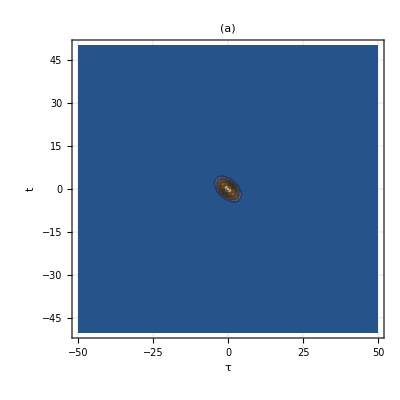

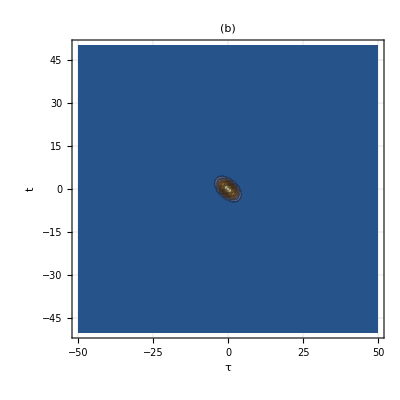

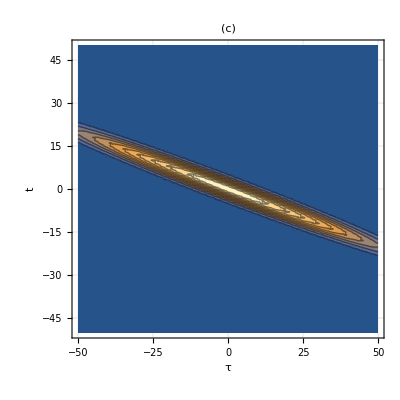

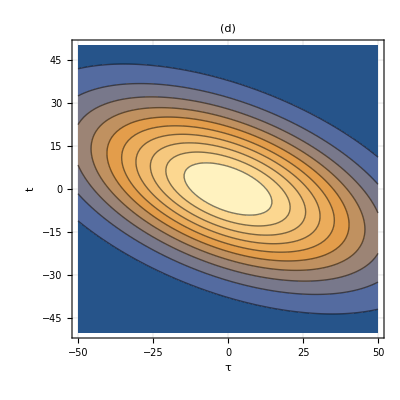

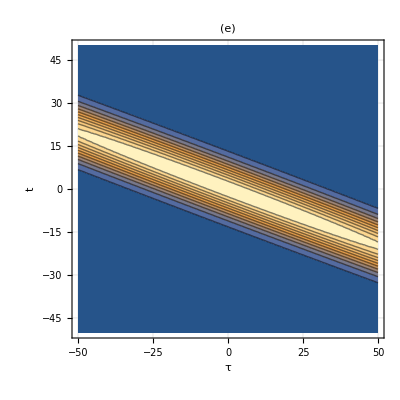

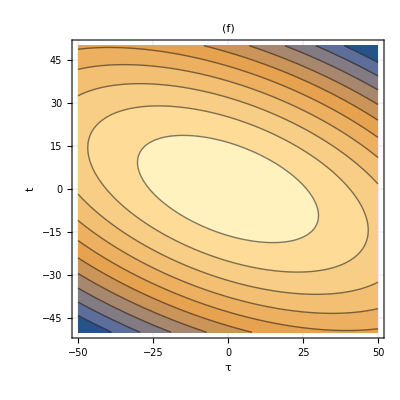

```mathematica
p1[1]
p2[1]
p1[2]
p2[2]
p1[3]
p2[3]
```

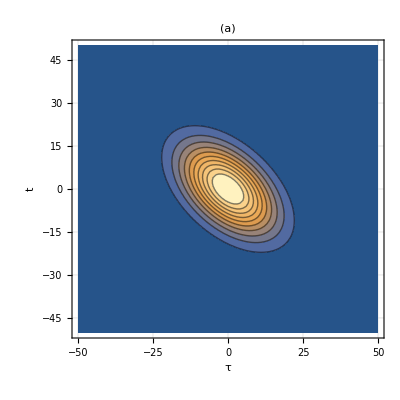

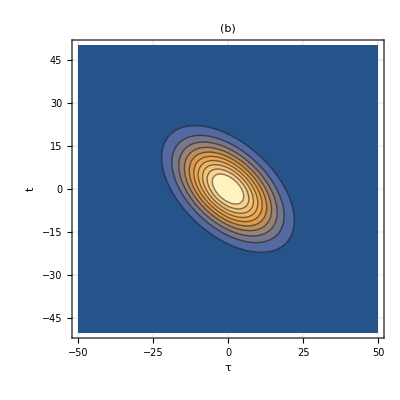

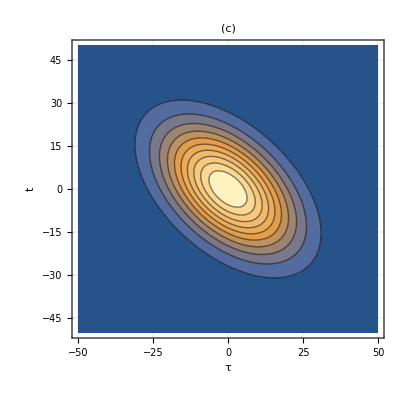

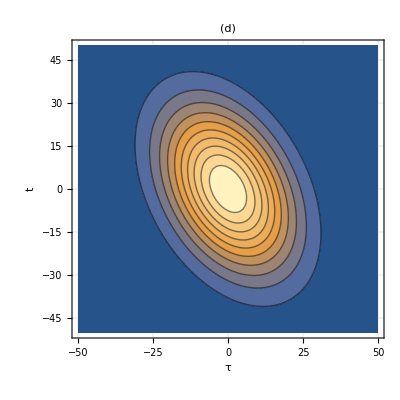

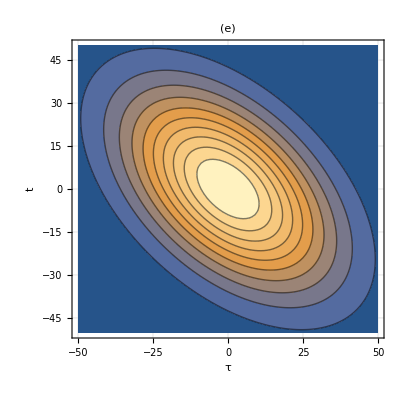

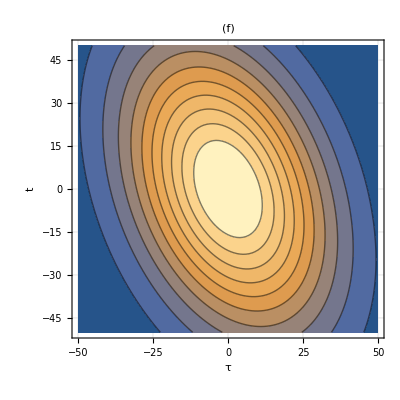

```mathematica
p1[1]
p2[1]
p1[2]
p2[2]
p1[3]
p2[3]
```

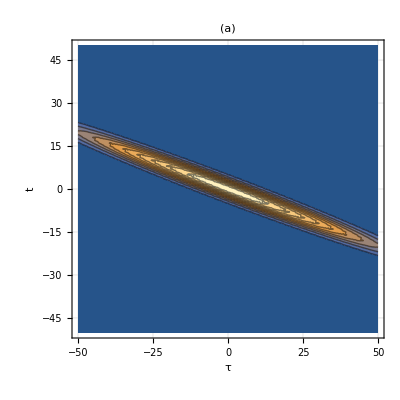

```mathematica
ListContourPlot[quantum[2][[newrange+1-range;;newrange+1+range,newrange+1-range;;newrange+1+range]],DataRange->{{-range,range},{-range,range}}, FrameLabel->{τ,t},RotateLabel-> False,LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->FromCharacterCode[{40,95+2 1,41}],PlotRange->Full,Contours->10,ImageSize->Scaled[0.5],ColorFunctionScaling->True]
```

```mathematica
ListContourPlot[qunumerical12312point5zeropoint5,DataRange->{{-range,range},{-range,range}}, FrameLabel->{τ,t},RotateLabel-> False,LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->FromCharacterCode[{40,96+2 1,41}],PlotRange->Full,Contours->10,ImageSize->Scaled[0.5],ColorFunctionScaling->True]
```

-Graphics-

## Model fitting

```mathematica
model=a Exp[(-(Cos[ϕ]^2(Cos[θ]t-Sin[θ]τ)^2+Sin[ϕ]^2(Sin[θ]t+Cos[θ]τ)^2))/(2 σ^2)];
Monitor[Do[
l=1;
range =(Dimensions[classical[k]][[1]]-1)/2;
cIdxData[k]= Table[{i-range -1,j-range-1,classical[k][[i,j]]},{i,1,2range+1},{j,1,2range+1}];
l=l+1;
cData[k]=Flatten[cIdxData[k],1];
cfit[k] = FindFit[cData[k],model,{{a,0.5},σ,θ,ϕ},{t,τ}];
l=l+1;
qIdxData[k]= Table[{i-range -1,j-range-1,quantum[k][[i,j]]},{i,1,2range+1},{j,1,2range+1}];
l=l+1;
qData[k]=Flatten[qIdxData[k],1];
qfit[k] = FindFit[qData[k],model,{{a,0.5},σ,θ,ϕ},{t,τ}],
  {k,1,3}],{k,l}]
```

Comparing (a) and (b)

```mathematica
qfit[1]
```

{a→0.0459441,σ→1.22474,θ→0.785398,ϕ→1.0472}

```mathematica
cfit[1]
```

{a→0.0459441,σ→1.22474,θ→0.785398,ϕ→1.0472}

Comparing (c) and (d)

```mathematica
qfit[2]
```

{a→0.00114681,σ→7.75202,θ→0.785398,ϕ→2.0944}

```mathematica
cfit[2]
```

{a→0.00066769,σ→10.1192,θ→0.299863,ϕ→2.08762}

Comparing (e) and (f),

```mathematica
qfit[3]
```

{a→0.0000733931,σ→30.6431,θ→0.785398,ϕ→2.0944}

```mathematica
cfit[3]
```

{a→0.0000423961,σ→40.1136,θ→0.29437,ϕ→2.08577}

## Table of σ parameters of the fits (First column is for quantum results, Second column for the corresponding classical results)

```mathematica
MatrixForm[Table[{qfit[i][[2,2]],cfit[i][[2,2]]},{i,1,3}]]
```

(1.22474 | 1.22474
7.75202 | 10.1192
30.6431 | 40.1136)

```mathematica
mat={{1,2,3,4,5},{2,3,4,5,6},{9,8,7,6,5},{1,4,2,5,3},{9,1,8,2,7}};
mat//MatrixForm
```

(1 | 2 | 3 | 4 | 5
2 | 3 | 4 | 5 | 6
9 | 8 | 7 | 6 | 5
1 | 4 | 2 | 5 | 3
9 | 1 | 8 | 2 | 7)

```mathematica
ListContourPlot[mat,PlotLegends->Automatic]
```

-Graphics-